This notebook shows the evolution of the entanglement entropy of the Haagerup chain across DMRG sweeps, for length 50 and 100. As you can see the EE of the length 50 chain looks quite stable, while I am not sure if the length 100 chain has stabilized.  They  don’t look gapped but they don’t look CFT either.

## Data

```mathematica
Y100={{{1,0.0000000000},{2,0.1114412589},{3,0.1058792747},{4,0.1556285612},{5,0.1353461727},{6,0.1938609796},{7,0.1560989395},{8,0.1860453942},{9,0.1528413388},{10,0.1503767102},{11,0.0189069094},{12,0.0079546333},{13,0.0160996574},{14,0.0089111381},{15,0.0229568726},{16,0.0646358189},{17,0.0872930147},{18,0.1123278629},{19,0.1282196312},{20,0.1318875700},{21,0.1373073612},{22,0.1347646647},{23,0.1371238782},{24,0.1373892985},{25,0.1366138949},{26,0.1363679460},{27,0.1341439402},{28,0.1362175200},{29,0.1348452436},{30,0.1334232035},{31,0.1327877798},{32,0.1361452118},{33,0.1334067746},{34,0.1162678070},{35,0.0634586755},{36,0.0653963714},{37,0.0601461050},{38,0.0890678186},{39,0.1230091065},{40,0.1350692818},{41,0.1154108689},{42,0.1299241761},{43,0.1293628710},{44,0.1343890876},{45,0.1819986401},{46,0.1631405704},{47,0.1712230347},{48,0.1077832669},{49,0.1213110115},{50,0.1302179161},{51,0.1400236360},{52,0.1366020306},{53,0.1402512119},{54,0.1325052855},{55,0.1365894693},{56,0.1451347613},{57,0.1405668933},{58,0.1199474583},{59,0.1251460322},{60,0.1259568841},{61,0.1237365565},{62,0.1583856689},{63,0.1392448285},{64,0.1224555557},{65,0.1406370037},{66,0.1301255909},{67,0.1302514883},{68,0.1325128295},{69,0.1302764441},{70,0.1334391086},{71,0.1323960295},{72,0.1345933292},{73,0.1352220845},{74,0.1357665614},{75,0.1348578287},{76,0.1344816821},{77,0.1356333962},{78,0.1359392992},{79,0.1351068530},{80,0.1358665200},{81,0.1354286267},{82,0.1356321637},{83,0.1347834587},{84,0.1355998030},{85,0.1352743075},{86,0.1353756059},{87,0.1347618582},{88,0.1353496149},{89,0.1353271014},{90,0.1357351477},{91,0.1350461754},{92,0.1354895642},{93,0.1351071405},{94,0.1318044512},{95,0.1317167333},{96,0.1359295331},{97,0.1354032191},{98,0.2854265021},{99,-0.0000000000}},{{1,0.0000000000},{2,0.1182176617},{3,0.1106434206},{4,0.1573451475},{5,0.1376791436},{6,0.1982449207},{7,0.1606474265},{8,0.1880221668},{9,0.1491413092},{10,0.1492808414},{11,0.0257326752},{12,0.0118906012},{13,0.0205226035},{14,0.0116821198},{15,0.0297312075},{16,0.0727579405},{17,0.0906915011},{18,0.1132283723},{19,0.1311734054},{20,0.1331524931},{21,0.1377775785},{22,0.1350463107},{23,0.1387218590},{24,0.1390879746},{25,0.1389013439},{26,0.1383466375},{27,0.1373387918},{28,0.1371204793},{29,0.1341167604},{30,0.1344193897},{31,0.1340984023},{32,0.1391193262},{33,0.1349437117},{34,0.1194823099},{35,0.0668159389},{36,0.0704986180},{37,0.0618138578},{38,0.0893400865},{39,0.1222911542},{40,0.1345309792},{41,0.1186592350},{42,0.1335436426},{43,0.1322100637},{44,0.1368592881},{45,0.1831984508},{46,0.1641692858},{47,0.1714965560},{48,0.1063393641},{49,0.1210506659},{50,0.1290514577},{51,0.1401840638},{52,0.1362111837},{53,0.1404542640},{54,0.1328556334},{55,0.1371366127},{56,0.1442680053},{57,0.1396926866},{58,0.1203356423},{59,0.1252862149},{60,0.1260201501},{61,0.1231750893},{62,0.1571948829},{63,0.1370240065},{64,0.1238073961},{65,0.1413795360},{66,0.1301755305},{67,0.1309716773},{68,0.1337182909},{69,0.1310676560},{70,0.1345176000},{71,0.1330856490},{72,0.1355599110},{73,0.1360941458},{74,0.1369492889},{75,0.1360620360},{76,0.1349655824},{77,0.1361093966},{78,0.1366192733},{79,0.1350204008},{80,0.1361919809},{81,0.1346737484},{82,0.1350229634},{83,0.1336139590},{84,0.1360288015},{85,0.1363045282},{86,0.1353013061},{87,0.1355076168},{88,0.1365661493},{89,0.1364158553},{90,0.1360103382},{91,0.1357677729},{92,0.1347491203},{93,0.1344255926},{94,0.1375660527},{95,0.1362582799},{96,0.1585996391},{97,0.1463835659},{98,0.2729944745},{99,-0.0000000000}},{{1,0.0000000000},{2,0.1310735152},{3,0.1211196300},{4,0.1647630895},{5,0.1466067507},{6,0.2100509220},{7,0.1745989561},{8,0.1927217966},{9,0.1451683599},{10,0.1478886036},{11,0.0424712006},{12,0.0242427447},{13,0.0324219365},{14,0.0230172653},{15,0.0437499247},{16,0.0870848812},{17,0.1031609072},{18,0.1221495813},{19,0.1404578545},{20,0.1396268259},{21,0.1426070777},{22,0.1391086298},{23,0.1445346805},{24,0.1445473556},{25,0.1450474869},{26,0.1434124089},{27,0.1426071395},{28,0.1401771923},{29,0.1357063917},{30,0.1393052558},{31,0.1392390213},{32,0.1453356581},{33,0.1393084088},{34,0.1250999785},{35,0.0734288100},{36,0.0774293784},{37,0.0655146161},{38,0.0923182212},{39,0.1240576971},{40,0.1353025819},{41,0.1237313090},{42,0.1391395094},{43,0.1377138368},{44,0.1422681253},{45,0.1872652316},{46,0.1677605406},{47,0.1735890158},{48,0.1067394091},{49,0.1224521328},{50,0.1302009496},{51,0.1422121646},{52,0.1369578531},{53,0.1418790125},{54,0.1347451540},{55,0.1391558665},{56,0.1449671988},{57,0.1403622452},{58,0.1217941571},{59,0.1268007079},{60,0.1273386714},{61,0.1237754333},{62,0.1563232619},{63,0.1331311030},{64,0.1258688527},{65,0.1445298700},{66,0.1314709173},{67,0.1335577719},{68,0.1370858048},{69,0.1349812173},{70,0.1368986053},{71,0.1345876832},{72,0.1375818365},{73,0.1374645845},{74,0.1385345124},{75,0.1379639560},{76,0.1369190806},{77,0.1379118102},{78,0.1383957010},{79,0.1363266020},{80,0.1379977671},{81,0.1360367565},{82,0.1363737988},{83,0.1348658005},{84,0.1381386379},{85,0.1396165131},{86,0.1372413764},{87,0.1389381250},{88,0.1396729450},{89,0.1402399343},{90,0.1398869389},{91,0.1380230099},{92,0.1359086106},{93,0.1352671915},{94,0.1517147482},{95,0.1490146555},{96,0.1986248756},{97,0.1753514712},{98,0.2629620463},{99,0.0000000000}},{{1,0.0000000000},{2,0.1402399690},{3,0.1292431232},{4,0.1708839411},{5,0.1533926668},{6,0.2181483044},{7,0.1837174981},{8,0.1990649407},{9,0.1480258742},{10,0.1511769832},{11,0.0562275174},{12,0.0364270600},{13,0.0434189053},{14,0.0322486393},{15,0.0564907060},{16,0.0996051849},{17,0.1124126478},{18,0.1301477219},{19,0.1484395602},{20,0.1463663778},{21,0.1488604716},{22,0.1444196948},{23,0.1503774011},{24,0.1505501662},{25,0.1513715927},{26,0.1491199569},{27,0.1479301270},{28,0.1445658957},{29,0.1399444456},{30,0.1458282733},{31,0.1448911220},{32,0.1516020918},{33,0.1458214031},{34,0.1316087599},{35,0.0813256206},{36,0.0853229877},{37,0.0714092263},{38,0.0978425892},{39,0.1287757699},{40,0.1391335982},{41,0.1291593276},{42,0.1456453451},{43,0.1458706986},{44,0.1501301129},{45,0.1925457603},{46,0.1731903547},{47,0.1777503348},{48,0.1100126872},{49,0.1263787623},{50,0.1345185792},{51,0.1464023432},{52,0.1390090320},{53,0.1445900796},{54,0.1376027634},{55,0.1419335860},{56,0.1468155659},{57,0.1420410356},{58,0.1248373808},{59,0.1294796545},{60,0.1301597007},{61,0.1256140860},{62,0.1566578205},{63,0.1319085880},{64,0.1282992850},{65,0.1484265158},{66,0.1338547377},{67,0.1374497860},{68,0.1413548468},{69,0.1408929485},{70,0.1409426662},{71,0.1372558537},{72,0.1409475489},{73,0.1391758884},{74,0.1409036054},{75,0.1410643930},{76,0.1401402678},{77,0.1407213641},{78,0.1408186575},{79,0.1381878134},{80,0.1397910849},{81,0.1379095640},{82,0.1380155560},{83,0.1365736091},{84,0.1400600845},{85,0.1430647998},{86,0.1399294591},{87,0.1420878007},{88,0.1426346948},{89,0.1446212592},{90,0.1433138450},{91,0.1402841664},{92,0.1368903931},{93,0.1359084391},{94,0.1541522832},{95,0.1511908753},{96,0.2041105335},{97,0.1794485371},{98,0.2621295350},{99,0.0000000000}},{{1,0.0000000000},{2,0.1566465608},{3,0.1442266917},{4,0.1840265215},{5,0.1680536889},{6,0.2297502621},{7,0.1962562890},{8,0.2094180840},{9,0.1558026852},{10,0.1591139846},{11,0.0796605341},{12,0.0608509798},{13,0.0659326377},{14,0.0524749208},{15,0.0786703715},{16,0.1221892259},{17,0.1313255112},{18,0.1495023376},{19,0.1662163608},{20,0.1623921998},{21,0.1638443464},{22,0.1571987249},{23,0.1627593131},{24,0.1635090624},{25,0.1633380759},{26,0.1602892541},{27,0.1586788334},{28,0.1536569263},{29,0.1489260991},{30,0.1569215728},{31,0.1548746551},{32,0.1613557580},{33,0.1555530442},{34,0.1406688582},{35,0.0914948789},{36,0.0951142042},{37,0.0807843422},{38,0.1073778444},{39,0.1367820577},{40,0.1461558892},{41,0.1374944684},{42,0.1543554152},{43,0.1560731298},{44,0.1596970076},{45,0.2002277315},{46,0.1810426766},{47,0.1828222475},{48,0.1157508562},{49,0.1327105490},{50,0.1414036650},{51,0.1525594876},{52,0.1426741265},{53,0.1490478687},{54,0.1419364972},{55,0.1460907971},{56,0.1498469819},{57,0.1450577728},{58,0.1293510646},{59,0.1337250343},{60,0.1351881445},{61,0.1295362563},{62,0.1584341295},{63,0.1331352709},{64,0.1328375304},{65,0.1541693291},{66,0.1380958102},{67,0.1427680040},{68,0.1468569667},{69,0.1481320055},{70,0.1468482465},{71,0.1415039279},{72,0.1456325814},{73,0.1427545913},{74,0.1443078606},{75,0.1449806742},{76,0.1442233330},{77,0.1445247598},{78,0.1441754233},{79,0.1413585871},{80,0.1433398483},{81,0.1412899243},{82,0.1412501716},{83,0.1398083839},{84,0.1437853594},{85,0.1480643037},{86,0.1450801386},{87,0.1468448572},{88,0.1488788486},{89,0.1528794711},{90,0.1507693239},{91,0.1483735347},{92,0.1407731262},{93,0.1359262052},{94,0.1636119129},{95,0.1583474711},{96,0.2252753444},{97,0.1960851719},{98,0.2620333188},{99,0.0000000000}},{{1,0.0000000000},{2,0.1661239173},{3,0.1531934665},{4,0.1927217989},{5,0.1776360316},{6,0.2381717330},{7,0.2060257379},{8,0.2182600199},{9,0.1646268614},{10,0.1677286385},{11,0.1007069330},{12,0.0844778717},{13,0.0872128051},{14,0.0713972100},{15,0.0988178051},{16,0.1415619973},{17,0.1477073976},{18,0.1668474457},{19,0.1809465799},{20,0.1780139898},{21,0.1800448269},{22,0.1726519171},{23,0.1760653689},{24,0.1765820082},{25,0.1754636635},{26,0.1722622941},{27,0.1707602817},{28,0.1646578166},{29,0.1604193648},{30,0.1696451135},{31,0.1671209656},{32,0.1722583585},{33,0.1669287104},{34,0.1512262643},{35,0.1025638723},{36,0.1064487255},{37,0.0932701006},{38,0.1199245447},{39,0.1476672094},{40,0.1572654112},{41,0.1495407556},{42,0.1659436277},{43,0.1690032202},{44,0.1716255658},{45,0.2102759428},{46,0.1919244767},{47,0.1893637666},{48,0.1242666308},{49,0.1419002922},{50,0.1512747674},{51,0.1609710078},{52,0.1496452964},{53,0.1568950736},{54,0.1483853146},{55,0.1517675521},{56,0.1542835761},{57,0.1500678597},{58,0.1357487725},{59,0.1397998269},{60,0.1422525402},{61,0.1353754273},{62,0.1623880293},{63,0.1367514376},{64,0.1395294480},{65,0.1611535500},{66,0.1440717822},{67,0.1494474977},{68,0.1542191895},{69,0.1568321678},{70,0.1546147044},{71,0.1478669709},{72,0.1515016131},{73,0.1470123138},{74,0.1487242349},{75,0.1501606455},{76,0.1495748843},{77,0.1494246383},{78,0.1484495129},{79,0.1455147115},{80,0.1473703340},{81,0.1453224185},{82,0.1451590182},{83,0.1434774978},{84,0.1485247079},{85,0.1535363507},{86,0.1502778604},{87,0.1506660426},{88,0.1558888035},{89,0.1615531932},{90,0.1575515513},{91,0.1538190711},{92,0.1459364583},{93,0.1411292020},{94,0.1711423265},{95,0.1659095436},{96,0.2345258407},{97,0.2023664428},{98,0.2620784091},{99,0.0000000000}},{{1,0.0000000000},{2,0.1708708119},{3,0.1577420509},{4,0.1971428366},{5,0.1821994874},{6,0.2427769953},{7,0.2115964284},{8,0.2233159428},{9,0.1699458964},{10,0.1730302955},{11,0.1129273592},{12,0.0978516730},{13,0.0985908712},{14,0.0811441589},{15,0.1095733807},{16,0.1512229621},{17,0.1569477458},{18,0.1763402851},{19,0.1896698330},{20,0.1875680415},{21,0.1897812499},{22,0.1830593198},{23,0.1857497753},{24,0.1858966554},{25,0.1843651462},{26,0.1814170894},{27,0.1802123361},{28,0.1742060316},{29,0.1699972922},{30,0.1796172715},{31,0.1768610956},{32,0.1811037547},{33,0.1758283075},{34,0.1600935555},{35,0.1123291460},{36,0.1164105321},{37,0.1038264864},{38,0.1297851538},{39,0.1562763395},{40,0.1664115750},{41,0.1604321049},{42,0.1762067979},{43,0.1796884735},{44,0.1813924324},{45,0.2186775930},{46,0.2006373190},{47,0.1952372749},{48,0.1329493755},{49,0.1499307054},{50,0.1592172559},{51,0.1683203616},{52,0.1572586481},{53,0.1646786439},{54,0.1540110119},{55,0.1561770547},{56,0.1578798299},{57,0.1546442300},{58,0.1411391964},{59,0.1447278087},{60,0.1482041296},{61,0.1403246077},{62,0.1658292140},{63,0.1412371062},{64,0.1453482338},{65,0.1655751472},{66,0.1489612801},{67,0.1543536776},{68,0.1596999146},{69,0.1618036068},{70,0.1588886542},{71,0.1518558166},{72,0.1554919254},{73,0.1507253098},{74,0.1529685582},{75,0.1542407651},{76,0.1540039249},{77,0.1533876284},{78,0.1517352703},{79,0.1494112277},{80,0.1512481507},{81,0.1489459013},{82,0.1490870921},{83,0.1476385213},{84,0.1529738865},{85,0.1584718206},{86,0.1553288593},{87,0.1550395856},{88,0.1634613013},{89,0.1706089071},{90,0.1650140567},{91,0.1610676183},{92,0.1521196477},{93,0.1465209928},{94,0.1803369799},{95,0.1739184017},{96,0.2447377975},{97,0.2102050140},{98,0.2629762314},{99,0.0000000000}},{{1,0.0000000000},{2,0.1784130579},{3,0.1650658394},{4,0.2047995532},{5,0.1905688334},{6,0.2496636166},{7,0.2194559184},{8,0.2303520977},{9,0.1782954158},{10,0.1812929249},{11,0.1287460410},{12,0.1161423839},{13,0.1139081820},{14,0.0942331910},{15,0.1227722659},{16,0.1631635993},{17,0.1692017482},{18,0.1886610162},{19,0.2013425341},{20,0.2002234568},{21,0.2019483139},{22,0.1952219372},{23,0.1972861931},{24,0.1970266856},{25,0.1948778518},{26,0.1922773581},{27,0.1916427073},{28,0.1863880762},{29,0.1816666300},{30,0.1912598179},{31,0.1883019262},{32,0.1914747059},{33,0.1861898646},{34,0.1703339636},{35,0.1227007365},{36,0.1271752335},{37,0.1156758129},{38,0.1409043895},{39,0.1663441944},{40,0.1770848927},{41,0.1732086832},{42,0.1878543226},{43,0.1915618036},{44,0.1926485469},{45,0.2288894975},{46,0.2111969804},{47,0.2023669214},{48,0.1435592423},{49,0.1594622165},{50,0.1684954642},{51,0.1774343139},{52,0.1670554862},{53,0.1744983371},{54,0.1608639345},{55,0.1614576686},{56,0.1627030092},{57,0.1609223624},{58,0.1481515274},{59,0.1509896655},{60,0.1569302044},{61,0.1474241443},{62,0.1701360766},{63,0.1477709222},{64,0.1535130323},{65,0.1709096406},{66,0.1554627167},{67,0.1616664070},{68,0.1706726696},{69,0.1700931096},{70,0.1631888224},{71,0.1572588747},{72,0.1616378834},{73,0.1553774964},{74,0.1598688794},{75,0.1597129778},{76,0.1597225974},{77,0.1587798065},{78,0.1561007697},{79,0.1545627983},{80,0.1566517217},{81,0.1542351348},{82,0.1547881383},{83,0.1533474472},{84,0.1588516417},{85,0.1642409929},{86,0.1614054290},{87,0.1602699407},{88,0.1712806280},{89,0.1788271117},{90,0.1722720018},{91,0.1682282758},{92,0.1596791442},{93,0.1523104336},{94,0.1884439729},{95,0.1813837702},{96,0.2518121728},{97,0.2154260562},{98,0.2635906879},{99,0.0000000000}},{{1,-0.0000000000},{2,0.1864676853},{3,0.1730273370},{4,0.2126680200},{5,0.1976971810},{6,0.2569059586},{7,0.2276160186},{8,0.2370580069},{9,0.1862214477},{10,0.1896304252},{11,0.1462658108},{12,0.1349015249},{13,0.1297347935},{14,0.1076004527},{15,0.1360753624},{16,0.1740409091},{17,0.1812771368},{18,0.2002455830},{19,0.2119988077},{20,0.2125931838},{21,0.2147573298},{22,0.2091219136},{23,0.2100517893},{24,0.2085959290},{25,0.2057298178},{26,0.2046624987},{27,0.2042313608},{28,0.1998748302},{29,0.1953432689},{30,0.2055026546},{31,0.2030189697},{32,0.2072567445},{33,0.2022092861},{34,0.1874354461},{35,0.1377819779},{36,0.1437310790},{37,0.1350282491},{38,0.1580444247},{39,0.1825654799},{40,0.1940117413},{41,0.1922562689},{42,0.2052218799},{43,0.2089037850},{44,0.2089116155},{45,0.2438114807},{46,0.2264218512},{47,0.2129261536},{48,0.1584392518},{49,0.1727832221},{50,0.1812637996},{51,0.1903077365},{52,0.1807385188},{53,0.1881133856},{54,0.1716726547},{55,0.1704363155},{56,0.1707650763},{57,0.1705419450},{58,0.1584351106},{59,0.1608610247},{60,0.1685193470},{61,0.1582057293},{62,0.1785052597},{63,0.1571614367},{64,0.1651155443},{65,0.1808979462},{66,0.1658423059},{67,0.1725189719},{68,0.1835456722},{69,0.1813759255},{70,0.1726121077},{71,0.1663522132},{72,0.1715140518},{73,0.1639514467},{74,0.1692683657},{75,0.1681655708},{76,0.1702310771},{77,0.1682544382},{78,0.1641853474},{79,0.1631979113},{80,0.1667480284},{81,0.1636761298},{82,0.1640260179},{83,0.1628455737},{84,0.1705949147},{85,0.1769273475},{86,0.1729661664},{87,0.1685795908},{88,0.1871350331},{89,0.1912544368},{90,0.1829872026},{91,0.1775687829},{92,0.1712512187},{93,0.1631604629},{94,0.2007046995},{95,0.1919148627},{96,0.2603499370},{97,0.2210906557},{98,0.2638299471},{99,0.0000000000}},{{1,-0.0000000000},{2,0.1911705291},{3,0.1777839667},{4,0.2176353668},{5,0.2024016522},{6,0.2610280043},{7,0.2325114823},{8,0.2416890055},{9,0.1910939221},{10,0.1944918783},{11,0.1556542307},{12,0.1451927641},{13,0.1382459965},{14,0.1150355542},{15,0.1432149181},{16,0.1798360386},{17,0.1877967679},{18,0.2061576776},{19,0.2173668782},{20,0.2187318949},{21,0.2211438628},{22,0.2163151148},{23,0.2171031234},{24,0.2156575139},{25,0.2128528256},{26,0.2125884440},{27,0.2123919824},{28,0.2079026092},{29,0.2035056536},{30,0.2154678036},{31,0.2125618004},{32,0.2164775876},{33,0.2112218973},{34,0.1964425616},{35,0.1469160997},{36,0.1531559726},{37,0.1455569497},{38,0.1669539508},{39,0.1905997452},{40,0.2027969136},{41,0.2031211620},{42,0.2154054581},{43,0.2189999584},{44,0.2184689432},{45,0.2527963396},{46,0.2354816928},{47,0.2197174998},{48,0.1684373683},{49,0.1817624611},{50,0.1896601638},{51,0.1986748346},{52,0.1897038383},{53,0.1968223854},{54,0.1790681269},{55,0.1771964061},{56,0.1770712908},{57,0.1776980262},{58,0.1664933530},{59,0.1686737791},{60,0.1771778240},{61,0.1665423745},{62,0.1852876335},{63,0.1645477801},{64,0.1739179062},{65,0.1883736865},{66,0.1740006283},{67,0.1810234794},{68,0.1933753151},{69,0.1905353527},{70,0.1805163703},{71,0.1739530077},{72,0.1794853799},{73,0.1711928726},{74,0.1765698542},{75,0.1752742016},{76,0.1782157347},{77,0.1754991017},{78,0.1716088999},{79,0.1706004429},{80,0.1750612941},{81,0.1717773153},{82,0.1718044080},{83,0.1710848565},{84,0.1798118361},{85,0.1860114240},{86,0.1816448636},{87,0.1762195080},{88,0.1977204515},{89,0.2005437393},{90,0.1924794973},{91,0.1860977055},{92,0.1817205162},{93,0.1731241324},{94,0.2112628388},{95,0.2009724913},{96,0.2674810852},{97,0.2256651547},{98,0.2642727692},{99,0.0000000000}},{{1,0.0000000000},{2,0.1973394042},{3,0.1842085356},{4,0.2248116601},{5,0.2097891987},{6,0.2668485461},{7,0.2396083336},{8,0.2496867503},{9,0.1998722062},{10,0.2028703204},{11,0.1686227462},{12,0.1593533321},{13,0.1492021839},{14,0.1244371167},{15,0.1521149638},{16,0.1865454542},{17,0.1953994433},{18,0.2132408155},{19,0.2241492957},{20,0.2266494144},{21,0.2294054318},{22,0.2252306660},{23,0.2257961166},{24,0.2240257624},{25,0.2210098330},{26,0.2210360901},{27,0.2210623540},{28,0.2164872593},{29,0.2120929298},{30,0.2254300448},{31,0.2224842794},{32,0.2261848134},{33,0.2205727383},{34,0.2054357991},{35,0.1563132180},{36,0.1627094467},{37,0.1560729964},{38,0.1758153378},{39,0.1986357767},{40,0.2113742243},{41,0.2133427853},{42,0.2253354011},{43,0.2282790568},{44,0.2275491217},{45,0.2606655375},{46,0.2433450332},{47,0.2266463287},{48,0.1783575645},{49,0.1906468088},{50,0.1976289519},{51,0.2065153731},{52,0.1982422433},{53,0.2054871000},{54,0.1869009624},{55,0.1845547855},{56,0.1842345050},{57,0.1856890128},{58,0.1752398854},{59,0.1773149901},{60,0.1863856865},{61,0.1756356464},{62,0.1931135850},{63,0.1726598827},{64,0.1829113695},{65,0.1959771638},{66,0.1820104878},{67,0.1891923755},{68,0.2029493721},{69,0.1990397023},{70,0.1887703082},{71,0.1817945502},{72,0.1873747240},{73,0.1788623363},{74,0.1843647349},{75,0.1833895096},{76,0.1858173458},{77,0.1835896491},{78,0.1799002928},{79,0.1791646255},{80,0.1851020276},{81,0.1813477752},{82,0.1814015055},{83,0.1812673190},{84,0.1913446108},{85,0.1976413341},{86,0.1946811428},{87,0.1888965862},{88,0.2151655828},{89,0.2179197808},{90,0.2127576757},{91,0.2046380860},{92,0.2088187305},{93,0.1900087979},{94,0.2501644231},{95,0.2070269086},{96,0.2890246241},{97,0.2622638092},{98,0.2688013418},{99,0.0000000000}},{{1,0.0000000000},{2,0.2045414827},{3,0.1916692846},{4,0.2333376582},{5,0.2190388959},{6,0.2731890729},{7,0.2472205167},{8,0.2577585357},{9,0.2096924932},{10,0.2122179502},{11,0.1812068489},{12,0.1718790980},{13,0.1583202578},{14,0.1331719799},{15,0.1601158293},{16,0.1931157919},{17,0.2021747779},{18,0.2195054032},{19,0.2298890346},{20,0.2336637055},{21,0.2369249242},{22,0.2326923216},{23,0.2331155157},{24,0.2313490400},{25,0.2279638006},{26,0.2284366701},{27,0.2281535413},{28,0.2235975151},{29,0.2189577903},{30,0.2327734214},{31,0.2298965320},{32,0.2328077790},{33,0.2271684719},{34,0.2119066708},{35,0.1633913164},{36,0.1695508535},{37,0.1634394552},{38,0.1817651531},{39,0.2036652859},{40,0.2166938226},{41,0.2196639379},{42,0.2315746213},{43,0.2340527783},{44,0.2330686973},{45,0.2649608328},{46,0.2476272146},{47,0.2309889108},{48,0.1849630166},{49,0.1964531335},{50,0.2027549945},{51,0.2115551690},{52,0.2037287856},{53,0.2111552383},{54,0.1924936777},{55,0.1895330352},{56,0.1889597582},{57,0.1908513237},{58,0.1810295191},{59,0.1828367708},{60,0.1923303952},{61,0.1811292103},{62,0.1980280476},{63,0.1780668844},{64,0.1882243110},{65,0.2000183389},{66,0.1867245452},{67,0.1939760571},{68,0.2080276163},{69,0.2040835911},{70,0.1933459462},{71,0.1866858745},{72,0.1927396154},{73,0.1840185825},{74,0.1895709095},{75,0.1888754529},{76,0.1912431371},{77,0.1891575526},{78,0.1855827132},{79,0.1849691530},{80,0.1918442370},{81,0.1876769059},{82,0.1875561671},{83,0.1879877195},{84,0.1985943858},{85,0.2045473204},{86,0.2018616482},{87,0.1957233484},{88,0.2243412241},{89,0.2262878562},{90,0.2214510888},{91,0.2122504320},{92,0.2178879833},{93,0.1980556583},{94,0.2574259445},{95,0.2160094442},{96,0.2921036462},{97,0.2619180879},{98,0.2681317496},{99,0.0000000000}},{{1,0.0000000000},{2,0.2096271776},{3,0.1972409146},{4,0.2396624273},{5,0.2251297469},{6,0.2783436612},{7,0.2527421399},{8,0.2630198605},{9,0.2162271743},{10,0.2190174659},{11,0.1915797924},{12,0.1827514560},{13,0.1666075100},{14,0.1418473008},{15,0.1685122038},{16,0.2001792647},{17,0.2088473345},{18,0.2254003422},{19,0.2354100893},{20,0.2416193733},{21,0.2460796750},{22,0.2430741965},{23,0.2433311012},{24,0.2422497273},{25,0.2388658539},{26,0.2406072503},{27,0.2401898057},{28,0.2355343321},{29,0.2306964543},{30,0.2461038595},{31,0.2432739493},{32,0.2439365731},{33,0.2387486382},{34,0.2237323279},{35,0.1764708579},{36,0.1828821910},{37,0.1777685131},{38,0.1919756642},{39,0.2107753578},{40,0.2247607334},{41,0.2299548931},{42,0.2417177280},{43,0.2430106890},{44,0.2416147840},{45,0.2710699623},{46,0.2538151168},{47,0.2391669340},{48,0.1997427116},{49,0.2092889286},{50,0.2137181229},{51,0.2218763764},{52,0.2153016217},{53,0.2232354612},{54,0.2047311696},{55,0.2004484503},{56,0.1988548051},{57,0.2014838387},{58,0.1936827235},{59,0.1947585963},{60,0.2053769478},{61,0.1927772444},{62,0.2084564329},{63,0.1898025499},{64,0.1999329832},{65,0.2089436269},{66,0.1962601391},{67,0.2037062024},{68,0.2189035571},{69,0.2143877400},{70,0.2033771587},{71,0.1968957532},{72,0.2019482953},{73,0.1926006297},{74,0.1990293498},{75,0.1982986988},{76,0.2000490422},{77,0.1983914996},{78,0.1948306532},{79,0.1942382527},{80,0.2014844825},{81,0.1963792515},{82,0.1960811351},{83,0.1968444215},{84,0.2079375037},{85,0.2132806932},{86,0.2113643380},{87,0.2048031391},{88,0.2352576344},{89,0.2366083307},{90,0.2318106641},{91,0.2213249548},{92,0.2278389600},{93,0.2060461057},{94,0.2655904278},{95,0.2265097551},{96,0.2951346604},{97,0.2582687041},{98,0.2630225893},{99,0.0000000000}},{{1,-0.0000000000},{2,0.2151026040},{3,0.2033275630},{4,0.2467684129},{5,0.2316633007},{6,0.2835936864},{7,0.2582513436},{8,0.2682009960},{9,0.2225592731},{10,0.2256095958},{11,0.2014246370},{12,0.1928269631},{13,0.1748065754},{14,0.1509967083},{15,0.1773033975},{16,0.2078971232},{17,0.2165341544},{18,0.2323571318},{19,0.2416609204},{20,0.2505742766},{21,0.2564885724},{22,0.2549705586},{23,0.2547566436},{24,0.2530840919},{25,0.2489650306},{26,0.2509238233},{27,0.2500121487},{28,0.2454499382},{29,0.2408963502},{30,0.2567313253},{31,0.2547222837},{32,0.2546832216},{33,0.2496639129},{34,0.2351622314},{35,0.1900543839},{36,0.1965711919},{37,0.1923715263},{38,0.2032354442},{39,0.2205108328},{40,0.2348106144},{41,0.2412608000},{42,0.2530594585},{43,0.2528104878},{44,0.2504960569},{45,0.2777158468},{46,0.2602358736},{47,0.2468810150},{48,0.2125924841},{49,0.2204887925},{50,0.2226537290},{51,0.2304667394},{52,0.2250357062},{53,0.2332625446},{54,0.2148984248},{55,0.2104803566},{56,0.2083248721},{57,0.2114755589},{58,0.2054842058},{59,0.2059253979},{60,0.2171758318},{61,0.2043593440},{62,0.2184386837},{63,0.2009580460},{64,0.2110888945},{65,0.2180466952},{66,0.2061431805},{67,0.2136454103},{68,0.2289898276},{69,0.2248358859},{70,0.2133961728},{71,0.2072167607},{72,0.2118450202},{73,0.2018229847},{74,0.2090142927},{75,0.2083358450},{76,0.2094285542},{77,0.2081242713},{78,0.2044601197},{79,0.2039624946},{80,0.2118565809},{81,0.2065663096},{82,0.2060595876},{83,0.2073450221},{84,0.2190553617},{85,0.2246409012},{86,0.2253723178},{87,0.2191373973},{88,0.2520026384},{89,0.2542216834},{90,0.2567925717},{91,0.2436755650},{92,0.2620309007},{93,0.2228366502},{94,0.2957669539},{95,0.2781013597},{96,0.3133140557},{97,0.2634678492},{98,0.2630645845},{99,0.0000000000}},{{1,0.0000000000},{2,0.2186608491},{3,0.2074287324},{4,0.2516392732},{5,0.2366266046},{6,0.2876856211},{7,0.2627799963},{8,0.2728273380},{9,0.2284045047},{10,0.2317600557},{11,0.2099617467},{12,0.2016911444},{13,0.1811082131},{14,0.1581112269},{15,0.1836608834},{16,0.2129054219},{17,0.2215257137},{18,0.2366731733},{19,0.2458631492},{20,0.2562020911},{21,0.2629507999},{22,0.2621595668},{23,0.2615919309},{24,0.2599747395},{25,0.2560275083},{26,0.2588763236},{27,0.2578371693},{28,0.2531211500},{29,0.2486444939},{30,0.2655875602},{31,0.2637742220},{32,0.2627842198},{33,0.2580020048},{34,0.2435876574},{35,0.1995931840},{36,0.2065184026},{37,0.2032859736},{38,0.2113161960},{39,0.2273997315},{40,0.2418283195},{41,0.2493442913},{42,0.2612149928},{43,0.2593634016},{44,0.2567324064},{45,0.2820045136},{46,0.2646260522},{47,0.2527484099},{48,0.2221711006},{49,0.2289673907},{50,0.2294390036},{51,0.2371909471},{52,0.2329580900},{53,0.2417592274},{54,0.2241191281},{55,0.2199413743},{56,0.2175430341},{57,0.2210562202},{58,0.2165314081},{59,0.2163635607},{60,0.2281451755},{61,0.2150874722},{62,0.2276457489},{63,0.2105832615},{64,0.2206740771},{65,0.2260636153},{66,0.2143218867},{67,0.2221715027},{68,0.2375729157},{69,0.2337712204},{70,0.2213957033},{71,0.2154028588},{72,0.2196353377},{73,0.2093993556},{74,0.2168308994},{75,0.2163495518},{76,0.2170842363},{77,0.2157600280},{78,0.2121125209},{79,0.2113301545},{80,0.2190311035},{81,0.2133229290},{82,0.2122601436},{83,0.2138683003},{84,0.2252798863},{85,0.2305676535},{86,0.2323899919},{87,0.2263384613},{88,0.2599751229},{89,0.2623211487},{90,0.2670741168},{91,0.2529827051},{92,0.2728298518},{93,0.2312714506},{94,0.3013750531},{95,0.2854169639},{96,0.3153143474},{97,0.2648547729},{98,0.2639384260},{99,0.0000000000}},{{1,0.0000000000},{2,0.2219175018},{3,0.2112276698},{4,0.2564147317},{5,0.2415855247},{6,0.2923476624},{7,0.2680952891},{8,0.2780517605},{9,0.2353544655},{10,0.2401667257},{11,0.2231637552},{12,0.2157042363},{13,0.1931781950},{14,0.1723530358},{15,0.1967679008},{16,0.2256156968},{17,0.2341773125},{18,0.2480118090},{19,0.2565994646},{20,0.2704821823},{21,0.2789798082},{22,0.2794701043},{23,0.2791774778},{24,0.2743650661},{25,0.2688888367},{26,0.2715094848},{27,0.2702180851},{28,0.2665804304},{29,0.2632836878},{30,0.2798971359},{31,0.2805911175},{32,0.2794111892},{33,0.2736959030},{34,0.2582942490},{35,0.2165142667},{36,0.2213665861},{37,0.2175392907},{38,0.2231696111},{39,0.2382301093},{40,0.2519403788},{41,0.2599988749},{42,0.2725950576},{43,0.2694017708},{44,0.2663166235},{45,0.2900427001},{46,0.2726332078},{47,0.2606937142},{48,0.2340079679},{49,0.2397384052},{50,0.2385462494},{51,0.2460065682},{52,0.2430167182},{53,0.2523695961},{54,0.2345505534},{55,0.2306458802},{56,0.2281538533},{57,0.2319953509},{58,0.2283224664},{59,0.2274750613},{60,0.2387794616},{61,0.2263518738},{62,0.2370812774},{63,0.2214260196},{64,0.2318339795},{65,0.2359601333},{66,0.2251071929},{67,0.2331694384},{68,0.2478018089},{69,0.2444459302},{70,0.2315373342},{71,0.2260525239},{72,0.2297498744},{73,0.2196680926},{74,0.2267786029},{75,0.2264066223},{76,0.2267184474},{77,0.2254822627},{78,0.2219259497},{79,0.2208683565},{80,0.2286762423},{81,0.2219878678},{82,0.2199011123},{83,0.2218677195},{84,0.2329519265},{85,0.2372388621},{86,0.2402004500},{87,0.2339256090},{88,0.2681522943},{89,0.2698404219},{90,0.2757183571},{91,0.2598127154},{92,0.2806055163},{93,0.2366461120},{94,0.3045893256},{95,0.2905135622},{96,0.3168504248},{97,0.2654299725},{98,0.2637814922},{99,0.0000000000}},{{1,0.0000000000},{2,0.2254327849},{3,0.2154095435},{4,0.2619195612},{5,0.2473131005},{6,0.2975949047},{7,0.2737868820},{8,0.2836232622},{9,0.2419367998},{10,0.2471327244},{11,0.2316699525},{12,0.2243152889},{13,0.1997532042},{14,0.1806612039},{15,0.2035949772},{16,0.2308535965},{17,0.2393239832},{18,0.2524089895},{19,0.2610323351},{20,0.2751463827},{21,0.2841921890},{22,0.2857622573},{23,0.2857837289},{24,0.2813831488},{25,0.2766486635},{26,0.2793122571},{27,0.2776342007},{28,0.2737818840},{29,0.2708916719},{30,0.2887152129},{31,0.2892524296},{32,0.2869633910},{33,0.2812453688},{34,0.2657421608},{35,0.2255635525},{36,0.2304584207},{37,0.2268982222},{38,0.2301420088},{39,0.2436735908},{40,0.2573542414},{41,0.2662811838},{42,0.2792390671},{43,0.2754873925},{44,0.2726818828},{45,0.2945445376},{46,0.2772188085},{47,0.2668155952},{48,0.2438227330},{49,0.2489671531},{50,0.2463216866},{51,0.2536850198},{52,0.2518803142},{53,0.2616021992},{54,0.2438980060},{55,0.2408663230},{56,0.2381463637},{57,0.2416742055},{58,0.2383743962},{59,0.2370748961},{60,0.2479233235},{61,0.2362572798},{62,0.2457962893},{63,0.2310494580},{64,0.2416632414},{65,0.2448172019},{66,0.2342158211},{67,0.2422904585},{68,0.2562832547},{69,0.2534471975},{70,0.2398309929},{71,0.2345680619},{72,0.2381482042},{73,0.2282744010},{74,0.2348522261},{75,0.2346917039},{76,0.2351936633},{77,0.2340422372},{78,0.2305752755},{79,0.2292007579},{80,0.2368928272},{81,0.2298339809},{82,0.2267816711},{83,0.2291399687},{84,0.2395701554},{85,0.2430951300},{86,0.2467689119},{87,0.2405340624},{88,0.2740148362},{89,0.2751615860},{90,0.2823343415},{91,0.2653633643},{92,0.2862616179},{93,0.2425731842},{94,0.3073116104},{95,0.2924087382},{96,0.3177925156},{97,0.2658688831},{98,0.2640132872},{99,0.0000000000}},{{1,0.0000000000},{2,0.2287859391},{3,0.2194831312},{4,0.2671867365},{5,0.2529248343},{6,0.3020152745},{7,0.2786706232},{8,0.2888545891},{9,0.2486956895},{10,0.2542930531},{11,0.2405297164},{12,0.2335386150},{13,0.2067794438},{14,0.1888407988},{15,0.2103347834},{16,0.2361015474},{17,0.2448238840},{18,0.2571571723},{19,0.2658261760},{20,0.2802834315},{21,0.2898921706},{22,0.2921736910},{23,0.2925107284},{24,0.2884558248},{25,0.2844146236},{26,0.2870369845},{27,0.2850658412},{28,0.2810313123},{29,0.2784582224},{30,0.2970198375},{31,0.2971138292},{32,0.2939155158},{33,0.2881084145},{34,0.2726162794},{35,0.2342426870},{36,0.2390533737},{37,0.2358404552},{38,0.2373912125},{39,0.2503486899},{40,0.2641772364},{41,0.2740119637},{42,0.2873620913},{43,0.2825832187},{44,0.2799554908},{45,0.3001113594},{46,0.2830655582},{47,0.2742260718},{48,0.2544337819},{49,0.2587913097},{50,0.2545070320},{51,0.2617545837},{52,0.2607836255},{53,0.2710086415},{54,0.2537779262},{55,0.2516218412},{56,0.2490959786},{57,0.2525594580},{58,0.2496926110},{59,0.2480081627},{60,0.2583526554},{61,0.2475683018},{62,0.2555717888},{63,0.2414784689},{64,0.2515066010},{65,0.2534644088},{66,0.2432053292},{67,0.2513614928},{68,0.2642500644},{69,0.2622472809},{70,0.2490494145},{71,0.2443861043},{72,0.2477175389},{73,0.2383378413},{74,0.2441164115},{75,0.2441277948},{76,0.2447427774},{77,0.2436768528},{78,0.2401122915},{79,0.2384099721},{80,0.2460274282},{81,0.2385571815},{82,0.2348239841},{83,0.2374917924},{84,0.2475040082},{85,0.2502969476},{86,0.2550525125},{87,0.2487132467},{88,0.2814710360},{89,0.2819277301},{90,0.2907282444},{91,0.2721349237},{92,0.2931537765},{93,0.2500042119},{94,0.3108004643},{95,0.2947271338},{96,0.3188129704},{97,0.2664358549},{98,0.2643019614},{99,0.0000000000}},{{1,0.0000000000},{2,0.2324116493},{3,0.2240241157},{4,0.2733809464},{5,0.2595740345},{6,0.3077178007},{7,0.2849215278},{8,0.2954070004},{9,0.2569623109},{10,0.2630171700},{11,0.2503514474},{12,0.2436464305},{13,0.2154346846},{14,0.1989046154},{15,0.2188728154},{16,0.2436731411},{17,0.2523534409},{18,0.2637633470},{19,0.2724101651},{20,0.2875312483},{21,0.2978164460},{22,0.3009920412},{23,0.3019821919},{24,0.2975745715},{25,0.2942730326},{26,0.2966315878},{27,0.2944748343},{28,0.2906074865},{29,0.2881437584},{30,0.3056778649},{31,0.3048786122},{32,0.3016869643},{33,0.2957199387},{34,0.2805978824},{35,0.2440108693},{36,0.2480618190},{37,0.2446659895},{38,0.2446073703},{39,0.2562733028},{40,0.2700854368},{41,0.2802515230},{42,0.2938705453},{43,0.2887990510},{44,0.2864080990},{45,0.3050200017},{46,0.2885000009},{47,0.2806699369},{48,0.2633344465},{49,0.2674497256},{50,0.2622496387},{51,0.2692750259},{52,0.2687169024},{53,0.2789057155},{54,0.2615778904},{55,0.2598856387},{56,0.2574525504},{57,0.2608526725},{58,0.2584596813},{59,0.2565524141},{60,0.2664488105},{61,0.2562990069},{62,0.2631751023},{63,0.2496022706},{64,0.2592724044},{65,0.2607998836},{66,0.2506852007},{67,0.2589344468},{68,0.2704671164},{69,0.2689137173},{70,0.2561448635},{71,0.2522191291},{72,0.2555982652},{73,0.2472006217},{74,0.2522649483},{75,0.2525683851},{76,0.2535403358},{77,0.2526364476},{78,0.2489674682},{79,0.2468795700},{80,0.2542625388},{81,0.2463259320},{82,0.2419821376},{83,0.2447746047},{84,0.2543376638},{85,0.2565678127},{86,0.2620331899},{87,0.2555482220},{88,0.2875572190},{89,0.2874015102},{90,0.2972831999},{91,0.2775853316},{92,0.2986373194},{93,0.2558606002},{94,0.3138049769},{95,0.2971363095},{96,0.3199148736},{97,0.2668413121},{98,0.2645537806},{99,0.0000000000}},{{1,0.0000000000},{2,0.2356499372},{3,0.2281531406},{4,0.2782554976},{5,0.2644739684},{6,0.3119860093},{7,0.2893982733},{8,0.3000794722},{9,0.2625973516},{10,0.2690503751},{11,0.2573133300},{12,0.2510534595},{13,0.2218170074},{14,0.2062326369},{15,0.2248981036},{16,0.2487940642},{17,0.2576715831},{18,0.2684464907},{19,0.2771768694},{20,0.2924921213},{21,0.3031770190},{22,0.3068067681},{23,0.3081205903},{24,0.3039838204},{25,0.3015182926},{26,0.3037647769},{27,0.3015530182},{28,0.2978643357},{29,0.2957182075},{30,0.3133725976},{31,0.3119914735},{32,0.3083052086},{33,0.3022683487},{34,0.2872147742},{35,0.2524084680},{36,0.2563005783},{37,0.2531074472},{38,0.2515748217},{39,0.2625450140},{40,0.2760907738},{41,0.2866730617},{42,0.3007413283},{43,0.2957251590},{44,0.2936087012},{45,0.3105458315},{46,0.2947934678},{47,0.2884277367},{48,0.2737765295},{49,0.2776120386},{50,0.2716882026},{51,0.2790012991},{52,0.2788376053},{53,0.2889038858},{54,0.2714823414},{55,0.2705594093},{56,0.2680195362},{57,0.2710024964},{58,0.2688112654},{59,0.2667003830},{60,0.2758675001},{61,0.2667880358},{62,0.2727462328},{63,0.2604106413},{64,0.2694160839},{65,0.2704528522},{66,0.2607178784},{67,0.2686541851},{68,0.2785542312},{69,0.2780505532},{70,0.2661092910},{71,0.2629971915},{72,0.2667175351},{73,0.2594605260},{74,0.2635315367},{75,0.2645761150},{76,0.2667901315},{77,0.2661023708},{78,0.2621704904},{79,0.2590616961},{80,0.2657396056},{81,0.2576404031},{82,0.2527643511},{83,0.2550286523},{84,0.2635840889},{85,0.2653178552},{86,0.2716976490},{87,0.2653586055},{88,0.2960336339},{89,0.2950143636},{90,0.3062315326},{91,0.2854946192},{92,0.3056597010},{93,0.2633545496},{94,0.3177587900},{95,0.3000660882},{96,0.3213644748},{97,0.2673111904},{98,0.2648135937},{99,0.0000000000}},{{1,0.0000000000},{2,0.2391160839},{3,0.2326414422},{4,0.2845373784},{5,0.2713455382},{6,0.3177812555},{7,0.2958866611},{8,0.3071739072},{9,0.2708555746},{10,0.2777217477},{11,0.2665728476},{12,0.2607832371},{13,0.2300154180},{14,0.2154854335},{15,0.2324484066},{16,0.2554651856},{17,0.2646271076},{18,0.2743419213},{19,0.2830951753},{20,0.2985720461},{21,0.3095647999},{22,0.3134874228},{23,0.3152221871},{24,0.3115505592},{25,0.3100094922},{26,0.3119445769},{27,0.3097194399},{28,0.3061980967},{29,0.3041838017},{30,0.3215517284},{31,0.3193683389},{32,0.3153431800},{33,0.3091681988},{34,0.2942427957},{35,0.2611722258},{36,0.2646686355},{37,0.2616028529},{38,0.2588431849},{39,0.2690639131},{40,0.2827241743},{41,0.2938256535},{42,0.3082302008},{43,0.3030585965},{44,0.3012607112},{45,0.3165490962},{46,0.3014623346},{47,0.2965682177},{48,0.2845565182},{49,0.2879003904},{50,0.2815132710},{51,0.2887682431},{52,0.2875805321},{53,0.2967637130},{54,0.2798065859},{55,0.2792528914},{56,0.2767210556},{57,0.2797395891},{58,0.2780428671},{59,0.2755202609},{60,0.2839961063},{61,0.2753120075},{62,0.2801402372},{63,0.2682508739},{64,0.2766208972},{65,0.2775115226},{66,0.2681679506},{67,0.2758738257},{68,0.2847500079},{69,0.2846603664},{70,0.2730679803},{71,0.2703041899},{72,0.2741182340},{73,0.2674737414},{74,0.2705528758},{75,0.2719139711},{76,0.2747244921},{77,0.2742001909},{78,0.2702958103},{79,0.2669801350},{80,0.2733607690},{81,0.2653398496},{82,0.2606447875},{83,0.2629249599},{84,0.2709991452},{85,0.2722925554},{86,0.2798944136},{87,0.2732854288},{88,0.3028665643},{89,0.3008932841},{90,0.3136307271},{91,0.2915965933},{92,0.3122562083},{93,0.2703050167},{94,0.3209446538},{95,0.3014654015},{96,0.3218632165},{97,0.2682397217},{98,0.2652197896},{99,0.0000000000}},{{1,0.0000000000},{2,0.2415376072},{3,0.2358367115},{4,0.2881619820},{5,0.2752576419},{6,0.3215676724},{7,0.3003810905},{8,0.3120173318},{9,0.2772709217},{10,0.2849716494},{11,0.2747803234},{12,0.2697933720},{13,0.2388090878},{14,0.2265859089},{15,0.2412297124},{16,0.2624806504},{17,0.2720009457},{18,0.2812995775},{19,0.2903638918},{20,0.3057784773},{21,0.3173748107},{22,0.3224704791},{23,0.3244115603},{24,0.3210340032},{25,0.3203102126},{26,0.3218206008},{27,0.3194428672},{28,0.3160097551},{29,0.3143355694},{30,0.3312271694},{31,0.3278064626},{32,0.3227525676},{33,0.3160376644},{34,0.3015478704},{35,0.2712427985},{36,0.2741649685},{37,0.2707522993},{38,0.2673410538},{39,0.2765430194},{40,0.2905327958},{41,0.3022738766},{42,0.3168873297},{43,0.3114324498},{44,0.3103638540},{45,0.3239740607},{46,0.3094788142},{47,0.3052109504},{48,0.2948802512},{49,0.2979297110},{50,0.2906680983},{51,0.2977340476},{52,0.2962203857},{53,0.3047241829},{54,0.2881418012},{55,0.2879316574},{56,0.2853551671},{57,0.2880664606},{58,0.2862286042},{59,0.2834615786},{60,0.2912249065},{61,0.2830748345},{62,0.2870191145},{63,0.2756973826},{64,0.2833105399},{65,0.2839969968},{66,0.2752267355},{67,0.2826878492},{68,0.2906458529},{69,0.2912225609},{70,0.2802102814},{71,0.2779262262},{72,0.2821066481},{73,0.2760663262},{74,0.2782352771},{75,0.2800481423},{76,0.2836138689},{77,0.2833757196},{78,0.2795603822},{79,0.2759943292},{80,0.2822219409},{81,0.2746536684},{82,0.2706557117},{83,0.2731527279},{84,0.2811745903},{85,0.2821508578},{86,0.2922450557},{87,0.2855201741},{88,0.3122095198},{89,0.3080412953},{90,0.3227282566},{91,0.2996537892},{92,0.3214720158},{93,0.2807604350},{94,0.3262967915},{95,0.3044522021},{96,0.3231520334},{97,0.2687821108},{98,0.2654423204},{99,0.0000000000}},{{1,0.0000000000},{2,0.2440492702},{3,0.2391954913},{4,0.2921156119},{5,0.2796701791},{6,0.3251668100},{7,0.3042796354},{8,0.3164185207},{9,0.2830093836},{10,0.2914775486},{11,0.2823550984},{12,0.2783761621},{13,0.2477193592},{14,0.2374358498},{15,0.2502141024},{16,0.2706365738},{17,0.2804026500},{18,0.2888795565},{19,0.2982370110},{20,0.3131364236},{21,0.3243836365},{22,0.3296439904},{23,0.3322878941},{24,0.3295512068},{25,0.3298142869},{26,0.3311657276},{27,0.3288976669},{28,0.3253829455},{29,0.3235164908},{30,0.3397998781},{31,0.3354054377},{32,0.3295426189},{33,0.3222982122},{34,0.3080598759},{35,0.2795466870},{36,0.2817400651},{37,0.2779838392},{38,0.2741312944},{39,0.2826991631},{40,0.2966925887},{41,0.3085128454},{42,0.3231212695},{43,0.3178632507},{44,0.3173096874},{45,0.3297923049},{46,0.3159240985},{47,0.3122859547},{48,0.3035240908},{49,0.3064208446},{50,0.2986050279},{51,0.3054562086},{52,0.3038232911},{53,0.3118461600},{54,0.2957912674},{55,0.2959269019},{56,0.2932275667},{57,0.2956523797},{58,0.2937723608},{59,0.2909853216},{60,0.2981025489},{61,0.2907400499},{62,0.2941511650},{63,0.2837872243},{64,0.2905634977},{65,0.2910635716},{66,0.2828726794},{67,0.2901240766},{68,0.2971111392},{69,0.2979985032},{70,0.2878408356},{71,0.2860872178},{72,0.2899862231},{73,0.2846269412},{74,0.2859471976},{75,0.2879164134},{76,0.2921256581},{77,0.2922624350},{78,0.2885196661},{79,0.2847651116},{80,0.2908297236},{81,0.2832893163},{82,0.2796534490},{83,0.2820478247},{84,0.2898198478},{85,0.2904600489},{86,0.3022691950},{87,0.2955807065},{88,0.3215196249},{89,0.3159179627},{90,0.3318173840},{91,0.3076758211},{92,0.3301940981},{93,0.2900322939},{94,0.3311174370},{95,0.3068330758},{96,0.3241519099},{97,0.2692761720},{98,0.2654953365},{99,0.0000000000}},{{1,0.0000000000},{2,0.2471222444},{3,0.2433490219},{4,0.2983836469},{5,0.2871296595},{6,0.3303213733},{7,0.3095278071},{8,0.3226040882},{9,0.2904923289},{10,0.2995788080},{11,0.2904007848},{12,0.2869361973},{13,0.2564641133},{14,0.2475972067},{15,0.2588088219},{16,0.2786598450},{17,0.2887166939},{18,0.2963430916},{19,0.3055735717},{20,0.3208853476},{21,0.3322391866},{22,0.3370545069},{23,0.3401403597},{24,0.3380788731},{25,0.3390465637},{26,0.3400166597},{27,0.3377597434},{28,0.3346953271},{29,0.3331397690},{30,0.3488438910},{31,0.3436413096},{32,0.3370560426},{33,0.3296078895},{34,0.3158124813},{35,0.2893923205},{36,0.2911968726},{37,0.2872906422},{38,0.2829186971},{39,0.2910875178},{40,0.3050783099},{41,0.3172843696},{42,0.3321449825},{43,0.3274923252},{44,0.3278612984},{45,0.3385446468},{46,0.3254563172},{47,0.3232105644},{48,0.3170489233},{49,0.3194539768},{50,0.3104941580},{51,0.3167120126},{52,0.3142453828},{53,0.3214406162},{54,0.3062959362},{55,0.3069299958},{56,0.3041854748},{57,0.3067307554},{58,0.3045527511},{59,0.3009917263},{60,0.3072424001},{61,0.2999673767},{62,0.3025455178},{63,0.2926110810},{64,0.2982152267},{65,0.2985499062},{66,0.2907930067},{67,0.2976848026},{68,0.3035937150},{69,0.3048443302},{70,0.2952740906},{71,0.2939929394},{72,0.2978125824},{73,0.2930359206},{74,0.2935375549},{75,0.2956906818},{76,0.3005158899},{77,0.3009589661},{78,0.2971157016},{79,0.2930384340},{80,0.2989174894},{81,0.2915766236},{82,0.2885202724},{83,0.2907354166},{84,0.2981880998},{85,0.2984163816},{86,0.3114252211},{87,0.3044818748},{88,0.3295772472},{89,0.3229976575},{90,0.3398078573},{91,0.3148442921},{92,0.3374376755},{93,0.2976650761},{94,0.3352351747},{95,0.3089657293},{96,0.3252207803},{97,0.2698418415},{98,0.2657160940},{99,0.0000000000}},{{1,-0.0000000000},{2,0.2501230643},{3,0.2474967421},{4,0.3044137068},{5,0.2942347787},{6,0.3345117805},{7,0.3132796770},{8,0.3267975949},{9,0.2957068252},{10,0.3059574201},{11,0.2980061275},{12,0.2964017994},{13,0.2662379956},{14,0.2593545632},{15,0.2684703487},{16,0.2875362470},{17,0.2978842638},{18,0.3055838902},{19,0.3149828044},{20,0.3300262835},{21,0.3413909596},{22,0.3464703634},{23,0.3500444543},{24,0.3485015607},{25,0.3496667900},{26,0.3499675488},{27,0.3475681428},{28,0.3447636625},{29,0.3429567456},{30,0.3574255853},{31,0.3513389136},{32,0.3443308243},{33,0.3365943886},{34,0.3233399601},{35,0.2986889582},{36,0.2998692421},{37,0.2957056056},{38,0.2909687051},{39,0.2985223565},{40,0.3124851893},{41,0.3246530671},{42,0.3392356176},{43,0.3350391749},{44,0.3359486988},{45,0.3455412974},{46,0.3333248045},{47,0.3317298335},{48,0.3269967699},{49,0.3294966751},{50,0.3202255670},{51,0.3260038592},{52,0.3231511436},{53,0.3297559405},{54,0.3151789779},{55,0.3162038484},{56,0.3133918664},{57,0.3157009745},{58,0.3132965943},{59,0.3096938084},{60,0.3151302159},{61,0.3085469373},{62,0.3105963818},{63,0.3015448298},{64,0.3062727471},{65,0.3065543654},{66,0.2995868473},{67,0.3061755308},{68,0.3113253795},{69,0.3131989960},{70,0.3044939906},{71,0.3038589486},{72,0.3073992086},{73,0.3033628275},{74,0.3030525358},{75,0.3052561718},{76,0.3106573029},{77,0.3115398699},{78,0.3080494096},{79,0.3038724043},{80,0.3094970691},{81,0.3021777224},{82,0.2997580629},{83,0.3012245668},{84,0.3081729724},{85,0.3077303213},{86,0.3215873456},{87,0.3144648106},{88,0.3388460475},{89,0.3310462474},{90,0.3481003077},{91,0.3222310122},{92,0.3442743097},{93,0.3047360262},{94,0.3390833326},{95,0.3113176244},{96,0.3265065064},{97,0.2707028547},{98,0.2662386313},{99,0.0000000000}},{{1,0.0000000000},{2,0.2521972809},{3,0.2504663382},{4,0.3088256554},{5,0.2995458468},{6,0.3382098125},{7,0.3175226592},{8,0.3313529584},{9,0.3011922474},{10,0.3121195532},{11,0.3042781114},{12,0.3035431696},{13,0.2740688898},{14,0.2687640971},{15,0.2766183614},{16,0.2953069676},{17,0.3057095352},{18,0.3129934910},{19,0.3223159883},{20,0.3374752196},{21,0.3488478916},{22,0.3537547843},{23,0.3576122460},{24,0.3567420233},{25,0.3584040990},{26,0.3584943164},{27,0.3561504179},{28,0.3536655979},{29,0.3518549268},{30,0.3656174368},{31,0.3589955757},{32,0.3514248868},{33,0.3436695513},{34,0.3310059219},{35,0.3081388675},{36,0.3090259740},{37,0.3048509210},{38,0.2999709400},{39,0.3068229961},{40,0.3205386015},{41,0.3326126915},{42,0.3470917263},{43,0.3438352203},{44,0.3455107160},{45,0.3539012577},{46,0.3426999998},{47,0.3416084016},{48,0.3380074754},{49,0.3402493534},{50,0.3308443356},{51,0.3362643583},{52,0.3328288817},{53,0.3389878330},{54,0.3250152875},{55,0.3265053935},{56,0.3237125080},{57,0.3257657807},{58,0.3226837089},{59,0.3189223750},{60,0.3232137346},{61,0.3171818833},{62,0.3183367840},{63,0.3102961147},{64,0.3143235588},{65,0.3150240895},{66,0.3087698786},{67,0.3144385828},{68,0.3186417655},{69,0.3208566116},{70,0.3126505638},{71,0.3124027958},{72,0.3157254501},{73,0.3123514272},{74,0.3114872462},{75,0.3137798315},{76,0.3197665299},{77,0.3209219506},{78,0.3175050296},{79,0.3131711356},{80,0.3186356668},{81,0.3114491525},{82,0.3097793681},{83,0.3106919489},{84,0.3173612525},{85,0.3163511933},{86,0.3308795949},{87,0.3235724053},{88,0.3476059342},{89,0.3387391814},{90,0.3559414927},{91,0.3294473799},{92,0.3508452677},{93,0.3116387839},{94,0.3430248747},{95,0.3139041391},{96,0.3278284839},{97,0.2706082472},{98,0.2660666198},{99,0.0000000000}},{{1,0.0000000006},{2,0.2546184355},{3,0.2539402915},{4,0.3129548353},{5,0.3044366906},{6,0.3421172896},{7,0.3226420600},{8,0.3368509665},{9,0.3076659177},{10,0.3197037217},{11,0.3122259954},{12,0.3123048338},{13,0.2833254730},{14,0.2803857208},{15,0.2864330826},{16,0.3047633888},{17,0.3153454142},{18,0.3226621367},{19,0.3320176975},{20,0.3473681863},{21,0.3590388416},{22,0.3642316048},{23,0.3682163097},{24,0.3677976974},{25,0.3696888623},{26,0.3695641069},{27,0.3673611465},{28,0.3652508752},{29,0.3632092614},{30,0.3753681755},{31,0.3680042295},{32,0.3598860640},{33,0.3517898274},{34,0.3401673957},{35,0.3189693177},{36,0.3192185362},{37,0.3148898328},{38,0.3095963129},{39,0.3161794626},{40,0.3296948450},{41,0.3416707778},{42,0.3558529732},{43,0.3529096332},{44,0.3548505810},{45,0.3619746239},{46,0.3518163699},{47,0.3513757121},{48,0.3486975795},{49,0.3510084000},{50,0.3415123312},{51,0.3464669728},{52,0.3425119005},{53,0.3479480388},{54,0.3342825162},{55,0.3360465303},{56,0.3331309038},{57,0.3348302348},{58,0.3312364006},{59,0.3275536719},{60,0.3310337052},{61,0.3255548978},{62,0.3259828552},{63,0.3187137333},{64,0.3221283739},{65,0.3230269430},{66,0.3174376150},{67,0.3229368233},{68,0.3266145846},{69,0.3295257747},{70,0.3223810815},{71,0.3228770785},{72,0.3263088861},{73,0.3237966638},{74,0.3224241631},{75,0.3246394844},{76,0.3312197204},{77,0.3325227421},{78,0.3295170058},{79,0.3252825455},{80,0.3308155060},{81,0.3239653069},{82,0.3233127041},{83,0.3233118649},{84,0.3300182256},{85,0.3283335903},{86,0.3435572510},{87,0.3352848243},{88,0.3585786423},{89,0.3484067301},{90,0.3654576899},{91,0.3380136936},{92,0.3585174843},{93,0.3194038890},{94,0.3474559467},{95,0.3169816423},{96,0.3294187958},{97,0.2711516053},{98,0.2663078804},{99,0.0000000000}},{{1,0.0000000000},{2,0.2572953276},{3,0.2578642136},{4,0.3184401911},{5,0.3111859829},{6,0.3464352314},{7,0.3278266938},{8,0.3412123669},{9,0.3122978986},{10,0.3257902859},{11,0.3188584246},{12,0.3206789967},{13,0.2924901851},{14,0.2920509364},{15,0.2970462934},{16,0.3154881764},{17,0.3260712291},{18,0.3335485737},{19,0.3429472321},{20,0.3581392551},{21,0.3699864982},{22,0.3758303338},{23,0.3802009423},{24,0.3807859890},{25,0.3832347830},{26,0.3827594995},{27,0.3801730413},{28,0.3783010348},{29,0.3756209176},{30,0.3860199976},{31,0.3783241436},{32,0.3689814146},{33,0.3602016094},{34,0.3491356550},{35,0.3292318645},{36,0.3288045222},{37,0.3244073501},{38,0.3187206841},{39,0.3251350828},{40,0.3383665850},{41,0.3502376831},{42,0.3641483081},{43,0.3615519210},{44,0.3639359186},{45,0.3702668034},{46,0.3611526577},{47,0.3614736558},{48,0.3598641967},{49,0.3622164280},{50,0.3528573042},{51,0.3576409066},{52,0.3534574828},{53,0.3585307301},{54,0.3456737462},{55,0.3477591554},{56,0.3448079779},{57,0.3462882066},{58,0.3422942487},{59,0.3387275761},{60,0.3410308566},{61,0.3360142562},{62,0.3356299713},{63,0.3291518961},{64,0.3314363299},{65,0.3323770939},{66,0.3275633749},{67,0.3326004707},{68,0.3356186715},{69,0.3389114410},{70,0.3326484038},{71,0.3335758303},{72,0.3364844724},{73,0.3342087322},{74,0.3322487666},{75,0.3341068765},{76,0.3408817422},{77,0.3423263051},{78,0.3399229272},{79,0.3358732864},{80,0.3415968483},{81,0.3348946363},{82,0.3353663781},{83,0.3348504166},{84,0.3420024665},{85,0.3398177188},{86,0.3555948825},{87,0.3468557270},{88,0.3693294320},{89,0.3575402277},{90,0.3746523702},{91,0.3464236380},{92,0.3660375708},{93,0.3266548648},{94,0.3514229918},{95,0.3188033011},{96,0.3302572676},{97,0.2718303675},{98,0.2664832743},{99,0.0000000000}},{{1,0.0000000000},{2,0.2588435083},{3,0.2602142101},{4,0.3210129895},{5,0.3144238134},{6,0.3486530352},{7,0.3309282981},{8,0.3443653614},{9,0.3161680821},{10,0.3305309482},{11,0.3241669877},{12,0.3273570033},{13,0.2999682471},{14,0.3015664260},{15,0.3058722325},{16,0.3246562596},{17,0.3353191310},{18,0.3430847782},{19,0.3528594646},{20,0.3687344576},{21,0.3811073947},{22,0.3883481881},{23,0.3942160771},{24,0.3964594330},{25,0.3989787249},{26,0.3986084189},{27,0.3963358211},{28,0.3949987177},{29,0.3917960025},{30,0.3993754888},{31,0.3911689950},{32,0.3826006424},{33,0.3733573440},{34,0.3626177988},{35,0.3440363531},{36,0.3426720861},{37,0.3380047609},{38,0.3317758401},{39,0.3375164404},{40,0.3503111374},{41,0.3614433446},{42,0.3745818190},{43,0.3728771325},{44,0.3758045249},{45,0.3808971479},{46,0.3727134385},{47,0.3733063114},{48,0.3720229027},{49,0.3740697978},{50,0.3646148795},{51,0.3688975140},{52,0.3641631875},{53,0.3686538172},{54,0.3559512349},{55,0.3582753934},{56,0.3555180060},{57,0.3568997774},{58,0.3520909628},{59,0.3485321019},{60,0.3498421179},{61,0.3454815319},{62,0.3445073807},{63,0.3391542231},{64,0.3408455086},{65,0.3420123332},{66,0.3378048078},{67,0.3421778864},{68,0.3444442273},{69,0.3476048013},{70,0.3416404297},{71,0.3426897085},{72,0.3454763497},{73,0.3435970478},{74,0.3414377143},{75,0.3433647628},{76,0.3507926964},{77,0.3524153833},{78,0.3506363295},{79,0.3465708133},{80,0.3524692008},{81,0.3461052381},{82,0.3479093552},{83,0.3467859661},{84,0.3547488724},{85,0.3520682872},{86,0.3680499762},{87,0.3588025112},{88,0.3804986224},{89,0.3674132232},{90,0.3840858513},{91,0.3547207071},{92,0.3728727967},{93,0.3334498425},{94,0.3552883107},{95,0.3209146519},{96,0.3312294125},{97,0.2721888799},{98,0.2665670352},{99,0.0000000000}},{{1,0.0000000000},{2,0.2606593408},{3,0.2630431297},{4,0.3249366705},{5,0.3196730089},{6,0.3512489174},{7,0.3350362604},{8,0.3474277375},{9,0.3201640187},{10,0.3363318023},{11,0.3309491669},{12,0.3367961218},{13,0.3108931789},{14,0.3156805721},{15,0.3188018990},{16,0.3375633636},{17,0.3480623992},{18,0.3568990971},{19,0.3664660649},{20,0.3817318625},{21,0.3935601340},{22,0.4005907367},{23,0.4056981690},{24,0.4079341785},{25,0.4103018591},{26,0.4092428992},{27,0.4066477525},{28,0.4055113354},{29,0.4022041366},{30,0.4093929886},{31,0.4007668688},{32,0.3914792057},{33,0.3819630405},{34,0.3722782769},{35,0.3556353999},{36,0.3543948542},{37,0.3501971290},{38,0.3442203687},{39,0.3499801066},{40,0.3625037670},{41,0.3734899684},{42,0.3858871595},{43,0.3853633141},{44,0.3888624471},{45,0.3932852579},{46,0.3864136614},{47,0.3879133538},{48,0.3879800483},{49,0.3903074173},{50,0.3813489757},{51,0.3850029877},{52,0.3791080766},{53,0.3827564752},{54,0.3709293954},{55,0.3732498738},{56,0.3702256515},{57,0.3716676195},{58,0.3663814614},{59,0.3627312990},{60,0.3623851283},{61,0.3581227908},{62,0.3566937200},{63,0.3526027648},{64,0.3531919127},{65,0.3541813490},{66,0.3504161006},{67,0.3544948796},{68,0.3561767675},{69,0.3593123885},{70,0.3541179215},{71,0.3554670620},{72,0.3578619707},{73,0.3561328244},{74,0.3536504146},{75,0.3552978127},{76,0.3628604546},{77,0.3643618847},{78,0.3630116063},{79,0.3584247130},{80,0.3639069956},{81,0.3573103014},{82,0.3600101677},{83,0.3580734748},{84,0.3664030865},{85,0.3630785576},{86,0.3791324942},{87,0.3693902305},{88,0.3904276767},{89,0.3755375121},{90,0.3909988506},{91,0.3609568951},{92,0.3778553764},{93,0.3387896977},{94,0.3584985331},{95,0.3230161572},{96,0.3322764586},{97,0.2723289822},{98,0.2666161689},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610895822},{3,0.2638617852},{4,0.3259470038},{5,0.3212625062},{6,0.3524292592},{7,0.3375299282},{8,0.3503666347},{9,0.3250960076},{10,0.3421066436},{11,0.3378849218},{12,0.3452278226},{13,0.3217058108},{14,0.3298967268},{15,0.3325127461},{16,0.3510238756},{17,0.3610050282},{18,0.3706702056},{19,0.3798645028},{20,0.3940661321},{21,0.4049878336},{22,0.4122623186},{23,0.4170146903},{24,0.4197493273},{25,0.4216069261},{26,0.4196467272},{27,0.4167132930},{28,0.4155747992},{29,0.4121264923},{30,0.4192191238},{31,0.4104524545},{32,0.4007684765},{33,0.3912608650},{34,0.3827755517},{35,0.3681433000},{36,0.3672616813},{37,0.3633712004},{38,0.3576904205},{39,0.3631562590},{40,0.3751801023},{41,0.3854409878},{42,0.3968662396},{43,0.3972248521},{44,0.4011348939},{45,0.4047359813},{46,0.3983198458},{47,0.3998967021},{48,0.4005105131},{49,0.4025519422},{50,0.3934856054},{51,0.3966909950},{52,0.3902989102},{53,0.3934611829},{54,0.3821748059},{55,0.3848839823},{56,0.3822323538},{57,0.3834344905},{58,0.3772932253},{59,0.3738528009},{60,0.3726276797},{61,0.3691244981},{62,0.3673098007},{63,0.3644740091},{64,0.3647867822},{65,0.3657229106},{66,0.3622549446},{67,0.3660614135},{68,0.3673713491},{69,0.3702455319},{70,0.3653174740},{71,0.3664046511},{72,0.3685019428},{73,0.3669629736},{74,0.3645490815},{75,0.3659313011},{76,0.3737349206},{77,0.3751227062},{78,0.3741495528},{79,0.3693019780},{80,0.3748322057},{81,0.3681962372},{82,0.3719411423},{83,0.3694379953},{84,0.3784524798},{85,0.3745746760},{86,0.3902907919},{87,0.3794184741},{88,0.3993443781},{89,0.3833029111},{90,0.3981148004},{91,0.3674268803},{92,0.3831278438},{93,0.3440634558},{94,0.3616440313},{95,0.3251571238},{96,0.3333486255},{97,0.2726457714},{98,0.2667733275},{99,0.0000000000}},{{1,0.0000000000},{2,0.2611941067},{3,0.2642890398},{4,0.3267718319},{5,0.3227679283},{6,0.3541167136},{7,0.3407144519},{8,0.3541960435},{9,0.3312647059},{10,0.3488330811},{11,0.3450284881},{12,0.3531355500},{13,0.3315691330},{14,0.3420596925},{15,0.3441179130},{16,0.3629901377},{17,0.3723263737},{18,0.3823163937},{19,0.3913074344},{20,0.4053871031},{21,0.4156291456},{22,0.4225267423},{23,0.4268887912},{24,0.4300558602},{25,0.4317185096},{26,0.4290907412},{27,0.4258310619},{28,0.4246680586},{29,0.4210450164},{30,0.4277600916},{31,0.4186624756},{32,0.4085953733},{33,0.3989175124},{34,0.3912117009},{35,0.3779320400},{36,0.3772553708},{37,0.3737907783},{38,0.3679562986},{39,0.3736533814},{40,0.3856845090},{41,0.3960049098},{42,0.4068920831},{43,0.4079810106},{44,0.4122748707},{45,0.4154346693},{46,0.4099612085},{47,0.4120999489},{48,0.4130757713},{49,0.4153143065},{50,0.4065153517},{51,0.4095364873},{52,0.4027811491},{53,0.4053704720},{54,0.3947290832},{55,0.3977225327},{56,0.3955450492},{57,0.3966513637},{58,0.3895783171},{59,0.3863193034},{60,0.3844822817},{61,0.3818295190},{62,0.3797585524},{63,0.3781444246},{64,0.3781133209},{65,0.3790566619},{66,0.3761062907},{67,0.3797937125},{68,0.3808582697},{69,0.3834585574},{70,0.3790448284},{71,0.3796743334},{72,0.3814912761},{73,0.3799458328},{74,0.3773696882},{75,0.3783521627},{76,0.3861933595},{77,0.3873374259},{78,0.3873279792},{79,0.3822571333},{80,0.3877671464},{81,0.3811287952},{82,0.3858223911},{83,0.3825967099},{84,0.3920178379},{85,0.3871141459},{86,0.4025519677},{87,0.3903978472},{88,0.4088839180},{89,0.3912760926},{90,0.4048812728},{91,0.3734260756},{92,0.3877085903},{93,0.3488045860},{94,0.3644514290},{95,0.3271809333},{96,0.3342902325},{97,0.2727657332},{98,0.2667896426},{99,0.0000000000}},{{1,0.0000000000},{2,0.2626396929},{3,0.2667069517},{4,0.3300251437},{5,0.3275873286},{6,0.3564750211},{7,0.3453027330},{8,0.3571835332},{9,0.3351822141},{10,0.3544091539},{11,0.3503685674},{12,0.3607602940},{13,0.3410723927},{14,0.3542057906},{15,0.3555672915},{16,0.3745299244},{17,0.3830462507},{18,0.3935695145},{19,0.4021219766},{20,0.4162015854},{21,0.4260319912},{22,0.4330938632},{23,0.4373333029},{24,0.4412999517},{25,0.4430287759},{26,0.4405875982},{27,0.4376984490},{28,0.4372800153},{29,0.4336077239},{30,0.4392519198},{31,0.4302284682},{32,0.4206432227},{33,0.4110252217},{34,0.4049645131},{35,0.3934576922},{36,0.3929201183},{37,0.3896864639},{38,0.3831617437},{39,0.3883618543},{40,0.3998365079},{41,0.4090766473},{42,0.4190015174},{43,0.4206791492},{44,0.4248862849},{45,0.4275824104},{46,0.4227006419},{47,0.4251811983},{48,0.4271171708},{49,0.4292087179},{50,0.4206057496},{51,0.4228588785},{52,0.4152640802},{53,0.4172270047},{54,0.4070875761},{55,0.4099011232},{56,0.4073677085},{57,0.4082907369},{58,0.4008661977},{59,0.3976859168},{60,0.3951041705},{61,0.3926874813},{62,0.3903472862},{63,0.3893042710},{64,0.3887621454},{65,0.3894552212},{66,0.3867698214},{67,0.3904443730},{68,0.3916153318},{69,0.3945435048},{70,0.3907245253},{71,0.3912529339},{72,0.3933946335},{73,0.3920528810},{74,0.3897397341},{75,0.3902532281},{76,0.3980585273},{77,0.3989495238},{78,0.4001264965},{79,0.3952382454},{80,0.4009998705},{81,0.3943463467},{82,0.3997158181},{83,0.3954570383},{84,0.4049459265},{85,0.3987813188},{86,0.4136188707},{87,0.3997524804},{88,0.4167069346},{89,0.3979730351},{90,0.4104738696},{91,0.3784603020},{92,0.3915119106},{93,0.3527985050},{94,0.3668701499},{95,0.3290531879},{96,0.3351618316},{97,0.2728032902},{98,0.2667573733},{99,0.0000000000}},{{1,0.0000000002},{2,0.2633183818},{3,0.2680138023},{4,0.3317796493},{5,0.3303980313},{6,0.3571442189},{7,0.3473579344},{8,0.3587786850},{9,0.3384210543},{10,0.3588693541},{11,0.3553391446},{12,0.3686903302},{13,0.3512849100},{14,0.3662336237},{15,0.3674600530},{16,0.3868495831},{17,0.3945304942},{18,0.4055368218},{19,0.4136072008},{20,0.4276127996},{21,0.4366713058},{22,0.4429907342},{23,0.4464980548},{24,0.4506288784},{25,0.4520423861},{26,0.4498537114},{27,0.4472015954},{28,0.4470967558},{29,0.4436160623},{30,0.4493349661},{31,0.4403851993},{32,0.4307852962},{33,0.4211224583},{34,0.4161444416},{35,0.4061718825},{36,0.4058914185},{37,0.4032314423},{38,0.3971224647},{39,0.4024149565},{40,0.4137879376},{41,0.4228938102},{42,0.4319873700},{43,0.4340033963},{44,0.4382036717},{45,0.4401767691},{46,0.4357893154},{47,0.4381240704},{48,0.4397601032},{49,0.4418795805},{50,0.4336261323},{51,0.4352180084},{52,0.4270585421},{53,0.4280724122},{54,0.4178844181},{55,0.4204517388},{56,0.4178177144},{57,0.4184698412},{58,0.4105763619},{59,0.4076548049},{60,0.4046545324},{61,0.4025351673},{62,0.3999796665},{63,0.3992863916},{64,0.3982918256},{65,0.3988630597},{66,0.3964656238},{67,0.4002640517},{68,0.4018728554},{69,0.4052615803},{70,0.4022369963},{71,0.4026788778},{72,0.4049235599},{73,0.4035344534},{74,0.4020544559},{75,0.4022596055},{76,0.4103466143},{77,0.4112246087},{78,0.4139943292},{79,0.4096481385},{80,0.4158381254},{81,0.4087070253},{82,0.4142580481},{83,0.4087697931},{84,0.4181884841},{85,0.4107648197},{86,0.4247842047},{87,0.4093373361},{88,0.4247284143},{89,0.4047452289},{90,0.4161628161},{91,0.3833696585},{92,0.3950241648},{93,0.3564438190},{94,0.3689915278},{95,0.3307536525},{96,0.3359011798},{97,0.2728268188},{98,0.2667004345},{99,0.0000000000}},{{1,0.0000000000},{2,0.2633517209},{3,0.2683119158},{4,0.3318897429},{5,0.3310088415},{6,0.3579877962},{7,0.3493841953},{8,0.3611961322},{9,0.3429169877},{10,0.3638263814},{11,0.3610037524},{12,0.3757743385},{13,0.3606098728},{14,0.3781027025},{15,0.3792813454},{16,0.3986346508},{17,0.4054951998},{18,0.4168386713},{19,0.4243490658},{20,0.4378265068},{21,0.4459504845},{22,0.4519980677},{23,0.4548025246},{24,0.4592988274},{25,0.4604337576},{26,0.4584972761},{27,0.4562100104},{28,0.4566157069},{29,0.4534067145},{30,0.4593899640},{31,0.4511213552},{32,0.4423242966},{33,0.4332473253},{34,0.4296615609},{35,0.4210609277},{36,0.4206603678},{37,0.4179810102},{38,0.4119142110},{39,0.4165542583},{40,0.4272503225},{41,0.4357128523},{42,0.4435632191},{43,0.4454635818},{44,0.4493508342},{45,0.4502783358},{46,0.4460047047},{47,0.4483263193},{48,0.4506542435},{49,0.4534998974},{50,0.4462735556},{51,0.4479250639},{52,0.4399404363},{53,0.4405964494},{54,0.4310564337},{55,0.4334422811},{56,0.4306044184},{57,0.4313222912},{58,0.4235398814},{59,0.4210592348},{60,0.4174408389},{61,0.4154020039},{62,0.4127304929},{63,0.4125330710},{64,0.4109720179},{65,0.4113282714},{66,0.4090833453},{67,0.4127833045},{68,0.4140774446},{69,0.4170529239},{70,0.4144096225},{71,0.4146142199},{72,0.4173342880},{73,0.4161600992},{74,0.4152833741},{75,0.4154558312},{76,0.4253632559},{77,0.4265512488},{78,0.4302616295},{79,0.4256559485},{80,0.4321102231},{81,0.4247694913},{82,0.4310638986},{83,0.4244624228},{84,0.4344673706},{85,0.4259639629},{86,0.4390337591},{87,0.4210190078},{88,0.4339371820},{89,0.4118643334},{90,0.4215659686},{91,0.3880318261},{92,0.3980929005},{93,0.3596640555},{94,0.3706719629},{95,0.3321663878},{96,0.3364166208},{97,0.2728163537},{98,0.2665971120},{99,0.0000000000}},{{1,0.0000000000},{2,0.2634121500},{3,0.2686463641},{4,0.3322094668},{5,0.3318608777},{6,0.3587414270},{7,0.3511888274},{8,0.3634363093},{9,0.3470790834},{10,0.3680869363},{11,0.3656721053},{12,0.3817765788},{13,0.3684645992},{14,0.3875548334},{15,0.3886091178},{16,0.4083540500},{17,0.4143137188},{18,0.4258575026},{19,0.4328986894},{20,0.4459417264},{21,0.4531125913},{22,0.4588438463},{23,0.4611139711},{24,0.4658390056},{25,0.4666278355},{26,0.4648203461},{27,0.4625658334},{28,0.4632511433},{29,0.4602030585},{30,0.4665160149},{31,0.4588204197},{32,0.4506310067},{33,0.4421868983},{34,0.4396049664},{35,0.4321501600},{36,0.4320923349},{37,0.4296780146},{38,0.4236727269},{39,0.4282775627},{40,0.4388638028},{41,0.4468983110},{42,0.4539838371},{43,0.4559606420},{44,0.4598378459},{45,0.4601837261},{46,0.4561644895},{47,0.4582788709},{48,0.4602884900},{49,0.4629238465},{50,0.4559077024},{51,0.4571605942},{52,0.4490350309},{53,0.4490885496},{54,0.4397387372},{55,0.4419984565},{56,0.4393824290},{57,0.4401441860},{58,0.4321518900},{59,0.4295999085},{60,0.4255162741},{61,0.4237909884},{62,0.4213867704},{63,0.4218656167},{64,0.4202449857},{65,0.4205103686},{66,0.4184573795},{67,0.4220200862},{68,0.4235013036},{69,0.4263843006},{70,0.4240043887},{71,0.4241266052},{72,0.4275888931},{73,0.4263681075},{74,0.4253613396},{75,0.4247922737},{76,0.4345565031},{77,0.4353959027},{78,0.4398962257},{79,0.4352441286},{80,0.4420365909},{81,0.4344150416},{82,0.4410323892},{83,0.4337284052},{84,0.4437047774},{85,0.4341191550},{86,0.4464092996},{87,0.4272149286},{88,0.4390861273},{89,0.4160969812},{90,0.4250919772},{91,0.3911169107},{92,0.4003258715},{93,0.3622199980},{94,0.3722024138},{95,0.3334274814},{96,0.3369761850},{97,0.2728552328},{98,0.2665615044},{99,0.0000000000}},{{1,0.0000000000},{2,0.2635396537},{3,0.2691082513},{4,0.3328404814},{5,0.3330517506},{6,0.3589779099},{7,0.3523989521},{8,0.3658368813},{9,0.3514066589},{10,0.3723547047},{11,0.3699249230},{12,0.3865511949},{13,0.3747246143},{14,0.3949161646},{15,0.3954078316},{16,0.4154143098},{17,0.4205884490},{18,0.4325400844},{19,0.4391955126},{20,0.4520415775},{21,0.4585605090},{22,0.4642515496},{23,0.4661342397},{24,0.4710636565},{25,0.4715700320},{26,0.4700617193},{27,0.4680040420},{28,0.4691354688},{29,0.4662296006},{30,0.4725858816},{31,0.4654791064},{32,0.4581156158},{33,0.4506289038},{34,0.4493035645},{35,0.4434689981},{36,0.4442292780},{37,0.4424611259},{38,0.4367243730},{39,0.4411456992},{40,0.4515441838},{41,0.4592677910},{42,0.4658209038},{43,0.4681169284},{44,0.4723361856},{45,0.4723780451},{46,0.4681565958},{47,0.4694983494},{48,0.4706784979},{49,0.4728459207},{50,0.4660308198},{51,0.4666060351},{52,0.4581290327},{53,0.4574061512},{54,0.4481788650},{55,0.4504721636},{56,0.4488662251},{57,0.4502188773},{58,0.4421130077},{59,0.4395409880},{60,0.4350826394},{61,0.4338107772},{62,0.4316738006},{63,0.4327457229},{64,0.4311594367},{65,0.4313742387},{66,0.4289898813},{67,0.4318953752},{68,0.4333084449},{69,0.4356803582},{70,0.4331918804},{71,0.4328409834},{72,0.4364124487},{73,0.4350388836},{74,0.4339429882},{75,0.4328276578},{76,0.4427501915},{77,0.4433099653},{78,0.4481979883},{79,0.4432690535},{80,0.4501079662},{81,0.4421163035},{82,0.4488863776},{83,0.4410545355},{84,0.4509996170},{85,0.4406420298},{86,0.4522956793},{87,0.4318960293},{88,0.4428429655},{89,0.4190756472},{90,0.4274428269},{91,0.3933849189},{92,0.4020270468},{93,0.3643861114},{94,0.3735551920},{95,0.3345194239},{96,0.3374848622},{97,0.2729115623},{98,0.2665476725},{99,0.0000000000}},{{1,0.0000000000},{2,0.2635472026},{3,0.2693330093},{4,0.3331014014},{5,0.3337972724},{6,0.3599892692},{7,0.3543274019},{8,0.3682695888},{9,0.3553576214},{10,0.3759131806},{11,0.3733396631},{12,0.3903664211},{13,0.3796267629},{14,0.4005446190},{15,0.4009558673},{16,0.4212796109},{17,0.4260049893},{18,0.4384195042},{19,0.4450171775},{20,0.4580621708},{21,0.4639132592},{22,0.4695565605},{23,0.4713278752},{24,0.4768254115},{25,0.4773908961},{26,0.4765649888},{27,0.4745760690},{28,0.4758097687},{29,0.4727730444},{30,0.4786489861},{31,0.4718294201},{32,0.4650810325},{33,0.4581339516},{34,0.4578801535},{35,0.4526440461},{36,0.4534843729},{37,0.4517708982},{38,0.4458105628},{39,0.4498522145},{40,0.4598697933},{41,0.4670097959},{42,0.4731806951},{43,0.4757810208},{44,0.4799261565},{45,0.4794097540},{46,0.4752053474},{47,0.4761930763},{48,0.4768904772},{49,0.4787113321},{50,0.4719855950},{51,0.4723809350},{52,0.4640152887},{53,0.4630321340},{54,0.4540335025},{55,0.4564082539},{56,0.4553242212},{57,0.4570883546},{58,0.4493634385},{59,0.4471514287},{60,0.4427234961},{61,0.4421251036},{62,0.4406519323},{63,0.4425565431},{64,0.4414926921},{65,0.4417213774},{66,0.4393308399},{67,0.4419202777},{68,0.4435235953},{69,0.4457930313},{70,0.4437595971},{71,0.4431802882},{72,0.4471376174},{73,0.4458175463},{74,0.4447185490},{75,0.4429183956},{76,0.4532029824},{77,0.4533644352},{78,0.4586147765},{79,0.4531344304},{80,0.4598508300},{81,0.4513148886},{82,0.4582119242},{83,0.4494899168},{84,0.4592370677},{85,0.4479073998},{86,0.4586264795},{87,0.4364801984},{88,0.4462136525},{89,0.4214142975},{90,0.4290696425},{91,0.3945565120},{92,0.4026453753},{93,0.3649730245},{94,0.3734480199},{95,0.3342280181},{96,0.3371249415},{97,0.2742490592},{98,0.2673730780},{99,0.0000000000}},{{1,0.0000000000},{2,0.2634337268},{3,0.2694294500},{4,0.3331010532},{5,0.3342493077},{6,0.3605857311},{7,0.3559211492},{8,0.3706361420},{9,0.3594053833},{10,0.3793947311},{11,0.3770896109},{12,0.3946800606},{13,0.3854631053},{14,0.4072007317},{15,0.4077394910},{16,0.4286173018},{17,0.4327909300},{18,0.4457809772},{19,0.4521392452},{20,0.4653370308},{21,0.4703740492},{22,0.4759984844},{23,0.4775109813},{24,0.4832626555},{25,0.4835208555},{26,0.4830367297},{27,0.4811345778},{28,0.4828611518},{29,0.4799115330},{30,0.4858504823},{31,0.4796358931},{32,0.4738242674},{33,0.4676834810},{34,0.4680953622},{35,0.4634062412},{36,0.4641911236},{37,0.4625613282},{38,0.4567207508},{39,0.4605219694},{40,0.4703752587},{41,0.4771939547},{42,0.4826852837},{43,0.4851545121},{44,0.4894959461},{45,0.4887272487},{46,0.4851774498},{47,0.4860595537},{48,0.4859487911},{49,0.4874319850},{50,0.4808066085},{51,0.4805327179},{52,0.4719074995},{53,0.4702113765},{54,0.4609879882},{55,0.4628140095},{56,0.4617739299},{57,0.4634188313},{58,0.4557025480},{59,0.4535443978},{60,0.4489882962},{61,0.4486524934},{62,0.4475290932},{63,0.4496697707},{64,0.4486793736},{65,0.4486163390},{66,0.4461915225},{67,0.4486008225},{68,0.4504043260},{69,0.4525334329},{70,0.4506733763},{71,0.4498974665},{72,0.4541006139},{73,0.4525729938},{74,0.4518068705},{75,0.4498589401},{76,0.4603872477},{77,0.4603442230},{78,0.4661013197},{79,0.4604410427},{80,0.4672949091},{81,0.4583765649},{82,0.4655054475},{83,0.4560666208},{84,0.4656386978},{85,0.4535490217},{86,0.4636435945},{87,0.4404057267},{88,0.4493493139},{89,0.4239420486},{90,0.4310865654},{91,0.3965719974},{92,0.4041547952},{93,0.3669526271},{94,0.3746624988},{95,0.3352662818},{96,0.3375695801},{97,0.2741554939},{98,0.2672018668},{99,0.0000000000}},{{1,0.0000000000},{2,0.2631758531},{3,0.2692766007},{4,0.3326408759},{5,0.3341226778},{6,0.3603795139},{7,0.3564596244},{8,0.3712041192},{9,0.3613969757},{10,0.3805725340},{11,0.3792237329},{12,0.3973129355},{13,0.3900013189},{14,0.4128859327},{15,0.4145436718},{16,0.4354410930},{17,0.4411381769},{18,0.4562977579},{19,0.4655281541},{20,0.4835583860},{21,0.4869514382},{22,0.4931069381},{23,0.4943259745},{24,0.4995164905},{25,0.4995304643},{26,0.5001021053},{27,0.4953325533},{28,0.4934078262},{29,0.4886120849},{30,0.4932725030},{31,0.4867380169},{32,0.4816540743},{33,0.4762629859},{34,0.4775492973},{35,0.4733662403},{36,0.4746617471},{37,0.4734334821},{38,0.4686351916},{39,0.4721842861},{40,0.4813467563},{41,0.4874219434},{42,0.4922266815},{43,0.4946998385},{44,0.4990736037},{45,0.4983015631},{46,0.4947359104},{47,0.4947489227},{48,0.4938711947},{49,0.4946257916},{50,0.4880129197},{51,0.4873587536},{52,0.4788436024},{53,0.4766546087},{54,0.4671981889},{55,0.4684856947},{56,0.4675373472},{57,0.4691135676},{58,0.4615283292},{59,0.4594609018},{60,0.4548319071},{61,0.4546001887},{62,0.4537361512},{63,0.4560048820},{64,0.4551091439},{65,0.4547664461},{66,0.4522368070},{67,0.4544884272},{68,0.4567143811},{69,0.4588097016},{70,0.4572218954},{71,0.4562760798},{72,0.4605597592},{73,0.4588867158},{74,0.4587014308},{75,0.4566417982},{76,0.4673802342},{77,0.4672103205},{78,0.4734438074},{79,0.4674320434},{80,0.4743246635},{81,0.4650308246},{82,0.4722618008},{83,0.4621756484},{84,0.4715288799},{85,0.4587473414},{86,0.4682720017},{87,0.4440810141},{88,0.4522686484},{89,0.4263078898},{90,0.4329213982},{91,0.3984882413},{92,0.4055339627},{93,0.3687160023},{94,0.3757197238},{95,0.3361772010},{96,0.3379526787},{97,0.2740915226},{98,0.2671042516},{99,-0.0000000000}},{{1,-0.0000000000},{2,0.2630789779},{3,0.2693510961},{4,0.3326878117},{5,0.3345420758},{6,0.3602418181},{7,0.3569662111},{8,0.3723692042},{9,0.3638616758},{10,0.3832928779},{11,0.3820495400},{12,0.4003808997},{13,0.3939660725},{14,0.4171860056},{15,0.4188982933},{16,0.4397623347},{17,0.4451127509},{18,0.4607165020},{19,0.4693217271},{20,0.4870551547},{21,0.4901646743},{22,0.4963178087},{23,0.4975885323},{24,0.5033581103},{25,0.5034975401},{26,0.5048582538},{27,0.5006070800},{28,0.4997327767},{29,0.4952391975},{30,0.4994219808},{31,0.4932087455},{32,0.4888961944},{33,0.4836746032},{34,0.4843453133},{35,0.4799616016},{36,0.4811330142},{37,0.4797793056},{38,0.4752553346},{39,0.4786262145},{40,0.4875399743},{41,0.4931713401},{42,0.4977801305},{43,0.5004367771},{44,0.5046878566},{45,0.5041794746},{46,0.5007433265},{47,0.5008082823},{48,0.4998902581},{49,0.5011132283},{50,0.4955255809},{51,0.4947625594},{52,0.4865399025},{53,0.4845492973},{54,0.4756751627},{55,0.4767585926},{56,0.4758491722},{57,0.4772105375},{58,0.4692376241},{59,0.4671389045},{60,0.4625212500},{61,0.4624760351},{62,0.4619738145},{63,0.4642414100},{64,0.4634678592},{65,0.4628933596},{66,0.4603070592},{67,0.4621195030},{68,0.4646065250},{69,0.4663847781},{70,0.4650065712},{71,0.4636576722},{72,0.4677261789},{73,0.4656451707},{74,0.4658220303},{75,0.4635346553},{76,0.4742790292},{77,0.4738056195},{78,0.4803909615},{79,0.4740427712},{80,0.4809511243},{81,0.4711406752},{82,0.4783293991},{83,0.4676230194},{84,0.4766967513},{85,0.4631953032},{86,0.4721925563},{87,0.4472115213},{88,0.4547939970},{89,0.4282565000},{90,0.4344052135},{91,0.3999022632},{92,0.4064637108},{93,0.3698609126},{94,0.3762471232},{95,0.3366162733},{96,0.3380252939},{97,0.2741351727},{98,0.2670018653},{99,0.0000000000}},{{1,0.0000000000},{2,0.2628514117},{3,0.2692731189},{4,0.3325044466},{5,0.3347276039},{6,0.3610356577},{7,0.3585662536},{8,0.3748303401},{9,0.3676805762},{10,0.3867976970},{11,0.3855514160},{12,0.4030419658},{13,0.3973018868},{14,0.4206097376},{15,0.4222527864},{16,0.4432435965},{17,0.4482112250},{18,0.4644275788},{19,0.4724495499},{20,0.4900887117},{21,0.4931472661},{22,0.4994753075},{23,0.5005316278},{24,0.5064464881},{25,0.5064196150},{26,0.5079923706},{27,0.5040876479},{28,0.5040215512},{29,0.4998065607},{30,0.5041524874},{31,0.4983915031},{32,0.4948608532},{33,0.4900347459},{34,0.4907446938},{35,0.4865225180},{36,0.4874688762},{37,0.4861030732},{38,0.4820166287},{39,0.4850207779},{40,0.4934400083},{41,0.4985424225},{42,0.5025208501},{43,0.5050313927},{44,0.5090504581},{45,0.5086993654},{46,0.5056531124},{47,0.5063002348},{48,0.5059838240},{49,0.5076004864},{50,0.5028069226},{51,0.5022013101},{52,0.4945584793},{53,0.4928717798},{54,0.4846222348},{55,0.4853464055},{56,0.4837573093},{57,0.4842782815},{58,0.4756972617},{59,0.4733469245},{60,0.4683990857},{61,0.4682527797},{62,0.4678860488},{63,0.4701252401},{64,0.4694392617},{65,0.4685262758},{66,0.4658628226},{67,0.4675661993},{68,0.4704667506},{69,0.4724953221},{70,0.4726106844},{71,0.4715718583},{72,0.4759983084},{73,0.4737664478},{74,0.4749945826},{75,0.4726466298},{76,0.4836783553},{77,0.4832042830},{78,0.4907478435},{79,0.4837287546},{80,0.4904628660},{81,0.4799705374},{82,0.4868175865},{83,0.4753225385},{84,0.4838723494},{85,0.4694312092},{86,0.4776390068},{87,0.4513686014},{88,0.4578557680},{89,0.4306146941},{90,0.4359559309},{91,0.4015429759},{92,0.4074379173},{93,0.3712754106},{94,0.3769643310},{95,0.3374501325},{96,0.3383162743},{97,0.2740272058},{98,0.2668653473},{99,0.0000000000}},{{1,0.0000000000},{2,0.2627246664},{3,0.2692559656},{4,0.3322512352},{5,0.3347154586},{6,0.3609711576},{7,0.3589873624},{8,0.3755595979},{9,0.3692975346},{10,0.3880681161},{11,0.3870931191},{12,0.4047293971},{13,0.3998146049},{14,0.4233365950},{15,0.4253385030},{16,0.4470109215},{17,0.4518575637},{18,0.4686104576},{19,0.4761577898},{20,0.4935571114},{21,0.4965834572},{22,0.5031729116},{23,0.5041850269},{24,0.5101929776},{25,0.5099941787},{26,0.5117905294},{27,0.5079378922},{28,0.5082788376},{29,0.5041865098},{30,0.5084783395},{31,0.5030090650},{32,0.4999578476},{33,0.4952125674},{34,0.4955144986},{35,0.4913028660},{36,0.4921456800},{37,0.4908212606},{38,0.4873347869},{39,0.4901568047},{40,0.4981875808},{41,0.5030182050},{42,0.5068962155},{43,0.5095581868},{44,0.5135563890},{45,0.5134278826},{46,0.5109648627},{47,0.5117851888},{48,0.5115515098},{49,0.5131493893},{50,0.5086560382},{51,0.5081737422},{52,0.5009473828},{53,0.4993542719},{54,0.4911900939},{55,0.4915576915},{56,0.4897549942},{57,0.4899967982},{58,0.4816357001},{59,0.4793880114},{60,0.4744450111},{61,0.4742583664},{62,0.4739434546},{63,0.4759974538},{64,0.4750618290},{65,0.4737090040},{66,0.4709481202},{67,0.4724152583},{68,0.4755693520},{69,0.4774622682},{70,0.4782814999},{71,0.4772192873},{72,0.4819978374},{73,0.4797308871},{74,0.4817201467},{75,0.4792498098},{76,0.4905889286},{77,0.4900050640},{78,0.4984567072},{79,0.4915789998},{80,0.4987275767},{81,0.4878363236},{82,0.4947258191},{83,0.4825348056},{84,0.4906719195},{85,0.4753813048},{86,0.4830348132},{87,0.4558015120},{88,0.4614075269},{89,0.4334076032},{90,0.4379935528},{91,0.4035514081},{92,0.4087171424},{93,0.3728131508},{94,0.3777410617},{95,0.3381492382},{96,0.3385141065},{97,0.2739266516},{98,0.2667331123},{99,0.0000000000}},{{1,0.0000000000},{2,0.2625673399},{3,0.2692035744},{4,0.3320207146},{5,0.3347366572},{6,0.3609953141},{7,0.3595311681},{8,0.3763451310},{9,0.3710355979},{10,0.3897414747},{11,0.3890386258},{12,0.4066176517},{13,0.4025160972},{14,0.4263366178},{15,0.4286721989},{16,0.4510141791},{17,0.4558178809},{18,0.4731420521},{19,0.4800573362},{20,0.4970641677},{21,0.4999077500},{22,0.5066263592},{23,0.5073768593},{24,0.5132197404},{25,0.5126479627},{26,0.5144391270},{27,0.5105241435},{28,0.5110891078},{29,0.5070419277},{30,0.5112976664},{31,0.5060501374},{32,0.5033625370},{33,0.4990121287},{34,0.4997497235},{35,0.4958621614},{36,0.4967269730},{37,0.4955559021},{38,0.4927874406},{39,0.4955758900},{40,0.5033362010},{41,0.5080966840},{42,0.5118748559},{43,0.5145635031},{44,0.5184378298},{45,0.5183836106},{46,0.5163335713},{47,0.5170563679},{48,0.5165506301},{49,0.5179349492},{50,0.5135560878},{51,0.5130074707},{52,0.5058327591},{53,0.5040717887},{54,0.4960443326},{55,0.4959890479},{56,0.4939548654},{57,0.4940829539},{58,0.4860823860},{59,0.4840403855},{60,0.4794453622},{61,0.4792960031},{62,0.4791115309},{63,0.4809284042},{64,0.4801246723},{65,0.4788307042},{66,0.4765051293},{67,0.4779405461},{68,0.4815043635},{69,0.4833064074},{70,0.4850194674},{71,0.4842351016},{72,0.4902505130},{73,0.4881529946},{74,0.4910019064},{75,0.4881882036},{76,0.4991615987},{77,0.4978714725},{78,0.5067358163},{79,0.4999207828},{80,0.5072808278},{81,0.4953396786},{82,0.5018375522},{83,0.4889389690},{84,0.4964404306},{85,0.4802602504},{86,0.4873504136},{87,0.4598537527},{88,0.4648947400},{89,0.4360269131},{90,0.4399207576},{91,0.4052760767},{92,0.4097632330},{93,0.3742286702},{94,0.3785076717},{95,0.3392613792},{96,0.3390203313},{97,0.2738628865},{98,0.2666215216},{99,0.0000000000}},{{1,0.0000000000},{2,0.2624389257},{3,0.2691996433},{4,0.3319918064},{5,0.3349993844},{6,0.3610461460},{7,0.3601057782},{8,0.3774056560},{9,0.3730444802},{10,0.3916377012},{11,0.3911981302},{12,0.4086614832},{13,0.4051389567},{14,0.4287730995},{15,0.4310839395},{16,0.4535909827},{17,0.4581920665},{18,0.4760221784},{19,0.4825068234},{20,0.4992373040},{21,0.5019125034},{22,0.5086894954},{23,0.5092885802},{24,0.5153149083},{25,0.5147607014},{26,0.5168516569},{27,0.5132351162},{28,0.5143513458},{29,0.5106454029},{30,0.5151559945},{31,0.5104332619},{32,0.5083771188},{33,0.5044909223},{34,0.5058573582},{35,0.5023494729},{36,0.5031583250},{37,0.5020363471},{38,0.4999686727},{39,0.5023626837},{40,0.5094727164},{41,0.5138542366},{42,0.5171399336},{43,0.5193180496},{44,0.5228431243},{45,0.5226232972},{46,0.5207259049},{47,0.5212014942},{48,0.5205528334},{49,0.5216674812},{50,0.5173694319},{51,0.5166822366},{52,0.5096658594},{53,0.5077925512},{54,0.4999515922},{55,0.4996473443},{56,0.4975252500},{57,0.4975005461},{58,0.4897730875},{59,0.4878033850},{60,0.4833777307},{61,0.4831938531},{62,0.4831709553},{63,0.4848416717},{64,0.4842839622},{65,0.4830956398},{66,0.4812468417},{67,0.4827578465},{68,0.4868894962},{69,0.4886790010},{70,0.4913079191},{71,0.4906322333},{72,0.4970748704},{73,0.4949274942},{74,0.4985022648},{75,0.4953854924},{76,0.5060769612},{77,0.5040758513},{78,0.5129268600},{79,0.5056629027},{80,0.5129441928},{81,0.5005748857},{82,0.5071242899},{83,0.4940191126},{84,0.5012971408},{85,0.4844211393},{86,0.4910968307},{87,0.4634330256},{88,0.4680902311},{89,0.4387969390},{90,0.4422822959},{91,0.4073842279},{92,0.4111677360},{93,0.3756823163},{94,0.3793003306},{95,0.3400310506},{96,0.3393233508},{97,0.2738326253},{98,0.2665407539},{99,0.0000000000}},{{1,0.0000000000},{2,0.2622548644},{3,0.2690856875},{4,0.3317588097},{5,0.3350140098},{6,0.3614737606},{7,0.3610171808},{8,0.3787048010},{9,0.3751531830},{10,0.3936164030},{11,0.3933641979},{12,0.4104665438},{13,0.4073131377},{14,0.4305227753},{15,0.4327882473},{16,0.4551943433},{17,0.4596372939},{18,0.4777768015},{19,0.4839433032},{20,0.5004332039},{21,0.5030235505},{22,0.5100966537},{23,0.5107756271},{24,0.5171920421},{25,0.5167606317},{26,0.5191997562},{27,0.5160394087},{28,0.5178885116},{29,0.5144189210},{30,0.5189144436},{31,0.5145472629},{32,0.5128728558},{33,0.5091166504},{34,0.5105032764},{35,0.5069950609},{36,0.5075538274},{37,0.5062959488},{38,0.5044956389},{39,0.5066699693},{40,0.5134041077},{41,0.5176491060},{42,0.5209874220},{43,0.5232179607},{44,0.5268655321},{45,0.5268535980},{46,0.5254578948},{47,0.5260157431},{48,0.5254689467},{49,0.5264220656},{50,0.5222080693},{51,0.5213271189},{52,0.5142489617},{53,0.5121814778},{54,0.5044530088},{55,0.5038727989},{56,0.5015929999},{57,0.5013266388},{58,0.4938378825},{59,0.4918760791},{60,0.4876511956},{61,0.4873863881},{62,0.4874460463},{63,0.4888639740},{64,0.4884081872},{65,0.4871412110},{66,0.4855678303},{67,0.4870162181},{68,0.4914547494},{69,0.4931363454},{70,0.4963582738},{71,0.4956722218},{72,0.5025278714},{73,0.5004113040},{74,0.5045662742},{75,0.5012786410},{76,0.5118986018},{77,0.5094235244},{78,0.5183627212},{79,0.5108785372},{80,0.5181542072},{81,0.5053121452},{82,0.5116700525},{83,0.4980453746},{84,0.5049852825},{85,0.4874253618},{86,0.4936615979},{87,0.4656587253},{88,0.4699190895},{89,0.4403110177},{90,0.4434441605},{91,0.4086706983},{92,0.4120852547},{93,0.3769594021},{94,0.3801116618},{95,0.3408547808},{96,0.3397333325},{97,0.2738287526},{98,0.2664931877},{99,0.0000000000}},{{1,0.0000000000},{2,0.2618600025},{3,0.2687745699},{4,0.3311302693},{5,0.3347844025},{6,0.3624984363},{7,0.3629734302},{8,0.3820486560},{9,0.3798395462},{10,0.3983923192},{11,0.3985151681},{12,0.4149277299},{13,0.4123780267},{14,0.4338367131},{15,0.4356234246},{16,0.4570211414},{17,0.4607891005},{18,0.4793168173},{19,0.4848812356},{20,0.5012331732},{21,0.5035589161},{22,0.5111157140},{23,0.5117990882},{24,0.5188537338},{25,0.5185541636},{26,0.5216623442},{27,0.5188173329},{28,0.5213971333},{29,0.5180641333},{30,0.5224758400},{31,0.5182566797},{32,0.5169323204},{33,0.5131034418},{34,0.5142444782},{35,0.5106063536},{36,0.5109393877},{37,0.5094207556},{38,0.5077683174},{39,0.5097301086},{40,0.5162612057},{41,0.5204069139},{42,0.5239473822},{43,0.5263884256},{44,0.5303768120},{45,0.5308413672},{46,0.5301593785},{47,0.5308886533},{48,0.5305626390},{49,0.5315118426},{50,0.5276879788},{51,0.5268708644},{52,0.5199543076},{53,0.5177189884},{54,0.5101708443},{55,0.5090876240},{56,0.5062112553},{57,0.5055354662},{58,0.4981296386},{59,0.4960208844},{60,0.4919034418},{61,0.4913720758},{62,0.4912747737},{63,0.4923644732},{64,0.4919826386},{65,0.4907175245},{66,0.4896074287},{67,0.4910803584},{68,0.4960140748},{69,0.4976344923},{70,0.5013737812},{71,0.5005907116},{72,0.5075915104},{73,0.5053954006},{74,0.5100238825},{75,0.5065156926},{76,0.5169855031},{77,0.5139312570},{78,0.5227833413},{79,0.5149818778},{80,0.5221705895},{81,0.5090695650},{82,0.5153475488},{83,0.5013012439},{84,0.5080049852},{85,0.4898732206},{86,0.4957883371},{87,0.4675577339},{88,0.4715386146},{89,0.4417045478},{90,0.4445817479},{91,0.4099889533},{92,0.4130727986},{93,0.3781817809},{94,0.3809122091},{95,0.3417561380},{96,0.3402236540},{97,0.2738445593},{98,0.2664644207},{99,0.0000000000}},{{1,0.0000000000},{2,0.2616595854},{3,0.2686226397},{4,0.3307703288},{5,0.3345931373},{6,0.3622862456},{7,0.3631390346},{8,0.3822565129},{9,0.3806798606},{10,0.3992431729},{11,0.3997089850},{12,0.4160791495},{13,0.4142807743},{14,0.4358766453},{15,0.4380020161},{16,0.4591149981},{17,0.4630214648},{18,0.4818821840},{19,0.4871115292},{20,0.5031966096},{21,0.5054615352},{22,0.5132260923},{23,0.5140099558},{24,0.5215265293},{25,0.5216636798},{26,0.5257166474},{27,0.5228544626},{28,0.5257263474},{29,0.5223681649},{30,0.5265857342},{31,0.5225312147},{32,0.5217691671},{33,0.5178550150},{34,0.5180205128},{35,0.5137084508},{36,0.5138693304},{37,0.5120481913},{38,0.5106990335},{39,0.5124409270},{40,0.5189188316},{41,0.5228743896},{42,0.5265841831},{43,0.5289810522},{44,0.5330233827},{45,0.5335546742},{46,0.5331783945},{47,0.5339166325},{48,0.5336573127},{49,0.5345667447},{50,0.5310193499},{51,0.5301931304},{52,0.5235088877},{53,0.5213419352},{54,0.5142596530},{55,0.5131492616},{56,0.5103593165},{57,0.5095683096},{58,0.5024889314},{59,0.5004176913},{60,0.4965443459},{61,0.4958950502},{62,0.4958681191},{63,0.4966346460},{64,0.4962649634},{65,0.4949853120},{66,0.4944033472},{67,0.4959107479},{68,0.5013705419},{69,0.5030989809},{70,0.5080113273},{71,0.5073157023},{72,0.5144254672},{73,0.5121234601},{74,0.5173665744},{75,0.5136235326},{76,0.5239186869},{77,0.5202224025},{78,0.5289961789},{79,0.5205644816},{80,0.5274397116},{81,0.5139824060},{82,0.5200061408},{83,0.5054696505},{84,0.5117984692},{85,0.4930086106},{86,0.4984839862},{87,0.4697924108},{88,0.4732736551},{89,0.4431478004},{90,0.4456376895},{91,0.4112318864},{92,0.4139015635},{93,0.3792514741},{94,0.3815352577},{95,0.3424931737},{96,0.3405795123},{97,0.2738363916},{98,0.2664125960},{99,-0.0000000000}},{{1,0.0000000000},{2,0.2614486651},{3,0.2684812658},{4,0.3304211968},{5,0.3344391896},{6,0.3621868837},{7,0.3634219720},{8,0.3825117012},{9,0.3815714624},{10,0.4002100687},{11,0.4010877733},{12,0.4176064797},{13,0.4164900497},{14,0.4377759768},{15,0.4401064568},{16,0.4610640066},{17,0.4650719552},{18,0.4841900516},{19,0.4890982271},{20,0.5049324638},{21,0.5069799738},{22,0.5150309726},{23,0.5158428559},{24,0.5237346086},{25,0.5239632603},{26,0.5283959158},{27,0.5254581679},{28,0.5282558295},{29,0.5247873700},{30,0.5288750825},{31,0.5248920275},{32,0.5242747827},{33,0.5202198571},{34,0.5201210652},{35,0.5157839619},{36,0.5159538209},{37,0.5141679655},{38,0.5131166188},{39,0.5149260527},{40,0.5213934841},{41,0.5255058205},{42,0.5295781717},{43,0.5321832581},{44,0.5363560530},{45,0.5374224326},{46,0.5377661542},{47,0.5392245382},{48,0.5397792205},{49,0.5417673853},{50,0.5400215739},{51,0.5390485086},{52,0.5327776107},{53,0.5306709598},{54,0.5240864765},{55,0.5225933960},{56,0.5194685549},{57,0.5174956097},{58,0.5089084605},{59,0.5060077810},{60,0.5016283002},{61,0.5004293126},{62,0.5002659371},{63,0.5005736589},{64,0.5003699043},{65,0.4989581586},{66,0.4988150579},{67,0.5001840976},{68,0.5059986736},{69,0.5075429881},{70,0.5128956523},{71,0.5120631503},{72,0.5194132170},{73,0.5169766474},{74,0.5226719622},{75,0.5185889112},{76,0.5288015085},{77,0.5245624850},{78,0.5334077631},{79,0.5246779288},{80,0.5315953414},{81,0.5177675806},{82,0.5238188754},{83,0.5086301867},{84,0.5148424595},{85,0.4952112762},{86,0.5006261056},{87,0.4716051823},{88,0.4747381669},{89,0.4438393864},{90,0.4460617576},{91,0.4112693400},{92,0.4136731359},{93,0.3793420338},{94,0.3811824478},{95,0.3420273350},{96,0.3402446302},{97,0.2754095604},{98,0.2674268219},{99,0.0000000000}},{{1,0.0000000000},{2,0.2613868946},{3,0.2684829474},{4,0.3304543887},{5,0.3346523862},{6,0.3622405052},{7,0.3637290280},{8,0.3827915384},{9,0.3822270928},{10,0.4005795040},{11,0.4016144905},{12,0.4175825519},{13,0.4167174496},{14,0.4376684161},{15,0.4400934773},{16,0.4610230248},{17,0.4651236039},{18,0.4845117278},{19,0.4894509885},{20,0.5055288374},{21,0.5078011050},{22,0.5165568879},{23,0.5175107828},{24,0.5256913590},{25,0.5259245613},{26,0.5305812609},{27,0.5277993172},{28,0.5307123854},{29,0.5273391008},{30,0.5310155023},{31,0.5268777251},{32,0.5261892544},{33,0.5220128769},{34,0.5219699471},{35,0.5177104687},{36,0.5180286393},{37,0.5163199242},{38,0.5156616764},{39,0.5175215716},{40,0.5241006600},{41,0.5282667415},{42,0.5327669188},{43,0.5352898247},{44,0.5394251727},{45,0.5406053849},{46,0.5412897279},{47,0.5427159624},{48,0.5432816637},{49,0.5449943060},{50,0.5431394884},{51,0.5419682687},{52,0.5358253843},{53,0.5336578108},{54,0.5272880488},{55,0.5256269096},{56,0.5225384745},{57,0.5205357650},{58,0.5124509950},{59,0.5096464271},{60,0.5055670300},{61,0.5043195895},{62,0.5043711884},{63,0.5045349437},{64,0.5047065171},{65,0.5034862917},{66,0.5041680837},{67,0.5057300789},{68,0.5122385311},{69,0.5136609131},{70,0.5196631699},{71,0.5187916053},{72,0.5262658636},{73,0.5236876952},{74,0.5298770531},{75,0.5252299076},{76,0.5349021269},{77,0.5300500937},{78,0.5386075248},{79,0.5293312157},{80,0.5359468168},{81,0.5218144738},{82,0.5276406987},{83,0.5119696895},{84,0.5178216942},{85,0.4975472614},{86,0.5024988056},{87,0.4732679069},{88,0.4760439575},{89,0.4449756356},{90,0.4468826072},{91,0.4121981727},{92,0.4142163426},{93,0.3798591917},{94,0.3812786307},{95,0.3418272884},{96,0.3398330442},{97,0.2744085088},{98,0.2664643980},{99,0.0000000000}},{{1,0.0000000000},{2,0.2612443892},{3,0.2683740575},{4,0.3301703466},{5,0.3344837598},{6,0.3620132984},{7,0.3637228992},{8,0.3825246765},{9,0.3822832148},{10,0.4001426648},{11,0.4013777082},{12,0.4168799285},{13,0.4164409533},{14,0.4370794394},{15,0.4397687701},{16,0.4603612461},{17,0.4647832562},{18,0.4842507150},{19,0.4897543134},{20,0.5072854951},{21,0.5097993519},{22,0.5190019665},{23,0.5203566980},{24,0.5294288540},{25,0.5296423655},{26,0.5346678241},{27,0.5323330449},{28,0.5343409966},{29,0.5304904027},{30,0.5337363863},{31,0.5290921421},{32,0.5277502772},{33,0.5232771362},{34,0.5232237790},{35,0.5189869456},{36,0.5195148434},{37,0.5179428458},{38,0.5178241297},{39,0.5198930887},{40,0.5269498086},{41,0.5313735734},{42,0.5368590168},{43,0.5396630361},{44,0.5442269379},{45,0.5456244709},{46,0.5468240430},{47,0.5481667487},{48,0.5486685852},{49,0.5500459781},{50,0.5479246767},{51,0.5463152926},{52,0.5400170880},{53,0.5373609365},{54,0.5309322047},{55,0.5289693253},{56,0.5260661411},{57,0.5239652467},{58,0.5163878466},{59,0.5136138343},{60,0.5098941030},{61,0.5085861934},{62,0.5089100351},{63,0.5088275942},{64,0.5091026474},{65,0.5076775295},{66,0.5086190629},{67,0.5099022734},{68,0.5164228517},{69,0.5176213246},{70,0.5238940162},{71,0.5228614099},{72,0.5304272668},{73,0.5277062074},{74,0.5341748164},{75,0.5294112243},{76,0.5391928969},{77,0.5340532038},{78,0.5425969473},{79,0.5330916636},{80,0.5397127297},{81,0.5253882440},{82,0.5311686216},{83,0.5150423851},{84,0.5206259585},{85,0.4997679708},{86,0.5043524725},{87,0.4749863388},{88,0.4774947740},{89,0.4463412073},{90,0.4479839464},{91,0.4134705981},{92,0.4151291004},{93,0.3807977514},{94,0.3818140524},{95,0.3421537293},{96,0.3399155456},{97,0.2743712631},{98,0.2664086693},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610867069},{3,0.2682457922},{4,0.3298414444},{5,0.3342515414},{6,0.3615605547},{7,0.3634688896},{8,0.3819435877},{9,0.3820484498},{10,0.3995609397},{11,0.4011743303},{12,0.4172348074},{13,0.4173919343},{14,0.4379663159},{15,0.4409401051},{16,0.4615162758},{17,0.4661989839},{18,0.4863468342},{19,0.4916967742},{20,0.5084536233},{21,0.5106614118},{22,0.5199992200},{23,0.5212647608},{24,0.5304552454},{25,0.5305895229},{26,0.5354581131},{27,0.5330212861},{28,0.5348912920},{29,0.5309375145},{30,0.5341760462},{31,0.5296078330},{32,0.5286311183},{33,0.5242895065},{34,0.5245226102},{35,0.5204708483},{36,0.5212792284},{37,0.5198352445},{38,0.5201889671},{39,0.5222802044},{40,0.5294838053},{41,0.5337721080},{42,0.5394696598},{43,0.5422082209},{44,0.5467960606},{45,0.5482031071},{46,0.5496323652},{47,0.5508782023},{48,0.5513730505},{49,0.5525379171},{50,0.5505432466},{51,0.5487989258},{52,0.5426283353},{53,0.5399089799},{54,0.5336998419},{55,0.5316267796},{56,0.5288595801},{57,0.5267377521},{58,0.5196547438},{59,0.5169476909},{60,0.5135722472},{61,0.5122429452},{62,0.5128174963},{63,0.5125995940},{64,0.5131970641},{65,0.5117674106},{66,0.5131824796},{67,0.5142717832},{68,0.5209135145},{69,0.5219083933},{70,0.5284872090},{71,0.5273051968},{72,0.5350293732},{73,0.5321373548},{74,0.5388971229},{75,0.5340031042},{76,0.5439296909},{77,0.5386071580},{78,0.5475899527},{79,0.5381107161},{80,0.5446988037},{81,0.5301574257},{82,0.5358466300},{83,0.5191827365},{84,0.5244354772},{85,0.5028482061},{86,0.5069086210},{87,0.4769249101},{88,0.4789064497},{89,0.4475659229},{90,0.4488381293},{91,0.4145687421},{92,0.4158352901},{93,0.3816528913},{94,0.3822589221},{95,0.3424688970},{96,0.3399736081},{97,0.2743467723},{98,0.2663627749},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610130010},{3,0.2682019138},{4,0.3296903671},{5,0.3341877295},{6,0.3614838891},{7,0.3635433617},{8,0.3818724983},{9,0.3821970316},{10,0.3995112902},{11,0.4012220915},{12,0.4170736833},{13,0.4174941545},{14,0.4378940355},{15,0.4409855699},{16,0.4614612325},{17,0.4661383104},{18,0.4861985249},{19,0.4914395183},{20,0.5081904139},{21,0.5104531185},{22,0.5198791872},{23,0.5212327433},{24,0.5305169814},{25,0.5307011726},{26,0.5356152888},{27,0.5332996102},{28,0.5353127889},{29,0.5315565837},{30,0.5347958692},{31,0.5304670404},{32,0.5297452370},{33,0.5256818218},{34,0.5262251070},{35,0.5225116001},{36,0.5236957397},{37,0.5224997797},{38,0.5233730520},{39,0.5255212533},{40,0.5327487430},{41,0.5367858159},{42,0.5424695113},{43,0.5450700421},{44,0.5494568073},{45,0.5507657849},{46,0.5523256465},{47,0.5533854023},{48,0.5537880209},{49,0.5547459905},{50,0.5529029850},{51,0.5510768387},{52,0.5451480279},{53,0.5424654223},{54,0.5365962356},{55,0.5345804574},{56,0.5321438368},{57,0.5299591278},{58,0.5233930954},{59,0.5207580698},{60,0.5177723148},{61,0.5164438639},{62,0.5173327563},{63,0.5169074895},{64,0.5177385245},{65,0.5163806560},{66,0.5186484876},{67,0.5196464265},{68,0.5263226629},{69,0.5270311823},{70,0.5338879914},{71,0.5325231492},{72,0.5403916247},{73,0.5373007218},{74,0.5442238266},{75,0.5389143038},{76,0.5487185311},{77,0.5431643553},{78,0.5522168349},{79,0.5424952609},{80,0.5489498885},{81,0.5341860618},{82,0.5397405221},{83,0.5226054693},{84,0.5275514017},{85,0.5052449536},{86,0.5088004263},{87,0.4785361537},{88,0.4801452930},{89,0.4487141636},{90,0.4496803393},{91,0.4155933168},{92,0.4165063511},{93,0.3824493840},{94,0.3826789772},{95,0.3427524342},{96,0.3400298210},{97,0.2743530695},{98,0.2663392483},{99,0.0000000000}},{{1,0.0000000000},{2,0.2609629495},{3,0.2682013281},{4,0.3296115401},{5,0.3341967557},{6,0.3612677618},{7,0.3634302322},{8,0.3814958195},{9,0.3820169660},{10,0.3991435694},{11,0.4009659325},{12,0.4166697209},{13,0.4173810196},{14,0.4376683353},{15,0.4408924692},{16,0.4612226305},{17,0.4659272292},{18,0.4860137143},{19,0.4911382528},{20,0.5078457280},{21,0.5101584123},{22,0.5196852519},{23,0.5211008601},{24,0.5304600293},{25,0.5306830357},{26,0.5356032339},{27,0.5333883003},{28,0.5355220488},{29,0.5319359973},{30,0.5351725522},{31,0.5310582601},{32,0.5306501905},{33,0.5268503326},{34,0.5277146135},{35,0.5242940449},{36,0.5257758644},{37,0.5247489650},{38,0.5260484015},{39,0.5282593566},{40,0.5355202808},{41,0.5393096866},{42,0.5449808437},{43,0.5474728462},{44,0.5518347744},{45,0.5531621265},{46,0.5550042737},{47,0.5559246001},{48,0.5563099182},{49,0.5570935889},{50,0.5554556501},{51,0.5535715251},{52,0.5479077870},{53,0.5451986487},{54,0.5395764064},{55,0.5374402895},{56,0.5351488005},{57,0.5328976244},{58,0.5267811310},{59,0.5241631285},{60,0.5215307912},{61,0.5201767356},{62,0.5213522712},{63,0.5208328325},{64,0.5220678846},{65,0.5207670832},{66,0.5237399001},{67,0.5246664798},{68,0.5315233462},{69,0.5319919611},{70,0.5391310784},{71,0.5375795106},{72,0.5455704916},{73,0.5422903295},{74,0.5494432730},{75,0.5438377534},{76,0.5536791371},{77,0.5478415695},{78,0.5567204703},{79,0.5466794754},{80,0.5530192708},{81,0.5380351302},{82,0.5434508938},{83,0.5258196309},{84,0.5303998974},{85,0.5073725821},{86,0.5104480109},{87,0.4799773435},{88,0.4812490663},{89,0.4496951453},{90,0.4503791626},{91,0.4164763724},{92,0.4170784186},{93,0.3832365861},{94,0.3831172342},{95,0.3430638348},{96,0.3401156376},{97,0.2743721127},{98,0.2663246439},{99,0.0000000000}},{{1,0.0000000000},{2,0.2608669521},{3,0.2681271273},{4,0.3293670172},{5,0.3340209672},{6,0.3610009369},{7,0.3633093137},{8,0.3811595009},{9,0.3819163633},{10,0.3988834216},{11,0.4008803379},{12,0.4167218422},{13,0.4177501655},{14,0.4377805582},{15,0.4411285172},{16,0.4612434074},{17,0.4659356064},{18,0.4858743697},{19,0.4908375529},{20,0.5072792038},{21,0.5095876389},{22,0.5192512098},{23,0.5207108724},{24,0.5301718578},{25,0.5304380631},{26,0.5354509355},{27,0.5333331920},{28,0.5356302584},{29,0.5322038855},{30,0.5354360786},{31,0.5314615373},{32,0.5312716523},{33,0.5276137017},{34,0.5286221247},{35,0.5253783073},{36,0.5270711919},{37,0.5261736412},{38,0.5278534478},{39,0.5301182512},{40,0.5375519609},{41,0.5412656465},{42,0.5471945265},{43,0.5496355452},{44,0.5540580785},{45,0.5554118822},{46,0.5574736175},{47,0.5583308203},{48,0.5587712772},{49,0.5593836019},{50,0.5578819085},{51,0.5558975217},{52,0.5504500114},{53,0.5477170002},{54,0.5424146646},{55,0.5401743956},{56,0.5380553261},{57,0.5357568687},{58,0.5300835857},{59,0.5274713615},{60,0.5251776825},{61,0.5237567954},{62,0.5251504385},{63,0.5244842888},{64,0.5260256733},{65,0.5246693797},{66,0.5280467906},{67,0.5288546059},{68,0.5359726194},{69,0.5363049472},{70,0.5438281735},{71,0.5421649059},{72,0.5502680196},{73,0.5467966505},{74,0.5541702216},{75,0.5483923766},{76,0.5582637577},{77,0.5521340764},{78,0.5610708088},{79,0.5507663942},{80,0.5569459579},{81,0.5416787975},{82,0.5469073755},{83,0.5288525292},{84,0.5331337231},{85,0.5095957321},{86,0.5122740493},{87,0.4814907088},{88,0.4823988041},{89,0.4506942904},{90,0.4510697655},{91,0.4172882749},{92,0.4175605632},{93,0.3837932668},{94,0.3833475813},{95,0.3431850449},{96,0.3400715252},{97,0.2743529582},{98,0.2662701721},{99,0.0000000000}},{{1,0.0000000000},{2,0.2608004530},{3,0.2680952170},{4,0.3292692108},{5,0.3339879625},{6,0.3607095394},{7,0.3631327507},{8,0.3808222653},{9,0.3817783344},{10,0.3985308609},{11,0.4006736838},{12,0.4166016651},{13,0.4179116896},{14,0.4376906788},{15,0.4411304099},{16,0.4609895825},{17,0.4656582026},{18,0.4855661237},{19,0.4903714729},{20,0.5065147419},{21,0.5088027651},{22,0.5185565461},{23,0.5200540986},{24,0.5295858734},{25,0.5298971084},{26,0.5349787180},{27,0.5329288033},{28,0.5353975456},{29,0.5321333294},{30,0.5354628082},{31,0.5316744435},{32,0.5317784473},{33,0.5282964569},{34,0.5294887404},{35,0.5263968552},{36,0.5282880679},{37,0.5274600343},{38,0.5294600910},{39,0.5316571369},{40,0.5390693909},{41,0.5426681832},{42,0.5487478254},{43,0.5511183766},{44,0.5555973985},{45,0.5569430823},{46,0.5591671241},{47,0.5599842029},{48,0.5606113613},{49,0.5611731025},{50,0.5599060962},{51,0.5579034420},{52,0.5527400966},{53,0.5500433598},{54,0.5451234558},{55,0.5428010556},{56,0.5408216378},{57,0.5385018466},{58,0.5332654938},{59,0.5306981881},{60,0.5287747346},{61,0.5273550000},{62,0.5290679899},{63,0.5284598720},{64,0.5306720151},{65,0.5297275741},{66,0.5341079550},{67,0.5347335522},{68,0.5419949535},{69,0.5420857204},{70,0.5498471709},{71,0.5479936489},{72,0.5562127484},{73,0.5521207894},{74,0.5590889232},{75,0.5528729395},{76,0.5623633373},{77,0.5557940560},{78,0.5645064650},{79,0.5539064268},{80,0.5599064498},{81,0.5443956336},{82,0.5494452289},{83,0.5310372009},{84,0.5350465249},{85,0.5111515330},{86,0.5135585592},{87,0.4827420840},{88,0.4834369235},{89,0.4516658509},{90,0.4518245622},{91,0.4182406716},{92,0.4182320336},{93,0.3845838708},{94,0.3838186123},{95,0.3435032589},{96,0.3401813749},{97,0.2743452387},{98,0.2662395332},{99,0.0000000000}},{{1,0.0000000001},{2,0.2607287951},{3,0.2680457567},{4,0.3291065901},{5,0.3338809756},{6,0.3605701660},{7,0.3631051766},{8,0.3806262496},{9,0.3817395647},{10,0.3982385401},{11,0.4004776113},{12,0.4162761388},{13,0.4177846128},{14,0.4372755730},{15,0.4407818970},{16,0.4604012083},{17,0.4650477564},{18,0.4848455184},{19,0.4895501605},{20,0.5055064314},{21,0.5078337759},{22,0.5176612736},{23,0.5192348710},{24,0.5288423585},{25,0.5292434882},{26,0.5344313443},{27,0.5325066120},{28,0.5351570459},{29,0.5320927902},{30,0.5355036204},{31,0.5319413684},{32,0.5323179162},{33,0.5290370139},{34,0.5303948324},{35,0.5274698179},{36,0.5295433608},{37,0.5288038382},{38,0.5311261826},{39,0.5332920716},{40,0.5407460134},{41,0.5442060836},{42,0.5504091074},{43,0.5526841509},{44,0.5572034621},{45,0.5585195134},{46,0.5609014749},{47,0.5616715588},{48,0.5624467649},{49,0.5629291739},{50,0.5619027059},{51,0.5598646268},{52,0.5550032381},{53,0.5523327153},{54,0.5478172694},{55,0.5454137045},{56,0.5435844638},{57,0.5412210758},{58,0.5364190343},{59,0.5338494733},{60,0.5322347402},{61,0.5307102062},{62,0.5325792789},{63,0.5318565560},{64,0.5344124062},{65,0.5334392259},{66,0.5381965616},{67,0.5386397929},{68,0.5460150966},{69,0.5459439749},{70,0.5539397888},{71,0.5519029458},{72,0.5601945515},{73,0.5559301493},{74,0.5630284251},{75,0.5565938241},{76,0.5660020314},{77,0.5590818658},{78,0.5677113609},{79,0.5568281365},{80,0.5627251346},{81,0.5469411841},{82,0.5518615850},{83,0.5330617921},{84,0.5368306585},{85,0.5125367812},{86,0.5147025820},{87,0.4837975230},{88,0.4843174512},{89,0.4524821103},{90,0.4525012581},{91,0.4193159331},{92,0.4190465133},{93,0.3855488554},{94,0.3844467151},{95,0.3439531573},{96,0.3403921730},{97,0.2744182688},{98,0.2662694778},{99,0.0000000000}},{{1,0.0000000000},{2,0.2606489789},{3,0.2679847570},{4,0.3289192078},{5,0.3337565581},{6,0.3603578250},{7,0.3629930807},{8,0.3804343475},{9,0.3817231492},{10,0.3980222850},{11,0.4003470490},{12,0.4159650275},{13,0.4176684190},{14,0.4368462213},{15,0.4404115903},{16,0.4595801419},{17,0.4641295115},{18,0.4836947540},{19,0.4882938101},{20,0.5041086006},{21,0.5065114697},{22,0.5164681558},{23,0.5181583393},{24,0.5279524796},{25,0.5284795358},{26,0.5338746342},{27,0.5321040388},{28,0.5349842697},{29,0.5321411646},{30,0.5356415101},{31,0.5322990750},{32,0.5328932532},{33,0.5297470348},{34,0.5311687752},{35,0.5283458707},{36,0.5305859109},{37,0.5298731520},{38,0.5325057468},{39,0.5345760861},{40,0.5420183646},{41,0.5453387452},{42,0.5517075684},{43,0.5538906962},{44,0.5584789600},{45,0.5597479470},{46,0.5622895635},{47,0.5630103259},{48,0.5639756830},{49,0.5644031839},{50,0.5636413140},{51,0.5615677245},{52,0.5569951853},{53,0.5543235287},{54,0.5501410216},{55,0.5476791645},{56,0.5460442394},{57,0.5436519743},{58,0.5392764055},{59,0.5367082118},{60,0.5354105508},{61,0.5338191654},{62,0.5359182091},{63,0.5351239304},{64,0.5380649630},{65,0.5370699864},{66,0.5422350443},{67,0.5425420077},{68,0.5500637642},{69,0.5498374239},{70,0.5580796812},{71,0.5558705263},{72,0.5642383221},{73,0.5597895329},{74,0.5669950636},{75,0.5603468378},{76,0.5696747571},{77,0.5624103407},{78,0.5709414630},{79,0.5597663993},{80,0.5655490332},{81,0.5494980522},{82,0.5542918390},{83,0.5351301389},{84,0.5386577502},{85,0.5140118776},{86,0.5159140369},{87,0.4849384823},{88,0.4852520575},{89,0.4533558445},{90,0.4531777789},{91,0.4201931157},{92,0.4196774419},{93,0.3864339526},{94,0.3850328237},{95,0.3444200334},{96,0.3406162203},{97,0.2744211642},{98,0.2662482635},{99,0.0000000000}},{{1,0.0000000000},{2,0.2605679690},{3,0.2679210184},{4,0.3287240069},{5,0.3336191875},{6,0.3600935502},{7,0.3628156784},{8,0.3801465347},{9,0.3816083384},{10,0.3977827840},{11,0.4001930969},{12,0.4156058389},{13,0.4174823790},{14,0.4363035719},{15,0.4399171650},{16,0.4586274763},{17,0.4630764780},{18,0.4822873292},{19,0.4867667689},{20,0.5023836294},{21,0.5048737126},{22,0.5149506985},{23,0.5167921069},{24,0.5268862315},{25,0.5275333890},{26,0.5331448441},{27,0.5315628792},{28,0.5347216512},{29,0.5321288788},{30,0.5357667921},{31,0.5326117099},{32,0.5332761398},{33,0.5302514421},{34,0.5317324455},{35,0.5290024466},{36,0.5314040847},{37,0.5307181185},{38,0.5336798655},{39,0.5356524445},{40,0.5430926952},{41,0.5462789379},{42,0.5528291076},{43,0.5549328963},{44,0.5596124018},{45,0.5608366133},{46,0.5635518134},{47,0.5642318827},{48,0.5654164557},{49,0.5658095598},{50,0.5653708510},{51,0.5632708173},{52,0.5590091631},{53,0.5563418911},{54,0.5525120915},{55,0.5500000087},{56,0.5485889801},{57,0.5461653085},{58,0.5422101562},{59,0.5396206125},{60,0.5386432220},{61,0.5369787876},{62,0.5393204796},{63,0.5384510348},{64,0.5417878184},{65,0.5407588529},{66,0.5462983564},{67,0.5464657586},{68,0.5541689953},{69,0.5537803188},{70,0.5622745123},{71,0.5598866874},{72,0.5683301990},{73,0.5636783525},{74,0.5709815681},{75,0.5641103408},{76,0.5733558248},{77,0.5657382912},{78,0.5741633280},{79,0.5626636049},{80,0.5683202752},{81,0.5519708322},{82,0.5566322636},{83,0.5370893320},{84,0.5403676746},{85,0.5153460087},{86,0.5169863302},{87,0.4859107127},{88,0.4860273178},{89,0.4540675436},{90,0.4537317450},{91,0.4210947336},{92,0.4203289098},{93,0.3873074043},{94,0.3855991380},{95,0.3448705418},{96,0.3408381419},{97,0.2744914173},{98,0.2662738469},{99,0.0000000000}},{{1,0.0000000000},{2,0.2605187283},{3,0.2679035727},{4,0.3285867453},{5,0.3335187560},{6,0.3597058523},{7,0.3624801933},{8,0.3796156916},{9,0.3812192622},{10,0.3972252205},{11,0.3997292556},{12,0.4149506726},{13,0.4169885353},{14,0.4354038431},{15,0.4390666865},{16,0.4573944889},{17,0.4618121768},{18,0.4807548352},{19,0.4851135975},{20,0.5004618274},{21,0.5030414381},{22,0.5132256446},{23,0.5152346022},{24,0.5256831875},{25,0.5263939939},{26,0.5320220417},{27,0.5306016961},{28,0.5339541855},{29,0.5316069109},{30,0.5354079225},{31,0.5324287867},{32,0.5329838069},{33,0.5300917839},{34,0.5317574317},{35,0.5292087294},{36,0.5318919014},{37,0.5313360493},{38,0.5346879508},{39,0.5365849926},{40,0.5439914567},{41,0.5470497435},{42,0.5536895636},{43,0.5557392161},{44,0.5604509388},{45,0.5616602328},{46,0.5645127543},{47,0.5652524243},{48,0.5667574630},{49,0.5673316417},{50,0.5675967290},{51,0.5658609870},{52,0.5629209359},{53,0.5604235367},{54,0.5570383078},{55,0.5544969519},{56,0.5533147997},{57,0.5508918494},{58,0.5477519219},{59,0.5452307636},{60,0.5442149101},{61,0.5418804875},{62,0.5440740129},{63,0.5429374484},{64,0.5465862322},{65,0.5454000875},{66,0.5512285439},{67,0.5511624496},{68,0.5589725170},{69,0.5583452783},{70,0.5670382559},{71,0.5643465888},{72,0.5727228061},{73,0.5678126448},{74,0.5751331409},{75,0.5680032569},{76,0.5771156717},{77,0.5691285419},{78,0.5774032723},{79,0.5655682495},{80,0.5710748515},{81,0.5544315099},{82,0.5589429399},{83,0.5390211695},{84,0.5420244991},{85,0.5166384153},{86,0.5180108131},{87,0.4868674266},{88,0.4867784713},{89,0.4547877971},{90,0.4542797729},{91,0.4219881090},{92,0.4209757306},{93,0.3881753035},{94,0.3861688671},{95,0.3453452593},{96,0.3410757645},{97,0.2744940631},{98,0.2662492625},{99,0.0000000000}},{{1,0.0000000000},{2,0.2604875175},{3,0.2678947832},{4,0.3284422920},{5,0.3334214915},{6,0.3593713227},{7,0.3622006211},{8,0.3792041792},{9,0.3809546393},{10,0.3969154812},{11,0.3995047991},{12,0.4145269701},{13,0.4167000058},{14,0.4347216271},{15,0.4383865250},{16,0.4562680437},{17,0.4605771006},{18,0.4789525984},{19,0.4831779036},{20,0.4983835802},{21,0.5010267540},{22,0.5114468895},{23,0.5134965095},{24,0.5239410104},{25,0.5247381767},{26,0.5305095652},{27,0.5292858827},{28,0.5328572998},{29,0.5307610180},{30,0.5345702836},{31,0.5317779291},{32,0.5325586576},{33,0.5299275296},{34,0.5320284577},{35,0.5297112229},{36,0.5327160934},{37,0.5322805220},{38,0.5359842817},{39,0.5378000861},{40,0.5451803902},{41,0.5480726847},{42,0.5547060544},{43,0.5566325115},{44,0.5613921929},{45,0.5625358781},{46,0.5655725931},{47,0.5662683911},{48,0.5680324091},{49,0.5685805934},{50,0.5692516387},{51,0.5674962695},{52,0.5649095035},{53,0.5624203601},{54,0.5593588088},{55,0.5567809955},{56,0.5558898092},{57,0.5534582226},{58,0.5507869505},{59,0.5482913353},{60,0.5477724363},{61,0.5454837517},{62,0.5480981740},{63,0.5470129299},{64,0.5512758087},{65,0.5500369416},{66,0.5563023953},{67,0.5560491447},{68,0.5640561195},{69,0.5631927043},{70,0.5721606093},{71,0.5691711650},{72,0.5775773770},{73,0.5724844500},{74,0.5800001808},{75,0.5728503735},{76,0.5820030008},{77,0.5735282903},{78,0.5815849849},{79,0.5693627380},{80,0.5747353038},{81,0.5577978990},{82,0.5621931603},{83,0.5415920560},{84,0.5440969155},{85,0.5182108309},{86,0.5191765120},{87,0.4879397248},{88,0.4875700391},{89,0.4555857386},{90,0.4548272652},{91,0.4228139820},{92,0.4215028117},{93,0.3889351573},{94,0.3866167378},{95,0.3457505899},{96,0.3412562175},{97,0.2745365272},{98,0.2662540065},{99,0.0000000000}},{{1,0.0000000000},{2,0.2604136880},{3,0.2678335411},{4,0.3282799495},{5,0.3332878980},{6,0.3591415957},{7,0.3620418128},{8,0.3789129403},{9,0.3807906394},{10,0.3966123070},{11,0.3992758065},{12,0.4140463900},{13,0.4163255417},{14,0.4339497207},{15,0.4376226317},{16,0.4552439678},{17,0.4594753745},{18,0.4773708471},{19,0.4814774288},{20,0.4964691085},{21,0.4991390417},{22,0.5096174934},{23,0.5117033967},{24,0.5220463891},{25,0.5229136717},{26,0.5288241288},{27,0.5277791282},{28,0.5315408471},{29,0.5296418054},{30,0.5335491845},{31,0.5309983378},{32,0.5321122010},{33,0.5297224907},{34,0.5320766348},{35,0.5299852717},{36,0.5331898860},{37,0.5328611359},{38,0.5368955829},{39,0.5386813028},{40,0.5461205074},{41,0.5489004014},{42,0.5556804312},{43,0.5575376639},{44,0.5623912357},{45,0.5635007884},{46,0.5667510278},{47,0.5674130468},{48,0.5693952998},{49,0.5698997102},{50,0.5709392690},{51,0.5691552058},{52,0.5669234200},{53,0.5644406539},{54,0.5617140518},{55,0.5591094577},{56,0.5585507741},{57,0.5561273446},{58,0.5539756944},{59,0.5514891240},{60,0.5514598620},{61,0.5491703639},{62,0.5521762466},{63,0.5510495659},{64,0.5558335311},{65,0.5545202314},{66,0.5611805377},{67,0.5607127710},{68,0.5689230054},{69,0.5678319716},{70,0.5770880642},{71,0.5738826129},{72,0.5825052724},{73,0.5773103977},{74,0.5852408247},{75,0.5782138090},{76,0.5878329977},{77,0.5791908563},{78,0.5869965741},{79,0.5743193159},{80,0.5795146413},{81,0.5622123150},{82,0.5663001400},{83,0.5450491786},{84,0.5471234085},{85,0.5202062359},{86,0.5204945421},{87,0.4888689546},{88,0.4880553899},{89,0.4561233644},{90,0.4550436201},{91,0.4234164544},{92,0.4218156125},{93,0.3895878562},{94,0.3869684966},{95,0.3461284787},{96,0.3414044491},{97,0.2745289344},{98,0.2662184435},{99,0.0000000000}},{{1,0.0000000000},{2,0.2603131848},{3,0.2677422858},{4,0.3280697541},{5,0.3331097549},{6,0.3587356105},{7,0.3616687556},{8,0.3782398903},{9,0.3802031165},{10,0.3955968840},{11,0.3982933150},{12,0.4125216255},{13,0.4148812498},{14,0.4318231051},{15,0.4355097018},{16,0.4525765767},{17,0.4568794431},{18,0.4745481801},{19,0.4789214410},{20,0.4949605328},{21,0.4977235188},{22,0.5083891865},{23,0.5105700523},{24,0.5207901757},{25,0.5217752618},{26,0.5280486524},{27,0.5272473239},{28,0.5302928470},{29,0.5282295546},{30,0.5320132161},{31,0.5294666615},{32,0.5307529306},{33,0.5284362354},{34,0.5309892707},{35,0.5290123205},{36,0.5326019547},{37,0.5323534244},{38,0.5368097933},{39,0.5385623143},{40,0.5461821518},{41,0.5488695724},{42,0.5559408269},{43,0.5577531597},{44,0.5628341221},{45,0.5639498833},{46,0.5675299075},{47,0.5681879325},{48,0.5704686129},{49,0.5709383299},{50,0.5723745908},{51,0.5705920026},{52,0.5687917609},{53,0.5663311053},{54,0.5639681091},{55,0.5613272057},{56,0.5611082055},{57,0.5586702143},{58,0.5569918043},{59,0.5545052340},{60,0.5549558517},{61,0.5526614434},{62,0.5560435935},{63,0.5548821475},{64,0.5601352811},{65,0.5587379163},{66,0.5657644913},{67,0.5651217918},{68,0.5735414590},{69,0.5722242453},{70,0.5816929021},{71,0.5782206330},{72,0.5868874155},{73,0.5814586626},{74,0.5894723216},{75,0.5822259556},{76,0.5917849672},{77,0.5828373534},{78,0.5906055704},{79,0.5776472317},{80,0.5826514102},{81,0.5649382597},{82,0.5687371873},{83,0.5470692770},{84,0.5488741761},{85,0.5216493896},{86,0.5216751824},{87,0.4897155123},{88,0.4886024450},{89,0.4567169780},{90,0.4553955734},{91,0.4241088336},{92,0.4222716801},{93,0.3903010441},{94,0.3874069708},{95,0.3465374210},{96,0.3416080343},{97,0.2745740876},{98,0.2662255000},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602558278},{3,0.2676975856},{4,0.3279218040},{5,0.3329930927},{6,0.3584582013},{7,0.3614332072},{8,0.3778704573},{9,0.3799337275},{10,0.3951110480},{11,0.3978433436},{12,0.4117085607},{13,0.4141421537},{14,0.4306375130},{15,0.4343091348},{16,0.4510002580},{17,0.4552373179},{18,0.4726850729},{19,0.4769421267},{20,0.4926568561},{21,0.4954360445},{22,0.5061599733},{23,0.5084002401},{24,0.5185434322},{25,0.5196211842},{26,0.5259709060},{27,0.5253044394},{28,0.5285111591},{29,0.5266376317},{30,0.5304837183},{31,0.5281667235},{32,0.5297510337},{33,0.5276464892},{34,0.5303957026},{35,0.5286168243},{36,0.5323395880},{37,0.5321854082},{38,0.5369337206},{39,0.5387238972},{40,0.5465152068},{41,0.5492625537},{42,0.5568384418},{43,0.5585862053},{44,0.5637823540},{45,0.5649034441},{46,0.5687701859},{47,0.5694430287},{48,0.5720409782},{49,0.5724227181},{50,0.5740646916},{51,0.5721929253},{52,0.5707128360},{53,0.5682136491},{54,0.5661657198},{55,0.5634667852},{56,0.5635554170},{57,0.5610813319},{58,0.5598368757},{59,0.5573318106},{60,0.5582327373},{61,0.5559332998},{62,0.5597052115},{63,0.5585191120},{64,0.5642487256},{65,0.5627970605},{66,0.5702331138},{67,0.5694578251},{68,0.5781780559},{69,0.5766695767},{70,0.5863629551},{71,0.5826556049},{72,0.5913992225},{73,0.5857452569},{74,0.5938587971},{75,0.5864166334},{76,0.5958934335},{77,0.5865664247},{78,0.5941631075},{79,0.5807880728},{80,0.5855647887},{81,0.5674055038},{82,0.5709128979},{83,0.5488408959},{84,0.5503987291},{85,0.5228947276},{86,0.5226451882},{87,0.4905280664},{88,0.4891677084},{89,0.4574212192},{90,0.4558920557},{91,0.4250117535},{92,0.4229276755},{93,0.3911107642},{94,0.3879298485},{95,0.3470053229},{96,0.3418539259},{97,0.2745825648},{98,0.2662073972},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602049918},{3,0.2676619146},{4,0.3277892709},{5,0.3328796522},{6,0.3581642159},{7,0.3611755608},{8,0.3774210060},{9,0.3795521987},{10,0.3944014068},{11,0.3971495716},{12,0.4105824308},{13,0.4130614396},{14,0.4290030955},{15,0.4326381437},{16,0.4489251193},{17,0.4531422373},{18,0.4704981934},{19,0.4747666777},{20,0.4903982507},{21,0.4932143074},{22,0.5041039174},{23,0.5064091995},{24,0.5164484609},{25,0.5176375599},{26,0.5241849517},{27,0.5236819456},{28,0.5268304269},{29,0.5250787059},{30,0.5289313105},{31,0.5267548831},{32,0.5285295738},{33,0.5265610786},{34,0.5295150454},{35,0.5278727084},{36,0.5317506846},{37,0.5316566301},{38,0.5367545919},{39,0.5385140508},{40,0.5464432994},{41,0.5491196027},{42,0.5569455579},{43,0.5586696267},{44,0.5640657935},{45,0.5652139235},{46,0.5693659897},{47,0.5700275823},{48,0.5729271313},{49,0.5732991554},{50,0.5753423994},{51,0.5734978799},{52,0.5724497077},{53,0.5699783547},{54,0.5682972623},{55,0.5655804875},{56,0.5660009232},{57,0.5635187910},{58,0.5627439424},{59,0.5602439731},{60,0.5615992737},{61,0.5593119937},{62,0.5635057950},{63,0.5623175818},{64,0.5685741737},{65,0.5671115416},{66,0.5750108246},{67,0.5741027215},{68,0.5830906504},{69,0.5813776548},{70,0.5912564655},{71,0.5872991655},{72,0.5961128853},{73,0.5901947804},{74,0.5983666376},{75,0.5906493433},{76,0.5999221856},{77,0.5901233291},{78,0.5974504538},{79,0.5836502575},{80,0.5881994763},{81,0.5696319570},{82,0.5728624534},{83,0.5503689564},{84,0.5516771124},{85,0.5239273486},{86,0.5234500564},{87,0.4913956519},{88,0.4898077628},{89,0.4582198470},{90,0.4564483203},{91,0.4257366186},{92,0.4234199900},{93,0.3918261125},{94,0.3883883624},{95,0.3474227088},{96,0.3420752946},{97,0.2746145585},{98,0.2662092799},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601645147},{3,0.2676280143},{4,0.3276455426},{5,0.3327609275},{6,0.3580030409},{7,0.3610619349},{8,0.3770781395},{9,0.3792676987},{10,0.3937943980},{11,0.3965567810},{12,0.4096315098},{13,0.4121544933},{14,0.4275429822},{15,0.4311303067},{16,0.4470395170},{17,0.4512242418},{18,0.4685691402},{19,0.4727295513},{20,0.4879713547},{21,0.4907972511},{22,0.5016888739},{23,0.5040317535},{24,0.5140228178},{25,0.5152991324},{26,0.5218155706},{27,0.5213923191},{28,0.5246360256},{29,0.5230525862},{30,0.5270030910},{31,0.5250384823},{32,0.5271510680},{33,0.5253806173},{34,0.5285816975},{35,0.5271291520},{36,0.5312397266},{37,0.5312730607},{38,0.5367729107},{39,0.5385202185},{40,0.5465196109},{41,0.5491083651},{42,0.5571264402},{43,0.5588244039},{44,0.5644112498},{45,0.5655709069},{46,0.5699375441},{47,0.5705719317},{48,0.5737684249},{49,0.5741218862},{50,0.5765465307},{51,0.5747195136},{52,0.5740754327},{53,0.5716182658},{54,0.5702967911},{55,0.5675706516},{56,0.5683164232},{57,0.5658161152},{58,0.5654743282},{59,0.5629680378},{60,0.5647443214},{61,0.5624657401},{62,0.5670980067},{63,0.5658841667},{64,0.5726335014},{65,0.5711823438},{66,0.5795073585},{67,0.5784628506},{68,0.5876437329},{69,0.5857172536},{70,0.5957318440},{71,0.5915421444},{72,0.6004113707},{73,0.5941794606},{74,0.6023325704},{75,0.5943030582},{76,0.6033992260},{77,0.5931956852},{78,0.6003083246},{79,0.5861617683},{80,0.5905248114},{81,0.5716424278},{82,0.5746744458},{83,0.5519134672},{84,0.5530010181},{85,0.5250486300},{86,0.5243503344},{87,0.4923125574},{88,0.4905135426},{89,0.4590622529},{90,0.4570302404},{91,0.4263429391},{92,0.4237887728},{93,0.3923297488},{94,0.3886741008},{95,0.3477019699},{96,0.3422037014},{97,0.2746179076},{98,0.2661870133},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601403714},{3,0.2676083630},{4,0.3275663473},{5,0.3327082491},{6,0.3578682868},{7,0.3609520643},{8,0.3767696519},{9,0.3790037534},{10,0.3932348563},{11,0.3959977676},{12,0.4087395935},{13,0.4112815990},{14,0.4261713524},{15,0.4296802935},{16,0.4451575859},{17,0.4492538649},{18,0.4663307186},{19,0.4703966687},{20,0.4853095258},{21,0.4881546498},{22,0.4990194672},{23,0.5014071490},{24,0.5113601293},{25,0.5127316354},{26,0.5193373356},{27,0.5190911150},{28,0.5225668688},{29,0.5212228621},{30,0.5252751095},{31,0.5235740251},{32,0.5260778158},{33,0.5245089085},{34,0.5279191028},{35,0.5266426935},{36,0.5308485588},{37,0.5309604939},{38,0.5366989948},{39,0.5384269560},{40,0.5464210944},{41,0.5489860800},{42,0.5573643025},{43,0.5590070295},{44,0.5647713013},{45,0.5659339164},{46,0.5705808055},{47,0.5712301501},{48,0.5747698010},{49,0.5750797957},{50,0.5777642546},{51,0.5759135770},{52,0.5756372928},{53,0.5731776792},{54,0.5722171446},{55,0.5694814587},{56,0.5705764447},{57,0.5680701857},{58,0.5682014576},{59,0.5656943976},{60,0.5679074163},{61,0.5656089846},{62,0.5706161842},{63,0.5693081298},{64,0.5764118890},{65,0.5748833463},{66,0.5835267051},{67,0.5823249652},{68,0.5917119637},{69,0.5895832234},{70,0.5997091446},{71,0.5952886850},{72,0.6042314175},{73,0.5977623192},{74,0.6059692863},{75,0.5977232657},{76,0.6067292589},{77,0.5961370518},{78,0.6031266126},{79,0.5887141555},{80,0.5929668510},{81,0.5738312893},{82,0.5767412306},{83,0.5537849532},{84,0.5545737033},{85,0.5263815571},{86,0.5254237984},{87,0.4932978057},{88,0.4912552211},{89,0.4597831046},{90,0.4574745643},{91,0.4267914157},{92,0.4240239698},{93,0.3928515510},{94,0.3889978084},{95,0.3480607794},{96,0.3423885604},{97,0.2746385012},{98,0.2661861715},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601240765},{3,0.2676001240},{4,0.3274808661},{5,0.3326350649},{6,0.3577123080},{7,0.3608241410},{8,0.3764206883},{9,0.3786939911},{10,0.3925943709},{11,0.3953565370},{12,0.4078372489},{13,0.4104016371},{14,0.4247078194},{15,0.4281331059},{16,0.4431373664},{17,0.4471576642},{18,0.4640333607},{19,0.4680128474},{20,0.4825570651},{21,0.4854257802},{22,0.4963657420},{23,0.4987873996},{24,0.5087002322},{25,0.5101506541},{26,0.5168066107},{27,0.5167066609},{28,0.5203623240},{29,0.5192254799},{30,0.5233198092},{31,0.5217848389},{32,0.5245045282},{33,0.5230924769},{34,0.5267079401},{35,0.5255922900},{36,0.5300167010},{37,0.5302306036},{38,0.5362627926},{39,0.5379964309},{40,0.5461439841},{41,0.5486471719},{42,0.5572348825},{43,0.5588760813},{44,0.5648700942},{45,0.5660596889},{46,0.5709855781},{47,0.5716268544},{48,0.5754441016},{49,0.5757340870},{50,0.5787841188},{51,0.5769802391},{52,0.5771334710},{53,0.5747232054},{54,0.5741684765},{55,0.5714576222},{56,0.5729438791},{57,0.5704772620},{58,0.5711573940},{59,0.5686858226},{60,0.5714014356},{61,0.5690971382},{62,0.5744883330},{63,0.5730810846},{64,0.5805631070},{65,0.5789706694},{66,0.5879486740},{67,0.5865501908},{68,0.5960663476},{69,0.5937019855},{70,0.6039141240},{71,0.5992608285},{72,0.6082669176},{73,0.6015212416},{74,0.6097264898},{75,0.6012242321},{76,0.6100954043},{77,0.5991085928},{78,0.6059351265},{79,0.5912457763},{80,0.5953298808},{81,0.5759035803},{82,0.5786011594},{83,0.5553867858},{84,0.5558832660},{85,0.5274747484},{86,0.5262551380},{87,0.4940073085},{88,0.4917108107},{89,0.4602303426},{90,0.4576796376},{91,0.4270804104},{92,0.4241413369},{93,0.3933405880},{94,0.3893116792},{95,0.3484201940},{96,0.3425778237},{97,0.2746397764},{98,0.2661679041},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601002053},{3,0.2675818822},{4,0.3274197854},{5,0.3325852820},{6,0.3575029976},{7,0.3606229328},{8,0.3760211717},{9,0.3783237235},{10,0.3918956546},{11,0.3946436025},{12,0.4067727401},{13,0.4093413796},{14,0.4231301005},{15,0.4264881343},{16,0.4410743518},{17,0.4450291085},{18,0.4617011395},{19,0.4656173848},{20,0.4798502949},{21,0.4827514763},{22,0.4937315098},{23,0.4962019018},{24,0.5060516028},{25,0.5075803401},{26,0.5143157554},{27,0.5143754617},{28,0.5181918325},{29,0.5172623379},{30,0.5214520827},{31,0.5200743102},{32,0.5229799578},{33,0.5217143359},{34,0.5254991254},{35,0.5245078664},{36,0.5291013114},{37,0.5293623090},{38,0.5355096409},{39,0.5372015985},{40,0.5454659295},{41,0.5479271141},{42,0.5567538056},{43,0.5583974164},{44,0.5646244959},{45,0.5658488467},{46,0.5711219564},{47,0.5718126183},{48,0.5759939536},{49,0.5763117853},{50,0.5797673504},{51,0.5780545386},{52,0.5787121906},{53,0.5763885742},{54,0.5762830392},{55,0.5736320740},{56,0.5755698077},{57,0.5731880397},{58,0.5745170302},{59,0.5721237688},{60,0.5754255037},{61,0.5730901586},{62,0.5788411543},{63,0.5773217993},{64,0.5851724550},{65,0.5834781457},{66,0.5927621063},{67,0.5910966816},{68,0.6006960854},{69,0.5980529517},{70,0.6082844407},{71,0.6033758364},{72,0.6124287548},{73,0.6054109907},{74,0.6136260063},{75,0.6048828939},{76,0.6136612872},{77,0.6023573982},{78,0.6089568446},{79,0.5938921675},{80,0.5977813787},{81,0.5780753276},{82,0.5804867266},{83,0.5569628196},{84,0.5571634403},{85,0.5284443283},{86,0.5269108121},{87,0.4945456727},{88,0.4919812855},{89,0.4604737996},{90,0.4576803469},{91,0.4271606975},{92,0.4240569995},{93,0.3936124585},{94,0.3894363126},{95,0.3486285185},{96,0.3426682491},{97,0.2746744286},{98,0.2661718625},{99,0.0000000000}},{{1,0.0000000000},{2,0.2600912534},{3,0.2675706343},{4,0.3273000006},{5,0.3324708193},{6,0.3573137706},{7,0.3604459385},{8,0.3756804233},{9,0.3780083290},{10,0.3912542422},{11,0.3939795890},{12,0.4057173367},{13,0.4082805618},{14,0.4216035674},{15,0.4249053359},{16,0.4391287063},{17,0.4430383463},{18,0.4596322477},{19,0.4634988452},{20,0.4774096089},{21,0.4803108722},{22,0.4911889884},{23,0.4936860926},{24,0.5034443800},{25,0.5050372522},{26,0.5118251602},{27,0.5119954592},{28,0.5157559303},{29,0.5149581421},{30,0.5192737046},{31,0.5180489986},{32,0.5211279736},{33,0.5200208090},{34,0.5239700610},{35,0.5231308553},{36,0.5279417332},{37,0.5282969886},{38,0.5345773990},{39,0.5362937852},{40,0.5447593600},{41,0.5472643352},{42,0.5564802708},{43,0.5581710904},{44,0.5646780423},{45,0.5659704610},{46,0.5716863017},{47,0.5724230339},{48,0.5769213061},{49,0.5772240843},{50,0.5810162324},{51,0.5793382032},{52,0.5803993640},{53,0.5781132921},{54,0.5783815959},{55,0.5757064551},{56,0.5779954314},{57,0.5756162049},{58,0.5774573992},{59,0.5750857966},{60,0.5788558116},{61,0.5765096424},{62,0.5826651583},{63,0.5810730281},{64,0.5893106411},{65,0.5875814156},{66,0.5972360433},{67,0.5953759480},{68,0.6051343272},{69,0.6022878156},{70,0.6126461134},{71,0.6074991503},{72,0.6166156329},{73,0.6093034535},{74,0.6174768092},{75,0.6084265318},{76,0.6170151649},{77,0.6052588898},{78,0.6116474038},{79,0.5962636030},{80,0.5999469847},{81,0.5799012443},{82,0.5820448243},{83,0.5582421525},{84,0.5581600758},{85,0.5292883563},{86,0.5275214249},{87,0.4951472290},{88,0.4923516260},{89,0.4608960662},{90,0.4578723679},{91,0.4274096889},{92,0.4241403666},{93,0.3940741565},{94,0.3897352639},{95,0.3489757216},{96,0.3428535766},{97,0.2746773817},{98,0.2661557396},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601047555},{3,0.2675860651},{4,0.3272357922},{5,0.3324099176},{6,0.3570822856},{7,0.3602069433},{8,0.3752379148},{9,0.3775853238},{10,0.3905768202},{11,0.3932966928},{12,0.4048646730},{13,0.4074398653},{14,0.4203644644},{15,0.4236006636},{16,0.4374830837},{17,0.4412919418},{18,0.4574709789},{19,0.4612397791},{20,0.4747581565},{21,0.4776245360},{22,0.4883354853},{23,0.4908409215},{24,0.5004791370},{25,0.5021041053},{26,0.5089473340},{27,0.5092405632},{28,0.5131284442},{29,0.5125042125},{30,0.5169798696},{31,0.5159492261},{32,0.5192458689},{33,0.5183262805},{34,0.5224634562},{35,0.5217940412},{36,0.5267748278},{37,0.5272322707},{38,0.5336598098},{39,0.5354312476},{40,0.5441213107},{41,0.5466643796},{42,0.5562056271},{43,0.5579662333},{44,0.5647809765},{45,0.5661736919},{46,0.5723982441},{47,0.5731900567},{48,0.5780142681},{49,0.5783082513},{50,0.5824478044},{51,0.5808257274},{52,0.5823401191},{53,0.5801130019},{54,0.5807765835},{55,0.5780525497},{56,0.5806845213},{57,0.5782935503},{58,0.5806526450},{59,0.5783026626},{60,0.5825617921},{61,0.5802185752},{62,0.5868372889},{63,0.5851769981},{64,0.5938411050},{65,0.5920904793},{66,0.6021840553},{67,0.6001540574},{68,0.6101042298},{69,0.6070058459},{70,0.6174381381},{71,0.6120136111},{72,0.6211848586},{73,0.6135581899},{74,0.6216734460},{75,0.6122496053},{76,0.6206194644},{77,0.6084007839},{78,0.6145323356},{79,0.5988053539},{80,0.6022334697},{81,0.5818044859},{82,0.5836236995},{83,0.5595168455},{84,0.5591466585},{85,0.5301210688},{86,0.5280853067},{87,0.4956497486},{88,0.4925931675},{89,0.4612163276},{90,0.4579549512},{91,0.4275822917},{92,0.4241379317},{93,0.3943993369},{94,0.3899070583},{95,0.3492209170},{96,0.3429670834},{97,0.2746875832},{98,0.2661422956},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601453536},{3,0.2676420810},{4,0.3272705166},{5,0.3324501009},{6,0.3567982628},{7,0.3598750953},{8,0.3746071020},{9,0.3769619395},{10,0.3897648911},{11,0.3924803683},{12,0.4039437504},{13,0.4065269822},{14,0.4190565956},{15,0.4222225702},{16,0.4357250670},{17,0.4394316719},{18,0.4552052141},{19,0.4588688068},{20,0.4719828611},{21,0.4748100148},{22,0.4853704499},{23,0.4878785586},{24,0.4974628719},{25,0.4991323762},{26,0.5060300254},{27,0.5064374028},{28,0.5104601119},{29,0.5100005065},{30,0.5146224571},{31,0.5137702255},{32,0.5172865592},{33,0.5165450662},{34,0.5208970010},{35,0.5203885714},{36,0.5255670604},{37,0.5261217090},{38,0.5327240392},{39,0.5345441991},{40,0.5434627713},{41,0.5460350009},{42,0.5558810138},{43,0.5576971276},{44,0.5647964465},{45,0.5662464564},{46,0.5728701340},{47,0.5737174137},{48,0.5788868726},{49,0.5792038281},{50,0.5837212787},{51,0.5821572089},{52,0.5841031284},{53,0.5819174561},{54,0.5830057885},{55,0.5803016578},{56,0.5833388294},{57,0.5809586411},{58,0.5838439338},{59,0.5815342416},{60,0.5863293496},{61,0.5840082608},{62,0.5911273580},{63,0.5894506776},{64,0.5986631724},{65,0.5969765274},{66,0.6077629703},{67,0.6056890535},{68,0.6158383905},{69,0.6124287390},{70,0.6229256356},{71,0.6171998069},{72,0.6264305227},{73,0.6185033509},{74,0.6265520293},{75,0.6165171108},{76,0.6245441443},{77,0.6117906832},{78,0.6175923743},{79,0.6014528012},{80,0.6045754863},{81,0.5837731656},{82,0.5852346869},{83,0.5608457374},{84,0.5601948581},{85,0.5311819523},{86,0.5288654580},{87,0.4963910804},{88,0.4930400968},{89,0.4617032336},{90,0.4581685187},{91,0.4278854595},{92,0.4242302146},{93,0.3947529709},{94,0.3900913492},{95,0.3494693071},{96,0.3430706560},{97,0.2746600298},{98,0.2661013196},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601215237},{3,0.2676212696},{4,0.3271992057},{5,0.3323769392},{6,0.3566396978},{7,0.3597178438},{8,0.3743068805},{9,0.3766842622},{10,0.3892936370},{11,0.3919935410},{12,0.4031893028},{13,0.4057562351},{14,0.4178374293},{15,0.4209298829},{16,0.4340420337},{17,0.4376454101},{18,0.4529906940},{19,0.4565659150},{20,0.4693267948},{21,0.4721240044},{22,0.4825564121},{23,0.4850749535},{24,0.4945779672},{25,0.4962843797},{26,0.5032446521},{27,0.5037671092},{28,0.5078323654},{29,0.5075137676},{30,0.5122531724},{31,0.5115547620},{32,0.5152311528},{33,0.5146491136},{34,0.5191969111},{35,0.5188404831},{36,0.5242452171},{37,0.5249091287},{38,0.5317154752},{39,0.5335924538},{40,0.5427551316},{41,0.5453538570},{42,0.5554723145},{43,0.5573342175},{44,0.5647241943},{45,0.5662386086},{46,0.5732359579},{47,0.5741454974},{48,0.5796894922},{49,0.5800341170},{50,0.5849071874},{51,0.5834005634},{52,0.5857873341},{53,0.5836392713},{54,0.5851483943},{55,0.5824768662},{56,0.5859081479},{57,0.5835268947},{58,0.5868840096},{59,0.5846053844},{60,0.5899029652},{61,0.5875907483},{62,0.5951563466},{63,0.5934190598},{64,0.6030399183},{65,0.6013075950},{66,0.6124667130},{67,0.6102847834},{68,0.6206066325},{69,0.6169255017},{70,0.6274622604},{71,0.6214482049},{72,0.6306627672},{73,0.6224168693},{74,0.6303691087},{75,0.6199075136},{76,0.6276277508},{77,0.6143564246},{78,0.6198655221},{79,0.6033336456},{80,0.6062015938},{81,0.5850623617},{82,0.5862505454},{83,0.5616229208},{84,0.5607380728},{85,0.5317342773},{86,0.5292179722},{87,0.4968729915},{88,0.4933306888},{89,0.4620686012},{90,0.4583271929},{91,0.4281172840},{92,0.4243048514},{93,0.3951327271},{94,0.3903293212},{95,0.3497493322},{96,0.3432167907},{97,0.2746685431},{98,0.2660910130},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601097275},{3,0.2676162417},{4,0.3271592335},{5,0.3323301210},{6,0.3565015107},{7,0.3595666723},{8,0.3739347470},{9,0.3763260143},{10,0.3887415772},{11,0.3914211915},{12,0.4023955966},{13,0.4049537871},{14,0.4166111362},{15,0.4196304522},{16,0.4323406216},{17,0.4358406005},{18,0.4507307476},{19,0.4542160466},{20,0.4666214425},{21,0.4693794858},{22,0.4796336682},{23,0.4821459837},{24,0.4915653803},{25,0.4932957226},{26,0.5002741055},{27,0.5008937660},{28,0.5049935745},{29,0.5048039652},{30,0.5096224769},{31,0.5090669343},{32,0.5129030685},{33,0.5124814977},{34,0.5172915368},{35,0.5170906893},{36,0.5227655136},{37,0.5235451539},{38,0.5305921141},{39,0.5325422463},{40,0.5419765833},{41,0.5445904797},{42,0.5549224509},{43,0.5568270944},{44,0.5645066695},{45,0.5660881943},{46,0.5734649695},{47,0.5744484660},{48,0.5803934452},{49,0.5808087943},{50,0.5861261368},{51,0.5846997510},{52,0.5875709987},{53,0.5854745767},{54,0.5874446990},{55,0.5848481578},{56,0.5887497355},{57,0.5863949107},{58,0.5902829901},{59,0.5880896902},{60,0.5940293309},{61,0.5917280419},{62,0.5997727302},{63,0.5980440587},{64,0.6082685744},{65,0.6065746486},{66,0.6182827828},{67,0.6159673723},{68,0.6263708756},{69,0.6222987583},{70,0.6327749321},{71,0.6264042433},{72,0.6355703142},{73,0.6269096046},{74,0.6346732918},{75,0.6235418991},{76,0.6308449645},{77,0.6170314264},{78,0.6222224838},{79,0.6053523257},{80,0.6079560879},{81,0.5865242184},{82,0.5873977271},{83,0.5625299845},{84,0.5613808954},{85,0.5324232754},{86,0.5296942203},{87,0.4975010296},{88,0.4937198045},{89,0.4624513787},{90,0.4584621102},{91,0.4283202152},{92,0.4243336812},{93,0.3954559669},{94,0.3905068977},{95,0.3499866954},{96,0.3433238459},{97,0.2746563585},{98,0.2660637870},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601000964},{3,0.2676076482},{4,0.3271107953},{5,0.3322798172},{6,0.3564275853},{7,0.3594863301},{8,0.3736626514},{9,0.3760575707},{10,0.3882647359},{11,0.3909031004},{12,0.4015211020},{13,0.4040422205},{14,0.4152166204},{15,0.4181593565},{16,0.4304615734},{17,0.4338866597},{18,0.4485418272},{19,0.4519673585},{20,0.4640956077},{21,0.4668297201},{22,0.4769486859},{23,0.4794641224},{24,0.4888263805},{25,0.4905914895},{26,0.4975437515},{27,0.4982473517},{28,0.5022604811},{29,0.5021569704},{30,0.5069965025},{31,0.5065616889},{32,0.5105337970},{33,0.5102567080},{34,0.5153187747},{35,0.5152731527},{36,0.5212322171},{37,0.5221353448},{38,0.5294516398},{39,0.5314881262},{40,0.5412327720},{41,0.5438785990},{42,0.5544467426},{43,0.5564000781},{44,0.5643678757},{45,0.5660115137},{46,0.5737689887},{47,0.5748089321},{48,0.5811073445},{49,0.5815762418},{50,0.5873073782},{51,0.5859353125},{52,0.5892344754},{53,0.5871682213},{54,0.5895362268},{55,0.5869629214},{56,0.5912614161},{57,0.5889134887},{58,0.5932581560},{59,0.5910542157},{60,0.5974014477},{61,0.5950363057},{62,0.6034020348},{63,0.6015751516},{64,0.6121068387},{65,0.6102792350},{66,0.6221392539},{67,0.6196741063},{68,0.6302457208},{69,0.6259151552},{70,0.6364349849},{71,0.6298015220},{72,0.6389793695},{73,0.6300927188},{74,0.6378753935},{75,0.6264947681},{76,0.6336922244},{77,0.6195637299},{78,0.6245629351},{79,0.6073469603},{80,0.6097423422},{81,0.5880283259},{82,0.5886402746},{83,0.5635291931},{84,0.5621378825},{85,0.5331350527},{86,0.5301742446},{87,0.4980000340},{88,0.4939880763},{89,0.4627287448},{90,0.4585244134},{91,0.4284463351},{92,0.4243066810},{93,0.3956787824},{94,0.3906091653},{95,0.3501527893},{96,0.3433914879},{97,0.2746595727},{98,0.2660493104},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601222655},{3,0.2676348178},{4,0.3271036763},{5,0.3322645384},{6,0.3563631830},{7,0.3594074847},{8,0.3733669852},{9,0.3757537696},{10,0.3877241869},{11,0.3903146123},{12,0.4005918039},{13,0.4030717095},{14,0.4137807317},{15,0.4166451396},{16,0.4285410883},{17,0.4318933923},{18,0.4463476346},{19,0.4497207875},{20,0.4616009595},{21,0.4643146259},{22,0.4742892916},{23,0.4768060286},{24,0.4861015462},{25,0.4878958684},{26,0.4947932094},{27,0.4955695451},{28,0.4994931759},{29,0.4994773805},{30,0.5043410840},{31,0.5040280120},{32,0.5081327086},{33,0.5080006887},{34,0.5133252270},{35,0.5134386798},{36,0.5196700991},{37,0.5206946996},{38,0.5282705898},{39,0.5303953922},{40,0.5404508697},{41,0.5431457348},{42,0.5539732332},{43,0.5559888927},{44,0.5642619586},{45,0.5659638055},{46,0.5740916417},{47,0.5751981730},{48,0.5818700958},{49,0.5823983385},{50,0.5885522433},{51,0.5872386537},{52,0.5909538108},{53,0.5889149684},{54,0.5916883883},{55,0.5891431496},{56,0.5938410281},{57,0.5914849428},{58,0.5962587754},{59,0.5940374162},{60,0.6007762894},{61,0.5983427810},{62,0.6070141644},{63,0.6050722683},{64,0.6158707777},{65,0.6138849589},{66,0.6258571099},{67,0.6232151052},{68,0.6339188814},{69,0.6293126710},{70,0.6398539457},{71,0.6329637182},{72,0.6421516871},{73,0.6330447558},{74,0.6408535229},{75,0.6292330516},{76,0.6362894521},{77,0.6218431664},{78,0.6266489887},{79,0.6090875889},{80,0.6112667815},{81,0.5892600693},{82,0.5896597329},{83,0.5643497208},{84,0.5627043390},{85,0.5335947054},{86,0.5304010123},{87,0.4982276856},{88,0.4940132370},{89,0.4628516706},{90,0.4584724841},{91,0.4284798418},{92,0.4242281416},{93,0.3960276234},{94,0.3908479480},{95,0.3504399886},{96,0.3435445977},{97,0.2746560787},{98,0.2660318924},{99,0.0000000000}},{{1,0.0000000000},{2,0.2601482644},{3,0.2676659208},{4,0.3271013761},{5,0.3322562499},{6,0.3563198613},{7,0.3593515825},{8,0.3731254516},{9,0.3755040187},{10,0.3872701281},{11,0.3898158767},{12,0.3997802007},{13,0.4022166409},{14,0.4124853570},{15,0.4152683880},{16,0.4267659182},{17,0.4300251218},{18,0.4441358354},{19,0.4474405740},{20,0.4590439325},{21,0.4617311418},{22,0.4715462986},{23,0.4740667651},{24,0.4832880760},{25,0.4851063341},{26,0.4919526762},{27,0.4928121112},{28,0.4967669198},{29,0.4968568178},{30,0.5017656291},{31,0.5015841593},{32,0.5057675988},{33,0.5057788943},{34,0.5113089996},{35,0.5115796468},{36,0.5180020981},{37,0.5191454006},{38,0.5269779023},{39,0.5292072270},{40,0.5396417678},{41,0.5424060072},{42,0.5534500026},{43,0.5555615499},{44,0.5641961075},{45,0.5660160476},{46,0.5746236578},{47,0.5758253561},{48,0.5829213341},{49,0.5835485252},{50,0.5901951627},{51,0.5889880043},{52,0.5932308427},{53,0.5912490666},{54,0.5944708167},{55,0.5920115593},{56,0.5972358878},{57,0.5950002936},{58,0.6005255138},{59,0.5984426099},{60,0.6059066887},{61,0.6034267797},{62,0.6124520036},{63,0.6103995411},{64,0.6215628825},{65,0.6194373231},{66,0.6316205940},{67,0.6287154757},{68,0.6394321924},{69,0.6342990008},{70,0.6446220243},{71,0.6373533072},{72,0.6464339511},{73,0.6370110260},{74,0.6446545721},{75,0.6325439449},{76,0.6392730365},{77,0.6244346288},{78,0.6288751137},{79,0.6109073534},{80,0.6127601869},{81,0.5903982913},{82,0.5904963483},{83,0.5649879934},{84,0.5630484027},{85,0.5338017848},{86,0.5303407502},{87,0.4981524832},{88,0.4937253198},{89,0.4627088076},{90,0.4581672868},{91,0.4283176266},{92,0.4239623619},{93,0.3961286835},{94,0.3908627730},{95,0.3505535719},{96,0.3435730323},{97,0.2746421907},{98,0.2660049213},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602030340},{3,0.2677313465},{4,0.3271618525},{5,0.3323130129},{6,0.3563799735},{7,0.3594023832},{8,0.3729467069},{9,0.3753042159},{10,0.3868265517},{11,0.3893201704},{12,0.3989911380},{13,0.4013779288},{14,0.4111988522},{15,0.4138945234},{16,0.4250052942},{17,0.4281674740},{18,0.4419260478},{19,0.4451642279},{20,0.4565154048},{21,0.4591820955},{22,0.4688842516},{23,0.4714126473},{24,0.4805668031},{25,0.4824092686},{26,0.4892256122},{27,0.4901660094},{28,0.4942082573},{29,0.4944084728},{30,0.4993704277},{31,0.4993153498},{32,0.5035650288},{33,0.5037051414},{34,0.5094165930},{35,0.5098318135},{36,0.5164585662},{37,0.5177124692},{38,0.5258090300},{39,0.5281263101},{40,0.5388703894},{41,0.5417059844},{42,0.5530032893},{43,0.5552127608},{44,0.5642113185},{45,0.5661301626},{46,0.5751740941},{47,0.5764564300},{48,0.5839391309},{49,0.5846430950},{50,0.5917259396},{51,0.5905961547},{52,0.5952862374},{53,0.5933290728},{54,0.5969197133},{55,0.5944703198},{56,0.6000728646},{57,0.5978377588},{58,0.6038237580},{59,0.6017004652},{60,0.6095082369},{61,0.6069810070},{62,0.6162904832},{63,0.6141519341},{64,0.6256643189},{65,0.6234520731},{66,0.6358066999},{67,0.6327257387},{68,0.6435518194},{69,0.6381356453},{70,0.6483925223},{71,0.6408502570},{72,0.6498914534},{73,0.6401922124},{74,0.6477143182},{75,0.6351412434},{76,0.6415465068},{77,0.6263218872},{78,0.6304801609},{79,0.6121666271},{80,0.6137710063},{81,0.5911253911},{82,0.5909976246},{83,0.5652949042},{84,0.5631177321},{85,0.5337998723},{86,0.5301571269},{87,0.4980806080},{88,0.4935022677},{89,0.4626236326},{90,0.4579573120},{91,0.4282597872},{92,0.4238308290},{93,0.3964225339},{94,0.3910666110},{95,0.3508039149},{96,0.3437008250},{97,0.2746166677},{98,0.2659743147},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602503956},{3,0.2677854391},{4,0.3271692842},{5,0.3323071996},{6,0.3563562367},{7,0.3593636393},{8,0.3726216301},{9,0.3749409736},{10,0.3861637951},{11,0.3885943061},{12,0.3979351342},{13,0.4002603022},{14,0.4096269170},{15,0.4122271847},{16,0.4228338733},{17,0.4258825883},{18,0.4391440630},{19,0.4423106912},{20,0.4533368307},{21,0.4560140602},{22,0.4656664822},{23,0.4683053488},{24,0.4779827239},{25,0.4798688937},{26,0.4865721598},{27,0.4876512001},{28,0.4919772349},{29,0.4923582273},{30,0.4975334919},{31,0.4976978674},{32,0.5013669662},{33,0.5013986225},{34,0.5069369346},{35,0.5073616237},{36,0.5141714567},{37,0.5154974920},{38,0.5239621168},{39,0.5263665725},{40,0.5375460432},{41,0.5404508059},{42,0.5520823982},{43,0.5544045473},{44,0.5638413655},{45,0.5658490598},{46,0.5753075490},{47,0.5766809573},{48,0.5845825820},{49,0.5853558409},{50,0.5928647529},{51,0.5918231233},{52,0.5970166245},{53,0.5951001512},{54,0.5990924348},{55,0.5966776557},{56,0.6026938455},{57,0.6004651200},{58,0.6069218345},{59,0.6047680115},{60,0.6128855825},{61,0.6102463995},{62,0.6197519513},{63,0.6174720757},{64,0.6291908777},{65,0.6268332693},{66,0.6393216510},{67,0.6360794516},{68,0.6470092626},{69,0.6413654242},{70,0.6516227564},{71,0.6438747209},{72,0.6528729629},{73,0.6429094833},{74,0.6503217333},{75,0.6373762172},{76,0.6435139410},{77,0.6279123530},{78,0.6318249754},{79,0.6131274268},{80,0.6144815230},{81,0.5914980407},{82,0.5911231851},{83,0.5651931828},{84,0.5628172941},{85,0.5334664409},{86,0.5296766594},{87,0.4977016325},{88,0.4930028061},{89,0.4622383296},{90,0.4574834300},{91,0.4279829139},{92,0.4235179956},{93,0.3966063343},{94,0.3911885005},{95,0.3509955651},{96,0.3437990714},{97,0.2746257846},{98,0.2659672590},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602617360},{3,0.2677936554},{4,0.3271362380},{5,0.3322701738},{6,0.3563720605},{7,0.3593770183},{8,0.3724991656},{9,0.3747989604},{10,0.3858058813},{11,0.3881969690},{12,0.3973393586},{13,0.3996317290},{14,0.4087462316},{15,0.4112920742},{16,0.4216019025},{17,0.4245747201},{18,0.4375171766},{19,0.4406232120},{20,0.4513845339},{21,0.4540200444},{22,0.4634785202},{23,0.4660889647},{24,0.4755862845},{25,0.4774757889},{26,0.4841640899},{27,0.4853089257},{28,0.4896347653},{29,0.4900781687},{30,0.4952732554},{31,0.4955545485},{32,0.4994556958},{33,0.4996283566},{34,0.5052979188},{35,0.5058575621},{36,0.5128446053},{37,0.5142708857},{38,0.5229290771},{39,0.5254070331},{40,0.5368483215},{41,0.5398303484},{42,0.5517281918},{43,0.5541551753},{44,0.5639429064},{45,0.5660287252},{46,0.5758318242},{47,0.5773120165},{48,0.5856199420},{49,0.5864808628},{50,0.5944143790},{51,0.5935089063},{52,0.5991854758},{53,0.5973270429},{54,0.6017426402},{55,0.5994059766},{56,0.6059047283},{57,0.6037368165},{58,0.6107606791},{59,0.6086350447},{60,0.6171493913},{61,0.6144153693},{62,0.6241387864},{63,0.6216977288},{64,0.6335931770},{65,0.6310504320},{66,0.6436469347},{67,0.6401895240},{68,0.6511760913},{69,0.6452650617},{70,0.6554429927},{71,0.6474222363},{72,0.6563198694},{73,0.6460588261},{74,0.6533018596},{75,0.6399352631},{76,0.6457237856},{77,0.6296679520},{78,0.6332583455},{79,0.6141504718},{80,0.6152104215},{81,0.5918701528},{82,0.5911820246},{83,0.5649513922},{84,0.5623424874},{85,0.5329703900},{86,0.5290107868},{87,0.4971397789},{88,0.4923101170},{89,0.4616566804},{90,0.4568212586},{91,0.4275752526},{92,0.4230849513},{93,0.3967138486},{94,0.3912417357},{95,0.3511437202},{96,0.3438539963},{97,0.2746068222},{98,0.2659399998},{99,0.0000000000}},{{1,0.0000000000},{2,0.2602978587},{3,0.2678367190},{4,0.3271894070},{5,0.3323208330},{6,0.3564708035},{7,0.3594642245},{8,0.3724068612},{9,0.3746882066},{10,0.3855111302},{11,0.3878672876},{12,0.3968748463},{13,0.3991347997},{14,0.4079685954},{15,0.4104465651},{16,0.4204051825},{17,0.4232849530},{18,0.4358281665},{19,0.4388592404},{20,0.4493385803},{21,0.4519257026},{22,0.4611885784},{23,0.4637678755},{24,0.4731191370},{25,0.4750123309},{26,0.4817175547},{27,0.4829278568},{28,0.4872903893},{29,0.4878025247},{30,0.4930253914},{31,0.4934267351},{32,0.4975620036},{33,0.4978696476},{34,0.5036378081},{35,0.5043269787},{36,0.5114734285},{37,0.5130126663},{38,0.5219740274},{39,0.5245343897},{40,0.5361956967},{41,0.5392710350},{42,0.5514124680},{43,0.5539533112},{44,0.5641271925},{45,0.5663322153},{46,0.5765558686},{47,0.5781507137},{48,0.5868740233},{49,0.5878485994},{50,0.5962537236},{51,0.5954823003},{52,0.6016597659},{53,0.5998674778},{54,0.6047027255},{55,0.6024184953},{56,0.6093515681},{57,0.6071907440},{58,0.6146964238},{59,0.6125429993},{60,0.6213430817},{61,0.6184502125},{62,0.6283235421},{63,0.6256778479},{64,0.6376840855},{65,0.6349499172},{66,0.6476076164},{67,0.6439270730},{68,0.6549465021},{69,0.6487628633},{70,0.6588624479},{71,0.6505660032},{72,0.6593503510},{73,0.6487922372},{74,0.6559076389},{75,0.6422050541},{76,0.6477357913},{77,0.6313079146},{78,0.6346256703},{79,0.6151657308},{80,0.6159657074},{81,0.5923304286},{82,0.5913753784},{83,0.5649254117},{84,0.5620931089},{85,0.5326743087},{86,0.5285246621},{87,0.4966780293},{88,0.4916945412},{89,0.4611094792},{90,0.4561782498},{91,0.4271437354},{92,0.4226258284},{93,0.3967952817},{94,0.3912679359},{95,0.3512684778},{96,0.3438843141},{97,0.2745694396},{98,0.2659018653},{99,0.0000000000}},{{1,0.0000000000},{2,0.2603261715},{3,0.2678649745},{4,0.3271765087},{5,0.3323120376},{6,0.3566060896},{7,0.3595973770},{8,0.3724029754},{9,0.3746693091},{10,0.3853024787},{11,0.3876239003},{12,0.3964977131},{13,0.3987208649},{14,0.4072249678},{15,0.4096288777},{16,0.4192155980},{17,0.4220011581},{18,0.4341595013},{19,0.4371171033},{20,0.4473184829},{21,0.4498587333},{22,0.4589407314},{23,0.4614877991},{24,0.4706837377},{25,0.4725795706},{26,0.4792881757},{27,0.4805554048},{28,0.4849400274},{29,0.4855163798},{30,0.4907737443},{31,0.4912872687},{32,0.4956208993},{33,0.4960571604},{34,0.5019426574},{35,0.5027660620},{36,0.5101566405},{37,0.5118049145},{38,0.5210269495},{39,0.5236715308},{40,0.5355919335},{41,0.5387605513},{42,0.5511481470},{43,0.5537828858},{44,0.5642970411},{45,0.5666129279},{46,0.5772477098},{47,0.5789620618},{48,0.5881068308},{49,0.5892010614},{50,0.5980909329},{51,0.5974546897},{52,0.6041384732},{53,0.6024247108},{54,0.6076984658},{55,0.6054526037},{56,0.6127746554},{57,0.6106389763},{58,0.6186345313},{59,0.6164559223},{60,0.6255498943},{61,0.6224934005},{62,0.6325058744},{63,0.6296831299},{64,0.6418528697},{65,0.6389532559},{66,0.6516957546},{67,0.6478190442},{68,0.6588913252},{69,0.6524466468},{70,0.6624922746},{71,0.6539216878},{72,0.6625671692},{73,0.6516734586},{74,0.6585749548},{75,0.6444109100},{76,0.6495768891},{77,0.6326754132},{78,0.6356641897},{79,0.6157912391},{80,0.6162869158},{81,0.5922715844},{82,0.5910088431},{83,0.5642369023},{84,0.5611652156},{85,0.5316560449},{86,0.5273325378},{87,0.4955240123},{88,0.4904277957},{89,0.4599525663},{90,0.4549788868},{91,0.4262511269},{92,0.4217694731},{93,0.3967254018},{94,0.3911695914},{95,0.3513327998},{96,0.3438643174},{97,0.2745285890},{98,0.2658585060},{99,0.0000000000}},{{1,0.0000000000},{2,0.2603572872},{3,0.2678997534},{4,0.3272014575},{5,0.3323382122},{6,0.3567121846},{7,0.3596942284},{8,0.3723628742},{9,0.3746100453},{10,0.3850645474},{11,0.3873513925},{12,0.3960907838},{13,0.3982792095},{14,0.4065315632},{15,0.4088683810},{16,0.4180925401},{17,0.4207901734},{18,0.4325746110},{19,0.4354641328},{20,0.4453877650},{21,0.4478788099},{22,0.4567569598},{23,0.4592714717},{24,0.4683199012},{25,0.4702208577},{26,0.4769628189},{27,0.4782979023},{28,0.4827010438},{29,0.4833468177},{30,0.4886598127},{31,0.4892925519},{32,0.4938863466},{33,0.4944627155},{34,0.5004820788},{35,0.5014441666},{36,0.5091196147},{37,0.5108666556},{38,0.5203009655},{39,0.5230061705},{40,0.5351239383},{41,0.5383610204},{42,0.5509829644},{43,0.5536834716},{44,0.5644635905},{45,0.5668809541},{46,0.5779194120},{47,0.5797633780},{48,0.5893566283},{49,0.5905795466},{50,0.5999855347},{51,0.5994858905},{52,0.6066879015},{53,0.6050913639},{54,0.6108908529},{55,0.6087156049},{56,0.6164822932},{57,0.6143500816},{58,0.6227959312},{59,0.6205621717},{60,0.6299407624},{61,0.6267186724},{62,0.6368783552},{63,0.6338426518},{64,0.6461355668},{65,0.6430306758},{66,0.6558339226},{67,0.6517506287},{68,0.6628906075},{69,0.6561816799},{70,0.6661879458},{71,0.6573687046},{72,0.6659853477},{73,0.6548636291},{74,0.6615967543},{75,0.6470809721},{76,0.6519228861},{77,0.6345539177},{78,0.6371680795},{79,0.6168439993},{80,0.6169971976},{81,0.5925313007},{82,0.5908895234},{83,0.5636734075},{84,0.5602928185},{85,0.5305570618},{86,0.5259830461},{87,0.4940851936},{88,0.4888343806},{89,0.4584494060},{90,0.4534247257},{91,0.4250131766},{92,0.4205657113},{93,0.3962601825},{94,0.3906993856},{95,0.3511512526},{96,0.3436468996},{97,0.2744275694},{98,0.2657632302},{99,0.0000000000}},{{1,0.0000000000},{2,0.2603904471},{3,0.2679363967},{4,0.3272330918},{5,0.3323697578},{6,0.3568611558},{7,0.3598341198},{8,0.3723380111},{9,0.3745630809},{10,0.3848099855},{11,0.3870559942},{12,0.3956539358},{13,0.3978051532},{14,0.4058251767},{15,0.4080993687},{16,0.4169879913},{17,0.4196099646},{18,0.4310804219},{19,0.4339102709},{20,0.4435919153},{21,0.4460415767},{22,0.4547221902},{23,0.4572053999},{24,0.4661101335},{25,0.4680142443},{26,0.4747570193},{27,0.4761526311},{28,0.4805956025},{29,0.4813091337},{30,0.4866373895},{31,0.4873800960},{32,0.4922118078},{33,0.4929185993},{34,0.4990592923},{35,0.5001549243},{36,0.5080860017},{37,0.5099455082},{38,0.5196562022},{39,0.5224467285},{40,0.5348167486},{41,0.5381335746},{42,0.5509791630},{43,0.5537578309},{44,0.5648458688},{45,0.5673840351},{46,0.5788850100},{47,0.5808643620},{48,0.5909274560},{49,0.5922426541},{50,0.6020605191},{51,0.6016886738},{52,0.6094099229},{53,0.6079608530},{54,0.6142956510},{55,0.6121343463},{56,0.6202658628},{57,0.6181463568},{58,0.6270359166},{59,0.6247265049},{60,0.6343833763},{61,0.6309592827},{62,0.6411964991},{63,0.6379172294},{64,0.6502552305},{65,0.6469105966},{66,0.6597063155},{67,0.6553643325},{68,0.6664806902},{69,0.6594099540},{70,0.6692326651},{71,0.6600426668},{72,0.6684500114},{73,0.6569531098},{74,0.6634977213},{75,0.6485774086},{76,0.6530931891},{77,0.6352647251},{78,0.6375391565},{79,0.6167370199},{80,0.6165541822},{81,0.5916550641},{82,0.5896940674},{83,0.5620361461},{84,0.5583853809},{85,0.5283505710},{86,0.5235467131},{87,0.4913704219},{88,0.4859794682},{89,0.4555422062},{90,0.4505166090},{91,0.4224052903},{92,0.4180928484},{93,0.3949338867},{94,0.3894252818},{95,0.3505344118},{96,0.3430340866},{97,0.2741699463},{98,0.2655425895},{99,0.0000000000}},{{1,0.0000000000},{2,0.2604272221},{3,0.2679768678},{4,0.3272619973},{5,0.3323930233},{6,0.3569353195},{7,0.3599048834},{8,0.3723737593},{9,0.3745869185},{10,0.3846634650},{11,0.3868735991},{12,0.3953460706},{13,0.3974631611},{14,0.4052747358},{15,0.4074891879},{16,0.4160574164},{17,0.4186043897},{18,0.4297354018},{19,0.4325020573},{20,0.4419787354},{21,0.4443900785},{22,0.4528694871},{23,0.4553174699},{24,0.4640663358},{25,0.4659698469},{26,0.4727077766},{27,0.4741557485},{28,0.4786425092},{29,0.4794142701},{30,0.4847526642},{31,0.4855856975},{32,0.4906099680},{33,0.4914368229},{34,0.4977278591},{35,0.4989458708},{36,0.5071122124},{37,0.5090790004},{38,0.5190561091},{39,0.5219272148},{40,0.5345029828},{41,0.5378951908},{42,0.5509596822},{43,0.5538381613},{44,0.5652988224},{45,0.5679524015},{46,0.5798179989},{47,0.5819470636},{48,0.5925354342},{49,0.5939620790},{50,0.6041966101},{51,0.6039896445},{52,0.6122652463},{53,0.6109556802},{54,0.6178366378},{55,0.6157510557},{56,0.6242711697},{57,0.6221816417},{58,0.6314719901},{59,0.6290493990},{60,0.6389027050},{61,0.6352365299},{62,0.6454802412},{63,0.6419378864},{64,0.6542365826},{65,0.6506344015},{66,0.6633413083},{67,0.6587419727},{68,0.6698358231},{69,0.6624737573},{70,0.6721325401},{71,0.6626353106},{72,0.6708582010},{73,0.6590499234},{74,0.6654259546},{75,0.6502569927},{76,0.6545117048},{77,0.6363441920},{78,0.6383132297},{79,0.6171021559},{80,0.6166339858},{81,0.5914334471},{82,0.5891941448},{83,0.5612381257},{84,0.5573433173},{85,0.5271112363},{86,0.5221014807},{87,0.4897723582},{88,0.4842348150},{89,0.4537558832},{90,0.4486740944},{91,0.4206784738},{92,0.4163754152},{93,0.3935196662},{94,0.3880361247},{95,0.3497831942},{96,0.3423473380},{97,0.2739135046},{98,0.2653327210},{99,0.0000000000}},{{1,0.0000000000},{2,0.2604656294},{3,0.2680182504},{4,0.3273134292},{5,0.3324407479},{6,0.3570693213},{7,0.3600387161},{8,0.3724468145},{9,0.3746425868},{10,0.3845227485},{11,0.3866937494},{12,0.3950436814},{13,0.3971270840},{14,0.4047537170},{15,0.4069104849},{16,0.4151647682},{17,0.4176444462},{18,0.4285084710},{19,0.4312213714},{20,0.4404910434},{21,0.4428650292},{22,0.4511705864},{23,0.4535864556},{24,0.4621707346},{25,0.4640710826},{26,0.4707911504},{27,0.4722805608},{28,0.4768004222},{29,0.4776362646},{30,0.4830195402},{31,0.4839413493},{32,0.4891799708},{33,0.4901236021},{34,0.4965928284},{35,0.4979313616},{36,0.5063631050},{37,0.5084327613},{38,0.5186765570},{39,0.5216143056},{40,0.5343848132},{41,0.5378306462},{42,0.5510743579},{43,0.5539973043},{44,0.5657110873},{45,0.5684252493},{46,0.5805169533},{47,0.5827311473},{48,0.5936904340},{49,0.5951988806},{50,0.6057672395},{51,0.6056750013},{52,0.6143615757},{53,0.6131611890},{54,0.6204987320},{55,0.6185202713},{56,0.6274326580},{57,0.6254188087},{58,0.6351566933},{59,0.6327370451},{60,0.6429061274},{61,0.6391337242},{62,0.6494839130},{63,0.6457584766},{64,0.6580681731},{65,0.6542515068},{66,0.6668869461},{67,0.6620416878},{68,0.6730887584},{69,0.6654290332},{70,0.6749080029},{71,0.6651256760},{72,0.6731414698},{73,0.6610417636},{74,0.6672115418},{75,0.6518027780},{76,0.6558421403},{77,0.6374370313},{78,0.6391753252},{79,0.6177153045},{80,0.6170399757},{81,0.5916511248},{82,0.5892145177},{83,0.5612175508},{84,0.5571728301},{85,0.5269903207},{86,0.5218678060},{87,0.4897002878},{88,0.4840437267},{89,0.4536176032},{90,0.4484441377},{91,0.4205235684},{92,0.4161302870},{93,0.3930430356},{94,0.3875270460},{95,0.3494806947},{96,0.3420767525},{97,0.2738126082},{98,0.2652486585},{99,0.0000000000}},{{1,0.0000000000},{2,0.2605299666},{3,0.2680907064},{4,0.3274154176},{5,0.3325405814},{6,0.3572175547},{7,0.3601780983},{8,0.3725082448},{9,0.3746830911},{10,0.3843831699},{11,0.3865195093},{12,0.3947844669},{13,0.3968420146},{14,0.4043536535},{15,0.4064610864},{16,0.4144283436},{17,0.4168386074},{18,0.4273587854},{19,0.4300074254},{20,0.4390712941},{21,0.4413982634},{22,0.4494510089},{23,0.4518254201},{24,0.4602457947},{25,0.4621353234},{26,0.4688227715},{27,0.4703500461},{28,0.4749193579},{29,0.4758182687},{30,0.4812823341},{31,0.4823040425},{32,0.4877989160},{33,0.4888706805},{34,0.4955376169},{35,0.4970055227},{36,0.5057197907},{37,0.5079061890},{38,0.5184560874},{39,0.5214744936},{40,0.5344591948},{41,0.5379706418},{42,0.5514407814},{43,0.5544103993},{44,0.5663738042},{45,0.5691390966},{46,0.5814287055},{47,0.5837029918},{48,0.5949913780},{49,0.5965540922},{50,0.6073793325},{51,0.6073724653},{52,0.6164159344},{53,0.6152932960},{54,0.6230227455},{55,0.6211191807},{56,0.6303786603},{57,0.6284162074},{58,0.6385461675},{59,0.6361236548},{60,0.6465947553},{61,0.6427563473},{62,0.6532462155},{63,0.6493661300},{64,0.6617165680},{65,0.6577165307},{66,0.6703224537},{67,0.6652566366},{68,0.6762758183},{69,0.6683519837},{70,0.6776854643},{71,0.6676437848},{72,0.6754809390},{73,0.6631159600},{74,0.6691108377},{75,0.6534950610},{76,0.6573668700},{77,0.6388331504},{78,0.6403762286},{79,0.6186838194},{80,0.6178031642},{81,0.5922834393},{82,0.5896660093},{83,0.5616855916},{84,0.5575178340},{85,0.5275403489},{86,0.5223158370},{87,0.4903680887},{88,0.4845749344},{89,0.4541980665},{90,0.4489038831},{91,0.4210444492},{92,0.4165096948},{93,0.3929713188},{94,0.3873959543},{95,0.3493823717},{96,0.3419912490},{97,0.2737875862},{98,0.2652281952},{99,0.0000000000}},{{1,0.0000000000},{2,0.2605851019},{3,0.2681519135},{4,0.3275010019},{5,0.3326276852},{6,0.3574610701},{7,0.3604173692},{8,0.3726122635},{9,0.3747655866},{10,0.3842849527},{11,0.3863848219},{12,0.3945537626},{13,0.3965822331},{14,0.4039826059},{15,0.4060454899},{16,0.4137221131},{17,0.4160643361},{18,0.4262403427},{19,0.4288293785},{20,0.4377279482},{21,0.4400144416},{22,0.4478523901},{23,0.4501875486},{24,0.4584325105},{25,0.4603161586},{26,0.4669923839},{27,0.4685609696},{28,0.4731617536},{29,0.4741153220},{30,0.4796370418},{31,0.4807475086},{32,0.4864868206},{33,0.4876778221},{34,0.4945428777},{35,0.4961311029},{36,0.5051323997},{37,0.5074218978},{38,0.5182548149},{39,0.5213272176},{40,0.5344172708},{41,0.5379653761},{42,0.5516496239},{43,0.5546755128},{44,0.5668699339},{45,0.5696897726},{46,0.5821936659},{47,0.5845328483},{48,0.5961409582},{49,0.5977648642},{50,0.6088933344},{51,0.6090139056},{52,0.6184626835},{53,0.6174505356},{54,0.6256304827},{55,0.6238288149},{56,0.6334400107},{57,0.6315593548},{58,0.6421332842},{59,0.6397523852},{60,0.6505992634},{61,0.6467371670},{62,0.6573908195},{63,0.6533574190},{64,0.6657279991},{65,0.6615468816},{66,0.6740855142},{67,0.6687633035},{68,0.6796995189},{69,0.6714464078},{70,0.6805899345},{71,0.6702839667},{72,0.6779014225},{73,0.6652520516},{74,0.6709973305},{75,0.6550972479},{76,0.6587148004},{77,0.6399436093},{78,0.6412659048},{79,0.6194051488},{80,0.6183500530},{81,0.5926910813},{82,0.5899125065},{83,0.5619738067},{84,0.5576877575},{85,0.5278896885},{86,0.5225861555},{87,0.4909470477},{88,0.4850598643},{89,0.4548097897},{90,0.4494099049},{91,0.4215909265},{92,0.4169231004},{93,0.3929511378},{94,0.3873187174},{95,0.3493145047},{96,0.3419329945},{97,0.2737715311},{98,0.2652153177},{99,0.0000000000}},{{1,0.0000000000},{2,0.2606357762},{3,0.2682091914},{4,0.3275927148},{5,0.3327187637},{6,0.3576284431},{7,0.3605855207},{8,0.3727583943},{9,0.3748958623},{10,0.3842538685},{11,0.3863188956},{12,0.3943795696},{13,0.3963775773},{14,0.4036720473},{15,0.4056917724},{16,0.4130975683},{17,0.4153790765},{18,0.4252614700},{19,0.4278015154},{20,0.4365512473},{21,0.4388056639},{22,0.4464859591},{23,0.4487908342},{24,0.4568771211},{25,0.4587565087},{26,0.4654232334},{27,0.4670260115},{28,0.4716506798},{29,0.4726527186},{30,0.4781977136},{31,0.4793793872},{32,0.4852969989},{33,0.4865876275},{34,0.4936096687},{35,0.4953001790},{36,0.5045422539},{37,0.5069351702},{38,0.5180879979},{39,0.5212296244},{40,0.5344754604},{41,0.5380822002},{42,0.5520177389},{43,0.5551140857},{44,0.5675592857},{45,0.5704422228},{46,0.5831654186},{47,0.5855635665},{48,0.5974643809},{49,0.5991521957},{50,0.6105886588},{51,0.6108246544},{52,0.6206670390},{53,0.6197627615},{54,0.6283865607},{55,0.6266817682},{56,0.6366455705},{57,0.6348487908},{58,0.6459001590},{59,0.6435727459},{60,0.6547515032},{61,0.6508509715},{62,0.6616731597},{63,0.6574795374},{64,0.6698614371},{65,0.6655111793},{66,0.6779794093},{67,0.6723797714},{68,0.6832148506},{69,0.6746848712},{70,0.6836724526},{71,0.6730916190},{72,0.6804874245},{73,0.6675425279},{74,0.6730124220},{75,0.6568104060},{76,0.6601506921},{77,0.6411432134},{78,0.6422314325},{79,0.6201727356},{80,0.6189363287},{81,0.5931750876},{82,0.5902127943},{83,0.5622012395},{84,0.5577800687},{85,0.5281827181},{86,0.5228035417},{87,0.4915002211},{88,0.4855344858},{89,0.4554812727},{90,0.4499751132},{91,0.4221810086},{92,0.4173750275},{93,0.3929492329},{94,0.3872561842},{95,0.3492523379},{96,0.3418795684},{97,0.2737578228},{98,0.2652043391},{99,0.0000000000}},{{1,-0.0000000000},{2,0.2607012082},{3,0.2682817544},{4,0.3277004326},{5,0.3328304601},{6,0.3578846806},{7,0.3608360973},{8,0.3729023920},{9,0.3750212376},{10,0.3842298364},{11,0.3862632926},{12,0.3942350624},{13,0.3962051901},{14,0.4033992978},{15,0.4053793979},{16,0.4125738898},{17,0.4148019615},{18,0.4243761087},{19,0.4268652693},{20,0.4354776129},{21,0.4377011416},{22,0.4452097610},{23,0.4474826754},{24,0.4554350136},{25,0.4573120413},{26,0.4639569207},{27,0.4655928810},{28,0.4702684875},{29,0.4713165358},{30,0.4769013257},{31,0.4781545199},{32,0.4842439347},{33,0.4856277200},{34,0.4928254685},{35,0.4946162590},{36,0.5040684864},{37,0.5065590041},{38,0.5180202854},{39,0.5212327862},{40,0.5346252042},{41,0.5382926443},{42,0.5524779785},{43,0.5556462694},{44,0.5683487263},{45,0.5712966117},{46,0.5842479901},{47,0.5866990305},{48,0.5988675720},{49,0.6006097281},{50,0.6123167614},{51,0.6126416901},{52,0.6228132536},{53,0.6219902922},{54,0.6310028061},{55,0.6293617088},{56,0.6395984505},{57,0.6378421932},{58,0.6492216877},{59,0.6468981526},{60,0.6583491581},{61,0.6544330335},{62,0.6654206419},{63,0.6610756128},{64,0.6734521975},{65,0.6689390784},{66,0.6813522660},{67,0.6755347970},{68,0.6862829200},{69,0.6775016220},{70,0.6863520621},{71,0.6755135895},{72,0.6827214862},{73,0.6695434196},{74,0.6747943020},{75,0.6583216662},{76,0.6614142684},{77,0.6421914593},{78,0.6430659531},{79,0.6208345645},{80,0.6194373000},{81,0.5936100255},{82,0.5904925125},{83,0.5623987223},{84,0.5578538917},{85,0.5284272146},{86,0.5229869252},{87,0.4920155496},{88,0.4859902277},{89,0.4561719285},{90,0.4505752035},{91,0.4228059385},{92,0.4178688803},{93,0.3930057109},{94,0.3872459015},{95,0.3492187342},{96,0.3418500493},{97,0.2737511449},{98,0.2651987175},{99,0.0000000000}},{{1,0.0000000000},{2,0.2607533521},{3,0.2683401796},{4,0.3278031305},{5,0.3329347095},{6,0.3580995757},{7,0.3610562901},{8,0.3731173477},{9,0.3752249027},{10,0.3843050477},{11,0.3863094297},{12,0.3941677864},{13,0.3961060305},{14,0.4031883911},{15,0.4051281659},{16,0.4121244682},{17,0.4143044119},{18,0.4235861723},{19,0.4260237270},{20,0.4344877307},{21,0.4366859045},{22,0.4440609652},{23,0.4463078698},{24,0.4541613690},{25,0.4560410916},{26,0.4626511428},{27,0.4643175301},{28,0.4690688800},{29,0.4701716275},{30,0.4758225868},{31,0.4771507042},{32,0.4834203609},{33,0.4848937168},{34,0.4922700702},{35,0.4941473714},{36,0.5037394391},{37,0.5063051436},{38,0.5179956154},{39,0.5212696812},{40,0.5348099030},{41,0.5385356577},{42,0.5529518910},{43,0.5561912273},{44,0.5691617241},{45,0.5721803743},{46,0.5853669381},{47,0.5878818062},{48,0.6003331491},{49,0.6021390042},{50,0.6141303256},{51,0.6145569115},{52,0.6250781689},{53,0.6243426604},{54,0.6337316008},{55,0.6321402960},{56,0.6426210246},{57,0.6408799870},{58,0.6525265326},{59,0.6501679060},{60,0.6618133692},{61,0.6578424615},{62,0.6689440452},{63,0.6644456470},{64,0.6768012942},{65,0.6721235111},{66,0.6844822063},{67,0.6784735673},{68,0.6891417360},{69,0.6801610748},{70,0.6888961088},{71,0.6778239096},{72,0.6848496853},{73,0.6714379268},{74,0.6764769166},{75,0.6597582217},{76,0.6626212370},{77,0.6431954115},{78,0.6438619679},{79,0.6214491712},{80,0.6198826067},{81,0.5939623749},{82,0.5906839091},{83,0.5625137982},{84,0.5578443102},{85,0.5285366753},{86,0.5230290869},{87,0.4923381752},{88,0.4862625944},{89,0.4566495748},{90,0.4509855080},{91,0.4232722147},{92,0.4182429620},{93,0.3931676237},{94,0.3873508989},{95,0.3492499470},{96,0.3418706854},{97,0.2737541835},{98,0.2651989385},{99,0.0000000000}},{{1,0.0000000000},{2,0.2608046524},{3,0.2683962280},{4,0.3278921877},{5,0.3330304703},{6,0.3583048345},{7,0.3612684923},{8,0.3733607396},{9,0.3754626979},{10,0.3844613841},{11,0.3864428145},{12,0.3941863191},{13,0.3960948398},{14,0.4030738421},{15,0.4049755958},{16,0.4118115753},{17,0.4139516008},{18,0.4229252862},{19,0.4253017507},{20,0.4335916999},{21,0.4357648195},{22,0.4430106207},{23,0.4452308516},{24,0.4530083207},{25,0.4548920258},{26,0.4614350764},{27,0.4631221190},{28,0.4679427935},{29,0.4690959153},{30,0.4748159717},{31,0.4762148199},{32,0.4826446835},{33,0.4842045382},{34,0.4917870290},{35,0.4937556971},{36,0.5035036016},{37,0.5061463702},{38,0.5180670958},{39,0.5214055408},{40,0.5351166984},{41,0.5389022521},{42,0.5535222407},{43,0.5568235755},{44,0.5700339403},{45,0.5731164499},{46,0.5865292129},{47,0.5890973838},{48,0.6018078086},{49,0.6036758095},{50,0.6159300842},{51,0.6164447487},{52,0.6272912646},{53,0.6266440757},{54,0.6364153866},{55,0.6348860779},{56,0.6456169282},{57,0.6438980937},{58,0.6558106553},{59,0.6534137884},{60,0.6652140196},{61,0.6611915116},{62,0.6724109487},{63,0.6677577041},{64,0.6800793185},{65,0.6752064326},{66,0.6874797886},{67,0.6812459273},{68,0.6917813821},{69,0.6825714917},{70,0.6911663137},{71,0.6798724231},{72,0.6867342545},{73,0.6730942034},{74,0.6779228979},{75,0.6609472827},{76,0.6635874579},{77,0.6439592737},{78,0.6444365948},{79,0.6219072595},{80,0.6201962251},{81,0.5941908208},{82,0.5907647346},{83,0.5625240005},{84,0.5577392683},{85,0.5285499947},{86,0.5229591715},{87,0.4924504690},{88,0.4863172972},{89,0.4568281390},{90,0.4511162249},{91,0.4235206092},{92,0.4184540995},{93,0.3935235066},{94,0.3876676737},{95,0.3494167193},{96,0.3420002055},{97,0.2737846407},{98,0.2652186262},{99,0.0000000000}},{{1,0.0000000000},{2,0.2608404753},{3,0.2684354562},{4,0.3279696290},{5,0.3331096733},{6,0.3584724882},{7,0.3614542000},{8,0.3736502790},{9,0.3757531028},{10,0.3846883899},{11,0.3866478297},{12,0.3942703733},{13,0.3961483361},{14,0.4030098721},{15,0.4048686726},{16,0.4115139147},{17,0.4136046073},{18,0.4223179288},{19,0.4246419917},{20,0.4327700919},{21,0.4349265410},{22,0.4420589010},{23,0.4442594308},{24,0.4519586994},{25,0.4538476417},{26,0.4603962250},{27,0.4621164991},{28,0.4670156179},{29,0.4682242314},{30,0.4740190844},{31,0.4754881622},{32,0.4820850422},{33,0.4837317188},{34,0.4914968243},{35,0.4935512767},{36,0.5034429073},{37,0.5061660745},{38,0.5183201950},{39,0.5217288922},{40,0.5356126293},{41,0.5394614651},{42,0.5542962447},{43,0.5576710869},{44,0.5711435978},{45,0.5742990138},{46,0.5879454688},{47,0.5905705698},{48,0.6035355670},{49,0.6054673936},{50,0.6180021725},{51,0.6186183582},{52,0.6298108704},{53,0.6292581862},{54,0.6394045401},{55,0.6379282324},{56,0.6489056217},{57,0.6471935631},{58,0.6593410700},{59,0.6568905943},{60,0.6688307736},{61,0.6647283407},{62,0.6760080429},{63,0.6711768513},{64,0.6834246117},{65,0.6783329541},{66,0.6904838843},{67,0.6840056575},{68,0.6943847778},{69,0.6849122485},{70,0.6933220547},{71,0.6817784896},{72,0.6884465373},{73,0.6745786817},{74,0.6792019783},{75,0.6619853034},{76,0.6644080103},{77,0.6445875865},{78,0.6448783452},{79,0.6222255428},{80,0.6203639852},{81,0.5942843100},{82,0.5907150225},{83,0.5624069576},{84,0.5575038412},{85,0.5283942954},{86,0.5227199583},{87,0.4923618730},{88,0.4861743263},{89,0.4567952325},{90,0.4510418426},{91,0.4235537442},{92,0.4184642454},{93,0.3937005926},{94,0.3878237707},{95,0.3495221735},{96,0.3420786857},{97,0.2738006505},{98,0.2652275029},{99,0.0000000000}},{{1,0.0000000000},{2,0.2608763516},{3,0.2684770853},{4,0.3280686235},{5,0.3332141033},{6,0.3586711196},{7,0.3616682887},{8,0.3739459063},{9,0.3760468851},{10,0.3848947126},{11,0.3868293833},{12,0.3943445750},{13,0.3961943603},{14,0.4029440122},{15,0.4047651350},{16,0.4112628273},{17,0.4133179629},{18,0.4218531576},{19,0.4241327222},{20,0.4320871024},{21,0.4342283203},{22,0.4412679722},{23,0.4434509550},{24,0.4510696626},{25,0.4529636221},{26,0.4595067415},{27,0.4612548048},{28,0.4662210261},{29,0.4674801553},{30,0.4733401760},{31,0.4748726955},{32,0.4816253533},{33,0.4833524590},{34,0.4913033053},{35,0.4934387223},{36,0.5034652339},{37,0.5062622928},{38,0.5186373124},{39,0.5221125533},{40,0.5361625592},{41,0.5400655314},{42,0.5550806832},{43,0.5585288556},{44,0.5722855646},{45,0.5755138335},{46,0.5893869576},{47,0.5920631315},{48,0.6052590198},{49,0.6072361949},{50,0.6200074857},{51,0.6207105963},{52,0.6322112742},{53,0.6317394497},{54,0.6422160278},{55,0.6407771547},{56,0.6519700611},{57,0.6502496618},{58,0.6626083505},{59,0.6601096846},{60,0.6721751647},{61,0.6680173827},{62,0.6793889714},{63,0.6744158666},{64,0.6866291420},{65,0.6813528563},{66,0.6934175594},{67,0.6867352582},{68,0.6970111565},{69,0.6873264950},{70,0.6955888502},{71,0.6838154901},{72,0.6902819409},{73,0.6761804205},{74,0.6806041453},{75,0.6631738718},{76,0.6653863543},{77,0.6453873589},{78,0.6454899777},{79,0.6226893016},{80,0.6206588639},{81,0.5944796475},{82,0.5907595556},{83,0.5623988504},{84,0.5573797320},{85,0.5283591372},{86,0.5225968823},{87,0.4923839639},{88,0.4861386898},{89,0.4568612468},{90,0.4510550775},{91,0.4236197574},{92,0.4184766516},{93,0.3936689211},{94,0.3877709025},{95,0.3494951329},{96,0.3420482883},{97,0.2737855830},{98,0.2652131698},{99,0.0000000000}},{{1,0.0000000000},{2,0.2609184552},{3,0.2685235464},{4,0.3281559248},{5,0.3333093301},{6,0.3589009345},{7,0.3619099699},{8,0.3742334179},{9,0.3763341112},{10,0.3851204557},{11,0.3870352819},{12,0.3944608854},{13,0.3962848792},{14,0.4029251013},{15,0.4047112466},{16,0.4110691100},{17,0.4130897803},{18,0.4214636424},{19,0.4237007626},{20,0.4314879166},{21,0.4336115317},{22,0.4405557485},{23,0.4427205463},{24,0.4502588191},{25,0.4521585457},{26,0.4587078464},{27,0.4604821361},{28,0.4655149225},{29,0.4668219420},{30,0.4727422955},{31,0.4743322156},{32,0.4812213567},{33,0.4830213899},{34,0.4911175294},{35,0.4933300725},{36,0.5035127812},{37,0.5063896237},{38,0.5189856417},{39,0.5225417103},{40,0.5367956307},{41,0.5407614585},{42,0.5559806044},{43,0.5595241714},{44,0.5735921958},{45,0.5769087111},{46,0.5910474220},{47,0.5937941752},{48,0.6072538146},{49,0.6092790664},{50,0.6222776452},{51,0.6230642812},{52,0.6348637489},{53,0.6344715866},{54,0.6452730905},{55,0.6438637990},{56,0.6552543148},{57,0.6535011153},{58,0.6660177836},{59,0.6634572165},{60,0.6756151476},{61,0.6713695231},{62,0.6827882091},{63,0.6776622801},{64,0.6898231949},{65,0.6843790077},{66,0.6963625976},{67,0.6894839381},{68,0.6996192579},{69,0.6896857081},{70,0.6977519948},{71,0.6857297211},{72,0.6919832492},{73,0.6776479984},{74,0.6818820347},{75,0.6642695629},{76,0.6662902152},{77,0.6461365783},{78,0.6460586958},{79,0.6231316907},{80,0.6209467910},{81,0.5947138576},{82,0.5908653838},{83,0.5625210650},{84,0.5574084369},{85,0.5285069775},{86,0.5226670738},{87,0.4926106269},{88,0.4863089374},{89,0.4571291145},{90,0.4512616085},{91,0.4238467040},{92,0.4186293891},{93,0.3936419023},{94,0.3877141057},{95,0.3494528384},{96,0.3420086649},{97,0.2737714134},{98,0.2652009466},{99,0.0000000000}},{{1,0.0000000000},{2,0.2609493580},{3,0.2685578365},{4,0.3282351780},{5,0.3333964792},{6,0.3590950613},{7,0.3621241670},{8,0.3745660783},{9,0.3766722574},{10,0.3854054525},{11,0.3872983113},{12,0.3946185097},{13,0.3964151683},{14,0.4029504572},{15,0.4047074907},{16,0.4109718236},{17,0.4129622068},{18,0.4211356464},{19,0.4233296709},{20,0.4309785503},{21,0.4330878402},{22,0.4399618889},{23,0.4421111896},{24,0.4495762245},{25,0.4514794760},{26,0.4579839990},{27,0.4597767984},{28,0.4648934812},{29,0.4662526711},{30,0.4722519139},{31,0.4739035195},{32,0.4809511918},{33,0.4828300060},{34,0.4910948927},{35,0.4933881617},{36,0.5037229250},{37,0.5066797604},{38,0.5194955866},{39,0.5231303188},{40,0.5375906742},{41,0.5416258862},{42,0.5570431263},{43,0.5606702822},{44,0.5750185893},{45,0.5784226900},{46,0.5928314553},{47,0.5956499398},{48,0.6093745341},{49,0.6114571968},{50,0.6247171013},{51,0.6255876731},{52,0.6376651342},{53,0.6373503814},{54,0.6484854187},{55,0.6471113984},{56,0.6586980590},{57,0.6569044519},{58,0.6695568655},{59,0.6669306981},{60,0.6791609461},{61,0.6748130394},{62,0.6862523467},{63,0.6809572490},{64,0.6930358496},{65,0.6873970267},{66,0.6992574131},{67,0.6921643660},{68,0.7021385823},{69,0.6919440343},{70,0.6998056639},{71,0.6875413221},{72,0.6935912534},{73,0.6790460756},{74,0.6830988119},{75,0.6653339742},{76,0.6671830896},{77,0.6469052553},{78,0.6466603924},{79,0.6236333073},{80,0.6213024196},{81,0.5950495000},{82,0.5910812186},{83,0.5627799616},{84,0.5575745960},{85,0.5287811727},{86,0.5228626822},{87,0.4929494729},{88,0.4865855963},{89,0.4574901561},{90,0.4515545425},{91,0.4241435018},{92,0.4188459852},{93,0.3936335538},{94,0.3876721032},{95,0.3494144961},{96,0.3419736416},{97,0.2737605279},{98,0.2651919547},{99,0.0000000000}},{{1,0.0000000000},{2,0.2609923945},{3,0.2686066180},{4,0.3283464342},{5,0.3335173193},{6,0.3592929693},{7,0.3623347096},{8,0.3748625778},{9,0.3769718462},{10,0.3856580949},{11,0.3875328172},{12,0.3947670898},{13,0.3965396117},{14,0.4029898113},{15,0.4047194277},{16,0.4108840085},{17,0.4128488217},{18,0.4208927094},{19,0.4230561780},{20,0.4305767598},{21,0.4326744742},{22,0.4394799243},{23,0.4416145747},{24,0.4490104881},{25,0.4509197907},{26,0.4574187539},{27,0.4592337995},{28,0.4644217548},{29,0.4658272972},{30,0.4718959124},{31,0.4736022694},{32,0.4807852967},{33,0.4827323180},{34,0.4911582899},{35,0.4935261510},{36,0.5040022318},{37,0.5070300380},{38,0.5200408264},{39,0.5237469735},{40,0.5383965059},{41,0.5424957373},{42,0.5581027210},{43,0.5618073869},{44,0.5764176956},{45,0.5798888518},{46,0.5944936863},{47,0.5973720764},{48,0.6113391690},{49,0.6134818747},{50,0.6269969271},{51,0.6279516667},{52,0.6403067613},{53,0.6400505764},{54,0.6514611667},{55,0.6501052968},{56,0.6618648641},{57,0.6600353153},{58,0.6727538931},{59,0.6700530443},{60,0.6823664294},{61,0.6779624337},{62,0.6894230462},{63,0.6839445774},{64,0.6959363752},{65,0.6901155052},{66,0.7018513915},{67,0.6945700807},{68,0.7044067097},{69,0.6939997696},{70,0.7016798011},{71,0.6891969543},{72,0.6950586096},{73,0.6803114233},{74,0.6841839740},{75,0.6662514241},{76,0.6679283865},{77,0.6475210392},{78,0.6471304441},{79,0.6240325312},{80,0.6215758317},{81,0.5953061211},{82,0.5912318738},{83,0.5629658364},{84,0.5576800006},{85,0.5290025725},{86,0.5230257328},{87,0.4932848527},{88,0.4868734308},{89,0.4578678505},{90,0.4518715641},{91,0.4244652789},{92,0.4190917388},{93,0.3936499274},{94,0.3876537167},{95,0.3493890870},{96,0.3419500862},{97,0.2737537611},{98,0.2651863866},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610148951},{3,0.2686319578},{4,0.3284102666},{5,0.3335884594},{6,0.3594292858},{7,0.3624867190},{8,0.3751275946},{9,0.3772441409},{10,0.3859085374},{11,0.3877656251},{12,0.3949061300},{13,0.3966535812},{14,0.4030164302},{15,0.4047287661},{16,0.4108634396},{17,0.4128134319},{18,0.4207423353},{19,0.4228796627},{20,0.4302847797},{21,0.4323753987},{22,0.4391486106},{23,0.4412726516},{24,0.4486047567},{25,0.4505199657},{26,0.4570009013},{27,0.4588344665},{28,0.4640880254},{29,0.4655399807},{30,0.4716794643},{31,0.4734382957},{32,0.4807714114},{33,0.4827866285},{34,0.4913663447},{35,0.4938010683},{36,0.5043939680},{37,0.5074877749},{38,0.5206826688},{39,0.5244578506},{40,0.5392792860},{41,0.5434351783},{42,0.5592143648},{43,0.5630007921},{44,0.5778840620},{45,0.5814328038},{46,0.5962705029},{47,0.5992284684},{48,0.6134652101},{49,0.6156665756},{50,0.6294250926},{51,0.6304809879},{52,0.6431454836},{53,0.6429735021},{54,0.6546880075},{55,0.6533607237},{56,0.6652993116},{57,0.6634171070},{58,0.6761660003},{59,0.6733512830},{60,0.6857038840},{61,0.6812162654},{62,0.6926519244},{63,0.6869673478},{64,0.6988377666},{65,0.6928184137},{66,0.7044044257},{67,0.6969263566},{68,0.7066055782},{69,0.6959849294},{70,0.7034752452},{71,0.6907746649},{72,0.6964428178},{73,0.6814996697},{74,0.6851896287},{75,0.6670941462},{76,0.6685987960},{77,0.6480644509},{78,0.6475302349},{79,0.6243707625},{80,0.6217919241},{81,0.5955109832},{82,0.5913345369},{83,0.5631039396},{84,0.5577402234},{85,0.5291730655},{86,0.5231445655},{87,0.4935783577},{88,0.4871245276},{89,0.4582128331},{90,0.4521618438},{91,0.4247719090},{92,0.4193290944},{93,0.3936793284},{94,0.3876489045},{95,0.3493712715},{96,0.3419323592},{97,0.2737485813},{98,0.2651817939},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610333555},{3,0.2686529399},{4,0.3284636401},{5,0.3336487213},{6,0.3595564202},{7,0.3626317439},{8,0.3754038822},{9,0.3775321206},{10,0.3862003083},{11,0.3880446873},{12,0.3951223967},{13,0.3968505120},{14,0.4031552304},{15,0.4048571016},{16,0.4109561217},{17,0.4128858840},{18,0.4206699373},{19,0.4227795632},{20,0.4300698628},{21,0.4321498547},{22,0.4388953988},{23,0.4410052450},{24,0.4482471616},{25,0.4501625120},{26,0.4566156062},{27,0.4584657640},{28,0.4637997002},{29,0.4652982987},{30,0.4715242727},{31,0.4733367554},{32,0.4808145521},{33,0.4828962812},{34,0.4916506554},{35,0.4941560512},{36,0.5048794794},{37,0.5080366244},{38,0.5213984607},{39,0.5252376220},{40,0.5402282753},{41,0.5444385860},{42,0.5603735141},{43,0.5642341092},{44,0.5793613199},{45,0.5829814223},{46,0.5980486150},{47,0.6010806888},{48,0.6155589818},{49,0.6178203556},{50,0.6318217872},{51,0.6329698517},{52,0.6459215985},{53,0.6458341121},{54,0.6578628243},{55,0.6565776555},{56,0.6686912147},{57,0.6667686864},{58,0.6795731487},{59,0.6766671456},{60,0.6890526708},{61,0.6844883941},{62,0.6959027262},{63,0.6900075607},{64,0.7017422198},{65,0.6955090197},{66,0.7069211176},{67,0.6992269071},{68,0.7087265325},{69,0.6978771505},{70,0.7051664703},{71,0.6922442264},{72,0.6977142999},{73,0.6825783380},{74,0.6860880081},{75,0.6678375173},{76,0.6691745195},{77,0.6485208239},{78,0.6478486408},{79,0.6246373947},{80,0.6219417669},{81,0.5956550823},{82,0.5913824560},{83,0.5631909015},{84,0.5577532122},{85,0.5292862768},{86,0.5232107324},{87,0.4938116802},{88,0.4873207123},{89,0.4585047455},{90,0.4524067066},{91,0.4250480723},{92,0.4195469097},{93,0.3937398739},{94,0.3876771985},{95,0.3493734153},{96,0.3419306062},{97,0.2737474346},{98,0.2651797693},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610512754},{3,0.2686732461},{4,0.3285131361},{5,0.3337044456},{6,0.3596774902},{7,0.3627708115},{8,0.3756694221},{9,0.3778079368},{10,0.3864934093},{11,0.3883317876},{12,0.3953607426},{13,0.3970707551},{14,0.4033228240},{15,0.4050181758},{16,0.4111043508},{17,0.4130177235},{18,0.4206784680},{19,0.4227598071},{20,0.4299209890},{21,0.4319904599},{22,0.4387083899},{23,0.4408062423},{24,0.4479737440},{25,0.4498926281},{26,0.4563303411},{27,0.4581995798},{28,0.4636218429},{29,0.4651677415},{30,0.4714859025},{31,0.4733520516},{32,0.4809749906},{33,0.4831219875},{34,0.4920569923},{35,0.4946322017},{36,0.5054862674},{37,0.5087037324},{38,0.5222214960},{39,0.5261209398},{40,0.5412773217},{41,0.5455401913},{42,0.5616324989},{43,0.5655624546},{44,0.5809217529},{45,0.5846000193},{46,0.5998548472},{47,0.6029431519},{48,0.6176263563},{49,0.6199378196},{50,0.6341548012},{51,0.6353830549},{52,0.6486076971},{53,0.6485838984},{54,0.6608678909},{55,0.6596082858},{56,0.6718842239},{57,0.6699338955},{58,0.6828212879},{59,0.6798493096},{60,0.6922849788},{61,0.6876580679},{62,0.6990757300},{63,0.6930242295},{64,0.7046444529},{65,0.6981883840},{66,0.7094248946},{67,0.7014987289},{68,0.7108086768},{69,0.6997158661},{70,0.7068010763},{71,0.6936543265},{72,0.6989285479},{73,0.6836041725},{74,0.6869384149},{75,0.6685440326},{76,0.6697203976},{77,0.6489625430},{78,0.6481526574},{79,0.6248768919},{80,0.6220612952},{81,0.5957694261},{82,0.5914007309},{83,0.5632468481},{84,0.5577345212},{85,0.5293564489},{86,0.5232317437},{87,0.4939762641},{88,0.4874487023},{89,0.4587278144},{90,0.4525891089},{91,0.4252788182},{92,0.4197319819},{93,0.3938397527},{94,0.3877477240},{95,0.3494032199},{96,0.3419508723},{97,0.2737513673},{98,0.2651810508},{99,0.0000000000}},{{1,0.0000000000},{2,0.2610863544},{3,0.2687147422},{4,0.3286097999},{5,0.3338100199},{6,0.3598503024},{7,0.3629569003},{8,0.3759494253},{9,0.3780949295},{10,0.3867830639},{11,0.3886155022},{12,0.3956038407},{13,0.3972999542},{14,0.4035058747},{15,0.4051883897},{16,0.4112266222},{17,0.4131199682},{18,0.4206775912},{19,0.4227413066},{20,0.4298138483},{21,0.4318776480},{22,0.4385575740},{23,0.4406447477},{24,0.4477674065},{25,0.4496964982},{26,0.4561534918},{27,0.4580465127},{28,0.4635647622},{29,0.4651518934},{30,0.4715410714},{31,0.4734553237},{32,0.4811928543},{33,0.4833943770},{34,0.4924944620},{35,0.4951405892},{36,0.5061613087},{37,0.5094409909},{38,0.5231037785},{39,0.5270592777},{40,0.5423803139},{41,0.5466954191},{42,0.5629368423},{43,0.5669282843},{44,0.5824881735},{45,0.5862112923},{46,0.6016199946},{47,0.6047438629},{48,0.6195934739},{49,0.6219444691},{50,0.6363338199},{51,0.6376062838},{52,0.6510367283},{53,0.6510554141},{54,0.6635557547},{55,0.6623147424},{56,0.6747322641},{57,0.6727594154},{58,0.6857161705},{59,0.6826889232},{60,0.6951731931},{61,0.6904923596},{62,0.7019319173},{63,0.6957675841},{64,0.7073020184},{65,0.7006463109},{66,0.7117287518},{67,0.7035935267},{68,0.7127337987},{69,0.7014208623},{70,0.7083204847},{71,0.6949616103},{72,0.7000520822},{73,0.6845426317},{74,0.6877069414},{75,0.6691660716},{76,0.6701866348},{77,0.6493202420},{78,0.6483776845},{79,0.6250370199},{80,0.6221089610},{81,0.5958068108},{82,0.5913483858},{83,0.5632261703},{84,0.5576452341},{85,0.5293529302},{86,0.5231858746},{87,0.4940736841},{88,0.4875175277},{89,0.4588973012},{90,0.4527252139},{91,0.4254704953},{92,0.4198873030},{93,0.3939493682},{94,0.3878310771},{95,0.3494468211},{96,0.3419824392},{97,0.2737580431},{98,0.2651845047},{99,0.0000000000}},{{1,0.0000000000},{2,0.2611230223},{3,0.2687577744},{4,0.3287171981},{5,0.3339255696},{6,0.3600092443},{7,0.3631258453},{8,0.3761958569},{9,0.3783471335},{10,0.3870342976},{11,0.3888622904},{12,0.3958284034},{13,0.3975156048},{14,0.4036976323},{15,0.4053716628},{16,0.4113867024},{17,0.4132696977},{18,0.4207446636},{19,0.4227938112},{20,0.4297872404},{21,0.4318468221},{22,0.4384955107},{23,0.4405738587},{24,0.4476727462},{25,0.4496134869},{26,0.4560803907},{27,0.4579935919},{28,0.4635893847},{29,0.4652140493},{30,0.4716780622},{31,0.4736363324},{32,0.4814789158},{33,0.4837353032},{34,0.4930298885},{35,0.4957434292},{36,0.5069128455},{37,0.5102476037},{38,0.5240314254},{39,0.5280338498},{40,0.5434942399},{41,0.5478548393},{42,0.5642389612},{43,0.5682886109},{44,0.5840315724},{45,0.5877939093},{46,0.6033511295},{47,0.6065036166},{48,0.6215018274},{49,0.6238845954},{50,0.6384307477},{51,0.6397394984},{52,0.6533443040},{53,0.6533841018},{54,0.6660544998},{55,0.6648247697},{56,0.6773823673},{57,0.6753933595},{58,0.6884258996},{59,0.6853466293},{60,0.6978794031},{61,0.6931411756},{62,0.7046058000},{63,0.6983568750},{64,0.7098325711},{65,0.7030103618},{66,0.7139527438},{67,0.7056229623},{68,0.7146065145},{69,0.7030945181},{70,0.7098351572},{71,0.6962800124},{72,0.7011988786},{73,0.6855102744},{74,0.6885033263},{75,0.6698082695},{76,0.6706726065},{77,0.6496987295},{78,0.6486200230},{79,0.6252045382},{80,0.6221626234},{81,0.5958523995},{82,0.5913039271},{83,0.5632090941},{84,0.5575581858},{85,0.5293457663},{86,0.5231359408},{87,0.4941628049},{88,0.4875803254},{89,0.4590660684},{90,0.4528596409},{91,0.4256503318},{92,0.4200281273},{93,0.3940147241},{94,0.3878705947},{95,0.3494671943},{96,0.3419947832},{97,0.2737593330},{98,0.2651841280},{99,0.0000000000}},{{1,0.0000000000},{2,0.2611531234},{3,0.2687930954},{4,0.3288023244},{5,0.3340180713},{6,0.3601593651},{7,0.3632876144},{8,0.3764392948},{9,0.3785979970},{10,0.3872944343},{11,0.3891198346},{12,0.3960686354},{13,0.3977482544},{14,0.4039109885},{15,0.4055780422},{16,0.4115736189},{17,0.4134473061},{18,0.4208439707},{19,0.4228802484},{20,0.4298021210},{21,0.4318582961},{22,0.4384812850},{23,0.4405533666},{24,0.4476332743},{25,0.4495861259},{26,0.4560744075},{27,0.4580097398},{28,0.4636930011},{29,0.4653580686},{30,0.4719060326},{31,0.4739086253},{32,0.4818631129},{33,0.4841760433},{34,0.4936666718},{35,0.4964469471},{36,0.5077632110},{37,0.5111536716},{38,0.5250705940},{39,0.5291222186},{40,0.5447212087},{41,0.5491236460},{42,0.5656355713},{43,0.5697421113},{44,0.5856791417},{45,0.5894819413},{46,0.6051916228},{47,0.6083702789},{48,0.6235067296},{49,0.6259129745},{50,0.6406024165},{51,0.6419398064},{52,0.6557090004},{53,0.6557615889},{54,0.6685843262},{55,0.6673510994},{56,0.6800287525},{57,0.6780105222},{58,0.6911052453},{59,0.6879614794},{60,0.7005260660},{61,0.6957176601},{62,0.7071988058},{63,0.7008606419},{64,0.7122781238},{65,0.7052963232},{66,0.7161123532},{67,0.7076072704},{68,0.7164537563},{69,0.7047808429},{70,0.7114017250},{71,0.6976800870},{72,0.7024510930},{73,0.6866233928},{74,0.6894615485},{75,0.6706349717},{76,0.6713435123},{77,0.6502652677},{78,0.6490322733},{79,0.6255054365},{80,0.6223354898},{81,0.5960250085},{82,0.5913771088},{83,0.5632954212},{84,0.5575600831},{85,0.5293968022},{86,0.5231301350},{87,0.4942736735},{88,0.4876614261},{89,0.4592611319},{90,0.4530155919},{91,0.4258434139},{92,0.4201752679},{93,0.3940441220},{94,0.3878722891},{95,0.3494631866},{96,0.3419869840},{97,0.2737552675},{98,0.2651799312},{99,0.0000000000}},{{1,0.0000000000},{2,0.2611747482},{3,0.2688177885},{4,0.3288588280},{5,0.3340838154},{6,0.3602995549},{7,0.3634432099},{8,0.3766868296},{9,0.3788545049},{10,0.3875740477},{11,0.3893970110},{12,0.3963214743},{13,0.3979914070},{14,0.4041321301},{15,0.4057971643},{16,0.4117936959},{17,0.4136599525},{18,0.4209740053},{19,0.4229963511},{20,0.4298483428},{21,0.4319004253},{22,0.4385130917},{23,0.4405832442},{24,0.4476377918},{25,0.4496015284},{26,0.4561139378},{27,0.4580742225},{28,0.4638697245},{29,0.4655846507},{30,0.4722295413},{31,0.4742778290},{32,0.4823637771},{33,0.4847345552},{34,0.4943909808},{35,0.4972324470},{36,0.5086894420},{37,0.5121331959},{38,0.5261789928},{39,0.5302778130},{40,0.5460038869},{41,0.5504455885},{42,0.5670752614},{43,0.5712380198},{44,0.5873705364},{45,0.5912178225},{46,0.6070883181},{47,0.6102962039},{48,0.6255652400},{49,0.6279905069},{50,0.6428122725},{51,0.6441799670},{52,0.6581193856},{53,0.6582015400},{54,0.6711913211},{55,0.6699576170},{56,0.6827344328},{57,0.6806663910},{58,0.6937912931},{59,0.6905692024},{60,0.7031448824},{61,0.6982681621},{62,0.7097423423},{63,0.7032993649},{64,0.7146340610},{65,0.7074805190},{66,0.7181521149},{67,0.7094613930},{68,0.7181530610},{69,0.7062964863},{70,0.7127609012},{71,0.6988598602},{72,0.7034735133},{73,0.6874942550},{74,0.6901800327},{75,0.6712351549},{76,0.6718064265},{77,0.6506604339},{78,0.6493007022},{79,0.6256933451},{80,0.6224141772},{81,0.5961132001},{82,0.5913842631},{83,0.5633482191},{84,0.5575512644},{85,0.5294782401},{86,0.5231687966},{87,0.4944348488},{88,0.4877989327},{89,0.4595115220},{90,0.4532287827},{91,0.4260870640},{92,0.4203688505},{93,0.3940815696},{94,0.3878791375},{95,0.3494597450},{96,0.3419807479},{97,0.2737528793},{98,0.2651774656},{99,0.0000000000}},{{1,0.0000000000},{2,0.2611980214},{3,0.2688443878},{4,0.3289212521},{5,0.3341554035},{6,0.3604439353},{7,0.3636041252},{8,0.3769466373},{9,0.3791241371},{10,0.3878726537},{11,0.3896943618},{12,0.3965969228},{13,0.3982581027},{14,0.4043804863},{15,0.4060442797},{16,0.4120435288},{17,0.4139034102},{18,0.4211396622},{19,0.4231493508},{20,0.4299356423},{21,0.4319839357},{22,0.4385882627},{23,0.4406574104},{24,0.4476910560},{25,0.4496668069},{26,0.4562060108},{27,0.4581910108},{28,0.4640989837},{29,0.4658631963},{30,0.4726130316},{31,0.4747068859},{32,0.4829178381},{33,0.4853437369},{34,0.4951558115},{35,0.4980574486},{36,0.5096594515},{37,0.5131574182},{38,0.5273299627},{39,0.5314779177},{40,0.5473407490},{41,0.5518275331},{42,0.5685992192},{43,0.5728145766},{44,0.5891048547},{45,0.5929898260},{46,0.6090017301},{47,0.6122383477},{48,0.6276469489},{49,0.6300933701},{50,0.6450452045},{51,0.6464307869},{52,0.6605147421},{53,0.6606155064},{54,0.6737515942},{55,0.6725212763},{56,0.6853946882},{57,0.6832875770},{58,0.6964438355},{59,0.6931502985},{60,0.7057313201},{61,0.7007858015},{62,0.7122426411},{63,0.7056944810},{64,0.7169358804},{65,0.7096119907},{66,0.7201316996},{67,0.7112572240},{68,0.7197826532},{69,0.7077366089},{70,0.7140346752},{71,0.6999517033},{72,0.7043992677},{73,0.6882576320},{74,0.6907819803},{75,0.6717037543},{76,0.6721327125},{77,0.6508935787},{78,0.6494151309},{79,0.6257666389},{80,0.6223961868},{81,0.5961044810},{82,0.5913080522},{83,0.5633341065},{84,0.5574921769},{85,0.5295349657},{86,0.5231947190},{87,0.4946114139},{88,0.4879627518},{89,0.4598020678},{90,0.4534876645},{91,0.4263852369},{92,0.4206120544},{93,0.3941255326},{94,0.3878889083},{95,0.3494562601},{96,0.3419757085},{97,0.2737518778},{98,0.2651764815},{99,0.0000000000}},{{1,0.0000000000},{2,0.2612264082},{3,0.2688769979},{4,0.3289948749},{5,0.3342402243},{6,0.3606025794},{7,0.3637771010},{8,0.3772044995},{9,0.3793903533},{10,0.3881630563},{11,0.3899840931},{12,0.3968725834},{13,0.3985277728},{14,0.4046457029},{15,0.4063094120},{16,0.4123202725},{17,0.4141770305},{18,0.4213375105},{19,0.4233371428},{20,0.4300702345},{21,0.4321167385},{22,0.4387133011},{23,0.4407810786},{24,0.4478042482},{25,0.4497933537},{26,0.4563573357},{27,0.4583652950},{28,0.4643680079},{29,0.4661750499},{30,0.4730260856},{31,0.4751638792},{32,0.4834969608},{33,0.4859762568},{34,0.4959426442},{35,0.4989049348},{36,0.5106588063},{37,0.5142123773},{38,0.5285095334},{39,0.5327099391},{40,0.5487231548},{41,0.5532655974},{42,0.5702015302},{43,0.5744758361},{44,0.5909355541},{45,0.5948671951},{46,0.6110445351},{47,0.6143165475},{48,0.6298723820},{49,0.6323490390},{50,0.6474468280},{51,0.6488572997},{52,0.6631032968},{53,0.6632231581},{54,0.6765003444},{55,0.6752643052},{56,0.6882153742},{57,0.6860552347},{58,0.6992156801},{59,0.6958310635},{60,0.7083791466},{61,0.7033346227},{62,0.7147391266},{63,0.7080635808},{64,0.7191859538},{65,0.7116862450},{66,0.7220430027},{67,0.7129876331},{68,0.7213426503},{69,0.7091219303},{70,0.7152575979},{71,0.7010033174},{72,0.7052862910},{73,0.6889884411},{74,0.6913522452},{75,0.6721443563},{76,0.6724320457},{77,0.6511011057},{78,0.6495080484},{79,0.6258343840},{80,0.6223768565},{81,0.5961005906},{82,0.5912382086},{83,0.5633227662},{84,0.5574316066},{85,0.5295709054},{86,0.5232014111},{87,0.4947712849},{88,0.4881137661},{89,0.4600823283},{90,0.4537392451},{91,0.4266875271},{92,0.4208611411},{93,0.3941622663},{94,0.3878907155},{95,0.3494472922},{96,0.3419663102},{97,0.2737498449},{98,0.2651748607},{99,0.0000000000}},{{1,0.0000000000},{2,0.2612530096},{3,0.2689076431},{4,0.3290664915},{5,0.3343219036},{6,0.3607531481},{7,0.3639414780},{8,0.3774497459},{9,0.3796446043},{10,0.3884464871},{11,0.3902688135},{12,0.3971541961},{13,0.3988052189},{14,0.4049203875},{15,0.4065843508},{16,0.4126039902},{17,0.4144569969},{18,0.4215513891},{19,0.4235439296},{20,0.4302325587},{21,0.4322789117},{22,0.4388732317},{23,0.4409425921},{24,0.4479575638},{25,0.4499609299},{26,0.4565663240},{27,0.4586006683},{28,0.4647056078},{29,0.4665571013},{30,0.4735090949},{31,0.4756905183},{32,0.4841472589},{33,0.4866799132},{34,0.4968008876},{35,0.4998224069},{36,0.5117230171},{37,0.5153332092},{38,0.5297646804},{39,0.5340195692},{40,0.5501907917},{41,0.5547896526},{42,0.5718790540},{43,0.5762102010},{44,0.5928423028},{45,0.5968190546},{46,0.6131530881},{47,0.6164555982},{48,0.6321426717},{49,0.6346405599},{50,0.6498636413},{51,0.6512907774},{52,0.6656725248},{53,0.6658007179},{54,0.6791958563},{55,0.6779435447},{56,0.6909522282},{57,0.6887293631},{58,0.7018805824},{59,0.6984006719},{60,0.7108970690},{61,0.7057504399},{62,0.7170985796},{63,0.7103068450},{64,0.7213131563},{65,0.7136472143},{66,0.7238436190},{67,0.7146150087},{68,0.7228079433},{69,0.7104301353},{70,0.7164173553},{71,0.7020087695},{72,0.7061366656},{73,0.6896973887},{74,0.6919078083},{75,0.6725815146},{76,0.6727321181},{77,0.6513114060},{78,0.6496014494},{79,0.6258858958},{80,0.6223397250},{81,0.5960727620},{82,0.5911428806},{83,0.5632770163},{84,0.5573362748},{85,0.5295509363},{86,0.5231559214},{87,0.4948677718},{88,0.4882039667},{89,0.4603020886},{90,0.4539398834},{91,0.4269646278},{92,0.4210921556},{93,0.3941961938},{94,0.3878908639},{95,0.3494375366},{96,0.3419558152},{97,0.2737473784},{98,0.2651727238},{99,0.0000000000}},{{1,0.0000000000},{2,0.2612726270},{3,0.2689299441},{4,0.3291195223},{5,0.3343840080},{6,0.3608868839},{7,0.3640913035},{8,0.3776886628},{9,0.3798934217},{10,0.3887294644},{11,0.3905530206},{12,0.3974343712},{13,0.3990825507},{14,0.4052026472},{15,0.4068701130},{16,0.4129098509},{17,0.4147617265},{18,0.4217993454},{19,0.4237868194},{20,0.4304376279},{21,0.4324845949},{22,0.4390845089},{23,0.4411574094},{24,0.4481667618},{25,0.4501849378},{26,0.4568359268},{27,0.4588978294},{28,0.4651105540},{29,0.4670082206},{30,0.4740701554},{31,0.4762960542},{32,0.4848831004},{33,0.4874690982},{34,0.4977445777},{35,0.5008233749},{36,0.5128675087},{37,0.5165309416},{38,0.5310918794},{39,0.5353966971},{40,0.5517134116},{41,0.5563601840},{42,0.5735679845},{43,0.5779461347},{44,0.5947354568},{45,0.5987558271},{46,0.6152456893},{47,0.6185834585},{48,0.6344172025},{49,0.6369433486},{50,0.6523062340},{51,0.6537597882},{52,0.6683117299},{53,0.6684659100},{54,0.6820014551},{55,0.6807525187},{56,0.6938445138},{57,0.6915763326},{58,0.7047401943},{59,0.7011801434},{60,0.7136428838},{61,0.7083900064},{62,0.7196712894},{63,0.7127498326},{64,0.7236283381},{65,0.7157894042},{66,0.7258085462},{67,0.7163944126},{68,0.7244055400},{69,0.7118400218},{70,0.7176462556},{71,0.7030613564},{72,0.7070141553},{73,0.6904194421},{74,0.6924605017},{75,0.6730006954},{76,0.6729992603},{77,0.6514756354},{78,0.6496375653},{79,0.6258642434},{80,0.6222210332},{81,0.5959603350},{82,0.5909610443},{83,0.5631427313},{84,0.5571527833},{85,0.5294437932},{86,0.5230260995},{87,0.4948784287},{88,0.4882101162},{89,0.4604434133},{90,0.4540701064},{91,0.4271911558},{92,0.4212825623},{93,0.3942397569},{94,0.3879041305},{95,0.3494353614},{96,0.3419505959},{97,0.2737458246},{98,0.2651706389},{99,0.0000000000}},{{1,0.0000000000},{2,0.2612938794},{3,0.2689544118},{4,0.3291785268},{5,0.3344531949},{6,0.3610308099},{7,0.3642531316},{8,0.3779495645},{9,0.3801663362},{10,0.3890439563},{11,0.3908690748},{12,0.3977456670},{13,0.3993905920},{14,0.4055062315},{15,0.4071734962},{16,0.4132103886},{17,0.4150585294},{18,0.4220349455},{19,0.4240178239},{20,0.4306493399},{21,0.4326989130},{22,0.4393060352},{23,0.4413856346},{24,0.4483984132},{25,0.4504345487},{26,0.4571423234},{27,0.4592359230},{28,0.4656002799},{29,0.4675547420},{30,0.4747386425},{31,0.4770109274},{32,0.4857308109},{33,0.4883701816},{34,0.4987967396},{35,0.5019327487},{36,0.5141267933},{37,0.5178388654},{38,0.5325126485},{39,0.5368623010},{40,0.5533097368},{41,0.5580004558},{42,0.5753111336},{43,0.5797353166},{44,0.5966967655},{45,0.6007662365},{46,0.6174257813},{47,0.6208043928},{48,0.6368005474},{49,0.6393571107},{50,0.6548572120},{51,0.6563396537},{52,0.6710560821},{53,0.6712437171},{54,0.6849382698},{55,0.6836992023},{56,0.6968824935},{57,0.6945623964},{58,0.7077237437},{59,0.7040705561},{60,0.7164711291},{61,0.7110945098},{62,0.7222924034},{63,0.7152276612},{64,0.7259579888},{65,0.7179344125},{66,0.7277608951},{67,0.7181522206},{68,0.7259713401},{69,0.7132163339},{70,0.7188368640},{71,0.7040730499},{72,0.7078451162},{73,0.6910938403},{74,0.6929621710},{75,0.6733695197},{76,0.6732152996},{77,0.6515917506},{78,0.6496245958},{79,0.6257886251},{80,0.6220463523},{81,0.5957895447},{82,0.5907200457},{83,0.5629462496},{84,0.5569067115},{85,0.5292686785},{86,0.5228279574},{87,0.4948131323},{88,0.4881415106},{89,0.4605071358},{90,0.4541271679},{91,0.4273475075},{92,0.4214159069},{93,0.3943108976},{94,0.3879509467},{95,0.3494548832},{96,0.3419623402},{97,0.2737481376},{98,0.2651708059},{99,0.0000000000}},{{1,0.0000000000},{2,0.2613174301},{3,0.2689817901},{4,0.3292442712},{5,0.3345287007},{6,0.3611700854},{7,0.3644070830},{8,0.3781840438},{9,0.3804105785},{10,0.3893255391},{11,0.3911535689},{12,0.3980343333},{13,0.3996789741},{14,0.4058041460},{15,0.4074756379},{16,0.4135274881},{17,0.4153748190},{18,0.4222999606},{19,0.4242797137},{20,0.4308835684},{21,0.4329353612},{22,0.4395572419},{23,0.4416432012},{24,0.4486646483},{25,0.4507181048},{26,0.4574842834},{27,0.4596091030},{28,0.4660964159},{29,0.4681001906},{30,0.4754257436},{31,0.4777467030},{32,0.4865821084},{33,0.4892718373},{34,0.4998568033},{35,0.5030495166},{36,0.5153933312},{37,0.5191548771},{38,0.5339472963},{39,0.5383413693},{40,0.5549135436},{41,0.5596447447},{42,0.5770505253},{43,0.5815197234},{44,0.5986435695},{45,0.6027636124},{46,0.6196026650},{47,0.6230202995},{48,0.6391694769},{49,0.6417489939},{50,0.6573693694},{51,0.6588762583},{52,0.6737400749},{53,0.6739573425},{54,0.6877940475},{55,0.6865503420},{56,0.6998023829},{57,0.6974155341},{58,0.7105529433},{59,0.7068019533},{60,0.7191375789},{61,0.7136417884},{62,0.7247568257},{63,0.7175598995},{64,0.7281527147},{65,0.7199586706},{66,0.7296024382},{67,0.7198085593},{68,0.7274474938},{69,0.7145223807},{70,0.7199692604},{71,0.7050360773},{72,0.7086347808},{73,0.6917300227},{74,0.6934300412},{75,0.6737057639},{76,0.6734019601},{77,0.6516783786},{78,0.6495839559},{79,0.6256816908},{80,0.6218412309},{81,0.5955841205},{82,0.5904447011},{83,0.5627103660},{84,0.5566213057},{85,0.5290461047},{86,0.5225818153},{87,0.4946900658},{88,0.4880153711},{89,0.4605039696},{90,0.4541186812},{91,0.4274257862},{92,0.4214811184},{93,0.3943789220},{94,0.3880019551},{95,0.3494835020},{96,0.3419811499},{97,0.2737509307},{98,0.2651712283},{99,0.0000000000}},{{1,0.0000000000},{2,0.2613422951},{3,0.2690107115},{4,0.3293129224},{5,0.3346094880},{6,0.3613340196},{7,0.3645888592},{8,0.3784504406},{9,0.3806854219},{10,0.3896301879},{11,0.3914605395},{12,0.3983458467},{13,0.3999910616},{14,0.4061286978},{15,0.4078063325},{16,0.4138855262},{17,0.4157351925},{18,0.4226150614},{19,0.4245928255},{20,0.4311671381},{21,0.4332210876},{22,0.4398650909},{23,0.4419597771},{24,0.4489952928},{25,0.4510675983},{26,0.4578961603},{27,0.4600531365},{28,0.4666650835},{29,0.4687202250},{30,0.4761907045},{31,0.4785612415},{32,0.4875140275},{33,0.4902539306},{34,0.5009996717},{35,0.5042498258},{36,0.5167525562},{37,0.5205618203},{38,0.5354581242},{39,0.5398933037},{40,0.5565872873},{41,0.5613571159},{42,0.5788573139},{43,0.5833639310},{44,0.6006254968},{45,0.6047813545},{46,0.6217485562},{47,0.6251939162},{48,0.6414839512},{49,0.6440826032},{50,0.6598157110},{51,0.6613341804},{52,0.6763124310},{53,0.6765373343},{54,0.6904831324},{55,0.6892394964},{56,0.7025549200},{57,0.7001072211},{58,0.7132239393},{59,0.7093797655},{60,0.7216507632},{61,0.7160419938},{62,0.7270774572},{63,0.7197553113},{64,0.7302162044},{65,0.7218602035},{66,0.7313305951},{67,0.7213624587},{68,0.7288304830},{69,0.7157445707},{70,0.7210264222},{71,0.7059331108},{72,0.7093671655},{73,0.6923171288},{74,0.6938572909},{75,0.6740104478},{76,0.6735648930},{77,0.6517476241},{78,0.6495325861},{79,0.6255700854},{80,0.6216369749},{81,0.5953820831},{82,0.5901765276},{83,0.5624823224},{84,0.5563462689},{85,0.5288316087},{86,0.5223440394},{87,0.4945673439},{88,0.4878881571},{89,0.4604876471},{90,0.4540943919},{91,0.4274646470},{92,0.4215058638},{93,0.3943978736},{94,0.3880080516},{95,0.3494897479},{96,0.3419815328},{97,0.2737477108},{98,0.2651673705},{99,0.0000000000}},{{1,0.0000000000},{2,0.2613629234},{3,0.2690349929},{4,0.3293726556},{5,0.3346782217},{6,0.3614621824},{7,0.3647316187},{8,0.3786731141},{9,0.3809186018},{10,0.3899037895},{11,0.3917388863},{12,0.3986399433},{13,0.4002883337},{14,0.4064459559},{15,0.4081297004},{16,0.4142337467},{17,0.4160862203},{18,0.4229301738},{19,0.4249086830},{20,0.4314668369},{21,0.4335252005},{22,0.4401914652},{23,0.4422958984},{24,0.4493531886},{25,0.4514457186},{26,0.4583411489},{27,0.4605309384},{28,0.4672724141},{29,0.4693787993},{30,0.4769959203},{31,0.4794171978},{32,0.4884993784},{33,0.4912915721},{34,0.5022000619},{35,0.5055087720},{36,0.5181756342},{37,0.5220327518},{38,0.5370309403},{39,0.5415047849},{40,0.5583088076},{41,0.5631153624},{42,0.5807168008},{43,0.5852626553},{44,0.6026620776},{45,0.6068549618},{46,0.6239461321},{47,0.6274253241},{48,0.6438768172},{49,0.6464997076},{50,0.6623583349},{51,0.6638858328},{52,0.6789573618},{53,0.6791867135},{54,0.6932328250},{55,0.6919867613},{56,0.7053569089},{57,0.7028429524},{58,0.7159238066},{59,0.7119639679},{60,0.7241452344},{61,0.7184147939},{62,0.7293546367},{63,0.7219027303},{64,0.7322228618},{65,0.7237063837},{66,0.7330022060},{67,0.7228664143},{68,0.7301634663},{69,0.7169221096},{70,0.7220401634},{71,0.7067936864},{72,0.7100657834},{73,0.6928775930},{74,0.6942615523},{75,0.6743001644},{76,0.6737169407},{77,0.6518130592},{78,0.6494815730},{79,0.6254668052},{80,0.6214451266},{81,0.5951986134},{82,0.5899301605},{83,0.5622813462},{84,0.5561007311},{85,0.5286496677},{86,0.5221391841},{87,0.4944740298},{88,0.4877884697},{89,0.4604912844},{90,0.4540869663},{91,0.4275038920},{92,0.4215256725},{93,0.3943767571},{94,0.3879746310},{95,0.3494710676},{96,0.3419616354},{97,0.2737388944},{98,0.2651595363},{99,0.0000000000}},{{1,0.0000000000},{2,0.2613840402},{3,0.2690596890},{4,0.3294322331},{5,0.3347480597},{6,0.3616055374},{7,0.3648913017},{8,0.3789104245},{9,0.3811656221},{10,0.3901888638},{11,0.3920285407},{12,0.3989470758},{13,0.4005994466},{14,0.4067771346},{15,0.4084676801},{16,0.4145997204},{17,0.4164564275},{18,0.4232682981},{19,0.4252485190},{20,0.4317947626},{21,0.4338583564},{22,0.4405517313},{23,0.4426677095},{24,0.4497534172},{25,0.4518676675},{26,0.4588364354},{27,0.4610609535},{28,0.4679356559},{29,0.4700951411},{30,0.4778645998},{31,0.4803373560},{32,0.4895470410},{33,0.4923906106},{34,0.5034641917},{35,0.5068290909},{36,0.5196498394},{37,0.5235519844},{38,0.5386512495},{39,0.5431616356},{40,0.5600748425},{41,0.5649134695},{42,0.5825890826},{43,0.5871663332},{44,0.6046952941},{45,0.6089218829},{46,0.6261323857},{47,0.6296392665},{48,0.6462328073},{49,0.6488761607},{50,0.6648501215},{51,0.6663882676},{52,0.6815628501},{53,0.6818006690},{54,0.6959382053},{55,0.6946847025},{56,0.7081060020},{57,0.7055331938},{58,0.7185788661},{59,0.7145086278},{60,0.7266039493},{61,0.7207490805},{62,0.7315879979},{63,0.7240044903},{64,0.7341810120},{65,0.7255060194},{66,0.7346294133},{67,
```

```mathematica
Y50={{{1,0.0000000000},{2,0.1809735780},{3,0.1466792431},{4,0.2065780383},{5,0.0874691470},{6,0.0283511188},{7,0.0422561318},{8,0.1147237600},{9,0.1087166299},{10,0.0140673134},{11,0.0144482694},{12,0.0905684120},{13,0.0900955131},{14,0.0313382873},{15,0.0259908618},{16,0.0268141659},{17,0.0177972044},{18,0.0110815410},{19,0.0161081252},{20,0.0412562142},{21,0.0536011107},{22,0.0595239032},{23,0.0346176728},{24,0.0237950622},{25,0.0325179539},{26,0.0251711007},{27,0.0016875487},{28,0.0004475303},{29,0.0041536015},{30,0.0674950534},{31,0.0877688137},{32,0.1119230622},{33,0.1262383975},{34,0.1302948838},{35,0.1373755769},{36,0.1371701585},{37,0.1391005489},{38,0.1381711400},{39,0.1379123923},{40,0.1363773587},{41,0.1360518869},{42,0.1415428051},{43,0.1367577318},{44,0.1747039006},{45,0.1585285372},{46,0.1372413081},{47,0.1448351732},{48,0.1682746476},{49,-0.0000000000}},{{1,0.0000000000},{2,0.1835010845},{3,0.1500782737},{4,0.2056367089},{5,0.0935495084},{6,0.0346740071},{7,0.0441932937},{8,0.1112888301},{9,0.1054551936},{10,0.0183098821},{11,0.0191912662},{12,0.0927510374},{13,0.0915069476},{14,0.0370023223},{15,0.0312891940},{16,0.0319337682},{17,0.0220058247},{18,0.0140794891},{19,0.0200553162},{20,0.0487119090},{21,0.0612205522},{22,0.0674329990},{23,0.0416863015},{24,0.0305370340},{25,0.0389996770},{26,0.0306707553},{27,0.0041393615},{28,0.0012780279},{29,0.0083053515},{30,0.0728905832},{31,0.0915234718},{32,0.1178423158},{33,0.1258253097},{34,0.1305077894},{35,0.1368183988},{36,0.1402071805},{37,0.1397993671},{38,0.1415618868},{39,0.1396060893},{40,0.1393540664},{41,0.1374038424},{42,0.1462019126},{43,0.1396223265},{44,0.1765853323},{45,0.1599517040},{46,0.1382189122},{47,0.1353787593},{48,0.1639252819},{49,0.0000000000}},{{1,0.0000000000},{2,0.1881542488},{3,0.1560369554},{4,0.2059362223},{5,0.1022408887},{6,0.0443929882},{7,0.0516829836},{8,0.1180013863},{9,0.1091838849},{10,0.0249326573},{11,0.0268715000},{12,0.0981782662},{13,0.0973371355},{14,0.0452322177},{15,0.0390393788},{16,0.0388265804},{17,0.0269421343},{18,0.0180869100},{19,0.0247498956},{20,0.0562711076},{21,0.0696629970},{22,0.0743797209},{23,0.0477526652},{24,0.0373326221},{25,0.0460573209},{26,0.0371195282},{27,0.0074057695},{28,0.0025708553},{29,0.0127460830},{30,0.0777508504},{31,0.0931511131},{32,0.1214960834},{33,0.1268609663},{34,0.1321609361},{35,0.1385461353},{36,0.1426686190},{37,0.1409115107},{38,0.1441982698},{39,0.1411039845},{40,0.1421244324},{41,0.1393231260},{42,0.1489736956},{43,0.1430087931},{44,0.1789197792},{45,0.1621787818},{46,0.1398629293},{47,0.1297639065},{48,0.1620485393},{49,-0.0000000000}},{{1,0.0000000000},{2,0.1911384838},{3,0.1599201166},{4,0.2064482730},{5,0.1088640150},{6,0.0526784979},{7,0.0562637853},{8,0.1200023019},{9,0.1096300527},{10,0.0306471174},{11,0.0332439757},{12,0.1012024736},{13,0.0999359653},{14,0.0520332386},{15,0.0450234168},{16,0.0442992292},{17,0.0323089747},{18,0.0225947670},{19,0.0294997149},{20,0.0634851432},{21,0.0772388636},{22,0.0810167610},{23,0.0546010207},{24,0.0455102886},{25,0.0532342179},{26,0.0443437214},{27,0.0128034367},{28,0.0056036581},{29,0.0201386132},{30,0.0867746889},{31,0.1009146959},{32,0.1318282490},{33,0.1304551875},{34,0.1362477664},{35,0.1425581314},{36,0.1500969162},{37,0.1475262032},{38,0.1540949900},{39,0.1495487278},{40,0.1546368037},{41,0.1505017065},{42,0.1625113183},{43,0.1626997249},{44,0.1999479673},{45,0.1745127845},{46,0.1454737250},{47,0.1208813756},{48,0.1603797330},{49,-0.0000000000}},{{1,0.0000000000},{2,0.1939791701},{3,0.1637071356},{4,0.2073485750},{5,0.1151325662},{6,0.0611564235},{7,0.0608075961},{8,0.1208762623},{9,0.1084372786},{10,0.0358807129},{11,0.0391118668},{12,0.1034651841},{13,0.1011746709},{14,0.0579933208},{15,0.0497352078},{16,0.0487927004},{17,0.0362526399},{18,0.0260491864},{19,0.0329258754},{20,0.0686589633},{21,0.0813829473},{22,0.0836835685},{23,0.0577802042},{24,0.0505211992},{25,0.0573832687},{26,0.0483965981},{27,0.0166780236},{28,0.0075414215},{29,0.0251507796},{30,0.0916046686},{31,0.1038368148},{32,0.1357715224},{33,0.1320012597},{34,0.1390104330},{35,0.1454539635},{36,0.1530700057},{37,0.1506595981},{38,0.1575027491},{39,0.1520248249},{40,0.1580439046},{41,0.1529185906},{42,0.1658449460},{43,0.1653177670},{44,0.2030952565},{45,0.1758488083},{46,0.1606520507},{47,0.1233661510},{48,0.1798285089},{49,0.0000000000}},{{1,0.0000000000},{2,0.1983825421},{3,0.1694139947},{4,0.2097547673},{5,0.1254048949},{6,0.0763207067},{7,0.0720864498},{8,0.1286473050},{9,0.1107781164},{10,0.0467780959},{11,0.0514830534},{12,0.1100119332},{13,0.1066713869},{14,0.0691340347},{15,0.0601652770},{16,0.0578070818},{17,0.0436004833},{18,0.0332239720},{19,0.0396967342},{20,0.0776202850},{21,0.0898046623},{22,0.0885228091},{23,0.0627929394},{24,0.0596567288},{25,0.0640154455},{26,0.0554081520},{27,0.0241332698},{28,0.0116293591},{29,0.0329938972},{30,0.0981557472},{31,0.1064800685},{32,0.1406263770},{33,0.1351931225},{34,0.1446359283},{35,0.1515340225},{36,0.1572327806},{37,0.1551107072},{38,0.1615996367},{39,0.1551822294},{40,0.1616945588},{41,0.1566992424},{42,0.1688998326},{43,0.1685316297},{44,0.2063915763},{45,0.1790404356},{46,0.1665998890},{47,0.1278924743},{48,0.1831358039},{49,0.0000000000}},{{1,0.0000000000},{2,0.2021105595},{3,0.1743676496},{4,0.2124265515},{5,0.1349870007},{6,0.0914519371},{7,0.0827182889},{8,0.1339429883},{9,0.1136390315},{10,0.0593598824},{11,0.0655623132},{12,0.1167447492},{13,0.1126539805},{14,0.0816911943},{15,0.0725643014},{16,0.0688980929},{17,0.0544946242},{18,0.0463406653},{19,0.0527227453},{20,0.0931572501},{21,0.1076608054},{22,0.1029593841},{23,0.0773126673},{24,0.0785558929},{25,0.0790593294},{26,0.0712369525},{27,0.0400041913},{28,0.0225472899},{29,0.0495236382},{30,0.1129270537},{31,0.1194319836},{32,0.1572578561},{33,0.1451976215},{34,0.1542868677},{35,0.1598250794},{36,0.1675451333},{37,0.1663790023},{38,0.1753912316},{39,0.1663856278},{40,0.1792264857},{41,0.1754075141},{42,0.1905112579},{43,0.1823555461},{44,0.2271478797},{45,0.1905591011},{46,0.1843258062},{47,0.1414513065},{48,0.1944524857},{49,0.0000000000}},{{1,0.0000000000},{2,0.2073170997},{3,0.1812662127},{4,0.2155091996},{5,0.1427829543},{6,0.1042046895},{7,0.0910144082},{8,0.1365503821},{9,0.1157880775},{10,0.0699474034},{11,0.0772326268},{12,0.1214528533},{13,0.1168616727},{14,0.0920020966},{15,0.0826229276},{16,0.0780854619},{17,0.0634208509},{18,0.0566993921},{19,0.0629196155},{20,0.1044488000},{21,0.1178165348},{22,0.1098478476},{23,0.0858428336},{24,0.0906911067},{25,0.0879991414},{26,0.0804023691},{27,0.0519059010},{28,0.0317490252},{29,0.0632133066},{30,0.1244871739},{31,0.1289331939},{32,0.1688502216},{33,0.1548264359},{34,0.1645384848},{35,0.1688113670},{36,0.1781364568},{37,0.1795069522},{38,0.1901583155},{39,0.1804100157},{40,0.1980452953},{41,0.1962662717},{42,0.2128288426},{43,0.2026381346},{44,0.2483663387},{45,0.1994725215},{46,0.2131190275},{47,0.1745320892},{48,0.2235231223},{49,0.0000000000}},{{1,0.0000000000},{2,0.2113078020},{3,0.1865439593},{4,0.2188677990},{5,0.1509697264},{6,0.1185571963},{7,0.1023614726},{8,0.1421538709},{9,0.1192986796},{10,0.0811704268},{11,0.0881853479},{12,0.1246736180},{13,0.1192018821},{14,0.0977769588},{15,0.0877245154},{16,0.0809986434},{17,0.0669215531},{18,0.0604137363},{19,0.0662348984},{20,0.1078870431},{21,0.1184889078},{22,0.1076903831},{23,0.0874979793},{24,0.0954414825},{25,0.0904728468},{26,0.0837673860},{27,0.0585314757},{28,0.0369169396},{29,0.0715286993},{30,0.1316186902},{31,0.1352323005},{32,0.1754897307},{33,0.1610547194},{34,0.1705917767},{35,0.1749178479},{36,0.1844691373},{37,0.1874910231},{38,0.1993052373},{39,0.1893225905},{40,0.2086013234},{41,0.2076708791},{42,0.2296675593},{43,0.2150368448},{44,0.2666433987},{45,0.2060280870},{46,0.2322736671},{47,0.2006344542},{48,0.2435959295},{49,0.0000000000}},{{1,0.0000000000},{2,0.2150665077},{3,0.1916949848},{4,0.2229043158},{5,0.1591354561},{6,0.1315305181},{7,0.1127186720},{8,0.1477058176},{9,0.1234018575},{10,0.0933068780},{11,0.1001001078},{12,0.1290666637},{13,0.1225682249},{14,0.1049314398},{15,0.0954237360},{16,0.0857219147},{17,0.0721175510},{18,0.0656175193},{19,0.0699730951},{20,0.1107464123},{21,0.1190406760},{22,0.1055001299},{23,0.0872067728},{24,0.1003013956},{25,0.0923245361},{26,0.0839915581},{27,0.0646940627},{28,0.0418703595},{29,0.0780530199},{30,0.1351873293},{31,0.1396031579},{32,0.1787992889},{33,0.1660656693},{34,0.1747816137},{35,0.1794893734},{36,0.1879135842},{37,0.1928907741},{38,0.2046117058},{39,0.1942447360},{40,0.2126115119},{41,0.2122235800},{42,0.2360368335},{43,0.2202539446},{44,0.2714630372},{45,0.2109438066},{46,0.2409365097},{47,0.2089192513},{48,0.2483495083},{49,0.0000000000}},{{1,0.0000000000},{2,0.2198964344},{3,0.1983540676},{4,0.2268500006},{5,0.1660180169},{6,0.1438939352},{7,0.1232649267},{8,0.1534148298},{9,0.1287423976},{10,0.1050002963},{11,0.1107656329},{12,0.1332492816},{13,0.1254085794},{14,0.1111248310},{15,0.1027893840},{16,0.0909598334},{17,0.0772834705},{18,0.0717048822},{19,0.0759689291},{20,0.1154444921},{21,0.1216133240},{22,0.1067587745},{23,0.0895954102},{24,0.1076766181},{25,0.0968329350},{26,0.0875164695},{27,0.0725903694},{28,0.0493000817},{29,0.0877657080},{30,0.1430460810},{31,0.1479438675},{32,0.1867172072},{33,0.1737553335},{34,0.1814414175},{35,0.1863495477},{36,0.1949907904},{37,0.2017340547},{38,0.2144496775},{39,0.2039122825},{40,0.2219518178},{41,0.2222273326},{42,0.2516387471},{43,0.2320740684},{44,0.2800953054},{45,0.2173320518},{46,0.2531922103},{47,0.2184905359},{48,0.2533083717},{49,0.0000000000}},{{1,0.0000000000},{2,0.2227660004},{3,0.2025777559},{4,0.2307429052},{5,0.1740074783},{6,0.1586810643},{7,0.1370443103},{8,0.1612206752},{9,0.1365337807},{10,0.1190214885},{11,0.1229107552},{12,0.1383754366},{13,0.1296590009},{14,0.1188701874},{15,0.1110208042},{16,0.0972222779},{17,0.0837159769},{18,0.0790920362},{19,0.0827943591},{20,0.1193432340},{21,0.1226394674},{22,0.1062639268},{23,0.0917142713},{24,0.1139275310},{25,0.1004616439},{26,0.0895376931},{27,0.0799965853},{28,0.0565818965},{29,0.0966123245},{30,0.1487632816},{31,0.1530325307},{32,0.1891014831},{33,0.1791430272},{34,0.1871450728},{35,0.1924949781},{36,0.2001876126},{37,0.2076638865},{38,0.2194045743},{39,0.2099599232},{40,0.2270671295},{41,0.2280412873},{42,0.2578984416},{43,0.2371611246},{44,0.2852406759},{45,0.2209149972},{46,0.2628286210},{47,0.2264813598},{48,0.2569578842},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2264864509},{3,0.2080539311},{4,0.2351001179},{5,0.1827885756},{6,0.1752096512},{7,0.1538040177},{8,0.1715762055},{9,0.1488334451},{10,0.1366337790},{11,0.1374240661},{12,0.1469018331},{13,0.1380527616},{14,0.1295025641},{15,0.1203858863},{16,0.1056436638},{17,0.0942616201},{18,0.0911842765},{19,0.0944582751},{20,0.1259485560},{21,0.1250074890},{22,0.1094767060},{23,0.0998209498},{24,0.1223543383},{25,0.1088407691},{26,0.0972697675},{27,0.0934149984},{28,0.0697598335},{29,0.1126920706},{30,0.1616154687},{31,0.1648068498},{32,0.1983519754},{33,0.1916268286},{34,0.2010896187},{35,0.2062919045},{36,0.2107145626},{37,0.2175695388},{38,0.2274239698},{39,0.2203685911},{40,0.2344735957},{41,0.2359200205},{42,0.2642179563},{43,0.2429374075},{44,0.2900967483},{45,0.2241143848},{46,0.2736801641},{47,0.2367473234},{48,0.2619863800},{49,0.0000000000}},{{1,0.0000000000},{2,0.2299837613},{3,0.2133537373},{4,0.2392069724},{5,0.1914802413},{6,0.1925569688},{7,0.1730185476},{8,0.1858279908},{9,0.1650891512},{10,0.1579776382},{11,0.1562588555},{12,0.1602831921},{13,0.1511241582},{14,0.1443825999},{15,0.1334243047},{16,0.1198749035},{17,0.1126013578},{18,0.1106142679},{19,0.1155765305},{20,0.1439099964},{21,0.1389109507},{22,0.1226604069},{23,0.1136571043},{24,0.1361247622},{25,0.1221564755},{26,0.1097030362},{27,0.1100744270},{28,0.0870408061},{29,0.1308722992},{30,0.1757049189},{31,0.1801304514},{32,0.2096470969},{33,0.2061158919},{34,0.2151541260},{35,0.2205548907},{36,0.2221042120},{37,0.2285099583},{38,0.2366063723},{39,0.2309591801},{40,0.2423984582},{41,0.2426582825},{42,0.2689725585},{43,0.2483875039},{44,0.2933153181},{45,0.2300897646},{46,0.2799753079},{47,0.2409344218},{48,0.2632954714},{49,0.0000000000}},{{1,0.0000000000},{2,0.2335453004},{3,0.2192478442},{4,0.2469055621},{5,0.2034743658},{6,0.2087746724},{7,0.1886221301},{8,0.2005931604},{9,0.1817926565},{10,0.1811884838},{11,0.1806938797},{12,0.1819075632},{13,0.1712821825},{14,0.1656866628},{15,0.1523252602},{16,0.1407441811},{17,0.1359143970},{18,0.1354031993},{19,0.1420174758},{20,0.1648733376},{21,0.1591751930},{22,0.1441990287},{23,0.1346615928},{24,0.1569139571},{25,0.1431078214},{26,0.1294881529},{27,0.1334644221},{28,0.1093540241},{29,0.1521971702},{30,0.1917712615},{31,0.1978098130},{32,0.2219942510},{33,0.2222792327},{34,0.2303854459},{35,0.2370830892},{36,0.2368433087},{37,0.2434875389},{38,0.2510063526},{39,0.2462718818},{40,0.2555400545},{41,0.2548783213},{42,0.2841280839},{43,0.2629342073},{44,0.3004978121},{45,0.2417603025},{46,0.2885559786},{47,0.2453077481},{48,0.2648660085},{49,0.0000000000}},{{1,0.0000000000},{2,0.2357405290},{3,0.2227745165},{4,0.2517532725},{5,0.2107478252},{6,0.2179535573},{7,0.1974187708},{8,0.2098833001},{9,0.1920609825},{10,0.1941645124},{11,0.1928272548},{12,0.1923220620},{13,0.1812909800},{14,0.1761454793},{15,0.1628134887},{16,0.1524480077},{17,0.1481744403},{18,0.1477153777},{19,0.1550103151},{20,0.1766712684},{21,0.1704534119},{22,0.1566800073},{23,0.1468812490},{24,0.1677218162},{25,0.1565295466},{26,0.1432276253},{27,0.1492316208},{28,0.1263029528},{29,0.1682937473},{30,0.2047476142},{31,0.2119033392},{32,0.2327681411},{33,0.2347387540},{34,0.2416487925},{35,0.2488740569},{36,0.2482856886},{37,0.2545752284},{38,0.2629776886},{39,0.2586302297},{40,0.2689012212},{41,0.2681582466},{42,0.3000454684},{43,0.2755790115},{44,0.3098516523},{45,0.2531557007},{46,0.2993654428},{47,0.2536727261},{48,0.2684271861},{49,0.0000000000}},{{1,0.0000000000},{2,0.2378264783},{3,0.2261628461},{4,0.2575369098},{5,0.2193718746},{6,0.2272843971},{7,0.2060301513},{8,0.2196154411},{9,0.2029681321},{10,0.2082224997},{11,0.2059931605},{12,0.2043133677},{13,0.1923082773},{14,0.1875203631},{15,0.1741840904},{16,0.1650256943},{17,0.1614251209},{18,0.1608252160},{19,0.1686732549},{20,0.1891249702},{21,0.1821719194},{22,0.1697593141},{23,0.1593716261},{24,0.1786233126},{25,0.1694282897},{26,0.1561673269},{27,0.1639900530},{28,0.1423932087},{29,0.1827821555},{30,0.2154051794},{31,0.2239838383},{32,0.2425420831},{33,0.2460780257},{34,0.2514658379},{35,0.2589195092},{36,0.2578853284},{37,0.2635270051},{38,0.2724321453},{39,0.2676347798},{40,0.2789185045},{41,0.2750621594},{42,0.3086949548},{43,0.2784872925},{44,0.3145168331},{45,0.2509252560},{46,0.3014821773},{47,0.2634126969},{48,0.2704346108},{49,0.0000000000}},{{1,0.0000000000},{2,0.2401233554},{3,0.2298895178},{4,0.2635918775},{5,0.2282710724},{6,0.2379201279},{7,0.2161167832},{8,0.2305469784},{9,0.2147954025},{10,0.2233154135},{11,0.2200214104},{12,0.2172984272},{13,0.2042633099},{14,0.1991782063},{15,0.1856844628},{16,0.1773955676},{17,0.1739776232},{18,0.1724120625},{19,0.1801570257},{20,0.1994718380},{21,0.1931808085},{22,0.1819541695},{23,0.1711598170},{24,0.1884303299},{25,0.1807235663},{26,0.1678142665},{27,0.1761566779},{28,0.1563371538},{29,0.1950347441},{30,0.2247409580},{31,0.2346248337},{32,0.2520006770},{33,0.2567878468},{34,0.2613696401},{35,0.2683163961},{36,0.2678973762},{37,0.2734144146},{38,0.2829249703},{39,0.2782724382},{40,0.2908622017},{41,0.2862022121},{42,0.3228583829},{43,0.2902580606},{44,0.3238620487},{45,0.2622272019},{46,0.3069080156},{47,0.2641999170},{48,0.2698154721},{49,0.0000000000}},{{1,0.0000000000},{2,0.2415119445},{3,0.2325143278},{4,0.2688889165},{5,0.2367862275},{6,0.2499772629},{7,0.2284039428},{8,0.2442874393},{9,0.2311634428},{10,0.2445735597},{11,0.2411452686},{12,0.2381412766},{13,0.2229316414},{14,0.2164190853},{15,0.2035410875},{16,0.1976452747},{17,0.1954917061},{18,0.1914333162},{19,0.1985466193},{20,0.2153985159},{21,0.2092152286},{22,0.1996763453},{23,0.1888336398},{24,0.2018319629},{25,0.1952896811},{26,0.1835263171},{27,0.1923550641},{28,0.1755463290},{29,0.2117607386},{30,0.2372546949},{31,0.2487529285},{32,0.2652553621},{33,0.2722992463},{34,0.2761852676},{35,0.2818282230},{36,0.2824381899},{37,0.2873061927},{38,0.2984487225},{39,0.2934385919},{40,0.3100286159},{41,0.3021964900},{42,0.3474481385},{43,0.3080550130},{44,0.3453197160},{45,0.3053909632},{46,0.3324082130},{47,0.2685068883},{48,0.2708505073},{49,0.0000000000}},{{1,0.0000000000},{2,0.2439735440},{3,0.2364943289},{4,0.2752383906},{5,0.2464077291},{6,0.2633358246},{7,0.2419972908},{8,0.2577816351},{9,0.2457721994},{10,0.2628712093},{11,0.2577972407},{12,0.2539605227},{13,0.2371424278},{14,0.2299273992},{15,0.2179176396},{16,0.2137362557},{17,0.2121131956},{18,0.2072477496},{19,0.2142295092},{20,0.2299520749},{21,0.2243289352},{22,0.2156629826},{23,0.2042861135},{24,0.2153788059},{25,0.2099334048},{26,0.1988185441},{27,0.2066217515},{28,0.1922730224},{29,0.2269452368},{30,0.2493090720},{31,0.2617809442},{32,0.2773906538},{33,0.2850373111},{34,0.2884053188},{35,0.2924995367},{36,0.2936528882},{37,0.2980268779},{38,0.3100220389},{39,0.3033386666},{40,0.3203465195},{41,0.3091248876},{42,0.3536034166},{43,0.3119155080},{44,0.3495345528},{45,0.3148519158},{46,0.3368063081},{47,0.2712983097},{48,0.2717587093},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2464688314},{3,0.2404537748},{4,0.2818537943},{5,0.2564625504},{6,0.2760205612},{7,0.2548469675},{8,0.2723447736},{9,0.2625206496},{10,0.2815574855},{11,0.2740779596},{12,0.2704525861},{13,0.2525735753},{14,0.2445275393},{15,0.2332254778},{16,0.2302895237},{17,0.2286629027},{18,0.2233995466},{19,0.2293460592},{20,0.2436059849},{21,0.2377936236},{22,0.2300908281},{23,0.2190733349},{24,0.2278924642},{25,0.2238647040},{26,0.2138047947},{27,0.2211830460},{28,0.2093828745},{29,0.2425305546},{30,0.2619052411},{31,0.2750255223},{32,0.2901624928},{33,0.2987408096},{34,0.3020321393},{35,0.3049649571},{36,0.3065899544},{37,0.3102894616},{38,0.3222380784},{39,0.3145545231},{40,0.3314676162},{41,0.3183557341},{42,0.3600279581},{43,0.3195544316},{44,0.3544980658},{45,0.3184956979},{46,0.3380169387},{47,0.2718888787},{48,0.2717541211},{49,0.0000000000}},{{1,0.0000000000},{2,0.2477786697},{3,0.2427670881},{4,0.2859380845},{5,0.2628698406},{6,0.2838232691},{7,0.2640103113},{8,0.2840794130},{9,0.2762173402},{10,0.2959217743},{11,0.2868612685},{12,0.2862276027},{13,0.2694310500},{14,0.2617526841},{15,0.2509255257},{16,0.2489530027},{17,0.2470770936},{18,0.2429885248},{19,0.2478028505},{20,0.2607434994},{21,0.2549411942},{22,0.2482714862},{23,0.2376238679},{24,0.2445484787},{25,0.2416684565},{26,0.2320256467},{27,0.2382668935},{28,0.2282584975},{29,0.2594068466},{30,0.2761621512},{31,0.2895595279},{32,0.3037056939},{33,0.3128186701},{34,0.3166279507},{35,0.3183814205},{36,0.3215175345},{37,0.3246426868},{38,0.3394053270},{39,0.3310907755},{40,0.3480301495},{41,0.3307328703},{42,0.3682631930},{43,0.3295922893},{44,0.3624051181},{45,0.3270062853},{46,0.3421225525},{47,0.2735965841},{48,0.2719744709},{49,0.0000000000}},{{1,0.0000000000},{2,0.2495207379},{3,0.2458013320},{4,0.2916451499},{5,0.2714902702},{6,0.2930545345},{7,0.2733767985},{8,0.2944767938},{9,0.2869873871},{10,0.3090220727},{11,0.2997200236},{12,0.3001612349},{13,0.2827008639},{14,0.2747107408},{15,0.2640486956},{16,0.2633842853},{17,0.2620095021},{18,0.2577356188},{19,0.2614903241},{20,0.2735694762},{21,0.2674649351},{22,0.2611178948},{23,0.2502765613},{24,0.2560342255},{25,0.2540835805},{26,0.2450348710},{27,0.2505079992},{28,0.2420608351},{29,0.2716600092},{30,0.2862328309},{31,0.2996405206},{32,0.3130226569},{33,0.3220822198},{34,0.3265848888},{35,0.3274485410},{36,0.3315104217},{37,0.3336870129},{38,0.3492405031},{39,0.3398887111},{40,0.3571044599},{41,0.3381877101},{42,0.3738509995},{43,0.3366816218},{44,0.3673108477},{45,0.3315647771},{46,0.3443156667},{47,0.2744444003},{48,0.2720558198},{49,0.0000000000}},{{1,0.0000000000},{2,0.2522879964},{3,0.2502972529},{4,0.2995244839},{5,0.2832694896},{6,0.3060976746},{7,0.2869426286},{8,0.3085328871},{9,0.3016236063},{10,0.3251387772},{11,0.3146735287},{12,0.3178549323},{13,0.3007569990},{14,0.2930883168},{15,0.2829296461},{16,0.2845038762},{17,0.2837236013},{18,0.2792125183},{19,0.2807242700},{20,0.2914795603},{21,0.2848142023},{22,0.2793392359},{23,0.2692852780},{24,0.2729605093},{25,0.2718338525},{26,0.2640993508},{27,0.2692819783},{28,0.2633175682},{29,0.2905522828},{30,0.3022566200},{31,0.3150063309},{32,0.3275880428},{33,0.3365339454},{34,0.3421327954},{35,0.3416293860},{36,0.3463769418},{37,0.3468026118},{38,0.3629116739},{39,0.3524940498},{40,0.3699254279},{41,0.3495272733},{42,0.3829089008},{43,0.3470542271},{44,0.3736671205},{45,0.3362291566},{46,0.3463513399},{47,0.2751595754},{48,0.2720850455},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2547008505},{3,0.2542864552},{4,0.3063974377},{5,0.2935232838},{6,0.3157247006},{7,0.2975067941},{8,0.3212259446},{9,0.3146296122},{10,0.3408635919},{11,0.3296724370},{12,0.3340225866},{13,0.3158261168},{14,0.3085583066},{15,0.2978964022},{16,0.3005832531},{17,0.2996636216},{18,0.2958672383},{19,0.2964908072},{20,0.3067351266},{21,0.2998923589},{22,0.2947500786},{23,0.2844667003},{24,0.2870514722},{25,0.2867005952},{26,0.2798443152},{27,0.2841848063},{28,0.2799682083},{29,0.3056726416},{30,0.3155344212},{31,0.3278979899},{32,0.3405986199},{33,0.3494192652},{34,0.3565592174},{35,0.3552027009},{36,0.3623563720},{37,0.3616427069},{38,0.3796474695},{39,0.3680067229},{40,0.3857698775},{41,0.3636532708},{42,0.3935513986},{43,0.3596796206},{44,0.3817915774},{45,0.3427591734},{46,0.3496803299},{47,0.2763350326},{48,0.2723141184},{49,0.0000000000}},{{1,0.0000000000},{2,0.2562719521},{3,0.2570264920},{4,0.3107852231},{5,0.3001094401},{6,0.3210625852},{7,0.3038571482},{8,0.3305308506},{9,0.3243457209},{10,0.3516878638},{11,0.3407932035},{12,0.3477814561},{13,0.3305256194},{14,0.3249338837},{15,0.3148264914},{16,0.3197398970},{17,0.3189594169},{18,0.3152119199},{19,0.3146518482},{20,0.3242507298},{21,0.3167368045},{22,0.3118461593},{23,0.3016241794},{24,0.3027709200},{25,0.3025988692},{26,0.2968415805},{27,0.3007461266},{28,0.2985608483},{29,0.3224077515},{30,0.3304129566},{31,0.3416880160},{32,0.3540992450},{33,0.3622757114},{34,0.3706948614},{35,0.3684172021},{36,0.3763122700},{37,0.3741069811},{38,0.3923664391},{39,0.3800838411},{40,0.3973403297},{41,0.3742696429},{42,0.4008976497},{43,0.3680159478},{44,0.3866293058},{45,0.3456052837},{46,0.3507646238},{47,0.2767773715},{48,0.2722921224},{49,0.0000000000}},{{1,0.0000000000},{2,0.2576179253},{3,0.2594100810},{4,0.3151649316},{5,0.3066289651},{6,0.3264434591},{7,0.3103766627},{8,0.3390920605},{9,0.3328568062},{10,0.3609845145},{11,0.3505978356},{12,0.3597863543},{13,0.3431319638},{14,0.3387934507},{15,0.3287426804},{16,0.3355739983},{17,0.3345990804},{18,0.3309410204},{19,0.3291822511},{20,0.3378013898},{21,0.3298602443},{22,0.3252898164},{23,0.3153055023},{24,0.3156791931},{25,0.3158408653},{26,0.3111987595},{27,0.3146225063},{28,0.3140535701},{29,0.3363392435},{30,0.3431611966},{31,0.3535160427},{32,0.3660576815},{33,0.3738166967},{34,0.3833737176},{35,0.3805300124},{36,0.3893967806},{37,0.3859027987},{38,0.4038734139},{39,0.3906952247},{40,0.4076747635},{41,0.3838531090},{42,0.4079243916},{43,0.3760804438},{44,0.3913853495},{45,0.3484709677},{46,0.3519808499},{47,0.2772674491},{48,0.2722744454},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2591932990},{3,0.2620949720},{4,0.3198262416},{5,0.3136479136},{6,0.3340213410},{7,0.3199682368},{8,0.3490305105},{9,0.3428745209},{10,0.3725997617},{11,0.3619156482},{12,0.3721684011},{13,0.3554483225},{14,0.3521973813},{15,0.3421190608},{16,0.3503417428},{17,0.3487342278},{18,0.3455889324},{19,0.3428774461},{20,0.3507146433},{21,0.3426147416},{22,0.3388519756},{23,0.3293043528},{24,0.3295419488},{25,0.3301318530},{26,0.3275567125},{27,0.3307881434},{28,0.3334513586},{29,0.3544931404},{30,0.3612319772},{31,0.3715794743},{32,0.3866315309},{33,0.3946533410},{34,0.4063539158},{35,0.4036198904},{36,0.4140144580},{37,0.4079349398},{38,0.4258583607},{39,0.4107342616},{40,0.4270255003},{41,0.4034775592},{42,0.4216498647},{43,0.3890187572},{44,0.3991226505},{45,0.3527939440},{46,0.3536753544},{47,0.2778614526},{48,0.2721044441},{49,0.0000000000}},{{1,0.0000000000},{2,0.2604660385},{3,0.2642904777},{4,0.3234974669},{5,0.3192971192},{6,0.3407526777},{7,0.3288376481},{8,0.3583180044},{9,0.3525067548},{10,0.3829859590},{11,0.3729691121},{12,0.3855859332},{13,0.3697739326},{14,0.3685762677},{15,0.3585761612},{16,0.3682368774},{17,0.3657747886},{18,0.3639489409},{19,0.3603695909},{20,0.3670771578},{21,0.3585297439},{22,0.3556614570},{23,0.3463678286},{24,0.3461334666},{25,0.3466940243},{26,0.3453195747},{27,0.3474968441},{28,0.3512402778},{29,0.3695908875},{30,0.3755075029},{31,0.3841915997},{32,0.3989442044},{33,0.4059727270},{34,0.4185628199},{35,0.4157608870},{36,0.4272040403},{37,0.4200361951},{38,0.4368692539},{39,0.4202540370},{40,0.4356394448},{41,0.4122226394},{42,0.4276563340},{43,0.3944833662},{44,0.4021291757},{45,0.3548419093},{46,0.3544526427},{47,0.2781543934},{48,0.2719735341},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2615911771},{3,0.2664374002},{4,0.3286065186},{5,0.3266731489},{6,0.3473729193},{7,0.3383024618},{8,0.3685403104},{9,0.3630989255},{10,0.3940770986},{11,0.3854115153},{12,0.4013179199},{13,0.3879016839},{14,0.3897487999},{15,0.3809606123},{16,0.3938036233},{17,0.3908794742},{18,0.3889050702},{19,0.3823734555},{20,0.3877498412},{21,0.3788225897},{22,0.3772318897},{23,0.3686902245},{24,0.3684240469},{25,0.3683295711},{26,0.3687961903},{27,0.3702058470},{28,0.3750653286},{29,0.3895162934},{30,0.3956686308},{31,0.4011584109},{32,0.4152909602},{33,0.4208645575},{34,0.4339360432},{35,0.4309186658},{36,0.4437856719},{37,0.4354983051},{38,0.4520874185},{39,0.4343046212},{40,0.4474604029},{41,0.4248045662},{42,0.4360896235},{43,0.4015520336},{44,0.4061065606},{45,0.3579185312},{46,0.3558202577},{47,0.2784562921},{48,0.2717261738},{49,0.0000000000}},{{1,0.0000000000},{2,0.2623152856},{3,0.2678553837},{4,0.3312497425},{5,0.3310933126},{6,0.3543708071},{7,0.3474767560},{8,0.3768817244},{9,0.3719437878},{10,0.4025827463},{11,0.3945741274},{12,0.4127845160},{13,0.4005692433},{14,0.4047631663},{15,0.3961684668},{16,0.4099584603},{17,0.4061875059},{18,0.4058661569},{19,0.3990167273},{20,0.4043834500},{21,0.3955251508},{22,0.3952743427},{23,0.3867956179},{24,0.3870260811},{25,0.3866202377},{26,0.3887918599},{27,0.3887526231},{28,0.3945881521},{29,0.4056531259},{30,0.4116578299},{31,0.4158299343},{32,0.4297188653},{33,0.4338229125},{34,0.4466555707},{35,0.4429490222},{36,0.4556200405},{37,0.4455374928},{38,0.4604088744},{39,0.4422030585},{40,0.4540704602},{41,0.4308210077},{42,0.4398194802},{43,0.4046110355},{44,0.4073406272},{45,0.3587280002},{46,0.3557397439},{47,0.2784775969},{48,0.2714299879},{49,0.0000000000}},{{1,0.0000000000},{2,0.2623933895},{3,0.2683232734},{4,0.3323580169},{5,0.3333465273},{6,0.3589942677},{7,0.3543978269},{8,0.3845609524},{9,0.3811459739},{10,0.4114656950},{11,0.4047979962},{12,0.4251283109},{13,0.4150252653},{14,0.4220133691},{15,0.4143200799},{16,0.4294430549},{17,0.4250469383},{18,0.4267580279},{19,0.4205917061},{20,0.4266332503},{21,0.4177287876},{22,0.4190485904},{23,0.4106732744},{24,0.4121674060},{25,0.4112984615},{26,0.4158865645},{27,0.4147036319},{28,0.4225292279},{29,0.4293485640},{30,0.4351866001},{31,0.4365271828},{32,0.4492795970},{33,0.4504930363},{34,0.4628997666},{35,0.4575891614},{36,0.4693530839},{37,0.4572680259},{38,0.4700711453},{39,0.4513038869},{40,0.4613652584},{41,0.4378604184},{42,0.4439068301},{43,0.4076876094},{44,0.4083110712},{45,0.3596142372},{46,0.3555452954},{47,0.2784398166},{48,0.2710108685},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2623891231},{3,0.2685950818},{4,0.3329408497},{5,0.3347484510},{6,0.3619803028},{7,0.3590370222},{8,0.3895314538},{9,0.3873962572},{10,0.4179747096},{11,0.4128312613},{12,0.4347357219},{13,0.4263767502},{14,0.4359181486},{15,0.4289825862},{16,0.4449562150},{17,0.4404645729},{18,0.4451054523},{19,0.4398155528},{20,0.4470839816},{21,0.4387394834},{22,0.4423709637},{23,0.4341884781},{24,0.4374353687},{25,0.4355519616},{26,0.4417953461},{27,0.4388003668},{28,0.4476517342},{29,0.4507558257},{30,0.4572257362},{31,0.4572847015},{32,0.4694514475},{33,0.4675604904},{34,0.4789347070},{35,0.4717179372},{36,0.4818398557},{37,0.4676571792},{38,0.4781978092},{39,0.4590689449},{40,0.4669531916},{41,0.4423830097},{42,0.4462108664},{43,0.4093733526},{44,0.4083626328},{45,0.3597253595},{46,0.3548394513},{47,0.2781923448},{48,0.2705112015},{49,0.0000000000}},{{1,0.0000000000},{2,0.2625438967},{3,0.2690489886},{4,0.3335543002},{5,0.3361520244},{6,0.3650846921},{7,0.3636730696},{8,0.3936883468},{9,0.3925879385},{10,0.4231644921},{11,0.4194224375},{12,0.4421921631},{13,0.4355353709},{14,0.4476438920},{15,0.4417160615},{16,0.4598130227},{17,0.4555874991},{18,0.4627147823},{19,0.4577198140},{20,0.4664994584},{21,0.4590606342},{22,0.4646997460},{23,0.4571034198},{24,0.4625426829},{25,0.4599717769},{26,0.4681558534},{27,0.4632598517},{28,0.4734707862},{29,0.4729047748},{30,0.4792938755},{31,0.4768060248},{32,0.4877161025},{33,0.4826963214},{34,0.4926938765},{35,0.4835038710},{36,0.4924150676},{37,0.4766936889},{38,0.4854516469},{39,0.4653834019},{40,0.4712840307},{41,0.4460874779},{42,0.4481690866},{43,0.4112506070},{44,0.4085870980},{45,0.3600833042},{46,0.3543600283},{47,0.2780464954},{48,0.2700871601},{49,0.0000000000}},{{1,0.0000000000},{2,0.2624675650},{3,0.2691968478},{4,0.3336191108},{5,0.3368700438},{6,0.3665605380},{7,0.3664232285},{8,0.3966325798},{9,0.3969322458},{10,0.4286762707},{11,0.4268022223},{12,0.4505493242},{13,0.4457497191},{14,0.4610239271},{15,0.4560756363},{16,0.4752178585},{17,0.4716551058},{18,0.4824139196},{19,0.4785109312},{20,0.4900535528},{21,0.4830195122},{22,0.4902469985},{23,0.4829400912},{24,0.4901149115},{25,0.4856843761},{26,0.4948637953},{27,0.4874448201},{28,0.4980509860},{29,0.4942113186},{30,0.5006264440},{31,0.4951342794},{32,0.5047944884},{33,0.4968090326},{34,0.5054555824},{35,0.4944499902},{36,0.5020448471},{37,0.4850207495},{38,0.4916567405},{39,0.4703172515},{40,0.4743363584},{41,0.4483275683},{42,0.4487641392},{43,0.4117336165},{44,0.4080140688},{45,0.3597681967},{46,0.3535008843},{47,0.2777413699},{48,0.2695974176},{49,0.0000000000}},{{1,-0.0000000000},{2,0.2625344098},{3,0.2694627928},{4,0.3339495250},{5,0.3376458359},{6,0.3677179410},{7,0.3684164033},{8,0.3984464227},{9,0.3994315130},{10,0.4312715225},{11,0.4304592706},{12,0.4547718337},{13,0.4513585709},{14,0.4684212208},{15,0.4644696503},{16,0.4856887094},{17,0.4833619079},{18,0.4966025282},{19,0.4932079050},{20,0.5070155444},{21,0.5007199411},{22,0.5095608641},{23,0.5026536253},{24,0.5118524032},{25,0.5070245575},{26,0.5183312510},{27,0.5094798068},{28,0.5206679615},{29,0.5142819535},{30,0.5207553854},{31,0.5119840651},{32,0.5199694710},{33,0.5091404377},{34,0.5163701517},{35,0.5034781682},{36,0.5096040516},{37,0.4912445265},{38,0.4958515558},{39,0.4728940892},{40,0.4752003926},{41,0.4486801043},{42,0.4479733765},{43,0.4112194253},{44,0.4068535527},{45,0.3591746434},{46,0.3525938176},{47,0.2774141379},{48,0.2691578531},{49,0.0000000000}},{{1,0.0000000000},{2,0.2625543379},{3,0.2696558644},{4,0.3342454795},{5,0.3383222021},{6,0.3688439279},{7,0.3702565651},{8,0.3997926600},{9,0.4014154057},{10,0.4336601474},{11,0.4337763423},{12,0.4587525800},{13,0.4564416856},{14,0.4749812541},{15,0.4717621533},{16,0.4940764911},{17,0.4921196886},{18,0.5071818128},{19,0.5041309560},{20,0.5194835759},{21,0.5136269303},{22,0.5239074311},{23,0.5168515013},{24,0.5270741300},{25,0.5218192083},{26,0.5342778640},{27,0.5244562406},{28,0.5360776157},{29,0.5276060289},{30,0.5339292110},{31,0.5233166618},{32,0.5306081128},{33,0.5178751104},{34,0.5242554454},{35,0.5098913110},{36,0.5149478334},{37,0.4954203472},{38,0.4986881754},{39,0.4745764106},{40,0.4757066637},{41,0.4487523084},{42,0.4472313040},{43,0.4107653097},{44,0.4059540109},{45,0.3587566977},{46,0.3519491137},{47,0.2771950426},{48,0.2688481730},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2625682655},{3,0.2698135295},{4,0.3344857163},{5,0.3389220579},{6,0.3702084598},{7,0.3722705405},{8,0.4014375954},{9,0.4035836035},{10,0.4356153234},{11,0.4364805949},{12,0.4618181117},{13,0.4604546008},{14,0.4801933780},{15,0.4777113691},{16,0.5011876023},{17,0.4998157645},{18,0.5166301987},{19,0.5137914808},{20,0.5306211344},{21,0.5250293445},{22,0.5370363411},{23,0.5299230974},{24,0.5411031548},{25,0.5353060816},{26,0.5484348665},{27,0.5376188466},{28,0.5492729268},{29,0.5388034468},{30,0.5451079019},{31,0.5328761282},{32,0.5396630455},{33,0.5254763179},{34,0.5311682471},{35,0.5154518047},{36,0.5195488370},{37,0.4991854509},{38,0.5014001307},{39,0.4765514450},{40,0.4766664907},{41,0.4491459340},{42,0.4468485072},{43,0.4104783396},{44,0.4052319595},{45,0.3583653372},{46,0.3513387968},{47,0.2769664115},{48,0.2685419661},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2626598901},{3,0.2700214787},{4,0.3347852815},{5,0.3394915687},{6,0.3713057012},{7,0.3737947279},{8,0.4026738524},{9,0.4052059001},{10,0.4371449764},{11,0.4385753437},{12,0.4644688357},{13,0.4637470898},{14,0.4844766601},{15,0.4824313679},{16,0.5060318234},{17,0.5048238762},{18,0.5227047047},{19,0.5198447626},{20,0.5373860997},{21,0.5317310838},{22,0.5447832424},{23,0.5375138013},{24,0.5493218045},{25,0.5432864729},{26,0.5570705141},{27,0.5459068377},{28,0.5576186513},{29,0.5459900723},{30,0.5525331831},{31,0.5393309136},{32,0.5459005555},{33,0.5307594752},{34,0.5360557113},{35,0.5191213999},{36,0.5225941884},{37,0.5014386449},{38,0.5029350745},{39,0.4776552220},{40,0.4771464110},{41,0.4493167016},{42,0.4465339100},{43,0.4103131433},{44,0.4048108301},{45,0.3583173765},{46,0.3511133982},{47,0.2768934114},{48,0.2683873817},{49,0.0000000000}},{{1,0.0000000000},{2,0.2628082309},{3,0.2702915649},{4,0.3351623496},{5,0.3401379874},{6,0.3722734142},{7,0.3750544319},{8,0.4033798584},{9,0.4062414850},{10,0.4379820102},{11,0.4400961490},{12,0.4672304681},{13,0.4673383907},{14,0.4894932276},{15,0.4880416754},{16,0.5117785972},{17,0.5105575597},{18,0.5296703037},{19,0.5267723047},{20,0.5446591712},{21,0.5388226290},{22,0.5527534867},{23,0.5448947725},{24,0.5567865804},{25,0.5502026420},{26,0.5641644318},{27,0.5526141876},{28,0.5645520618},{29,0.5521450887},{30,0.5590923701},{31,0.5452453793},{32,0.5518025595},{33,0.5359020051},{34,0.5408930663},{35,0.5229596177},{36,0.5259712610},{37,0.5040426645},{38,0.5049132228},{39,0.4789267727},{40,0.4777734656},{41,0.4494173221},{42,0.4461576115},{43,0.4100645556},{44,0.4043488478},{45,0.3583897134},{46,0.3510049346},{47,0.2768671358},{48,0.2682694679},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2628446504},{3,0.2703859688},{4,0.3353425410},{5,0.3405130012},{6,0.3731281228},{7,0.3762205988},{8,0.4045709388},{9,0.4077071194},{10,0.4392123154},{11,0.4417196758},{12,0.4692803983},{13,0.4699258237},{14,0.4929055636},{15,0.4919204681},{16,0.5160043981},{17,0.5148407796},{18,0.5347316351},{19,0.5318514050},{20,0.5502052983},{21,0.5444077144},{22,0.5591008026},{23,0.5510330386},{24,0.5632808017},{25,0.5561866895},{26,0.5702467833},{27,0.5582884548},{28,0.5702827594},{29,0.5571043866},{30,0.5642186721},{31,0.5496872197},{32,0.5560856547},{33,0.5394608549},{34,0.5441954430},{35,0.5255147918},{36,0.5281412426},{37,0.5055763898},{38,0.5059761128},{39,0.4796214767},{40,0.4780529359},{41,0.4494750735},{42,0.4459042478},{43,0.4099529524},{44,0.4040958687},{45,0.3586269675},{46,0.3510833753},{47,0.2769364255},{48,0.2682433545},{49,0.0000000000}},{{1,0.0000000000},{2,0.2630294134},{3,0.2706646032},{4,0.3358012154},{5,0.3411761004},{6,0.3740052543},{7,0.3773650303},{8,0.4057040836},{9,0.4091640962},{10,0.4408371273},{11,0.4437339454},{12,0.4716878065},{13,0.4728005740},{14,0.4966179464},{15,0.4960689645},{16,0.5203721121},{17,0.5191778576},{18,0.5395753614},{19,0.5366013870},{20,0.5552486421},{21,0.5494073205},{22,0.5647568423},{23,0.5565772203},{24,0.5694272235},{25,0.5619754333},{26,0.5762377820},{27,0.5639724465},{28,0.5761008763},{29,0.5623029443},{30,0.5697059314},{31,0.5545794130},{32,0.5608265086},{33,0.5433695946},{34,0.5477941226},{35,0.5282406958},{36,0.5304214755},{37,0.5072226252},{38,0.5071459322},{39,0.4803026256},{40,0.4783068395},{41,0.4494786141},{42,0.4456094759},{43,0.4097946686},{44,0.4038093836},{45,0.3588290113},{46,0.3511349971},{47,0.2769998532},{48,0.2682268559},{49,0.0000000000}},{{1,0.0000000000},{2,0.2630800462},{3,0.2707702007},{4,0.3360283527},{5,0.3415624080},{6,0.3748711119},{7,0.3785016756},{8,0.4070095409},{9,0.4107159613},{10,0.4422685492},{11,0.4454981824},{12,0.4738723149},{13,0.4753753340},{14,0.4997938123},{15,0.4996038060},{16,0.5241375855},{17,0.5230550765},{18,0.5441088415},{19,0.5412098121},{20,0.5602560493},{21,0.5544166639},{22,0.5703847066},{23,0.5621673601},{24,0.5755998200},{25,0.5677611697},{26,0.5821031653},{27,0.5694743933},{28,0.5815771810},{29,0.5671657526},{30,0.5746995530},{31,0.5589418304},{32,0.5649776303},{33,0.5466984679},{34,0.5508006301},{35,0.5304975053},{36,0.5322725803},{37,0.5085294271},{38,0.5080393907},{39,0.4808466955},{40,0.4785073494},{41,0.4495033641},{42,0.4453880689},{43,0.4096948848},{44,0.4036012966},{45,0.3590223016},{46,0.3511980998},{47,0.2770677920},{48,0.2682292048},{49,0.0000000000}},{{1,0.0000000000},{2,0.2631406110},{3,0.2708816712},{4,0.3362881009},{5,0.3419741051},{6,0.3757667620},{7,0.3796498168},{8,0.4083747309},{9,0.4123210783},{10,0.4438634132},{11,0.4473951223},{12,0.4760300185},{13,0.4778460011},{14,0.5027813361},{15,0.5029201934},{16,0.5277043479},{17,0.5267474594},{18,0.5483838198},{19,0.5454962077},{20,0.5648676297},{21,0.5590751692},{22,0.5756300485},{23,0.5674052274},{24,0.5813409142},{25,0.5730820051},{26,0.5874608102},{27,0.5745266103},{28,0.5865893722},{29,0.5715945439},{30,0.5791916915},{31,0.5627756580},{32,0.5685958099},{33,0.5496776274},{34,0.5535135900},{35,0.5325701714},{36,0.5340048310},{37,0.5097556196},{38,0.5088966307},{39,0.4813792484},{40,0.4787324278},{41,0.4495433048},{42,0.4452090162},{43,0.4096189570},{44,0.4034389109},{45,0.3592463851},{46,0.3513121609},{47,0.2771523888},{48,0.2682482363},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2632707301},{3,0.2710719885},{4,0.3366661331},{5,0.3424985990},{6,0.3767530717},{7,0.3808801365},{8,0.4098690030},{9,0.4140422861},{10,0.4455771603},{11,0.4493460053},{12,0.4781281076},{13,0.4802303936},{14,0.5056508282},{15,0.5060747148},{16,0.5310918998},{17,0.5302126087},{18,0.5522680318},{19,0.5493993732},{20,0.5691483242},{21,0.5634202178},{22,0.5805078715},{23,0.5723086840},{24,0.5867618715},{25,0.5781485531},{26,0.5925992646},{27,0.5794233644},{28,0.5914811717},{29,0.5760125613},{30,0.5836860816},{31,0.5666857481},{32,0.5723291525},{33,0.5528020846},{34,0.5563706517},{35,0.5347814441},{36,0.5358717747},{37,0.5110514201},{38,0.5098140526},{39,0.4819339566},{40,0.4789720654},{41,0.4495606088},{42,0.4450086706},{43,0.4094963371},{44,0.4032413891},{45,0.3594152077},{46,0.3513768901},{47,0.2772268125},{48,0.2682691664},{49,0.0000000000}},{{1,0.0000000000},{2,0.2634745807},{3,0.2713530538},{4,0.3372236577},{5,0.3432043259},{6,0.3778682471},{7,0.3821823035},{8,0.4112748468},{9,0.4156070259},{10,0.4470140751},{11,0.4509698592},{12,0.4798926538},{13,0.4822515366},{14,0.5081076403},{15,0.5087864912},{16,0.5340906098},{17,0.5333475233},{18,0.5559324896},{19,0.5531726167},{20,0.5733984690},{21,0.5677788215},{22,0.5854023770},{23,0.5772536619},{24,0.5922485153},{25,0.5833345105},{26,0.5978638526},{27,0.5844348429},{28,0.5965037998},{29,0.5806399173},{30,0.5884597580},{31,0.5710091329},{32,0.5765743783},{33,0.5565661976},{34,0.5598663721},{35,0.5375666749},{36,0.5382526791},{37,0.5127874363},{38,0.5111325002},{39,0.4828137084},{40,0.4794783126},{41,0.4495849925},{42,0.4447536420},{43,0.4092656215},{44,0.4029440313},{45,0.3595315286},{46,0.3513928850},{47,0.2772904575},{48,0.2682833100},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2636272935},{3,0.2715768063},{4,0.3377353526},{5,0.3438567970},{6,0.3790941340},{7,0.3836545230},{8,0.4129916958},{9,0.4175013612},{10,0.4487728463},{11,0.4529233790},{12,0.4819652225},{13,0.4845898312},{14,0.5108885197},{15,0.5118432819},{16,0.5374884105},{17,0.5369347535},{18,0.5601956119},{19,0.5575716484},{20,0.5782927962},{21,0.5727578816},{22,0.5908562472},{23,0.5827050330},{24,0.5981514693},{25,0.5889093468},{26,0.6034610527},{27,0.5896318689},{28,0.6015854948},{29,0.5852101377},{30,0.5930456115},{31,0.5751411610},{32,0.5805212423},{33,0.5600160990},{34,0.5630035898},{35,0.5400440182},{36,0.5403588489},{37,0.5143319967},{38,0.5123152658},{39,0.4836638491},{40,0.4799985699},{41,0.4496329028},{42,0.4445349709},{43,0.4090614054},{44,0.4026774175},{45,0.3596015013},{46,0.3513774552},{47,0.2773490795},{48,0.2682970884},{49,0.0000000000}},{{1,0.0000000000},{2,0.2637759193},{3,0.2717803934},{4,0.3381788131},{5,0.3444294107},{6,0.3801419531},{7,0.3849082808},{8,0.4145851551},{9,0.4192779919},{10,0.4504902640},{11,0.4548302565},{12,0.4840201576},{13,0.4868861930},{14,0.5135857935},{15,0.5147925516},{16,0.5407623793},{17,0.5403780886},{18,0.5641599595},{19,0.5616756810},{20,0.5828957137},{21,0.5774837587},{22,0.5960493599},{23,0.5879181082},{24,0.6037563537},{25,0.5941466226},{26,0.6086323886},{27,0.5944592787},{28,0.6061973641},{29,0.5892630677},{30,0.5969522822},{31,0.5784146513},{32,0.5835111963},{33,0.5623754403},{34,0.5650183714},{35,0.5414455479},{36,0.5414317400},{37,0.5149766711},{38,0.5126872172},{39,0.4838199355},{40,0.4799332287},{41,0.4492397804},{42,0.4439827034},{43,0.4086352005},{44,0.4022593682},{45,0.3596086798},{46,0.3513173691},{47,0.2773848102},{48,0.2683002514},{49,0.0000000000}},{{1,0.0000000000},{2,0.2639078350},{3,0.2719616586},{4,0.3386206894},{5,0.3449984825},{6,0.3812399762},{7,0.3862014108},{8,0.4161889127},{9,0.4210476300},{10,0.4522675084},{11,0.4567772710},{12,0.4861065009},{13,0.4891717546},{14,0.5162154471},{15,0.5176298708},{16,0.5439225742},{17,0.5436691571},{18,0.5678422070},{19,0.5654362785},{20,0.5870705027},{21,0.5817216361},{22,0.6006517080},{23,0.5924851987},{24,0.6086254997},{25,0.5986651407},{26,0.6131002680},{27,0.5986140622},{28,0.6101598392},{29,0.5926899022},{30,0.6002146202},{31,0.5810331534},{32,0.5858434009},{33,0.5640251829},{34,0.5663108661},{35,0.5420422088},{36,0.5416743098},{37,0.5146563600},{38,0.5120877637},{39,0.4829131583},{40,0.4788354110},{41,0.4478260612},{42,0.4424887062},{43,0.4073362167},{44,0.4010990238},{45,0.3591596083},{46,0.3508134971},{47,0.2772737079},{48,0.2681745074},{49,0.0000000000}},{{1,0.0000000000},{2,0.2640386880},{3,0.2721573231},{4,0.3391002047},{5,0.3456080029},{6,0.3823492363},{7,0.3874733307},{8,0.4176687784},{9,0.4227102873},{10,0.4541450292},{11,0.4588664270},{12,0.4884424148},{13,0.4917630771},{14,0.5192199033},{15,0.5208979534},{16,0.5475911677},{17,0.5475174511},{18,0.5720711657},{19,0.5697419133},{20,0.5917938886},{21,0.5864731410},{22,0.6056824882},{23,0.5974570525},{24,0.6138288656},{25,0.6035159177},{26,0.6178747925},{27,0.6031089194},{28,0.6144269803},{29,0.5963984546},{30,0.6037180327},{31,0.5838910480},{32,0.5883827492},{33,0.5659073834},{34,0.5678213606},{35,0.5428859941},{36,0.5421512918},{37,0.5145562737},{38,0.5116902213},{39,0.4821387904},{40,0.4778487712},{41,0.4466027715},{42,0.4411780798},{43,0.4060856770},{44,0.3998983890},{45,0.3581703929},{46,0.3498258281},{47,0.2768997004},{48,0.2678311805},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2641921984},{3,0.2723632975},{4,0.3395892836},{5,0.3462099799},{6,0.3833546815},{7,0.3886371408},{8,0.4190989885},{9,0.4243002436},{10,0.4558375235},{11,0.4607369792},{12,0.4905235681},{13,0.4940740281},{14,0.5219257566},{15,0.5238555782},{16,0.5509625898},{17,0.5510948648},{18,0.5760372837},{19,0.5738077082},{20,0.5961440780},{21,0.5908927015},{22,0.6103840637},{23,0.6021716780},{24,0.6187755428},{25,0.6082265149},{26,0.6225146609},{27,0.6074928395},{28,0.6186189037},{29,0.6002502594},{30,0.6074373486},{31,0.5872084184},{32,0.5914718450},{33,0.5685547534},{34,0.5701789568},{35,0.5447899826},{36,0.5437711645},{37,0.5158145817},{38,0.5126979634},{39,0.4828860099},{40,0.4783789936},{41,0.4469674168},{42,0.4413857777},{43,0.4062209913},{44,0.3998939186},{45,0.3579327014},{46,0.3495854844},{47,0.2767832608},{48,0.2677240086},{49,0.0000000000}},{{1,0.0000000000},{2,0.2643815196},{3,0.2726171428},{4,0.3401627040},{5,0.3469045738},{6,0.3844983872},{7,0.3899264798},{8,0.4205979692},{9,0.4259476990},{10,0.4575682044},{11,0.4626383700},{12,0.4926240581},{13,0.4963913319},{14,0.5246310072},{15,0.5268030958},{16,0.5542725317},{17,0.5546165525},{18,0.5799238513},{19,0.5778194389},{20,0.6004620050},{21,0.5953372956},{22,0.6151803281},{23,0.6070550817},{24,0.6239329589},{25,0.6132173569},{26,0.6274681681},{27,0.6122562917},{28,0.6231905785},{29,0.6045824681},{30,0.6116611380},{31,0.5910446384},{32,0.5950769585},{33,0.5717329064},{34,0.5730708546},{35,0.5472933186},{36,0.5460021395},{37,0.5177055714},{38,0.5143329960},{39,0.4842769973},{40,0.4795357155},{41,0.4479447957},{42,0.4421718225},{43,0.4068784543},{44,0.4003556026},{45,0.3580732355},{46,0.3497129308},{47,0.2768140989},{48,0.2677458763},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2645625682},{3,0.2728574532},{4,0.3407342501},{5,0.3475842137},{6,0.3856046507},{7,0.3911863381},{8,0.4221908013},{9,0.4277096523},{10,0.4594539576},{11,0.4646973884},{12,0.4949027158},{13,0.4988781101},{14,0.5274861053},{15,0.5298815166},{16,0.5576224143},{17,0.5581483914},{18,0.5837560394},{19,0.5817714095},{20,0.6047300246},{21,0.5997335297},{22,0.6198861744},{23,0.6118504633},{24,0.6289905640},{25,0.6181510791},{26,0.6323994478},{27,0.6171048052},{28,0.6278853222},{29,0.6090860141},{30,0.6160413440},{31,0.5950646214},{32,0.5988756951},{33,0.5751108613},{34,0.5761551741},{35,0.5499888188},{36,0.5484292697},{37,0.5198040713},{38,0.5161730734},{39,0.4858399670},{40,0.4808583347},{41,0.4490337298},{42,0.4430638864},{43,0.4076146972},{44,0.4009045160},{45,0.3583420206},{46,0.3499571251},{47,0.2768986203},{48,0.2678126795},{49,0.0000000000}},{{1,0.0000000000},{2,0.2647616826},{3,0.2731172251},{4,0.3413484977},{5,0.3483181494},{6,0.3867984515},{7,0.3925362102},{8,0.4238738484},{9,0.4295417722},{10,0.4613132059},{11,0.4666925343},{12,0.4971096687},{13,0.5012539199},{14,0.5301326729},{15,0.5327092380},{16,0.5606630307},{17,0.5613299312},{18,0.5871827828},{19,0.5853015543},{20,0.6085309580},{21,0.6036135411},{22,0.6239177597},{23,0.6158794828},{24,0.6331329669},{25,0.6221704659},{26,0.6364116868},{27,0.6210698607},{28,0.6317665019},{29,0.6128128793},{30,0.6196746438},{31,0.5984927007},{32,0.6021647890},{33,0.5781567525},{34,0.5789846317},{35,0.5525274411},{36,0.5507490538},{37,0.5218820130},{38,0.5180400823},{39,0.4874405922},{40,0.4822402799},{41,0.4501522130},{42,0.4439953748},{43,0.4083539852},{44,0.4014789085},{45,0.3586382276},{46,0.3502189210},{47,0.2769972706},{48,0.2678914282},{49,0.0000000000}},{{1,0.0000000000},{2,0.2649116359},{3,0.2733156827},{4,0.3418795328},{5,0.3489497114},{6,0.3878177920},{7,0.3936977028},{8,0.4253395311},{9,0.4311324472},{10,0.4629516063},{11,0.4684528506},{12,0.4990619499},{13,0.5033529795},{14,0.5324620418},{15,0.5352051638},{16,0.5633867679},{17,0.5642115494},{18,0.5903576860},{19,0.5886307942},{20,0.6121711094},{21,0.6073771217},{22,0.6278492277},{23,0.6198386065},{24,0.6371928299},{25,0.6261291301},{26,0.6403594498},{27,0.6249863745},{28,0.6355920380},{29,0.6164674692},{30,0.6231881000},{31,0.6017926912},{32,0.6053201846},{33,0.5810994877},{34,0.5817301347},{35,0.5550003108},{36,0.5530137438},{37,0.5239291132},{38,0.5198886741},{39,0.4890381781},{40,0.4836331188},{41,0.4512783748},{42,0.4449421907},{43,0.4090955948},{44,0.4020620011},{45,0.3589264942},{46,0.3504706008},{47,0.2770905032},{48,0.2679657484},{49,0.0000000000}},{{1,0.0000000000},{2,0.2650734430},{3,0.2735254970},{4,0.3423838125},{5,0.3495558888},{6,0.3888696773},{7,0.3949097915},{8,0.4269834254},{9,0.4329385553},{10,0.4649051250},{11,0.4705557908},{12,0.5014226028},{13,0.5058897388},{14,0.5352606733},{15,0.5381837577},{16,0.5665893188},{17,0.5675562227},{18,0.5939071185},{19,0.5922746710},{20,0.6159827790},{21,0.6112311423},{22,0.6317727571},{23,0.6237249113},{24,0.6410970517},{25,0.6298953085},{26,0.6440610462},{27,0.6286081871},{28,0.6390944057},{29,0.6198381633},{30,0.6264389288},{31,0.6048749662},{32,0.6082764319},{33,0.5838772768},{34,0.5843368723},{35,0.5573930743},{36,0.5552265517},{37,0.5259507456},{38,0.5217273468},{39,0.4906312890},{40,0.4850335603},{41,0.4524103598},{42,0.4459032720},{43,0.4098384521},{44,0.4026532395},{45,0.3592136071},{46,0.3507190663},{47,0.2771831038},{48,0.2680398077},{49,0.0000000000}},{{1,0.0000000000},{2,0.2652406508},{3,0.2737393720},{4,0.3429017549},{5,0.3501770908},{6,0.3899371879},{7,0.3961173713},{8,0.4285019439},{9,0.4345854818},{10,0.4666644199},{11,0.4724367899},{12,0.5034909102},{13,0.5081059561},{14,0.5377124048},{15,0.5407895463},{16,0.5693880066},{17,0.5704823651},{18,0.5970313151},{19,0.5955145860},{20,0.6194010903},{21,0.6147171104},{22,0.6353514729},{23,0.6273080364},{24,0.6447019361},{25,0.6333827564},{26,0.6474697495},{27,0.6319302016},{28,0.6422800107},{29,0.6228916332},{30,0.6293640561},{31,0.6076072547},{32,0.6108721948},{33,0.5863134557},{34,0.5866294757},{35,0.5595297394},{36,0.5572134076},{37,0.5277696815},{38,0.5233875243},{39,0.4920796810},{40,0.4863190696},{41,0.4534620658},{42,0.4468038302},{43,0.4105299718},{44,0.4032067024},{45,0.3594663965},{46,0.3509348659},{47,0.2772624037},{48,0.2681029932},{49,0.0000000000}},{{1,0.0000000000},{2,0.2653996781},{3,0.2739413647},{4,0.3433979059},{5,0.3507659364},{6,0.3909140982},{7,0.3972350678},{8,0.4299882938},{9,0.4362087404},{10,0.4684458945},{11,0.4743451558},{12,0.5055995348},{13,0.5103690987},{14,0.5402301244},{15,0.5434637295},{16,0.5722464857},{17,0.5734670382},{18,0.6001872339},{19,0.5987803164},{20,0.6228263553},{21,0.6182118518},{22,0.6389260801},{23,0.6308853688},{24,0.6482745652},{25,0.6368459394},{26,0.6508434045},{27,0.6352286962},{28,0.6454399547},{29,0.6259244226},{30,0.6322474550},{31,0.6102568462},{32,0.6133584627},{33,0.5886215403},{34,0.5887878339},{35,0.5615199399},{36,0.5590514237},{37,0.5294278087},{38,0.5248952432},{39,0.4933966643},{40,0.4874929496},{41,0.4544253004},{42,0.4476325886},{43,0.4111631145},{44,0.4037189057},{45,0.3597096425},{46,0.3511420324},{47,0.2773405556},{48,0.2681654592},{49,0.0000000000}},{{1,0.0000000000},{2,0.2655649021},{3,0.2741493601},{4,0.3438706722},{5,0.3513337026},{6,0.3918974492},{7,0.3983512227},{8,0.4314365734},{9,0.4377804416},{10,0.4701600481},{11,0.4761701990},{12,0.5075887696},{13,0.5124980078},{14,0.5425940015},{15,0.5459705057},{16,0.5749214177},{17,0.5762575016},{18,0.6031238565},{19,0.6018222859},{20,0.6260138967},{21,0.6214883357},{22,0.6423137740},{23,0.6343115050},{24,0.6517191945},{25,0.6402200793},{26,0.6541443334},{27,0.6384874523},{28,0.6485846190},{29,0.6289978454},{30,0.6351866560},{31,0.6129746897},{32,0.6159038292},{33,0.5909581935},{34,0.5909610997},{35,0.5635043280},{36,0.5608760197},{37,0.5310585828},{38,0.5263764344},{39,0.4946813487},{40,0.4886377776},{41,0.4553578264},{42,0.4484379086},{43,0.4117696736},{44,0.4042132208},{45,0.3599436701},{46,0.3513399449},{47,0.2774153358},{48,0.2682252072},{49,0.0000000000}},{{1,0.0000000000},{2,0.2656790654},{3,0.2742941916},{4,0.3442265264},{5,0.3517670148},{6,0.3927193574},{7,0.3993048124},{8,0.4327377640},{9,0.4391983235},{10,0.4717528846},{11,0.4778733955},{12,0.5094597811},{13,0.5144989454},{14,0.5448114853},{15,0.5483176889},{16,0.5774195034},{17,0.5788664060},{18,0.6058771695},{19,0.6046822192},{20,0.6290084659},{21,0.6245718862},{22,0.6454908349},{23,0.6375361522},{24,0.6549688897},{25,0.6434219327},{26,0.6572770999},{27,0.6415912854},{28,0.6515800156},{29,0.6319387414},{30,0.6380054839},{31,0.6156099746},{32,0.6183769835},{33,0.5932310106},{34,0.5930741468},{35,0.5654327292},{36,0.5626497265},{37,0.5326418015},{38,0.5278167211},{39,0.4959256171},{40,0.4897478294},{41,0.4562585445},{42,0.4492191749},{43,0.4123533211},{44,0.4046925304},{45,0.3601728960},{46,0.3515330851},{47,0.2774889064},{48,0.2682840341},{49,0.0000000000}},{{1,0.0000000000},{2,0.2658081600},{3,0.2744564815},{4,0.3446129899},{5,0.3522305306},{6,0.3935403068},{7,0.4002475667},{8,0.4340218388},{9,0.4405972981},{10,0.4733222890},{11,0.4795461684},{12,0.5112912242},{13,0.5164535589},{14,0.5469670818},{15,0.5505930745},{16,0.5798328225},{17,0.5813786576},{18,0.6085005964},{19,0.6073938641},{20,0.6318219544},{21,0.6274626067},{22,0.6484552372},{23,0.6405432623},{24,0.6579896187},{25,0.6464076604},{26,0.6601981700},{27,0.6444854827},{28,0.6543678794},{29,0.6346843913},{30,0.6406400590},{31,0.6180843800},{32,0.6207050999},{33,0.5953886453},{34,0.5950853760},{35,0.5672784755},{36,0.5643527148},{37,0.5341628758},{38,0.5292037102},{39,0.4971238418},{40,0.4908193400},{41,0.4571260074},{42,0.4499746718},{43,0.4129141637},{44,0.4051559842},{45,0.3603953079},{46,0.3517198839},{47,0.2775605798},{48,0.2683414284},{49,0.0000000000}},{{1,0.0000000000},{2,0.2659376779},{3,0.2746173306},{4,0.3449905334},{5,0.3526865571},{6,0.3943743822},{7,0.4011966058},{8,0.4352621072},{9,0.4419432663},{10,0.4748452966},{11,0.4811719424},{12,0.5130863189},{13,0.5183696306},{14,0.5490677074},{15,0.5528066731},{16,0.5821821754},{17,0.5838274136},{18,0.6110639776},{19,0.6100487841},{20,0.6345702528},{21,0.6302887318},{22,0.6513394626},{23,0.6434642964},{24,0.6609100489},{25,0.6492963121},{26,0.6630149059},{27,0.6472715831},{28,0.6570415891},{29,0.6373148336},{30,0.6431579931},{31,0.6204534646},{32,0.6229329737},{33,0.5974564838},{34,0.5970115769},{35,0.5690467680},{36,0.5659854816},{37,0.5356190217},{38,0.5305326031},{39,0.4982705609},{40,0.4918461059},{41,0.4579547501},{42,0.4506984841},{43,0.4134485626},{44,0.4055997398},{45,0.3606082673},{46,0.3518980419},{47,0.2776292993},{48,0.2683964507},{49,0.0000000000}},{{1,0.0000000000},{2,0.2660991404},{3,0.2748179613},{4,0.3454421962},{5,0.3532178410},{6,0.3952234094},{7,0.4021426390},{8,0.4364416149},{9,0.4432145459},{10,0.4762715304},{11,0.4826880863},{12,0.5147458606},{13,0.5201367564},{14,0.5510045649},{15,0.5548484113},{16,0.5843525250},{17,0.5860888200},{18,0.6134230257},{19,0.6124858716},{20,0.6370743081},{21,0.6328609684},{22,0.6539628421},{23,0.6461323261},{24,0.6635839790},{25,0.6519544137},{26,0.6656112408},{27,0.6498509376},{28,0.6595268275},{29,0.6397847912},{30,0.6455314241},{31,0.6227098009},{32,0.6250640557},{33,0.5994360426},{34,0.5988550296},{35,0.5707407898},{36,0.5675524710},{37,0.5370165187},{38,0.5318099065},{39,0.4993710409},{40,0.4928330268},{41,0.4587478984},{42,0.4513931939},{43,0.4139587491},{44,0.4060255839},{45,0.3608133631},{46,0.3520691771},{47,0.2776956752},{48,0.2684496382},{49,0.0000000000}},{{1,0.0000000000},{2,0.2662519798},{3,0.2750068897},{4,0.3458635089},{5,0.3537227317},{6,0.3961168708},{7,0.4031259042},{8,0.4375879374},{9,0.4444398085},{10,0.4776227091},{11,0.4841175668},{12,0.5162943097},{13,0.5217809701},{14,0.5528037933},{15,0.5567436570},{16,0.5863621907},{17,0.5881799297},{18,0.6155951938},{19,0.6147239098},{20,0.6393575583},{21,0.6352008780},{22,0.6563382713},{23,0.6485488262},{24,0.6660020423},{25,0.6543667916},{26,0.6679674553},{27,0.6521970991},{28,0.6617905459},{29,0.6420441466},{30,0.6477069099},{31,0.6247927026},{32,0.6270360568},{33,0.6012737144},{34,0.6005660187},{35,0.5723083235},{36,0.5690018415},{37,0.5383155656},{38,0.5330000739},{39,0.5003952330},{40,0.4937531440},{41,0.4594852633},{42,0.4520406404},{43,0.4144320937},{44,0.4064229397},{45,0.3610054587},{46,0.3522287138},{47,0.2777579828},{48,0.2684995467},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2663586377},{3,0.2751388274},{4,0.3461870445},{5,0.3541059330},{6,0.3967965194},{7,0.4039048243},{8,0.4386324930},{9,0.4455705103},{10,0.4789057847},{11,0.4854790894},{12,0.5177773587},{13,0.5233542557},{14,0.5545231833},{15,0.5585488348},{16,0.5882611109},{17,0.5901487191},{18,0.6176256193},{19,0.6168085979},{20,0.6414687952},{21,0.6373584622},{22,0.6585174015},{23,0.6507623986},{24,0.6682086419},{25,0.6565698469},{26,0.6701147068},{27,0.6543356147},{28,0.6638510751},{29,0.6441028883},{30,0.6496898986},{31,0.6267006509},{32,0.6288446815},{33,0.6029664288},{34,0.6021437012},{35,0.5737576383},{36,0.5703447335},{37,0.5395220808},{38,0.5341072711},{39,0.5013499489},{40,0.4946127491},{41,0.4601729811},{42,0.4526457140},{43,0.4148729094},{44,0.4067942905},{45,0.3611844932},{46,0.3523769008},{47,0.2778160718},{48,0.2685460647},{49,0.0000000000}},{{1,0.0000000000},{2,0.2664816720},{3,0.2752911919},{4,0.3465512465},{5,0.3545401980},{6,0.3975660260},{7,0.4047656512},{8,0.4396956459},{9,0.4467104904},{10,0.4801702969},{11,0.4868133032},{12,0.5192177902},{13,0.5248768943},{14,0.5561741771},{15,0.5602745544},{16,0.5900596596},{17,0.5920061255},{18,0.6195284116},{19,0.6187573548},{20,0.6434335666},{21,0.6393637080},{22,0.6605359569},{23,0.6528123930},{24,0.6702484786},{25,0.6586114475},{26,0.6721058644},{27,0.6563240840},{28,0.6657670442},{29,0.6460201103},{30,0.6515360116},{31,0.6284842334},{32,0.6305371231},{33,0.6045541090},{34,0.6036232143},{35,0.5751156493},{36,0.5716034562},{37,0.5406519383},{38,0.5351447394},{39,0.5022450279},{40,0.4954199150},{41,0.4608170548},{42,0.4532131637},{43,0.4152846749},{44,0.4071422588},{45,0.3613522788},{46,0.3525154300},{47,0.2778705690},{48,0.2685897019},{49,0.0000000000}},{{1,0.0000000000},{2,0.2666044509},{3,0.2754428981},{4,0.3469046851},{5,0.3549607391},{6,0.3982865842},{7,0.4055722031},{8,0.4407085443},{9,0.4477974686},{10,0.4813791720},{11,0.4880873223},{12,0.5205932187},{13,0.5263288289},{14,0.5577418350},{15,0.5619099988},{16,0.5917572449},{17,0.5937560522},{18,0.6213138509},{19,0.6205835149},{20,0.6452689028},{21,0.6412349317},{22,0.6624127460},{23,0.6547167652},{24,0.6721378546},{25,0.6605046008},{26,0.6739502560},{27,0.6581672759},{28,0.6675403077},{29,0.6477922145},{30,0.6532397071},{31,0.6301343896},{32,0.6321031951},{33,0.6060267871},{34,0.6049959337},{35,0.5763759867},{36,0.5727724786},{37,0.5417009872},{38,0.5361089710},{39,0.5030789474},{40,0.4961734325},{41,0.4614179182},{42,0.4537433247},{43,0.4156683867},{44,0.4074674478},{45,0.3615090771},{46,0.3526446135},{47,0.2779215591},{48,0.2686305295},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2667132419},{3,0.2755770640},{4,0.3472223622},{5,0.3553364086},{6,0.3989194130},{7,0.4062881118},{8,0.4416497610},{9,0.4488121223},{10,0.4825213607},{11,0.4892924585},{12,0.5218993562},{13,0.5277066435},{14,0.5592255747},{15,0.5634564923},{16,0.5933592341},{17,0.5954060557},{18,0.6229927093},{19,0.6222992058},{20,0.6469883316},{21,0.6429862979},{22,0.6641630334},{23,0.6564907175},{24,0.6738916855},{25,0.6622620765},{26,0.6756585345},{27,0.6598742290},{28,0.6691800560},{29,0.6494282624},{30,0.6548098561},{31,0.6316576891},{32,0.6335482625},{33,0.6073882504},{34,0.6062657339},{35,0.5775430902},{36,0.5738559175},{37,0.5426736314},{38,0.5370039386},{39,0.5038550777},{40,0.4968761607},{41,0.4619782475},{42,0.4542383984},{43,0.4160259074},{44,0.4077712259},{45,0.3616554363},{46,0.3527649299},{47,0.2779691975},{48,0.2686686671},{49,0.0000000000}},{{1,0.0000000000},{2,0.2668343796},{3,0.2757260691},{4,0.3475601571},{5,0.3557356085},{6,0.3995689268},{7,0.4070131337},{8,0.4425683190},{9,0.4497981447},{10,0.4836221185},{11,0.4904512719},{12,0.5231510440},{13,0.5290235248},{14,0.5606359993},{15,0.5649243100},{16,0.5948753216},{17,0.5969658880},{18,0.6245751642},{19,0.6239148560},{20,0.6486030319},{21,0.6446294150},{22,0.6657996907},{23,0.6581477104},{24,0.6755243900},{25,0.6638979540},{26,0.6772448799},{27,0.6614593231},{28,0.6707008860},{29,0.6509437693},{30,0.6562616321},{31,0.6330670380},{32,0.6348840897},{33,0.6086485625},{34,0.6074418547},{35,0.5786251377},{36,0.5748609775},{37,0.5435760460},{38,0.5378349975},{39,0.5045775765},{40,0.4975316034},{41,0.4625010273},{42,0.4547008686},{43,0.4163592643},{44,0.4080551371},{45,0.3617921590},{46,0.3528771003},{47,0.2780137371},{48,0.2687043158},{49,0.0000000000}},{{1,0.0000000000},{2,0.2669385042},{3,0.2758539387},{4,0.3478533008},{5,0.3560836871},{6,0.4001502887},{7,0.4076678376},{8,0.4434257928},{9,0.4507218188},{10,0.4846633279},{11,0.4915486305},{12,0.5243400538},{13,0.5302731600},{14,0.5619708090},{15,0.5663124573},{16,0.5963066513},{17,0.5984376743},{18,0.6260650210},{19,0.6254350291},{20,0.6501188583},{21,0.6461707719},{22,0.6673305392},{23,0.6596961378},{24,0.6770453543},{25,0.6654215100},{26,0.6787190570},{27,0.6629323157},{28,0.6721125800},{29,0.6523493504},{30,0.6576059534},{31,0.6343725543},{32,0.6361204899},{33,0.6098164718},{34,0.6085323283},{35,0.5796291312},{36,0.5757939621},{37,0.5444138670},{38,0.5386071858},{39,0.5052506023},{40,0.4981433267},{41,0.4629891742},{42,0.4551332018},{43,0.4166703711},{44,0.4083206716},{45,0.3619199656},{46,0.3529817596},{47,0.2780554021},{48,0.2687376554},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2670351247},{3,0.2759724773},{4,0.3481295135},{5,0.3564114411},{6,0.4007144797},{7,0.4083026854},{8,0.4442482361},{9,0.4516070326},{10,0.4856602197},{11,0.4925985924},{12,0.5254767696},{13,0.5314655938},{14,0.5632392222},{15,0.5676298768},{16,0.5976616888},{17,0.5998298060},{18,0.6274706375},{19,0.6268679839},{20,0.6515440041},{21,0.6476184833},{22,0.6687640548},{23,0.6611445105},{24,0.6784634165},{25,0.6668412546},{26,0.6800897246},{27,0.6643017552},{28,0.6734236203},{29,0.6536541101},{30,0.6588521491},{31,0.6355832571},{32,0.6372662592},{33,0.6108999880},{34,0.6095444782},{35,0.5805615843},{36,0.5766607267},{37,0.5451924212},{38,0.5393252628},{39,0.5058779636},{40,0.4987145221},{41,0.4634452493},{42,0.4555375528},{43,0.4169608861},{44,0.4085691214},{45,0.3620395028},{46,0.3530794750},{47,0.2780943955},{48,0.2687688477},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2671233140},{3,0.2760808584},{4,0.3483872455},{5,0.3567169102},{6,0.4012341835},{7,0.4088896896},{8,0.4450229535},{9,0.4524423962},{10,0.4866070928},{11,0.4935965318},{12,0.5265592166},{13,0.5325999061},{14,0.5644426371},{15,0.5688787301},{16,0.5989441615},{17,0.6011467565},{18,0.6287976430},{19,0.6282198462},{20,0.6528852837},{21,0.6489797253},{22,0.6701082394},{23,0.6625012803},{24,0.6797879111},{25,0.6681667447},{26,0.6813669671},{27,0.6655778775},{28,0.6746443046},{29,0.6548687787},{30,0.6600110764},{31,0.6367097573},{32,0.6383317231},{33,0.6119085854},{34,0.6104870168},{35,0.5814300623},{36,0.5774680978},{37,0.5459178012},{38,0.5399947259},{39,0.5064638342},{40,0.4992487031},{41,0.4638719987},{42,0.4559162824},{43,0.4172325785},{44,0.4088019099},{45,0.3621514806},{46,0.3531708633},{47,0.2781309410},{48,0.2687980735},{49,0.0000000000}},{{1,0.0000000000},{2,0.2672082286},{3,0.2761852728},{4,0.3486365210},{5,0.3570117216},{6,0.4017309552},{7,0.4094507065},{8,0.4457660925},{9,0.4532443380},{10,0.4875207242},{11,0.4945602707},{12,0.5276076589},{13,0.5336980823},{14,0.5656055952},{15,0.5700851456},{16,0.6001828670},{17,0.6024192367},{18,0.6300790310},{19,0.6295246416},{20,0.6541751334},{21,0.6502865466},{22,0.6713936423},{23,0.6637960594},{24,0.6810467130},{25,0.6694244381},{26,0.6825751079},{27,0.6667825054},{28,0.6757939774},{29,0.6560108672},{30,0.6610985416},{31,0.6377659442},{32,0.6393293057},{33,0.6128526917},{34,0.6113689269},{35,0.5822415240},{36,0.5782219440},{37,0.5465951118},{38,0.5406200441},{39,0.5070113919},{40,0.4997484164},{41,0.4642713857},{42,0.4562710423},{43,0.4174867438},{44,0.4090200585},{45,0.3622564124},{46,0.3532563727},{47,0.2781651946},{48,0.2688254589},{49,0.0000000000}},{{1,0.0000000000},{2,0.2672895521},{3,0.2762853023},{4,0.3488757945},{5,0.3572941068},{6,0.4022023606},{7,0.4099831005},{8,0.4464735177},{9,0.4540078413},{10,0.4883925858},{11,0.4954798047},{12,0.5286074342},{13,0.5347439069},{14,0.5667109214},{15,0.5712310582},{16,0.6013591400},{17,0.6036276062},{18,0.6312948127},{19,0.6307625576},{20,0.6553963410},{21,0.6515226477},{22,0.6726063243},{23,0.6650173204},{24,0.6822319630},{25,0.6706087953},{26,0.6837108169},{27,0.6679150063},{28,0.6768736355},{29,0.6570826407},{30,0.6621176499},{31,0.6387553968},{32,0.6402627824},{33,0.6137354564},{34,0.6121929125},{35,0.5829971838},{36,0.5789230183},{37,0.5472255384},{38,0.5412024167},{39,0.5075213438},{40,0.5002141720},{41,0.4646438627},{42,0.4566022673},{43,0.4177239664},{44,0.4092240976},{45,0.3623547700},{46,0.3533364467},{47,0.2781973388},{48,0.2688511551},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2673680611},{3,0.2763818934},{4,0.3491072521},{5,0.3575667762},{6,0.4026542522},{7,0.4104935376},{8,0.4471542644},{9,0.4547429132},{10,0.4892351222},{11,0.4963687511},{12,0.5295757860},{13,0.5357564073},{14,0.5677796661},{15,0.5723385564},{16,0.6024956183},{17,0.6047950229},{18,0.6324670930},{19,0.6319558300},{20,0.6565718271},{21,0.6527114329},{22,0.6737685443},{23,0.6661857465},{24,0.6833620792},{25,0.6717362556},{26,0.6847885669},{27,0.6689880769},{28,0.6778942839},{29,0.6580938528},{30,0.6630770828},{31,0.6396855654},{32,0.6411387461},{33,0.6145621875},{34,0.6129634055},{35,0.5837001677},{36,0.5795738166},{37,0.5478113551},{38,0.5417438146},{39,0.5079951498},{40,0.5006471083},{41,0.4649902528},{42,0.4569106147},{43,0.4179447939},{44,0.4094144245},{45,0.3624465666},{46,0.3534110710},{47,0.2782273428},{48,0.2688751343},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2674436365},{3,0.2764748764},{4,0.3493299184},{5,0.3578286200},{6,0.4030849758},{7,0.4109799663},{8,0.4478040368},{9,0.4554444847},{10,0.4900410664},{11,0.4972190919},{12,0.5305028188},{13,0.5367250137},{14,0.5688005149},{15,0.5733958081},{16,0.6035799839},{17,0.6059088740},{18,0.6335845672},{19,0.6330934636},{20,0.6576918150},{21,0.6538438675},{22,0.6748732896},{23,0.6672956377},{24,0.6844330390},{25,0.6728042850},{26,0.6858075318},{27,0.6700022476},{28,0.6788574441},{29,0.6590471162},{30,0.6639801291},{31,0.6405603644},{32,0.6419615113},{33,0.6153377490},{34,0.6136854476},{35,0.5843563767},{36,0.5801803530},{37,0.5483577733},{38,0.5422490117},{39,0.5084370065},{40,0.5010510235},{41,0.4653135411},{42,0.4571986922},{43,0.4181510784},{44,0.4095925513},{45,0.3625325203},{46,0.3534808602},{47,0.2782554411},{48,0.2688975856},{49,0.0000000000}},{{1,0.0000000000},{2,0.2675162811},{3,0.2765642451},{4,0.3495435098},{5,0.3580793754},{6,0.4034945907},{7,0.4114423523},{8,0.4484219855},{9,0.4561115115},{10,0.4908085655},{11,0.4980287726},{12,0.5313855765},{13,0.5376465071},{14,0.5697699305},{15,0.5743990741},{16,0.6046080365},{17,0.6069646561},{18,0.6346429675},{19,0.6341708738},{20,0.6587516870},{21,0.6549153745},{22,0.6759169057},{23,0.6683438582},{24,0.6854425999},{25,0.6738113090},{26,0.6867671310},{27,0.6709576551},{28,0.6797639543},{29,0.6599441356},{30,0.6648290471},{31,0.6413826454},{32,0.6427343023},{33,0.6160660241},{34,0.6143631645},{35,0.5849710655},{36,0.5807480994},{37,0.5488695691},{38,0.5427223885},{39,0.5088508278},{40,0.5014294758},{41,0.4656165559},{42,0.4574689662},{43,0.4183445582},{44,0.4097598892},{45,0.3626132532},{46,0.3535463319},{47,0.2782818345},{48,0.2689186702},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2675860314},{3,0.2766500380},{4,0.3497480143},{5,0.3583190915},{6,0.4038836055},{7,0.4118812164},{8,0.4490082971},{9,0.4567440716},{10,0.4915367974},{11,0.4987966752},{12,0.5322219078},{13,0.5385184074},{14,0.5706849789},{15,0.5753451670},{16,0.6055761505},{17,0.6079585056},{18,0.6356389945},{19,0.6351848765},{20,0.6597491796},{21,0.6559245613},{22,0.6768999970},{23,0.6693328307},{24,0.6863954070},{25,0.6747645131},{26,0.6876765676},{27,0.6718662847},{28,0.6806267891},{29,0.6607975431},{30,0.6656358035},{31,0.6421636820},{32,0.6434676542},{33,0.6167569422},{34,0.6150056332},{35,0.5855523745},{36,0.5812846088},{37,0.5493526292},{38,0.5431691684},{39,0.5092407837},{40,0.5017861808},{41,0.4659021275},{42,0.4577239054},{43,0.4185269674},{44,0.4099178736},{45,0.3626894647},{46,0.3536080705},{47,0.2783067431},{48,0.2689385643},{49,0.0000000000}},{{1,0.0000000000},{2,0.2676530652},{3,0.2767324760},{4,0.3499440550},{5,0.3585485871},{6,0.4042540353},{7,0.4122989030},{8,0.4495665447},{9,0.4573462236},{10,0.4922311566},{11,0.4995288394},{12,0.5330196747},{13,0.5393494597},{14,0.5715557896},{15,0.5762448486},{16,0.6064956874},{17,0.6089020598},{18,0.6365840300},{19,0.6361468713},{20,0.6606951694},{21,0.6568819854},{22,0.6778322134},{23,0.6702714477},{24,0.6872994794},{25,0.6756711917},{26,0.6885425312},{27,0.6727341049},{28,0.6814516915},{29,0.6616144683},{30,0.6664080829},{31,0.6429114271},{32,0.6441694466},{33,0.6174184885},{34,0.6156204256},{35,0.5861078048},{36,0.5817970078},{37,0.5498131576},{38,0.5435949669},{39,0.5096116206},{40,0.5021253747},{41,0.4661734399},{42,0.4579662597},{43,0.4187001601},{44,0.4100680372},{45,0.3627619455},{46,0.3536667420},{47,0.2783304319},{48,0.2689574811},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2677174008},{3,0.2768115831},{4,0.3501316600},{5,0.3587679581},{6,0.4046064863},{7,0.4126961099},{8,0.4500977092},{9,0.4579191422},{10,0.4928933262},{11,0.5002273228},{12,0.5337820298},{13,0.5401433778},{14,0.5723868114},{15,0.5771029699},{16,0.6073718243},{17,0.6098007143},{18,0.6374832147},{19,0.6370618377},{20,0.6615937609},{21,0.6577908282},{22,0.6787149895},{23,0.6711592480},{24,0.6881522503},{25,0.6765256656},{26,0.6893570897},{27,0.6735501125},{28,0.6822266238},{29,0.6623824503},{30,0.6671338608},{31,0.6436148183},{32,0.6448296468},{33,0.6180415229},{34,0.6161997022},{35,0.5866320972},{36,0.5822810881},{37,0.5502486186},{38,0.5439977663},{39,0.5099623323},{40,0.5024462764},{41,0.4664301932},{42,0.4581957727},{43,0.4188640357},{44,0.4102102417},{45,0.3628303501},{46,0.3537220094},{47,0.2783527564},{48,0.2689753001},{49,0.0000000000}},{{1,0.0000000000},{2,0.2677790949},{3,0.2768874268},{4,0.3503109775},{5,0.3589774157},{6,0.4049416382},{7,0.4130735864},{8,0.4506026699},{9,0.4584637764},{10,0.4935241188},{11,0.5008929865},{12,0.5345098837},{13,0.5409012587},{14,0.5731805456},{15,0.5779227142},{16,0.6082095035},{17,0.6106601221},{18,0.6383417967},{19,0.6379348369},{20,0.6624498483},{21,0.6586563077},{22,0.6795541867},{23,0.6720025884},{24,0.6889602035},{25,0.6773341916},{26,0.6901259717},{27,0.6743197682},{28,0.6829566969},{29,0.6631062176},{30,0.6678175039},{31,0.6442778601},{32,0.6454519197},{33,0.6186292724},{34,0.6167464687},{35,0.5871280635},{36,0.5827394653},{37,0.5506613223},{38,0.5443796675},{39,0.5102946949},{40,0.5027504662},{41,0.4666735860},{42,0.4584134698},{43,0.4190192613},{44,0.4103450209},{45,0.3628947854},{46,0.3537739263},{47,0.2783737135},{48,0.2689920148},{49,0.0000000000}},{{1,0.0000000000},{2,0.2678383206},{3,0.2769602234},{4,0.3504826168},{5,0.3591777183},{6,0.4052609642},{7,0.4134330555},{8,0.4510838099},{9,0.4589826878},{10,0.4941260314},{11,0.5015282622},{12,0.5352051521},{13,0.5416249240},{14,0.5739386124},{15,0.5787054629},{16,0.6090085817},{17,0.6114796779},{18,0.6391599765},{19,0.6387663605},{20,0.6632643314},{21,0.6594795239},{22,0.6803512979},{23,0.6728029655},{24,0.6897250118},{25,0.6780990156},{26,0.6908519222},{27,0.6750461953},{28,0.6836451445},{29,0.6637890606},{30,0.6684622347},{31,0.6449036753},{32,0.6460392183},{33,0.6191844652},{34,0.6172632303},{35,0.5875978488},{36,0.5831740492},{37,0.5510529028},{38,0.5447421383},{39,0.5106099417},{40,0.5030390336},{41,0.4669044269},{42,0.4586200347},{43,0.4191662775},{44,0.4104727264},{45,0.3629553094},{46,0.3538225137},{47,0.2783932921},{48,0.2690076115},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2678951489},{3,0.2770300609},{4,0.3506467834},{5,0.3593691327},{6,0.4055650830},{7,0.4137752241},{8,0.4515419714},{9,0.4594767758},{10,0.4946997444},{11,0.5021337740},{12,0.5358680885},{13,0.5423145509},{14,0.5746603911},{15,0.5794503468},{16,0.6097683089},{17,0.6122586119},{18,0.6399372482},{19,0.6395561389},{20,0.6640373094},{21,0.6602606025},{22,0.6811064728},{23,0.6735608214},{24,0.6904479145},{25,0.6788219545},{26,0.6915372154},{27,0.6757320398},{28,0.6842947202},{29,0.6644338261},{30,0.6690708767},{31,0.6454950514},{32,0.6465942378},{33,0.6197096875},{34,0.6177524123},{35,0.5880435854},{36,0.5835867977},{37,0.5514251528},{38,0.5450868649},{39,0.5109096716},{40,0.5033134769},{41,0.4671240655},{42,0.4588167063},{43,0.4193062355},{44,0.4105944005},{45,0.3630131661},{46,0.3538689844},{47,0.2784120562},{48,0.2690225596},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2679489383},{3,0.2770961264},{4,0.3508031471},{5,0.3595515873},{6,0.4058545984},{7,0.4141008256},{8,0.4519782843},{9,0.4599472980},{10,0.4952467211},{11,0.5027111042},{12,0.5365005421},{13,0.5429721616},{14,0.5753480332},{15,0.5801596180},{16,0.6104911558},{17,0.6129995447},{18,0.6406763316},{19,0.6403070064},{20,0.6647717025},{21,0.6610025136},{22,0.6818226755},{23,0.6742792598},{24,0.6911322047},{25,0.6795064331},{26,0.6921853261},{27,0.6763808137},{28,0.6849088123},{29,0.6650437915},{30,0.6696465526},{31,0.6460549603},{32,0.6471197881},{33,0.6202075814},{34,0.6182164607},{35,0.5884674138},{36,0.5839796636},{37,0.5517798023},{38,0.5454154507},{39,0.5111953804},{40,0.5035751834},{41,0.4673336978},{42,0.4590045597},{43,0.4194400262},{44,0.4107108145},{45,0.3630689860},{46,0.3539139286},{47,0.2784302718},{48,0.2690370881},{49,0.0000000000}},{{1,0.0000000000},{2,0.2680001231},{3,0.2771590199},{4,0.3509524170},{5,0.3597257526},{6,0.4061303791},{7,0.4144108427},{8,0.4523940500},{9,0.4603956700},{10,0.4957685698},{11,0.5032619771},{12,0.5371045428},{13,0.5435999642},{14,0.5760041068},{15,0.5808360065},{16,0.6111800215},{17,0.6137054703},{18,0.6413802818},{19,0.6410221064},{20,0.6654707211},{21,0.6617085266},{22,0.6825032232},{23,0.6749616649},{24,0.6917812489},{25,0.6801557365},{26,0.6927994278},{27,0.6769955656},{28,0.6854902536},{29,0.6656215569},{30,0.6701916292},{31,0.6465854870},{32,0.6476177270},{33,0.6206797162},{34,0.6186567032},{35,0.5888702646},{36,0.5843533613},{37,0.5521172401},{38,0.5457281441},{39,0.5114671290},{40,0.5038241293},{41,0.4675330197},{42,0.4591832242},{43,0.4195669964},{44,0.4108213094},{45,0.3631213835},{46,0.3539559315},{47,0.2784472437},{48,0.2690506089},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2680491652},{3,0.2772192571},{4,0.3510952085},{5,0.3598922930},{6,0.4063936035},{7,0.4147065569},{8,0.4527906248},{9,0.4608233238},{10,0.4962667516},{11,0.5037879181},{12,0.5376817330},{13,0.5441997172},{14,0.5766306542},{15,0.5814816958},{16,0.6118372116},{17,0.6143787612},{18,0.6420514768},{19,0.6417038841},{20,0.6661368504},{21,0.6623812125},{22,0.6831508060},{23,0.6756108409},{24,0.6923978659},{25,0.6807726552},{26,0.6933822488},{27,0.6775789832},{28,0.6860415992},{29,0.6661695638},{30,0.6707083949},{31,0.6470887542},{32,0.6480900211},{33,0.6211278840},{34,0.6190747596},{35,0.5892534875},{36,0.5847090845},{37,0.5524384942},{38,0.5460258811},{39,0.5117257773},{40,0.5040611076},{41,0.4677226882},{42,0.4593532856},{43,0.4196876652},{44,0.4109263582},{45,0.3631709378},{46,0.3539955563},{47,0.2784632369},{48,0.2690633352},{49,0.0000000000}},{{1,0.0000000000},{2,0.2680957922},{3,0.2772765264},{4,0.3512313238},{5,0.3600510553},{6,0.4066443081},{7,0.4149880962},{8,0.4531685107},{9,0.4612308655},{10,0.4967420053},{11,0.5042897622},{12,0.5382331886},{13,0.5447726311},{14,0.5772291822},{15,0.5820983408},{16,0.6124645093},{17,0.6150212710},{18,0.6426917585},{19,0.6423542491},{20,0.6667720391},{21,0.6630226228},{22,0.6837676050},{23,0.6762290991},{24,0.6929844206},{25,0.6813595908},{26,0.6939361966},{27,0.6781335271},{28,0.6865652695},{29,0.6666902406},{30,0.6711992126},{31,0.6475670845},{32,0.6485389129},{33,0.6215542633},{34,0.6194727032},{35,0.5896190002},{36,0.5850486474},{37,0.5527453372},{38,0.5463103729},{39,0.5119729984},{40,0.5042877145},{41,0.4679042226},{42,0.4595161613},{43,0.4198034048},{44,0.4110272086},{45,0.3632191713},{46,0.3540342961},{47,0.2784789625},{48,0.2690758678},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2681405218},{3,0.2773314596},{4,0.3513616267},{5,0.3602029600},{6,0.4068838403},{7,0.4152569343},{8,0.4535294884},{9,0.4616202349},{10,0.4971964391},{11,0.5047697148},{12,0.5387613019},{13,0.5453212068},{14,0.5778023467},{15,0.5826886674},{16,0.6130645751},{17,0.6156356150},{18,0.6433035421},{19,0.6429755618},{20,0.6673785420},{21,0.6636349880},{22,0.6843558173},{23,0.6768186139},{24,0.6935430193},{25,0.6819185667},{26,0.6944632126},{27,0.6786610816},{28,0.6870630433},{29,0.6671852738},{30,0.6716656434},{31,0.6480218997},{32,0.6489656873},{33,0.6219599640},{34,0.6198514900},{35,0.5899675065},{36,0.5853726143},{37,0.5530381945},{38,0.5465819616},{39,0.5122089827},{40,0.5045040707},{41,0.4680775521},{42,0.4596717251},{43,0.4199138600},{44,0.4111234783},{45,0.3632650445},{46,0.3540710746},{47,0.2784938761},{48,0.2690877534},{49,0.0000000000}},{{1,0.0000000000},{2,0.2681839072},{3,0.2773847336},{4,0.3514871952},{5,0.3603491684},{6,0.4071137446},{7,0.4155148225},{8,0.4538759115},{9,0.4619939417},{10,0.4976329122},{11,0.5052306517},{12,0.5392686960},{13,0.5458480894},{14,0.5783527073},{15,0.5832552438},{16,0.6136398728},{17,0.6162242253},{18,0.6438891139},{19,0.6435700562},{20,0.6679584736},{21,0.6642203704},{22,0.6849174260},{23,0.6773813086},{24,0.6940754970},{25,0.6824513266},{26,0.6949649540},{27,0.6791632428},{28,0.6875364161},{29,0.6676560724},{30,0.6721089767},{31,0.6484543588},{32,0.6493713718},{33,0.6223458439},{34,0.6202118313},{35,0.5902994820},{36,0.5856813297},{37,0.5533172777},{38,0.5468407819},{39,0.5124337351},{40,0.5047101272},{41,0.4682424794},{42,0.4598197500},{43,0.4200186875},{44,0.4112148382},{45,0.3633079513},{46,0.3541052737},{47,0.2785076726},{48,0.2690987252},{49,0.0000000000}},{{1,0.0000000000},{2,0.2682265037},{3,0.2774370592},{4,0.3516090218},{5,0.3604907410},{6,0.4073353484},{7,0.4157631468},{8,0.4542089681},{9,0.4623531490},{10,0.4980525602},{11,0.5056736986},{12,0.5397563392},{13,0.5463542916},{14,0.5788813268},{15,0.5837992233},{16,0.6141917226},{17,0.6167885640},{18,0.6444500996},{19,0.6441394687},{20,0.6685136604},{21,0.6647807062},{22,0.6854544610},{23,0.6779193486},{24,0.6945841142},{25,0.6829602835},{26,0.6954438257},{27,0.6796424266},{28,0.6879877395},{29,0.6681050285},{30,0.6725315365},{31,0.6488667780},{32,0.6497581769},{33,0.6227140051},{34,0.6205556917},{35,0.5906167043},{36,0.5859764624},{37,0.5535841851},{38,0.5470883631},{39,0.5126487250},{40,0.5049072795},{41,0.4684003540},{42,0.4599615080},{43,0.4201191746},{44,0.4113024807},{45,0.3633495605},{46,0.3541385523},{47,0.2785211691},{48,0.2691094656},{49,0.0000000000}},{{1,0.0000000000},{2,0.2682712147},{3,0.2774920530},{4,0.3517337853},{5,0.3606354911},{6,0.4075565043},{7,0.4160094791},{8,0.4545346125},{9,0.4627036982},{10,0.4984604494},{11,0.5061038487},{12,0.5402288123},{13,0.5468443488},{14,0.5793924944},{15,0.5843248625},{16,0.6147242433},{17,0.6173327480},{18,0.6449905328},{19,0.6446878822},{20,0.6690481627},{21,0.6653202537},{22,0.6859712676},{23,0.6784375904},{24,0.6950739138},{25,0.6834513370},{26,0.6959058443},{27,0.6801043172},{28,0.6884220142},{29,0.6685366516},{30,0.6729375296},{31,0.6492631865},{32,0.6501296376},{33,0.6230674762},{34,0.6208856636},{35,0.5909211413},{36,0.5862596938},{37,0.5538402607},{38,0.5473258805},{39,0.5128549001},{40,0.5050963575},{41,0.4685518270},{42,0.4600975625},{43,0.4202157180},{44,0.4113867259},{45,0.3633899478},{46,0.3541709469},{47,0.2785343533},{48,0.2691199733},{49,0.0000000000}},{{1,0.0000000000},{2,0.2683111538},{3,0.2775411531},{4,0.3518487398},{5,0.3607689069},{6,0.4077637514},{7,0.4162412476},{8,0.4548440359},{9,0.4630372205},{10,0.4988500891},{11,0.5065149342},{12,0.5406810932},{13,0.5473134947},{14,0.5798821099},{15,0.5848282605},{16,0.6152339453},{17,0.6178533963},{18,0.6455072030},{19,0.6452120300},{20,0.6695586680},{21,0.6658354311},{22,0.6864641635},{23,0.6789317513},{24,0.6955404148},{25,0.6839190074},{26,0.6963456515},{27,0.6805442774},{28,0.6888355223},{29,0.6689477672},{30,0.6733241785},{31,0.6496409142},{32,0.6504835112},{33,0.6234044384},{34,0.6212003275},{35,0.5912118491},{36,0.5865302659},{37,0.5540849280},{38,0.5475528359},{39,0.5130517712},{40,0.5052769019},{41,0.4686963191},{42,0.4602273456},{43,0.4203075556},{44,0.4114668500},{45,0.3634277225},{46,0.3542010451},{47,0.2785465128},{48,0.2691296461},{49,0.0000000000}},{{1,0.0000000000},{2,0.2683488773},{3,0.2775874218},{4,0.3519578160},{5,0.3608957908},{6,0.4079617509},{7,0.4164627211},{8,0.4551403589},{9,0.4633566944},{10,0.4992239255},{11,0.5069093219},{12,0.5411151773},{13,0.5477636528},{14,0.5803517843},{15,0.5853109694},{16,0.6157223299},{17,0.6183520251},{18,0.6460016163},{19,0.6457134307},{20,0.6700466526},{21,0.6663277242},{22,0.6869346341},{23,0.6794033266},{24,0.6959850829},{25,0.6843647441},{26,0.6967645855},{27,0.6809635779},{28,0.6892294491},{29,0.6693395981},{30,0.6736925765},{31,0.6500009551},{32,0.6508207258},{33,0.6237257638},{34,0.6215004680},{35,0.5914895275},{36,0.5867888118},{37,0.5543188183},{38,0.5477698227},{39,0.5132399298},{40,0.5054494675},{41,0.4688343790},{42,0.4603513713},{43,0.4203952465},{44,0.4115433788},{45,0.3634637230},{46,0.3542296922},{47,0.2785580905},{48,0.2691388453},{49,0.0000000000}},{{1,0.0000000000},{2,0.2683849914},{3,0.2776316796},{4,0.3520603606},{5,0.3610146260},{6,0.4081482823},{7,0.4166718573},{8,0.4554219467},{9,0.4636605476},{10,0.4995808181},{11,0.5072859430},{12,0.5415301965},{13,0.5481940214},{14,0.5808008531},{15,0.5857724164},{16,0.6161891121},{17,0.6188285046},{18,0.6464738868},{19,0.6461923298},{20,0.6705125216},{21,0.6667976579},{22,0.6873833652},{23,0.6798531252},{24,0.6964088497},{25,0.6847895845},{26,0.6971637335},{27,0.6813633465},{28,0.6896049484},{29,0.6697133572},{30,0.6740439454},{31,0.6503445641},{32,0.6511425615},{33,0.6240327519},{34,0.6217873656},{35,0.5917554220},{36,0.5870365503},{37,0.5545431533},{38,0.5479780333},{39,0.5134205297},{40,0.5056151587},{41,0.4689670715},{42,0.4604706442},{43,0.4204797600},{44,0.4116171964},{45,0.3634990453},{46,0.3542579670},{47,0.2785696129},{48,0.2691480192},{49,0.0000000000}},{{1,0.0000000000},{2,0.2684194384},{3,0.2776739257},{4,0.3521585208},{5,0.3611285049},{6,0.4083264353},{7,0.4168714419},{8,0.4556904831},{9,0.4639503819},{10,0.4999221319},{11,0.5076461508},{12,0.5419273908},{13,0.5486058380},{14,0.5812305232},{15,0.5862138234},{16,0.6166355148},{17,0.6192840726},{18,0.6469252352},{19,0.6466499383},{20,0.6709574378},{21,0.6672463809},{22,0.6878114916},{23,0.6802822764},{24,0.6968128194},{25,0.6851946135},{26,0.6975441015},{27,0.6817445218},{28,0.6899628770},{29,0.6700698444},{30,0.6743790027},{31,0.6506723944},{32,0.6514496076},{33,0.6243259140},{34,0.6220614476},{35,0.5920098465},{36,0.5872737233},{37,0.5547581071},{38,0.5481775882},{39,0.5135935900},{40,0.5057739491},{41,0.4690942506},{42,0.4605849870},{43,0.4205607560},{44,0.4116879491},{45,0.3635328272},{46,0.3542849746},{47,0.2785805979},{48,0.2691567681},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2684530446},{3,0.2777151461},{4,0.3522542457},{5,0.3612392297},{6,0.4084982005},{7,0.4170637970},{8,0.4559502795},{9,0.4642304146},{10,0.5002506156},{11,0.5079925409},{12,0.5423087293},{13,0.5490009733},{14,0.5816423992},{15,0.5866367416},{16,0.6170629584},{17,0.6197201436},{18,0.6473570522},{19,0.6470876195},{20,0.6713826887},{21,0.6676751432},{22,0.6882202097},{23,0.6806919471},{24,0.6971981081},{25,0.6855809088},{26,0.6979066705},{27,0.6821080088},{28,0.6903040449},{29,0.6704098011},{30,0.6746984020},{31,0.6509850339},{32,0.6517423771},{33,0.6246056796},{34,0.6223230586},{35,0.5922530381},{36,0.5875004988},{37,0.5549637917},{38,0.5483685512},{39,0.5137590949},{40,0.5059257870},{41,0.4692157702},{42,0.4606942336},{43,0.4206379824},{44,0.4117553931},{45,0.3635645943},{46,0.3543102296},{47,0.2785908073},{48,0.2691648827},{49,0.0000000000}},{{1,0.0000000000},{2,0.2684845980},{3,0.2777537518},{4,0.3523461715},{5,0.3613462095},{6,0.4086668773},{7,0.4172523724},{8,0.4562021990},{9,0.4645016078},{10,0.5005678521},{11,0.5083267864},{12,0.5426761633},{13,0.5493814426},{14,0.5820385777},{15,0.5870432808},{16,0.6174734172},{17,0.6201386094},{18,0.6477709855},{19,0.6475069578},{20,0.6717897356},{21,0.6680853830},{22,0.6886108925},{23,0.6810834908},{24,0.6975660209},{25,0.6859497703},{26,0.6982526718},{27,0.6824550115},{28,0.6906295993},{29,0.6707343578},{30,0.6750032294},{31,0.6512835612},{32,0.6520219107},{33,0.6248730585},{34,0.6225731595},{35,0.5924859035},{36,0.5877177417},{37,0.5551610522},{38,0.5485517340},{39,0.5139178211},{40,0.5060714099},{41,0.4693323392},{42,0.4607990529},{43,0.4207121100},{44,0.4118201512},{45,0.3635952374},{46,0.3543346240},{47,0.2786007099},{48,0.2691727522},{49,0.0000000000}},{{1,0.0000000000},{2,0.2685138438},{3,0.2777895553},{4,0.3524321234},{5,0.3614463336},{6,0.4088233991},{7,0.4174277832},{8,0.4564406018},{9,0.4647586482},{10,0.5008700803},{11,0.5086453985},{12,0.5430269823},{13,0.5497447271},{14,0.5824170230},{15,0.5874315920},{16,0.6178654588},{17,0.6205382244},{18,0.6481661230},{19,0.6479072017},{20,0.6721780661},{21,0.6684767337},{22,0.6889834129},{23,0.6814569336},{24,0.6979167894},{25,0.6863015587},{26,0.6985825934},{27,0.6827860967},{28,0.6909401945},{29,0.6710442245},{30,0.6752942560},{31,0.6515687840},{32,0.6522890477},{33,0.6251288728},{34,0.6228125696},{35,0.5927091966},{36,0.5879261899},{37,0.5553505645},{38,0.5487277971},{39,0.5140703801},{40,0.5062114053},{41,0.4694444831},{42,0.4608999382},{43,0.4207835525},{44,0.4118825946},{45,0.3636250894},{46,0.3543584717},{47,0.2786104394},{48,0.2691804954},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2685415137},{3,0.2778234573},{4,0.3525127338},{5,0.3615399443},{6,0.4089698407},{7,0.4175923491},{8,0.4566669823},{9,0.4650030125},{10,0.5011585282},{11,0.5089495969},{12,0.5433623430},{13,0.5500919911},{14,0.5827788761},{15,0.5878028256},{16,0.6182402278},{17,0.6209201490},{18,0.6485436204},{19,0.6482895093},{20,0.6725488085},{21,0.6688503157},{22,0.6893388406},{23,0.6818133134},{24,0.6982513936},{25,0.6866372186},{26,0.6988973003},{27,0.6831020695},{28,0.6912365580},{29,0.6713400664},{30,0.6755720778},{31,0.6518412369},{32,0.6525442522},{33,0.6253734908},{34,0.6230415809},{35,0.5929230848},{36,0.5881259450},{37,0.5555323233},{38,0.5488966971},{39,0.5142166969},{40,0.5063456818},{41,0.4695520424},{42,0.4609967164},{43,0.4208520496},{44,0.4119424669},{45,0.3636536145},{46,0.3543812201},{47,0.2786196931},{48,0.2691878591},{49,0.0000000000}},{{1,0.0000000000},{2,0.2685681716},{3,0.2778560775},{4,0.3525907004},{5,0.3616308402},{6,0.4091126513},{7,0.4177524455},{8,0.4568857475},{9,0.4652389665},{10,0.5014366211},{11,0.5092427146},{12,0.5436851585},{13,0.5504260857},{14,0.5831267237},{15,0.5881595072},{16,0.6186000394},{17,0.6212866368},{18,0.6489055525},{19,0.6486558841},{20,0.6729037918},{21,0.6692078824},{22,0.6896787496},{23,0.6821541093},{24,0.6985711458},{25,0.6869579762},{26,0.6991978581},{27,0.6834039038},{28,0.6915195243},{29,0.6716226363},{30,0.6758373337},{31,0.6521014892},{32,0.6527879920},{33,0.6256072924},{34,0.6232604809},{35,0.5931277543},{36,0.5883171209},{37,0.5557063687},{38,0.5490584340},{39,0.5143567815},{40,0.5064742337},{41,0.4696549888},{42,0.4610893447},{43,0.4209175510},{44,0.4119997193},{45,0.3636807514},{46,0.3544028085},{47,0.2786284550},{48,0.2691948238},{49,0.0000000000}},{{1,0.0000000000},{2,0.2685950577},{3,0.2778890164},{4,0.3526683019},{5,0.3617208393},{6,0.4092511878},{7,0.4179074290},{8,0.4570971147},{9,0.4654668543},{10,0.5017050520},{11,0.5095255415},{12,0.5439964059},{13,0.5507480608},{14,0.5834617025},{15,0.5885028206},{16,0.6189460881},{17,0.6216389069},{18,0.6492531169},{19,0.6490075330},{20,0.6732441820},{21,0.6695505988},{22,0.6900042375},{23,0.6824803921},{24,0.6988770428},{25,0.6872648046},{26,0.6994851636},{27,0.6836924647},{28,0.6917898911},{29,0.6718927025},{30,0.6760907365},{31,0.6523502273},{32,0.6530209000},{33,0.6258308626},{34,0.6234698017},{35,0.5933236729},{36,0.5885001413},{37,0.5558730775},{38,0.5492133565},{39,0.5144909812},{40,0.5065973883},{41,0.4697536320},{42,0.4611781097},{43,0.4209803394},{44,0.4120546121},{45,0.3637068606},{46,0.3544235966},{47,0.2786369173},{48,0.2692015504},{49,0.0000000000}},{{1,0.0000000000},{2,0.2686213900},{3,0.2779214262},{4,0.3527440372},{5,0.3618087324},{6,0.4093865854},{7,0.4180586190},{8,0.4573020196},{9,0.4656876257},{10,0.5019646785},{11,0.5097989424},{12,0.5442969515},{13,0.5510588035},{14,0.5837847219},{15,0.5888336957},{16,0.6192792919},{17,0.6219778871},{18,0.6495872239},{19,0.6493453728},{20,0.6735708768},{21,0.6698793671},{22,0.6903161732},{23,0.6827930166},{24,0.6991698977},{25,0.6875585037},{26,0.6997599713},{27,0.6839684855},{28,0.6920483488},{29,0.6721509327},{30,0.6763329160},{31,0.6525880531},{32,0.6532435372},{33,0.6260447146},{34,0.6236700141},{35,0.5935112470},{36,0.5886753759},{37,0.5560327682},{38,0.5493617563},{39,0.5146195577},{40,0.5067153858},{41,0.4698481687},{42,0.4612631870},{43,0.4210405418},{44,0.4121072533},{45,0.3637319847},{46,0.3544436147},{47,0.2786450810},{48,0.2692080417},{49,0.0000000000}},{{1,0.0000000000},{2,0.2686446212},{3,0.2779498253},{4,0.3528119128},{5,0.3618878249},{6,0.4095113460},{7,0.4181986005},{8,0.4574951444},{9,0.4658961271},{10,0.5022113793},{11,0.5100589486},{12,0.5445835290},{13,0.5513552130},{14,0.5840932247},{15,0.5891497495},{16,0.6195976580},{17,0.6223017483},{18,0.6499063751},{19,0.6496680762},{20,0.6738828632},{21,0.6701933452},{22,0.6906139961},{23,0.6830915711},{24,0.6994495265},{25,0.6878390168},{26,0.7000224038},{27,0.6842321825},{28,0.6922952513},{29,0.6723977424},{30,0.6765643887},{31,0.6528155074},{32,0.6534565070},{33,0.6262494310},{34,0.6238617324},{35,0.5936910316},{36,0.5888433908},{37,0.5561859381},{38,0.5495041305},{39,0.5147429337},{40,0.5068286384},{41,0.4699389070},{42,0.4613448649},{43,0.4210983326},{44,0.4121577993},{45,0.3637561095},{46,0.3544628298},{47,0.2786529121},{48,0.2692142686},{49,0.0000000000}},{{1,0.0000000000},{2,0.2686668259},{3,0.2779770161},{4,0.3528771290},{5,0.3619636765},{6,0.4096300223},{7,0.4183318647},{8,0.4576805142},{9,0.4660964523},{10,0.5024489388},{11,0.5103093409},{12,0.5448596524},{13,0.5516407578},{14,0.5843904471},{15,0.5894541399},{16,0.6199039980},{17,0.6226131611},{18,0.6502128913},{19,0.6499778216},{20,0.6741820299},{21,0.6704942953},{22,0.6908992457},{23,0.6833774899},{24,0.6997171668},{25,0.6881074889},{26,0.7002734311},{27,0.6844844444},{28,0.6925313376},{29,0.6726338040},{30,0.6767857030},{31,0.6530330803},{32,0.6536601955},{33,0.6264453433},{34,0.6240452045},{35,0.5938632249},{36,0.5890043224},{37,0.5563327000},{38,0.5496405516},{39,0.5148611767},{40,0.5069371873},{41,0.4700258808},{42,0.4614231595},{43,0.4211537273},{44,0.4122062565},{45,0.3637792400},{46,0.3544812447},{47,0.2786604196},{48,0.2692202368},{49,0.0000000000}},{{1,0.0000000000},{2,0.2686894673},{3,0.2780047201},{4,0.3529427157},{5,0.3620396915},{6,0.4097475550},{7,0.4184634747},{8,0.4578620693},{9,0.4662925327},{10,0.5026807957},{11,0.5105535035},{12,0.5451283690},{13,0.5519184067},{14,0.5846790619},{15,0.5897494441},{16,0.6202006060},{17,0.6229143032},{18,0.6505086738},{19,0.6502763928},{20,0.6744699226},{21,0.6707836596},{22,0.6911731922},{23,0.6836519666},{24,0.6999738636},{25,0.6883648986},{26,0.7005138978},{27,0.6847260573},{28,0.6927572770},{29,0.6728597382},{30,0.6769973803},{31,0.6532412469},{32,0.6538549922},{33,0.6266327964},{34,0.6242207057},{35,0.5940280592},{36,0.5891583506},{37,0.5564732107},{38,0.5497711406},{39,0.5149743972},{40,0.5070411177},{41,0.4701091658},{42,0.4614981291},{43,0.4212067785},{44,0.4122526659},{45,0.3638014203},{46,0.3544989000},{47,0.2786676266},{48,0.2692259648},{49,0.0000000000}},{{1,0.0000000000},{2,0.2687122226},{3,0.2780326162},{4,0.3530085075},{5,0.3621161346},{6,0.4098650318},{7,0.4185944989},{8,0.4580407680},{9,0.4664852987},{10,0.5029079315},{11,0.5107924577},{12,0.5453908661},{13,0.5521894134},{14,0.5849604820},{15,0.5900371819},{16,0.6204893944},{17,0.6232073410},{18,0.6507964128},{19,0.6505668818},{20,0.6747501948},{21,0.6710655947},{22,0.6914398701},{23,0.6839191291},{24,0.7002235911},{25,0.6886151490},{26,0.7007474583},{27,0.6849606630},{28,0.6929764023},{29,0.6730786779},{30,0.6772021959},{31,0.6534424440},{32,0.6540430143},{33,0.6268135604},{34,0.6243897993},{35,0.5941868068},{36,0.5893066096},{37,0.5566084267},{38,0.5498967624},{39,0.5150832731},{40,0.5071410328},{41,0.4701892087},{42,0.4615701718},{43,0.4212577589},{44,0.4122972631},{45,0.3638227619},{46,0.3545158851},{47,0.2786745665},{48,0.2692314794},{49,0.0000000000}},{{1,0.0000000000},{2,0.2687325458},{3,0.2780574760},{4,0.3530677215},{5,0.3621851204},{6,0.4099743262},{7,0.4187170071},{8,0.4582102390},{9,0.4666684088},{10,0.5031248032},{11,0.5110207444},{12,0.5456421930},{13,0.5524489157},{14,0.5852300986},{15,0.5903128165},{16,0.6207660940},{17,0.6234880846},{18,0.6510721080},{19,0.6508452474},{20,0.6750188056},{21,0.6713360651},{22,0.6916958947},{23,0.6841761057},{24,0.7004636084},{25,0.6888557710},{26,0.7009718675},{27,0.6851855830},{28,0.6931863776},{29,0.6732884725},{30,0.6773983279},{31,0.6536351567},{32,0.6542230575},{33,0.6269866163},{34,0.6245516633},{35,0.5943388232},{36,0.5894485914},{37,0.5567378803},{38,0.5500170393},{39,0.5151875817},{40,0.5072367904},{41,0.4702659482},{42,0.4616392549},{43,0.4213066678},{44,0.4123400656},{45,0.3638433305},{46,0.3545322737},{47,0.2786812689},{48,0.2692368076},{49,0.0000000000}},{{1,0.0000000000},{2,0.2687514689},{3,0.2780806322},{4,0.3531234926},{5,0.3622501465},{6,0.4100774420},{7,0.4188327997},{8,0.4583719673},{9,0.4668433072},{10,0.5033325895},{11,0.5112395211},{12,0.5458832649},{13,0.5526977830},{14,0.5854885296},{15,0.5905768964},{16,0.6210310388},{17,0.6237567804},{18,0.6513357485},{19,0.6511113113},{20,0.6752752723},{21,0.6715943216},{22,0.6919404784},{23,0.6844217392},{24,0.7006930941},{25,0.6890860382},{26,0.7011865865},{27,0.6854007075},{28,0.6933871347},{29,0.6734890834},{30,0.6775858010},{31,0.6538194650},{32,0.6543952671},{33,0.6271523061},{34,0.6247066666},{35,0.5944845406},{36,0.5895847106},{37,0.5568620551},{38,0.5501324218},{39,0.5152876758},{40,0.5073286867},{41,0.4703395977},{42,0.4617055601},{43,0.4213536104},{44,0.4123811508},{45,0.3638630702},{46,0.3545479919},{47,0.2786876976},{48,0.2692419170},{49,0.0000000000}},{{1,0.0000000000},{2,0.2687706162},{3,0.2781041704},{4,0.3531797073},{5,0.3623153368},{6,0.4101786172},{7,0.4189460935},{8,0.4585292268},{9,0.4670132221},{10,0.5035340874},{11,0.5114515521},{12,0.5461165933},{13,0.5529385056},{14,0.5857381551},{15,0.5908317959},{16,0.6212865219},{17,0.6240157239},{18,0.6515895650},{19,0.6513673291},{20,0.6755217810},{21,0.6718425162},{22,0.6921755350},{23,0.6846578455},{24,0.7009136580},{25,0.6893074200},{26,0.7013928566},{27,0.6856072326},{28,0.6935796716},{29,0.6736813791},{30,0.6777653276},{31,0.6539959584},{32,0.6545601028},{33,0.6273109774},{34,0.6248550645},{35,0.5946241376},{36,0.5897150881},{37,0.5569810309},{38,0.5502429569},{39,0.5153836037},{40,0.5074167531},{41,0.4704101836},{42,0.4617691009},{43,0.4213986023},{44,0.4124205286},{45,0.3638820030},{46,0.3545630606},{47,0.2786938680},{48,0.2692468194},{49,0.0000000000}},{{1,0.0000000000},{2,0.2687891514},{3,0.2781268748},{4,0.3532338418},{5,0.3623782043},{6,0.4102761519},{7,0.4190552552},{8,0.4586806801},{9,0.4671768338},{10,0.5037281882},{11,0.5116557634},{12,0.5463412768},{13,0.5531702386},{14,0.5859783485},{15,0.5910769763},{16,0.6215321969},{17,0.6242646614},{18,0.6518334726},{19,0.6516133128},{20,0.6757584956},{21,0.6720808793},{22,0.6924013330},{23,0.6848847321},{24,0.7011256552},{25,0.6895202853},{26,0.7015910707},{27,0.6858056039},{28,0.6937644529},{29,0.6738658318},{30,0.6779373945},{31,0.6541651131},{32,0.6547180325},{33,0.6274630599},{34,0.6249972750},{35,0.5947579870},{36,0.5898400845},{37,0.5570951226},{38,0.5503489474},{39,0.5154756274},{40,0.5075012390},{41,0.4704779045},{42,0.4618300612},{43,0.4214417747},{44,0.4124583172},{45,0.3639001986},{46,0.3545775410},{47,0.2786998048},{48,0.2692515356},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688074204},{3,0.2781493586},{4,0.3532858002},{5,0.3624384193},{6,0.4103700013},{7,0.4191603128},{8,0.4588264364},{9,0.4673342676},{10,0.5039150707},{11,0.5118523478},{12,0.5465575520},{13,0.5533932395},{14,0.5862094334},{15,0.5913127917},{16,0.6217684615},{17,0.6245040164},{18,0.6520679260},{19,0.6518497410},{20,0.6759859213},{21,0.6723099210},{22,0.6926183447},{23,0.6851028675},{24,0.7013295278},{25,0.6897250598},{26,0.7017816367},{27,0.6859962489},{28,0.6939418934},{29,0.6740428576},{30,0.6781024054},{31,0.6543273212},{32,0.6548694212},{33,0.6276088878},{34,0.6251336076},{35,0.5948863639},{36,0.5899599548},{37,0.5572045558},{38,0.5504506027},{39,0.5155639278},{40,0.5075823105},{41,0.4705428910},{42,0.4618885579},{43,0.4214832074},{44,0.4124945854},{45,0.3639176866},{46,0.3545914559},{47,0.2787055164},{48,0.2692560722},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688258583},{3,0.2781720145},{4,0.3533407894},{5,0.3625024230},{6,0.4104694461},{7,0.4192705703},{8,0.4589732502},{9,0.4674921315},{10,0.5041001327},{11,0.5120465603},{12,0.5467699534},{13,0.5536119032},{14,0.5864352934},{15,0.5915429732},{16,0.6219986066},{17,0.6247369109},{18,0.6522956588},{19,0.6520791756},{20,0.6762062806},{21,0.6725316880},{22,0.6928282805},{23,0.6853137985},{24,0.7015265354},{25,0.6899228518},{26,0.7019654360},{27,0.6861799538},{28,0.6941125970},{29,0.6742129850},{30,0.6782607424},{31,0.6544829031},{32,0.6550144658},{33,0.6277486065},{34,0.6252641151},{35,0.5950092909},{36,0.5900746575},{37,0.5573092845},{38,0.5505478361},{39,0.5156484297},{40,0.5076598684},{41,0.4706050626},{42,0.4619444983},{43,0.4215228307},{44,0.4125292598},{45,0.3639344152},{46,0.3546047553},{47,0.2787109833},{48,0.2692604117},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688435154},{3,0.2781937650},{4,0.3533924946},{5,0.3625620909},{6,0.4105588373},{7,0.4193702348},{8,0.4591109661},{9,0.4676406582},{10,0.5042759217},{11,0.5122312752},{12,0.5469725904},{13,0.5538206169},{14,0.5866511560},{15,0.5917630292},{16,0.6222188139},{17,0.6249598093},{18,0.6525137128},{19,0.6522989320},{20,0.6764173906},{21,0.6727442451},{22,0.6930296107},{23,0.6855162148},{24,0.7017157095},{25,0.6901128761},{26,0.7021419861},{27,0.6863564080},{28,0.6942764993},{29,0.6743762794},{30,0.6784126592},{31,0.6546321877},{32,0.6551536239},{33,0.6278826954},{34,0.6253893626},{35,0.5951273140},{36,0.5901847897},{37,0.5574098566},{38,0.5506412190},{39,0.5157296263},{40,0.5077344074},{41,0.4706648130},{42,0.4619982636},{43,0.4215609135},{44,0.4125625912},{45,0.3639505258},{46,0.3546175645},{47,0.2787162545},{48,0.2692645957},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688604165},{3,0.2782144431},{4,0.3534414408},{5,0.3626189607},{6,0.4106483851},{7,0.4194698707},{8,0.4592450572},{9,0.4677849784},{10,0.5044459041},{11,0.5124097308},{12,0.5471681198},{13,0.5540219046},{14,0.5868592264},{15,0.5919750524},{16,0.6224309283},{17,0.6251744513},{18,0.6527236173},{19,0.6525104387},{20,0.6766204978},{21,0.6729487416},{22,0.6932233080},{23,0.6857110021},{24,0.7018977811},{25,0.6902957860},{26,0.7023118291},{27,0.6865261099},{28,0.6944340098},{29,0.6745331224},{30,0.6785584637},{31,0.6547754531},{32,0.6552871084},{33,0.6280113388},{34,0.6255094836},{35,0.5952405448},{36,0.5902904261},{37,0.5575063363},{38,0.5507307901},{39,0.5158075494},{40,0.5078059414},{41,0.4707221539},{42,0.4620498549},{43,0.4215974539},{44,0.4125945712},{45,0.3639660097},{46,0.3546298740},{47,0.2787213275},{48,0.2692686216},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688745684},{3,0.2782317262},{4,0.3534833010},{5,0.3626677690},{6,0.4107263567},{7,0.4195574112},{8,0.4593677142},{9,0.4679175543},{10,0.5046043194},{11,0.5125764155},{12,0.5473519221},{13,0.5542113606},{14,0.5870557391},{15,0.5921755027},{16,0.6226319391},{17,0.6253780542},{18,0.6529230445},{19,0.6527115865},{20,0.6768138864},{21,0.6731436610},{22,0.6934081768},{23,0.6858971387},{24,0.7020719950},{25,0.6904709746},{26,0.7024745974},{27,0.6866888276},{28,0.6945850910},{29,0.6746835838},{30,0.6786983736},{31,0.6549129775},{32,0.6554152995},{33,0.6281349358},{34,0.6256249449},{35,0.5953494347},{36,0.5903920577},{37,0.5575991738},{38,0.5508170166},{39,0.5158826000},{40,0.5078748712},{41,0.4707774044},{42,0.4620995805},{43,0.4216326678},{44,0.4126254004},{45,0.3639809781},{46,0.3546417825},{47,0.2787262397},{48,0.2692725210},{49,0.0000000000}},{{1,0.0000000000},{2,0.2688879938},{3,0.2782481293},{4,0.3535233234},{5,0.3627144835},{6,0.4108010831},{7,0.4196412788},{8,0.4594852926},{9,0.4680446431},{10,0.5047563775},{11,0.5127364183},{12,0.5475284347},{13,0.5543932889},{14,0.5872444889},{15,0.5923680152},{16,0.6228250334},{17,0.6255736288},{18,0.6531146067},{19,0.6529048075},{20,0.6769996375},{21,0.6733309099},{22,0.6935858025},{23,0.6860760479},{24,0.7022394926},{25,0.6906394429},{26,0.7026310712},{27,0.6868452393},{28,0.6947302423},{29,0.6748280919},{30,0.6788326730},{31,0.6550449874},{32,0.6555383082},{33,0.6282535575},{34,0.6257357317},{35,0.5954539485},{36,0.5904895897},{37,0.5576882753},{38,0.5508997671},{39,0.5159546603},{40,0.5079410572},{41,0.4708304515},{42,0.4621473189},{43,0.4216664625},{44,0.4126549850},{45,0.3639953677},{46,0.3546532304},{47,0.2787309669},{48,0.2692762729},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689015671},{3,0.2782647835},{4,0.3535637106},{5,0.3627614648},{6,0.4108748466},{7,0.4197237556},{8,0.4595997778},{9,0.4681682422},{10,0.5049038695},{11,0.5128915246},{12,0.5476992966},{13,0.5545693058},{14,0.5874269551},{15,0.5925540302},{16,0.6230115111},{17,0.6257624229},{18,0.6532994162},{19,0.6530911551},{20,0.6771786785},{21,0.6735113544},{22,0.6937569258},{23,0.6862484100},{24,0.7024008380},{25,0.6908017022},{26,0.7027816770},{27,0.6869957371},{28,0.6948697865},{29,0.6749669483},{30,0.6789616053},{31,0.6551717027},{32,0.6556563035},{33,0.6283673507},{34,0.6258419512},{35,0.5955541752},{36,0.5905830813},{37,0.5577736896},{38,0.5509790692},{39,0.5160237485},{40,0.5080045030},{41,0.4708812955},{42,0.4621930622},{43,0.4216988262},{44,0.4126833092},{45,0.3640091622},{46,0.3546642010},{47,0.2787355013},{48,0.2692798699},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2689150819},{3,0.2782813459},{4,0.3536034573},{5,0.3628075156},{6,0.4109462911},{7,0.4198035614},{8,0.4597102826},{9,0.4682875027},{10,0.5050461554},{11,0.5130411261},{12,0.5478640373},{13,0.5547389729},{14,0.5876028014},{15,0.5927332469},{16,0.6231911504},{17,0.6259442499},{18,0.6534773530},{19,0.6532705412},{20,0.6773509766},{21,0.6736849901},{22,0.6939215787},{23,0.6864142782},{24,0.7025561082},{25,0.6909578495},{26,0.7029265424},{27,0.6871404721},{28,0.6950038992},{29,0.6751003504},{30,0.6790853837},{31,0.6552933425},{32,0.6557695105},{33,0.6284765340},{34,0.6259438224},{35,0.5956503175},{36,0.5906727319},{37,0.5578555944},{38,0.5510550943},{39,0.5160900061},{40,0.5080653415},{41,0.4709300401},{42,0.4622369064},{43,0.4217298213},{44,0.4127104284},{45,0.3640223889},{46,0.3546747174},{47,0.2787398507},{48,0.2692833185},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689274050},{3,0.2782964488},{4,0.3536401429},{5,0.3628502911},{6,0.4110140976},{7,0.4198793838},{8,0.4598156565},{9,0.4684012597},{10,0.5051821987},{11,0.5131841945},{12,0.5480217491},{13,0.5549014096},{14,0.5877712660},{15,0.5929049462},{16,0.6233633462},{17,0.6261185558},{18,0.6536479707},{19,0.6534425724},{20,0.6775162355},{21,0.6738515714},{22,0.6940795935},{23,0.6865735279},{24,0.7027052404},{25,0.6911078625},{26,0.7030657070},{27,0.6872795224},{28,0.6951327091},{29,0.6752284600},{30,0.6792042074},{31,0.6554101204},{32,0.6558781656},{33,0.6285813425},{34,0.6260415930},{35,0.5957426085},{36,0.5907587790},{37,0.5579342034},{38,0.5511280540},{39,0.5161536088},{40,0.5081237417},{41,0.4709768185},{42,0.4622789773},{43,0.4217595322},{44,0.4127364191},{45,0.3640350883},{46,0.3546848159},{47,0.2787440288},{48,0.2692866302},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689396278},{3,0.2783114672},{4,0.3536763351},{5,0.3628923140},{6,0.4110800370},{7,0.4199530143},{8,0.4599175733},{9,0.4685112202},{10,0.5053135982},{11,0.5133223357},{12,0.5481739246},{13,0.5550580922},{14,0.5879337053},{15,0.5930704501},{16,0.6235292938},{17,0.6262864888},{18,0.6538122928},{19,0.6536082182},{20,0.6776753067},{21,0.6740118940},{22,0.6942316506},{23,0.6867267841},{24,0.7028487527},{25,0.6912522121},{26,0.7031995585},{27,0.6874132407},{28,0.6952565010},{29,0.6753515379},{30,0.6793182814},{31,0.6555222187},{32,0.6559824045},{33,0.6286818922},{34,0.6261353428},{35,0.5958311119},{36,0.5908412592},{37,0.5580095433},{38,0.5511979558},{39,0.5162145550},{40,0.5081796887},{41,0.4710216160},{42,0.4623192541},{43,0.4217879372},{44,0.4127612570},{45,0.3640472398},{46,0.3546944769},{47,0.2787480257},{48,0.2692897959},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689518626},{3,0.2783264804},{4,0.3537124329},{5,0.3629341182},{6,0.4111447889},{7,0.4200251389},{8,0.4600167017},{9,0.4686180684},{10,0.5054410163},{11,0.5134562204},{12,0.5483212039},{13,0.5552096593},{14,0.5880907220},{15,0.5932303542},{16,0.6236895465},{17,0.6264485892},{18,0.6539708171},{19,0.6537679600},{20,0.6778286287},{21,0.6741663781},{22,0.6943781241},{23,0.6868743994},{24,0.7029869516},{25,0.6913911880},{26,0.7033283537},{27,0.6875418726},{28,0.6953754926},{29,0.6754697962},{30,0.6794277936},{31,0.6556298153},{32,0.6560823825},{33,0.6287783255},{34,0.6262251952},{35,0.5959159368},{36,0.5909202660},{37,0.5580816934},{38,0.5512648661},{39,0.5162728935},{40,0.5082332213},{41,0.4710644598},{42,0.4623577577},{43,0.4218150438},{44,0.4127849458},{45,0.3640588385},{46,0.3547036946},{47,0.2787518362},{48,0.2692928110},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689642382},{3,0.2783417094},{4,0.3537483649},{5,0.3629756287},{6,0.4112087086},{7,0.4200961810},{8,0.4601134335},{9,0.4687222080},{10,0.5055648520},{11,0.5135862525},{12,0.5484639852},{13,0.5553565098},{14,0.5882427035},{15,0.5933850440},{16,0.6238444727},{17,0.6266052209},{18,0.6541238885},{19,0.6539221359},{20,0.6779765183},{21,0.6743153322},{22,0.6945192957},{23,0.6870166447},{24,0.7031200791},{25,0.6915250247},{26,0.7034523069},{27,0.6876656277},{28,0.6954898772},{29,0.6755834260},{30,0.6795329205},{31,0.6557330795},{32,0.6561782545},{33,0.6288707861},{34,0.6263112805},{35,0.5959971993},{36,0.5909959035},{37,0.5581507432},{38,0.5513288638},{39,0.5163286839},{40,0.5082843899},{41,0.4711053848},{42,0.4623945170},{43,0.4218408635},{44,0.4128074933},{45,0.3640698813},{46,0.3547124653},{47,0.2787554543},{48,0.2692956701},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689752483},{3,0.2783552493},{4,0.3537811671},{5,0.3630136504},{6,0.4112678894},{7,0.4201621838},{8,0.4602046635},{9,0.4688205635},{10,0.5056825107},{11,0.5137098935},{12,0.5486000771},{13,0.5554965290},{14,0.5883878195},{15,0.5935327850},{16,0.6239925880},{17,0.6267550056},{18,0.6542703532},{19,0.6540696992},{20,0.6781181258},{21,0.6744580081},{22,0.6946545849},{23,0.6871530291},{24,0.7032477838},{25,0.6916534509},{26,0.7035712676},{27,0.6877844222},{28,0.6955996689},{29,0.6756924933},{30,0.6796338036},{31,0.6558321822},{32,0.6562702442},{33,0.6289595060},{34,0.6263938657},{35,0.5960751548},{36,0.5910684467},{37,0.5582169406},{38,0.5513902040},{39,0.5163821382},{40,0.5083334045},{41,0.4711445503},{42,0.4624296849},{43,0.4218654926},{44,0.4128289884},{45,0.3640804106},{46,0.3547208260},{47,0.2787588860},{48,0.2692983782},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2689860614},{3,0.2783685661},{4,0.3538132700},{5,0.3630507847},{6,0.4113255449},{7,0.4202263996},{8,0.4602929658},{9,0.4689156947},{10,0.5057961941},{11,0.5138293157},{12,0.5487314225},{13,0.5556316165},{14,0.5885277763},{15,0.5936752238},{16,0.6241353591},{17,0.6268993390},{18,0.6544114386},{19,0.6542118019},{20,0.6782544476},{21,0.6745953269},{22,0.6947847678},{23,0.6872842558},{24,0.7033706380},{25,0.6917769759},{26,0.7036856364},{27,0.6878986039},{28,0.6957051257},{29,0.6757972148},{30,0.6797305860},{31,0.6559272307},{32,0.6563583991},{33,0.6290445006},{34,0.6264729187},{35,0.5961497416},{36,0.5911377968},{37,0.5582801555},{38,0.5514487281},{39,0.5164330591},{40,0.5083800511},{41,0.4711817836},{42,0.4624630955},{43,0.4218887904},{44,0.4128493005},{45,0.3640903493},{46,0.3547287170},{47,0.2787620845},{48,0.2693008940},{49,0.0000000000}},{{1,0.0000000000},{2,0.2689967053},{3,0.2783816415},{4,0.3538445706},{5,0.3630869935},{6,0.4113816079},{7,0.4202887633},{8,0.4603783977},{9,0.4690076798},{10,0.5059060322},{11,0.5139446650},{12,0.5488582061},{13,0.5557619675},{14,0.5886627883},{15,0.5938125802},{16,0.6242730089},{17,0.6270384428},{18,0.6545473610},{19,0.6543486531},{20,0.6783856781},{21,0.6747274689},{22,0.6949100006},{23,0.6874104580},{24,0.7034887429},{25,0.6918956720},{26,0.7037954515},{27,0.6880081718},{28,0.6958062069},{29,0.6758974965},{30,0.6798231265},{31,0.6560180017},{32,0.6564424367},{33,0.6291253618},{34,0.6265479579},{35,0.5962202819},{36,0.5912031863},{37,0.5583393120},{38,0.5515032649},{39,0.5164798927},{40,0.5084227299},{41,0.4712158879},{42,0.4624937020},{43,0.4219099586},{44,0.4128677331},{45,0.3640993191},{46,0.3547358890},{47,0.2787647891},{48,0.2693029964},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690063212},{3,0.2783934233},{4,0.3538730360},{5,0.3631200440},{6,0.4114335808},{7,0.4203467750},{8,0.4604589475},{9,0.4690945187},{10,0.5060103264},{11,0.5140542715},{12,0.5489789908},{13,0.5558861897},{14,0.5887916587},{15,0.5939437144},{16,0.6244045705},{17,0.6271714128},{18,0.6546773694},{19,0.6544795623},{20,0.6785112587},{21,0.6748539289},{22,0.6950298867},{23,0.6875312807},{24,0.7036018301},{25,0.6920093037},{26,0.7039005492},{27,0.6881129845},{28,0.6959028290},{29,0.6759932703},{30,0.6799114034},{31,0.6561044863},{32,0.6565223873},{33,0.6292021454},{34,0.6266190799},{35,0.5962869369},{36,0.5912648268},{37,0.5583947744},{38,0.5515542423},{39,0.5165233178},{40,0.5084621574},{41,0.4712470033},{42,0.4625215003},{43,0.4219285055},{44,0.4128837455},{45,0.3641062442},{46,0.3547410952},{47,0.2787658180},{48,0.2693037415},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690155236},{3,0.2784047021},{4,0.3539002779},{5,0.3631516858},{6,0.4114834722},{7,0.4204024473},{8,0.4605363059},{9,0.4691779061},{10,0.5061105758},{11,0.5141596241},{12,0.5490951297},{13,0.5560056118},{14,0.5889155922},{15,0.5940697940},{16,0.6245310909},{17,0.6272992494},{18,0.6548023493},{19,0.6546053651},{20,0.6786319173},{21,0.6749753844},{22,0.6951450036},{23,0.6876472533},{24,0.7037103388},{25,0.6921182692},{26,0.7040012524},{27,0.6882133319},{28,0.6959952210},{29,0.6760847433},{30,0.6799955769},{31,0.6561868317},{32,0.6565983638},{33,0.6292749634},{34,0.6266863745},{35,0.5963498119},{36,0.5913228119},{37,0.5584466732},{38,0.5516017788},{39,0.5165634447},{40,0.5084984245},{41,0.4712751990},{42,0.4625465423},{43,0.4219444600},{44,0.4128973600},{45,0.3641112113},{46,0.3547444609},{47,0.2787652993},{48,0.2693031933},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690244896},{3,0.2784157016},{4,0.3539266858},{5,0.3631823248},{6,0.4115316869},{7,0.4204562035},{8,0.4606108462},{9,0.4692582278},{10,0.5062071284},{11,0.5142610799},{12,0.5492069523},{13,0.5561205719},{14,0.5890348999},{15,0.5941911414},{16,0.6246528675},{17,0.6274222669},{18,0.6549225967},{19,0.6547263827},{20,0.6787479655},{21,0.6750921830},{22,0.6952556982},{23,0.6877587705},{24,0.7038146725},{25,0.6922230363},{26,0.7040980510},{27,0.6883097834},{28,0.6960839862},{29,0.6761726147},{30,0.6800763892},{31,0.6562658888},{32,0.6566712656},{33,0.6293448368},{34,0.6267509144},{35,0.5964101172},{36,0.5913784017},{37,0.5584964255},{38,0.5516473300},{39,0.5166018879},{40,0.5085331566},{41,0.4713022495},{42,0.4625705807},{43,0.4219598957},{44,0.4129105635},{45,0.3641164080},{46,0.3547482488},{47,0.2787656534},{48,0.2693032905},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690328639},{3,0.2784259527},{4,0.3539514440},{5,0.3632111071},{6,0.4115773102},{7,0.4205071263},{8,0.4606818673},{9,0.4693347921},{10,0.5062994236},{11,0.5143580923},{12,0.5493140112},{13,0.5562306396},{14,0.5891492306},{15,0.5943074255},{16,0.6247696353},{17,0.6275402194},{18,0.6550379199},{19,0.6548424387},{20,0.6788592692},{21,0.6752041997},{22,0.6953618753},{23,0.6878657372},{24,0.7039147530},{25,0.6923235186},{26,0.7041908660},{27,0.6884022411},{28,0.6961690253},{29,0.6762567569},{30,0.6801537037},{31,0.6563414804},{32,0.6567408996},{33,0.6294115218},{34,0.6268124352},{35,0.5964675287},{36,0.5914312499},{37,0.5585436196},{38,0.5516904664},{39,0.5166381631},{40,0.5085658628},{41,0.4713276164},{42,0.4625930811},{43,0.4219741731},{44,0.4129227272},{45,0.3641204346},{46,0.3547507510},{47,0.2787641193},{48,0.2693019161},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690412577},{3,0.2784362855},{4,0.3539760403},{5,0.3632395762},{6,0.4116219523},{7,0.4205568562},{8,0.4607508035},{9,0.4694090508},{10,0.5063887759},{11,0.5144519738},{12,0.5494175084},{13,0.5563369980},{14,0.5892596573},{15,0.5944196879},{16,0.6248823286},{17,0.6276540023},{18,0.6551491105},{19,0.6549542845},{20,0.6789664838},{21,0.6753120504},{22,0.6954640643},{23,0.6879686477},{24,0.7040109975},{25,0.6924201051},{26,0.7042800214},{27,0.6884910074},{28,0.6962505883},{29,0.6763374058},{30,0.6802277149},{31,0.6564137918},{32,0.6568074188},{33,0.6294751640},{34,0.6268710577},{35,0.5965221592},{36,0.5914814500},{37,0.5585883365},{38,0.5517312536},{39,0.5166723253},{40,0.5085965872},{41,0.4713513669},{42,0.4626141057},{43,0.4219873731},{44,0.4129339267},{45,0.3641236695},{46,0.3547524456},{47,0.2787616109},{48,0.2692998049},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690490773},{3,0.2784458749},{4,0.3539990204},{5,0.3632662457},{6,0.4116640819},{7,0.4206038417},{8,0.4608163687},{9,0.4694797190},{10,0.5064740680},{11,0.5145416239},{12,0.5495164742},{13,0.5564387071},{14,0.5893653554},{15,0.5945271476},{16,0.6249902772},{17,0.6277629985},{18,0.6552556531},{19,0.6550614619},{20,0.6790692456},{21,0.6754154303},{22,0.6955620459},{23,0.6880673401},{24,0.7041033180},{25,0.6925127630},{26,0.7043655480},{27,0.6885761628},{28,0.6963288099},{29,0.6764147399},{30,0.6802986463},{31,0.6564830805},{32,0.6568711153},{33,0.6295360793},{34,0.6269271235},{35,0.5965743632},{36,0.5915293730},{37,0.5586309489},{38,0.5517700733},{39,0.5167047522},{40,0.5086257087},{41,0.4713738792},{42,0.4626340270},{43,0.4219998873},{44,0.4129445377},{45,0.3641266925},{46,0.3547539935},{47,0.2787592650},{48,0.2692978885},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690565813},{3,0.2784550753},{4,0.3540210917},{5,0.3632918527},{6,0.4117044817},{7,0.4206488823},{8,0.4608792675},{9,0.4695475120},{10,0.5065559528},{11,0.5146276963},{12,0.5496115114},{13,0.5565363611},{14,0.5894668659},{15,0.5946303322},{16,0.6250939608},{17,0.6278676718},{18,0.6553579631},{19,0.6551643710},{20,0.6791679109},{21,0.6755146811},{22,0.6956561240},{23,0.6881621070},{24,0.7041919722},{25,0.6926017416},{26,0.7044476655},{27,0.6886579213},{28,0.6964038801},{29,0.6764889481},{30,0.6803666684},{31,0.6565495183},{32,0.6569321479},{33,0.6295944299},{34,0.6269807860},{35,0.5966243010},{36,0.5915751741},{37,0.5586716234},{38,0.5518070896},{39,0.5167356248},{40,0.5086534051},{41,0.4713953183},{42,0.4626529992},{43,0.4220118721},{44,0.4129547067},{45,0.3641297029},{46,0.3547556185},{47,0.2787575967},{48,0.2692965981},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690642995},{3,0.2784646361},{4,0.3540439247},{5,0.3633181428},{6,0.4117451416},{7,0.4206940135},{8,0.4609412263},{9,0.4696141643},{10,0.5066359696},{11,0.5147117185},{12,0.5497039964},{13,0.5566313052},{14,0.5895653936},{15,0.5947304028},{16,0.6251944146},{17,0.6279690073},{18,0.6554569027},{19,0.6552638227},{20,0.6792631807},{21,0.6756104544},{22,0.6957468537},{23,0.6882534596},{24,0.7042773848},{25,0.6926874283},{26,0.7045266862},{27,0.6887365647},{28,0.6964760192},{29,0.6765602286},{30,0.6804319310},{31,0.6566132406},{32,0.6569906149},{33,0.6296503079},{34,0.6270321107},{35,0.5966720400},{36,0.5916189037},{37,0.5587104205},{38,0.5518423526},{39,0.5167650075},{40,0.5086797344},{41,0.4714157365},{42,0.4626710662},{43,0.4220233702},{44,0.4129644725},{45,0.3641327733},{46,0.3547574105},{47,0.2787567751},{48,0.2692960573},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690720128},{3,0.2784742250},{4,0.3540667219},{5,0.3633443174},{6,0.4117853339},{7,0.4207385193},{8,0.4610016866},{9,0.4696791230},{10,0.5067136542},{11,0.5147932344},{12,0.5497935357},{13,0.5567231569},{14,0.5896606072},{15,0.5948270463},{16,0.6252913801},{17,0.6280667696},{18,0.6555522810},{19,0.6553596526},{20,0.6793549336},{21,0.6757026548},{22,0.6958341797},{23,0.6883413683},{24,0.7043595580},{25,0.6927698481},{26,0.7046026601},{27,0.6888121612},{28,0.6965453147},{29,0.6766286839},{30,0.6804945512},{31,0.6566743737},{32,0.6570466529},{33,0.6297038538},{34,0.6270812450},{35,0.5967177266},{36,0.5916607114},{37,0.5587474848},{38,0.5518760072},{39,0.5167930325},{40,0.5087048254},{41,0.4714352402},{42,0.4626883282},{43,0.4220344503},{44,0.4129738996},{45,0.3641359562},{46,0.3547594287},{47,0.2787566778},{48,0.2692961260},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690793582},{3,0.2784833203},{4,0.3540882590},{5,0.3633690944},{6,0.4118235307},{7,0.4207808435},{8,0.4610594240},{9,0.4697411766},{10,0.5067879888},{11,0.5148712500},{12,0.5498792745},{13,0.5568110932},{14,0.5897517974},{15,0.5949195937},{16,0.6253842924},{17,0.6281604389},{18,0.6556436677},{19,0.6554514776},{20,0.6794428675},{21,0.6757910249},{22,0.6959179123},{23,0.6884256831},{24,0.7044383974},{25,0.6928489417},{26,0.7046755735},{27,0.6888847257},{28,0.6966118189},{29,0.6766943877},{30,0.6805546319},{31,0.6567330338},{32,0.6571003992},{33,0.6297552093},{34,0.6271283445},{35,0.5967615129},{36,0.5917007568},{37,0.5587829645},{38,0.5519082029},{39,0.5168198256},{40,0.5087288006},{41,0.4714539282},{42,0.4627048795},{43,0.4220451651},{44,0.4129830368},{45,0.3641392654},{46,0.3547616828},{47,0.2787570499},{48,0.2692965585},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690863677},{3,0.2784919737},{4,0.3541086894},{5,0.3633926314},{6,0.4118599224},{7,0.4208211863},{8,0.4611146520},{9,0.4698005506},{10,0.5068592248},{11,0.5149460308},{12,0.5499615128},{13,0.5568954314},{14,0.5898392932},{15,0.5950083793},{16,0.6254734764},{17,0.6282503448},{18,0.6557313842},{19,0.6555396140},{20,0.6795272790},{21,0.6758758540},{22,0.6959983029},{23,0.6885066390},{24,0.7045141058},{25,0.6929248993},{26,0.7047455924},{27,0.6889544141},{28,0.6966756702},{29,0.6767574711},{30,0.6806122912},{31,0.6567893321},{32,0.6571519549},{33,0.6298044690},{34,0.6271734956},{35,0.5968034782},{36,0.5917391125},{37,0.5588169234},{38,0.5519389967},{39,0.5168454266},{40,0.5087516929},{41,0.4714718242},{42,0.4627207401},{43,0.4220555051},{44,0.4129918719},{45,0.3641426622},{46,0.3547641256},{47,0.2787576710},{48,0.2692971579},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690930833},{3,0.2785002464},{4,0.3541281833},{5,0.3634151106},{6,0.4118947580},{7,0.4208598103},{8,0.4611676430},{9,0.4698575312},{10,0.5069276750},{11,0.5150179061},{12,0.5500406189},{13,0.5569765597},{14,0.5899234835},{15,0.5950937907},{16,0.6255593019},{17,0.6283368647},{18,0.6558157952},{19,0.6556244115},{20,0.6796084897},{21,0.6759574512},{22,0.6960756136},{23,0.6885844793},{24,0.7045868913},{25,0.6929979144},{26,0.7048128842},{27,0.6890213828},{28,0.6967370054},{29,0.6768180630},{30,0.6806676434},{31,0.6568433762},{32,0.6572014165},{33,0.6298517234},{34,0.6272167805},{35,0.5968436996},{36,0.5917758491},{37,0.5588494275},{38,0.5519684485},{39,0.5168698819},{40,0.5087735419},{41,0.4714889572},{42,0.4627359339},{43,0.4220654642},{44,0.4130003937},{45,0.3641461033},{46,0.3547667019},{47,0.2787584173},{48,0.2692978224},{49,0.0000000000}},{{1,0.0000000000},{2,0.2690995307},{3,0.2785081754},{4,0.3541468451},{5,0.3634366448},{6,0.4119281955},{7,0.4208968844},{8,0.4612185811},{9,0.4699123128},{10,0.5069935545},{11,0.5150871025},{12,0.5501168456},{13,0.5570547444},{14,0.5900046411},{15,0.5951761052},{16,0.6256420400},{17,0.6284202733},{18,0.6558971674},{19,0.6557061319},{20,0.6796867440},{21,0.6760360549},{22,0.6961500556},{23,0.6886594052},{24,0.7046569301},{25,0.6930681545},{26,0.7048775969},{27,0.6890857727},{28,0.6967959513},{29,0.6768762854},{30,0.6807208003},{31,0.6568952742},{32,0.6572488845},{33,0.6298970709},{34,0.6272582925},{35,0.5968822700},{36,0.5918110562},{37,0.5588805691},{38,0.5519966470},{39,0.5168932777},{40,0.5087944294},{41,0.4715053906},{42,0.4627505175},{43,0.4220750711},{44,0.4130086224},{45,0.3641495637},{46,0.3547693706},{47,0.2787592453},{48,0.2692985219},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691057278},{3,0.2785157857},{4,0.3541647443},{5,0.3634573092},{6,0.4119603397},{7,0.4209325201},{8,0.4612675893},{9,0.4699650252},{10,0.5070570017},{11,0.5151537647},{12,0.5501903474},{13,0.5571301453},{14,0.5900829414},{15,0.5952555094},{16,0.6257218707},{17,0.6285007472},{18,0.6559756773},{19,0.6557849565},{20,0.6797622142},{21,0.6761118386},{22,0.6962217910},{23,0.6887315750},{24,0.7047243652},{25,0.6931357598},{26,0.7049398573},{27,0.6891477081},{28,0.6968526223},{29,0.6769322513},{30,0.6807718674},{31,0.6569451308},{32,0.6572944585},{33,0.6299406108},{34,0.6272981274},{35,0.5969192877},{36,0.5918448298},{37,0.5589104501},{38,0.5520236937},{39,0.5169157246},{40,0.5088144648},{41,0.4715212070},{42,0.4627645643},{43,0.4220843767},{44,0.4130165998},{45,0.3641530370},{46,0.3547721069},{47,0.2787601503},{48,0.2692992583},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691116873},{3,0.2785230954},{4,0.3541819290},{5,0.3634771562},{6,0.4119912604},{7,0.4209667925},{8,0.4613147493},{9,0.4700157542},{10,0.5071181005},{11,0.5152179789},{12,0.5502612071},{13,0.5572028441},{14,0.5901584739},{15,0.5953321004},{16,0.6257988857},{17,0.6285783749},{18,0.6560514152},{19,0.6558609807},{20,0.6798349937},{21,0.6761849001},{22,0.6962909181},{23,0.6888010904},{24,0.7047892943},{25,0.6932008309},{26,0.7049997607},{27,0.6892072858},{28,0.6969071098},{29,0.6769860532},{30,0.6808209329},{31,0.6569930339},{32,0.6573382225},{33,0.6299824267},{34,0.6273363659},{35,0.5969548328},{36,0.5918772481},{37,0.5589391500},{38,0.5520496677},{39,0.5169373134},{40,0.5088337386},{41,0.4715364664},{42,0.4627781253},{43,0.4220934159},{44,0.4130243551},{45,0.3641565189},{46,0.3547748903},{47,0.2787611252},{48,0.2693000320},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691174300},{3,0.2785301323},{4,0.3541984777},{5,0.3634962781},{6,0.4120211143},{7,0.4209998814},{8,0.4613603302},{9,0.4700647774},{10,0.5071771928},{11,0.5152800578},{12,0.5503297361},{13,0.5572731516},{14,0.5902315523},{15,0.5954061833},{16,0.6258733583},{17,0.6286534142},{18,0.6561246029},{19,0.6559344152},{20,0.6799052652},{21,0.6762554130},{22,0.6963575934},{23,0.6888681020},{24,0.7048518522},{25,0.6932634976},{26,0.7050574223},{27,0.6892646165},{28,0.6969595122},{29,0.6770377852},{30,0.6808680805},{31,0.6570390631},{32,0.6573802476},{33,0.6300225851},{34,0.6273730674},{35,0.5969889604},{36,0.5919083606},{37,0.5589667141},{38,0.5520746110},{39,0.5169580902},{40,0.5088522949},{41,0.4715511868},{42,0.4627912108},{43,0.4221021903},{44,0.4130318888},{45,0.3641599938},{46,0.3547776954},{47,0.2787621462},{48,0.2693008299},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691230116},{3,0.2785369693},{4,0.3542146010},{5,0.3635149291},{6,0.4120503579},{7,0.4210323169},{8,0.4614051362},{9,0.4701129465},{10,0.5072353805},{11,0.5153409885},{12,0.5503969341},{13,0.5573420811},{14,0.5903031576},{15,0.5954786822},{16,0.6259460894},{17,0.6287266147},{18,0.6561958622},{19,0.6560058321},{20,0.6799735026},{21,0.6763238082},{22,0.6964221773},{23,0.6889329369},{24,0.7049123106},{25,0.6933240045},{26,0.7051130417},{27,0.6893198774},{28,0.6970099710},{29,0.6770875718},{30,0.6809134066},{31,0.6570833012},{32,0.6574205951},{33,0.6300611368},{34,0.6274082667},{35,0.5970216968},{36,0.5919381819},{37,0.5589931502},{38,0.5520985237},{39,0.5169780533},{40,0.5088701271},{41,0.4715653467},{42,0.4628037941},{43,0.4221106730},{44,0.4130391757},{45,0.3641634322},{46,0.3547804886},{47,0.2787631827},{48,0.2693016324},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691283999},{3,0.2785435634},{4,0.3542301583},{5,0.3635329299},{6,0.4120786361},{7,0.4210636729},{8,0.4614484394},{9,0.4701595061},{10,0.5072916664},{11,0.5153999416},{12,0.5504619884},{13,0.5574088117},{14,0.5903724908},{15,0.5955488540},{16,0.6260164590},{17,0.6287974105},{18,0.6562647536},{19,0.6560748466},{20,0.6800394131},{21,0.6763898396},{22,0.6964844893},{23,0.6889954536},{24,0.7049705748},{25,0.6933822873},{26,0.7051665879},{27,0.6893730599},{28,0.6970585015},{29,0.6771354437},{30,0.6809569588},{31,0.6571258044},{32,0.6574593323},{33,0.6300981513},{34,0.6274420398},{35,0.5970531143},{36,0.5919667867},{37,0.5590185235},{38,0.5521214705},{39,0.5169972534},{40,0.5088872830},{41,0.4715789739},{42,0.4628158999},{43,0.4221188747},{44,0.4130462262},{45,0.3641668273},{46,0.3547832596},{47,0.2787642193},{48,0.2693024313},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691335972},{3,0.2785499183},{4,0.3542451572},{5,0.3635502879},{6,0.4121059430},{7,0.4210939431},{8,0.4614902321},{9,0.4702044420},{10,0.5073460195},{11,0.5154568801},{12,0.5505248522},{13,0.5574732886},{14,0.5904395003},{15,0.5956166567},{16,0.6260844409},{17,0.6288657831},{18,0.6563312749},{19,0.6561414664},{20,0.6801030173},{21,0.6764535370},{22,0.6965445694},{23,0.6890557005},{24,0.7050266985},{25,0.6934384058},{26,0.7052181214},{27,0.6894242283},{28,0.6971051669},{29,0.6771814661},{30,0.6809988004},{31,0.6571666358},{32,0.6574965197},{33,0.6301336865},{34,0.6274744415},{35,0.5970832630},{36,0.5919942219},{37,0.5590428727},{38,0.5521434862},{39,0.5170157138},{40,0.5089037820},{41,0.4715920781},{42,0.4628275357},{43,0.4221267939},{44,0.4130530390},{45,0.3641701661},{46,0.3547859939},{47,0.2787652461},{48,0.2693032211},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691386093},{3,0.2785560413},{4,0.3542596149},{5,0.3635670221},{6,0.4121322976},{7,0.4211231483},{8,0.4615305365},{9,0.4702477735},{10,0.5073984504},{11,0.5155118115},{12,0.5505855256},{13,0.5575355086},{14,0.5905041788},{15,0.5956820876},{16,0.6261500409},{17,0.6289317430},{18,0.6563954474},{19,0.6562057197},{20,0.6801643511},{21,0.6765149427},{22,0.6966024663},{23,0.6891137333},{24,0.7050807396},{25,0.6934924229},{26,0.7052677044},{27,0.6894734477},{28,0.6971500305},{29,0.6772257036},{30,0.6810389932},{31,0.6572058566},{32,0.6575322157},{33,0.6301677984},{34,0.6275055249},{35,0.5971121912},{36,0.5920205324},{37,0.5590662358},{38,0.5521646051},{39,0.5170334574},{40,0.5089196431},{41,0.4716046721},{42,0.4628387123},{43,0.4221344325},{44,0.4130596151},{45,0.3641734382},{46,0.3547886805},{47,0.2787662585},{48,0.2693040003},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691434421},{3,0.2785619402},{4,0.3542735486},{5,0.3635831518},{6,0.4121577239},{7,0.4211513153},{8,0.4615693845},{9,0.4702895328},{10,0.5074489892},{11,0.5155647657},{12,0.5506440354},{13,0.5575954975},{14,0.5905665508},{15,0.5957451747},{16,0.6262132917},{17,0.6289953268},{18,0.6564573132},{19,0.6562676528},{20,0.6802234642},{21,0.6765741110},{22,0.6966582373},{23,0.6891696140},{24,0.7051327605},{25,0.6935444048},{26,0.7053154013},{27,0.6895207842},{28,0.6971931555},{29,0.6772682202},{30,0.6810775983},{31,0.6572435272},{32,0.6575664776},{33,0.6302005416},{34,0.6275353416},{35,0.5971399462},{36,0.5920457624},{37,0.5590886502},{38,0.5521848610},{39,0.5170505076},{40,0.5089348859},{41,0.4716167711},{42,0.4628494436},{43,0.4221417947},{44,0.4130659575},{45,0.3641766363},{46,0.3547913114},{47,0.2787672547},{48,0.2693047681},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691481016},{3,0.2785676226},{4,0.3542869752},{5,0.3635986962},{6,0.4121822485},{7,0.4211784738},{8,0.4616068156},{9,0.4703297616},{10,0.5074976812},{11,0.5156157890},{12,0.5507004289},{13,0.5576533043},{14,0.5906266660},{15,0.5958059701},{16,0.6262742485},{17,0.6290565923},{18,0.6565169321},{19,0.6563273278},{20,0.6802804188},{21,0.6766311069},{22,0.6967119471},{23,0.6892234106},{24,0.7051828279},{25,0.6935944204},{26,0.7053612777},{27,0.6895663049},{28,0.6972346056},{29,0.6773090798},{30,0.6811146762},{31,0.6572797067},{32,0.6575993612},{33,0.6302319694},{34,0.6275639416},{35,0.5971665741},{36,0.5920699545},{37,0.5591101526},{38,0.5522042870},{39,0.5170668877},{40,0.5089495305},{41,0.4716283914},{42,0.4628597443},{43,0.4221488864},{44,0.4130720704},{45,0.3641797546},{46,0.3547938805},{47,0.2787682334},{48,0.2693055244},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691525940},{3,0.2785730962},{4,0.3542999120},{5,0.3636136753},{6,0.4122059004},{7,0.4212046567},{8,0.4616428764},{9,0.4703685107},{10,0.5075445849},{11,0.5156649423},{12,0.5507547710},{13,0.5577089971},{14,0.5906845951},{15,0.5958645470},{16,0.6263329856},{17,0.6291156161},{18,0.6565743792},{19,0.6563848211},{20,0.6803352891},{21,0.6766860059},{22,0.6967636684},{23,0.6892751976},{24,0.7052310125},{25,0.6936425416},{26,0.7054054013},{27,0.6896100776},{28,0.6972744444},{29,0.6773483457},{30,0.6811502860},{31,0.6573144532},{32,0.6576309211},{33,0.6302621338},{34,0.6275913735},{35,0.5971921194},{36,0.5920931503},{37,0.5591307786},{38,0.5522229154},{39,0.5170826210},{40,0.5089635967},{41,0.4716395496},{42,0.4628696297},{43,0.4221557140},{44,0.4130779586},{45,0.3641827891},{46,0.3547963835},{47,0.2787691937},{48,0.2693062685},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691569257},{3,0.2785783688},{4,0.3543123761},{5,0.3636281089},{6,0.4122287095},{7,0.4212298982},{8,0.4616776171},{9,0.4704058346},{10,0.5075897652},{11,0.5157122935},{12,0.5508071358},{13,0.5577626537},{14,0.5907404192},{15,0.5959209884},{16,0.6263895874},{17,0.6291724839},{18,0.6566297377},{19,0.6564402164},{20,0.6803881554},{21,0.6767388884},{22,0.6968134777},{23,0.6893250524},{24,0.7052773870},{25,0.6936888414},{26,0.7054478400},{27,0.6896521700},{28,0.6973127348},{29,0.6773860802},{30,0.6811844860},{31,0.6573478232},{32,0.6576612099},{33,0.6302910848},{34,0.6276176842},{35,0.5972166253},{36,0.5921153895},{37,0.5591505625},{38,0.5522407770},{39,0.5170977302},{40,0.5089771042},{41,0.4716502620},{42,0.4628791148},{43,0.4221622843},{44,0.4130836274},{45,0.3641857370},{46,0.3547988172},{47,0.2787701345},{48,0.2693069994},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691611026},{3,0.2785834473},{4,0.3543243833},{5,0.3636420155},{6,0.4122507042},{7,0.4212542309},{8,0.4617110866},{9,0.4704417865},{10,0.5076332862},{11,0.5157579103},{12,0.5508575976},{13,0.5578143522},{14,0.5907942200},{15,0.5959753783},{16,0.6264441387},{17,0.6292272822},{18,0.6566830909},{19,0.6564935974},{20,0.6804390981},{21,0.6767898347},{22,0.6968614508},{23,0.6893730518},{24,0.7053220229},{25,0.6937333916},{26,0.7054886602},{27,0.6896926481},{28,0.6973495383},{29,0.6774223439},{30,0.6812173325},{31,0.6573798715},{32,0.6576902789},{33,0.6303188711},{34,0.6276429190},{35,0.5972401334},{36,0.5921367107},{37,0.5591695375},{38,0.5522579022},{39,0.5171122374},{40,0.5089900724},{41,0.4716605449},{42,0.4628882146},{43,0.4221686047},{44,0.4130890825},{45,0.3641885962},{46,0.3548011793},{47,0.2787710545},{48,0.2693077159},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2691651301},{3,0.2785883379},{4,0.3543359461},{5,0.3636554102},{6,0.4122719091},{7,0.4212776830},{8,0.4617433294},{9,0.4704764148},{10,0.5076752077},{11,0.5158018557},{12,0.5509062266},{13,0.5578641667},{14,0.5908460750},{15,0.5960277964},{16,0.6264967204},{17,0.6292800931},{18,0.6567345178},{19,0.6565450436},{20,0.6804881934},{21,0.6768389212},{22,0.6969076601},{23,0.6894192689},{24,0.7053649886},{25,0.6937762610},{26,0.7055279258},{27,0.6897315753},{28,0.6973849136},{29,0.6774571948},{30,0.6812488795},{31,0.6574106507},{32,0.6577181772},{33,0.6303455394},{34,0.6276671215},{35,0.5972626837},{36,0.5921571512},{37,0.5591877360},{38,0.5522743201},{39,0.5171261648},{40,0.5090025204},{41,0.4716704143},{42,0.4628969436},{43,0.4221746827},{44,0.4130943298},{45,0.3641913659},{46,0.3548034686},{47,0.2787719525},{48,0.2693084169},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691690121},{3,0.2785930437},{4,0.3543470705},{5,0.3636683014},{6,0.4122923405},{7,0.4213002744},{8,0.4617743817},{9,0.4705097593},{10,0.5077155814},{11,0.5158441848},{12,0.5509530850},{13,0.5579121631},{14,0.5908960539},{15,0.5960783146},{16,0.6265474056},{17,0.6293309913},{18,0.6567840904},{19,0.6565946279},{20,0.6805355113},{21,0.6768862183},{22,0.6969521726},{23,0.6894637719},{24,0.7054063484},{25,0.6938175141},{26,0.7055656969},{27,0.6897690118},{28,0.6974189169},{29,0.6774906885},{30,0.6812791791},{31,0.6574402114},{32,0.6577449523},{33,0.6303711348},{34,0.6276903341},{35,0.5972843153},{36,0.5921767470},{37,0.5592051894},{38,0.5522900594},{39,0.5171395340},{40,0.5090144675},{41,0.4716798862},{42,0.4629053164},{43,0.4221805259},{44,0.4130993757},{45,0.3641940460},{46,0.3548056846},{47,0.2787728278},{48,0.2693091014},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691727668},{3,0.2785975924},{4,0.3543578273},{5,0.3636807629},{6,0.4123121008},{7,0.4213221131},{8,0.4618043533},{9,0.4705419338},{10,0.5077545238},{11,0.5158850163},{12,0.5509982916},{13,0.5579584620},{14,0.5909442748},{15,0.5961270505},{16,0.6265963070},{17,0.6293800883},{18,0.6568319125},{19,0.6566424518},{20,0.6805811456},{21,0.6769318177},{22,0.6969950723},{23,0.6895066437},{24,0.7054461773},{25,0.6938572246},{26,0.7056020397},{27,0.6898050220},{28,0.6974516060},{29,0.6775228810},{30,0.6813082815},{31,0.6574686018},{32,0.6577706476},{33,0.6303956982},{34,0.6277125936},{35,0.5973050618},{36,0.5921955286},{37,0.5592219237},{38,0.5523051432},{39,0.5171523623},{40,0.5090259281},{41,0.4716889725},{42,0.4629133439},{43,0.4221861399},{44,0.4131042242},{45,0.3641966353},{46,0.3548078260},{47,0.2787736788},{48,0.2693097680},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691767717},{3,0.2786026029},{4,0.3543695879},{5,0.3636942095},{6,0.4123330712},{7,0.4213451410},{8,0.4618349575},{9,0.4705746720},{10,0.5077936016},{11,0.5159259124},{12,0.5510432689},{13,0.5580044594},{14,0.5909919955},{15,0.5961752164},{16,0.6266445013},{17,0.6294284051},{18,0.6568788736},{19,0.6566893448},{20,0.6806258042},{21,0.6769763683},{22,0.6970368986},{23,0.6895483691},{24,0.7054848636},{25,0.6938957323},{26,0.7056372111},{27,0.6898398220},{28,0.6974831282},{29,0.6775538882},{30,0.6813362478},{31,0.6574958608},{32,0.6577952603},{33,0.6304192137},{34,0.6277338540},{35,0.5973248727},{36,0.5922134249},{37,0.5592378708},{38,0.5523194905},{39,0.5171645769},{40,0.5090368235},{41,0.4716976103},{42,0.4629209618},{43,0.4221914763},{44,0.4131088281},{45,0.3641991026},{46,0.3548098641},{47,0.2787744936},{48,0.2693104060},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691805769},{3,0.2786073330},{4,0.3543807908},{5,0.3637070472},{6,0.4123531182},{7,0.4213671743},{8,0.4618643505},{9,0.4706061205},{10,0.5078311930},{11,0.5159652648},{12,0.5510865858},{13,0.5580487605},{14,0.5910379838},{15,0.5962216337},{16,0.6266909609},{17,0.6294749774},{18,0.6569241484},{19,0.6567345478},{20,0.6806688544},{21,0.6770193024},{22,0.6970771963},{23,0.6895885538},{24,0.7055221101},{25,0.6939327934},{26,0.7056710484},{27,0.6898732927},{28,0.6975134306},{29,0.6775836899},{30,0.6813631095},{31,0.6575220412},{32,0.6578188817},{33,0.6304417822},{34,0.6277542430},{35,0.5973438744},{36,0.5922305789},{37,0.5592531618},{38,0.5523332409},{39,0.5171762966},{40,0.5090472743},{41,0.4717058966},{42,0.4629282657},{43,0.4221966021},{44,0.4131132504},{45,0.3642014830},{46,0.3548118306},{47,0.2787752840},{48,0.2693110255},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691842197},{3,0.2786118392},{4,0.3543914679},{5,0.3637192976},{6,0.4123722535},{7,0.4213882237},{8,0.4618925509},{9,0.4706363000},{10,0.5078673282},{11,0.5160031053},{12,0.5511282807},{13,0.5580914060},{14,0.5910822840},{15,0.5962663488},{16,0.6267357339},{17,0.6295198548},{18,0.6569677862},{19,0.6567781110},{20,0.6807103453},{21,0.6770606705},{22,0.6971160150},{23,0.6896272490},{24,0.7055579661},{25,0.6939684585},{26,0.7057035994},{27,0.6899054826},{28,0.6975425591},{29,0.6776123318},{30,0.6813889099},{31,0.6575471856},{32,0.6578415521},{33,0.6304634424},{34,0.6277737972},{35,0.5973621007},{36,0.5922470224},{37,0.5592678245},{38,0.5523464200},{39,0.5171875415},{40,0.5090572986},{41,0.4717138460},{42,0.4629352689},{43,0.4222015251},{44,0.4131174980},{45,0.3642037785},{46,0.3548137268},{47,0.2787760499},{48,0.2693116262},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691877086},{3,0.2786161372},{4,0.3544016560},{5,0.3637310021},{6,0.4123905597},{7,0.4214083730},{8,0.4619196349},{9,0.4706652886},{10,0.5079020851},{11,0.5160395125},{12,0.5511684319},{13,0.5581324752},{14,0.5911249742},{15,0.5963094395},{16,0.6267788954},{17,0.6295631124},{18,0.6570098577},{19,0.6568201045},{20,0.6807503423},{21,0.6771005378},{22,0.6971534152},{23,0.6896645154},{24,0.7055924880},{25,0.6940027837},{26,0.7057349159},{27,0.6899364427},{28,0.6975705603},{29,0.6776398599},{30,0.6814136909},{31,0.6575713345},{32,0.6578633088},{33,0.6304842297},{34,0.6277925491},{35,0.5973795816},{36,0.5922627828},{37,0.5592818828},{38,0.5523590493},{39,0.5171983284},{40,0.5090669112},{41,0.4717214704},{42,0.4629419822},{43,0.4222062516},{44,0.4131215758},{45,0.3642059901},{46,0.3548155536},{47,0.2787767910},{48,0.2693122078},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691910527},{3,0.2786202429},{4,0.3544113943},{5,0.3637422031},{6,0.4124081088},{7,0.4214276959},{8,0.4619456735},{9,0.4706931591},{10,0.5079355385},{11,0.5160745617},{12,0.5512071154},{13,0.5581720447},{14,0.5911661296},{15,0.5963509812},{16,0.6268205183},{17,0.6296048227},{18,0.6570504314},{19,0.6568605962},{20,0.6807889089},{21,0.6771389673},{22,0.6971894560},{23,0.6897004121},{24,0.7056257302},{25,0.6940358235},{26,0.7057650474},{27,0.6899662223},{28,0.6975974792},{29,0.6776663181},{30,0.6814374928},{31,0.6575945270},{32,0.6578841876},{33,0.6305041780},{34,0.6278105298},{35,0.5973963457},{36,0.5922778863},{37,0.5592953595},{38,0.5523711494},{39,0.5172086735},{40,0.5090761263},{41,0.4717287812},{42,0.4629484158},{43,0.4222107878},{44,0.4131254890},{45,0.3642081189},{46,0.3548173118},{47,0.2787775073},{48,0.2693127699},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691942608},{3,0.2786241705},{4,0.3544207175},{5,0.3637529377},{6,0.4124249585},{7,0.4214462524},{8,0.4619707272},{9,0.4707199750},{10,0.5079677548},{11,0.5161083204},{12,0.5512443999},{13,0.5582101842},{14,0.5912058192},{15,0.5963910427},{16,0.6268606695},{17,0.6296450529},{18,0.6570895707},{19,0.6568996491},{20,0.6808261040},{21,0.6771760180},{22,0.6972241925},{23,0.6897349945},{24,0.7056577443},{25,0.6940676293},{26,0.7057940412},{27,0.6899948681},{28,0.6976233584},{29,0.6776917487},{30,0.6814603542},{31,0.6576168005},{32,0.6579042229},{33,0.6305233200},{34,0.6278277695},{35,0.5974124208},{36,0.5922923582},{37,0.5593082767},{38,0.5523827400},{39,0.5172185924},{40,0.5090849578},{41,0.4717357895},{42,0.4629545795},{43,0.4222151395},{44,0.4131292424},{45,0.3642101665},{46,0.3548190025},{47,0.2787781988},{48,0.2693133126},{49,0.0000000000}},{{1,0.0000000000},{2,0.2691973406},{3,0.2786279321},{4,0.3544296556},{5,0.3637632379},{6,0.4124411565},{7,0.4214640928},{8,0.4619948489},{9,0.4707457916},{10,0.5079987938},{11,0.5161408493},{12,0.5512803481},{13,0.5582469570},{14,0.5912441060},{15,0.5964296875},{16,0.6268994107},{17,0.6296838646},{18,0.6571273345},{19,0.6569373219},{20,0.6808619830},{21,0.6772117452},{22,0.6972576769},{23,0.6897683150},{24,0.7056885791},{25,0.6940982501},{26,0.7058219423},{27,0.6900224248},{28,0.6976482390},{29,0.6777161919},{30,0.6814823119},{31,0.6576381909},{32,0.6579234478},{33,0.6305416871},{34,0.6278442970},{35,0.5974278336},{36,0.5923062231},{37,0.5593206558},{38,0.5523938407},{39,0.5172281007},{40,0.5090934194},{41,0.4717425062},{42,0.4629604832},{43,0.4222193128},{44,0.4131328411},{45,0.3642121345},{46,0.3548206271},{47,0.2787788656},{48,0.2693138358},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692002984},{3,0.2786315370},{4,0.3544382345},{5,0.3637731316},{6,0.4124567433},{7,0.4214812598},{8,0.4620180856},{9,0.4707706585},{10,0.5080287096},{11,0.5161722035},{12,0.5513150174},{13,0.5582824216},{14,0.5912810482},{15,0.5964669738},{16,0.6269367990},{17,0.6297213153},{18,0.6571637778},{19,0.6569736694},{20,0.6808965976},{21,0.6772462008},{22,0.6972899580},{23,0.6898004229},{24,0.7057182806},{25,0.6941277322},{26,0.7058487934},{27,0.6900489348},{28,0.6976721601},{29,0.6777396863},{30,0.6815034015},{31,0.6576587328},{32,0.6579418941},{33,0.6305593096},{34,0.6278601405},{35,0.5974426099},{36,0.5923195048},{37,0.5593325176},{38,0.5524044703},{39,0.5172372134},{40,0.5091015245},{41,0.4717489419},{42,0.4629661363},{43,0.4222233136},{44,0.4131362902},{45,0.3642140248},{46,0.3548221870},{47,0.2787795080},{48,0.2693143397},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692031393},{3,0.2786349925},{4,0.3544464758},{5,0.3637826427},{6,0.4124717544},{7,0.4214977913},{8,0.4620404793},{9,0.4707946204},{10,0.5080575515},{11,0.5162024337},{12,0.5513484607},{13,0.5583166317},{14,0.5913166997},{15,0.5965029559},{16,0.6269728878},{17,0.6297574586},{18,0.6571989518},{19,0.6570087429},{20,0.6809299964},{21,0.6772794337},{22,0.6973210821},{23,0.6898313651},{24,0.7057468926},{25,0.6941561196},{26,0.7058746352},{27,0.6900744389},{28,0.6976951591},{29,0.6777622689},{30,0.6815236570},{31,0.6576784593},{32,0.6579595925},{33,0.6305762167},{34,0.6278753269},{35,0.5974567748},{36,0.5923322261},{37,0.5593438821},{38,0.5524146470},{39,0.5172459452},{40,0.5091092862},{41,0.4717551070},{42,0.4629715481},{43,0.4222271479},{44,0.4131395946},{45,0.3642158393},{46,0.3548236838},{47,0.2787801264},{48,0.2693148245},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692058693},{3,0.2786383067},{4,0.3544543985},{5,0.3637917919},{6,0.4124862195},{7,0.4215137192},{8,0.4620620676},{9,0.4708177171},{10,0.5080853644},{11,0.5162315859},{12,0.5513807267},{13,0.5583496368},{14,0.5913511104},{15,0.5965376842},{16,0.6270077266},{17,0.6297923443},{18,0.6572329047},{19,0.6570425907},{20,0.6809622252},{21,0.6773114902},{22,0.6973510932},{23,0.6898611859},{24,0.7057744569},{25,0.6941834544},{26,0.7058995068},{27,0.6900989759},{28,0.6977172717},{29,0.6777839751},{30,0.6815431112},{31,0.6576974022},{32,0.6579765724},{33,0.6305924366},{34,0.6278898823},{35,0.5974703523},{36,0.5923444094},{37,0.5593547689},{38,0.5524243886},{39,0.5172543104},{40,0.5091167174},{41,0.4717610116},{42,0.4629767278},{43,0.4222308213},{44,0.4131427592},{45,0.3642175800},{46,0.3548251191},{47,0.2787807212},{48,0.2693152904},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692084951},{3,0.2786414894},{4,0.3544620213},{5,0.3638005987},{6,0.4125001642},{7,0.4215290714},{8,0.4620828848},{9,0.4708399853},{10,0.5081121906},{11,0.5162597038},{12,0.5514118618},{13,0.5583814842},{14,0.5913843281},{15,0.5965712067},{16,0.6270413630},{17,0.6298260204},{18,0.6572656825},{19,0.6570752592},{20,0.6809933281},{21,0.6773424145},{22,0.6973800332},{23,0.6898899279},{24,0.7058010133},{25,0.6942097769},{26,0.7059234452},{27,0.6901225830},{28,0.6977385325},{29,0.6778048389},{30,0.6815617952},{31,0.6577155923},{32,0.6579928623},{33,0.6306079962},{34,0.6279038316},{35,0.5974833655},{36,0.5923560759},{37,0.5593651967},{38,0.5524337120},{39,0.5172623228},{40,0.5091238304},{41,0.4717666654},{42,0.4629816840},{43,0.4222343395},{44,0.4131457889},{45,0.3642192491},{46,0.3548264947},{47,0.2787812929},{48,0.2693157379},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692110232},{3,0.2786445500},{4,0.3544693625},{5,0.3638090823},{6,0.4125136122},{7,0.4215438741},{8,0.4621029640},{9,0.4708614607},{10,0.5081380709},{11,0.5162868297},{12,0.5514419113},{13,0.5584122201},{14,0.5914163992},{15,0.5966035703},{16,0.6270738430},{17,0.6298585333},{18,0.6572973301},{19,0.6571067930},{20,0.6810233475},{21,0.6773722497},{22,0.6974079428},{23,0.6899176325},{24,0.7058266005},{25,0.6942351261},{26,0.7059464867},{27,0.6901452961},{28,0.6977589745},{29,0.6778248930},{30,0.6815797394},{31,0.6577330589},{32,0.6580084892},{33,0.6306229215},{34,0.6279171989},{35,0.5974958366},{36,0.5923672460},{37,0.5593751833},{38,0.5524426337},{39,0.5172699957},{40,0.5091306371},{41,0.4717720779},{42,0.4629864251},{43,0.4222377081},{44,0.4131486884},{45,0.3642208485},{46,0.3548278123},{47,0.2787818421},{48,0.2693161673},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692134594},{3,0.2786474969},{4,0.3544764384},{5,0.3638172598},{6,0.4125265857},{7,0.4215581519},{8,0.4621223366},{9,0.4708821770},{10,0.5081630441},{11,0.5163130038},{12,0.5514709180},{13,0.5584418881},{14,0.5914473680},{15,0.5966348195},{16,0.6271052107},{17,0.6298899272},{18,0.6573278900},{19,0.6571372352},{20,0.6810523243},{21,0.6774010367},{22,0.6974348612},{23,0.6899443389},{24,0.7058512554},{25,0.6942595391},{26,0.7059686656},{27,0.6901671497},{28,0.6977786294},{29,0.6778441689},{30,0.6815969726},{31,0.6577498301},{32,0.6580234792},{33,0.6306372373},{34,0.6279300071},{35,0.5975077869},{36,0.5923779394},{37,0.5593847460},{38,0.5524511693},{39,0.5172773420},{40,0.5091371492},{41,0.4717772579},{42,0.4629909592},{43,0.4222409322},{44,0.4131514621},{45,0.3642223804},{46,0.3548290736},{47,0.2787823692},{48,0.2693165791},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692158090},{3,0.2786503371},{4,0.3544832628},{5,0.3638251464},{6,0.4125391053},{7,0.4215719275},{8,0.4621410318},{9,0.4709021656},{10,0.5081871467},{11,0.5163382641},{12,0.5514989223},{13,0.5584705296},{14,0.5914772763},{15,0.5966649966},{16,0.6271355078},{17,0.6299202442},{18,0.6573574028},{19,0.6571666263},{20,0.6810802972},{21,0.6774288148},{22,0.6974608253},{23,0.6899700849},{24,0.7058750135},{25,0.6942830517},{26,0.7059900151},{27,0.6901881769},{28,0.6977975277},{29,0.6778626966},{30,0.6816135226},{31,0.6577659332},{32,0.6580378575},{33,0.6306509676},{34,0.6279422785},{35,0.5975192370},{36,0.5923881750},{37,0.5593939015},{38,0.5524593341},{39,0.5172843740},{40,0.5091433777},{41,0.4717822145},{42,0.4629952942},{43,0.4222440171},{44,0.4131541146},{45,0.3642238469},{46,0.3548302803},{47,0.2787828750},{48,0.2693169736},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692180764},{3,0.2786530764},{4,0.3544898474},{5,0.3638327552},{6,0.4125511899},{7,0.4215852219},{8,0.4621590770},{9,0.4709214558},{10,0.5082104127},{11,0.5163626460},{12,0.5515259627},{13,0.5584981837},{14,0.5915061637},{15,0.5966941415},{16,0.6271647739},{17,0.6299495242},{18,0.6573859072},{19,0.6571950053},{20,0.6811073033},{21,0.6774556213},{22,0.6974858708},{23,0.6899949065},{24,0.7058979086},{25,0.6943056981},{26,0.7060105669},{27,0.6902084092},{28,0.6978156988},{29,0.6778805053},{30,0.6816294161},{31,0.6577813943},{32,0.6580516483},{33,0.6306641354},{34,0.6279540344},{35,0.5975302066},{36,0.5923979711},{37,0.5594026658},{38,0.5524671426},{39,0.5172911039},{40,0.5091493335},{41,0.4717869559},{42,0.4629994377},{43,0.4222469678},{44,0.4131566503},{45,0.3642252500},{46,0.3548314343},{47,0.2787833598},{48,0.2693173514},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692202654},{3,0.2786557196},{4,0.3544962028},{5,0.3638400982},{6,0.4125628572},{7,0.4215980546},{8,0.4621764981},{9,0.4709400754},{10,0.5082328745},{11,0.5163861834},{12,0.5515520752},{13,0.5585248873},{14,0.5915340678},{15,0.5967222922},{16,0.6271930465},{17,0.6299778051},{18,0.6574134398},{19,0.6572224091},{20,0.6811333777},{21,0.6774814920},{22,0.6975100316},{23,0.6900188383},{24,0.7059199730},{25,0.6943275110},{26,0.7060303512},{27,0.6902278772},{28,0.6978331706},{29,0.6778976226},{30,0.6816446789},{31,0.6577962383},{32,0.6580648746},{33,0.6306767629},{34,0.6279652954},{35,0.5975407149},{36,0.5924073453},{37,0.5594110544},{38,0.5524746091},{39,0.5172975433},{40,0.5091550272},{41,0.4717914906},{42,0.4630033970},{43,0.4222497893},{44,0.4131590733},{45,0.3642265919},{46,0.3548325371},{47,0.2787838245},{48,0.2693177129},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692223796},{3,0.2786582713},{4,0.3545023386},{5,0.3638471864},{6,0.4125741237},{7,0.4216104440},{8,0.4621933193},{9,0.4709580506},{10,0.5082545624},{11,0.5164089081},{12,0.5515772944},{13,0.5585506759},{14,0.5915610245},{15,0.5967494852},{16,0.6272203618},{17,0.6300051233},{18,0.6574400358},{19,0.6572488731},{20,0.6811585543},{21,0.6775064609},{22,0.6975333404},{23,0.6900419131},{24,0.7059412379},{25,0.6943485218},{26,0.7060493974},{27,0.6902466100},{28,0.6978499700},{29,0.6779140752},{30,0.6816593354},{31,0.6578104894},{32,0.6580775589},{33,0.6306888715},{34,0.6279760811},{35,0.5975507800},{36,0.5924163143},{37,0.5594190822},{38,0.5524817471},{39,0.5173037035},{40,0.5091604689},{41,0.4717958263},{42,0.4630071793},{43,0.4222524863},{44,0.4131613880},{45,0.3642278746},{46,0.3548335907},{47,0.2787842695},{48,0.2693180586},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692244226},{3,0.2786607357},{4,0.3545082638},{5,0.3638540302},{6,0.4125850047},{7,0.4216224072},{8,0.4622095636},{9,0.4709754060},{10,0.5082755056},{11,0.5164308503},{12,0.5516016530},{13,0.5585755827},{14,0.5915870681},{15,0.5967757548},{16,0.6272467540},{17,0.6300315133},{18,0.6574657289},{19,0.6572744312},{20,0.6811828656},{21,0.6775305610},{22,0.6975558283},{23,0.6900641629},{24,0.7059617331},{25,0.6943687607},{26,0.7060677332},{27,0.6902646355},{28,0.6978661230},{29,0.6779298888},{30,0.6816734095},{31,0.6578241708},{32,0.6580897225},{33,0.6307004815},{34,0.6279864106},{35,0.5975604197},{36,0.5924248946},{37,0.5594267635},{38,0.5524885697},{39,0.5173095953},{40,0.5091656685},{41,0.4717999709},{42,0.4630107915},{43,0.4222550636},{44,0.4131635982},{45,0.3642291002},{46,0.3548345966},{47,0.2787846955},{48,0.2693183890},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692263975},{3,0.2786631168},{4,0.3545139867},{5,0.3638606393},{6,0.4125955146},{7,0.4216339601},{8,0.4622252528},{9,0.4709921648},{10,0.5082957312},{11,0.5164520390},{12,0.5516251823},{13,0.5585996400},{14,0.5916122310},{15,0.5968011342},{16,0.6272722559},{17,0.6300570082},{18,0.6574905511},{19,0.6572991157},{20,0.6812063424},{21,0.6775538234},{22,0.6975775252},{23,0.6900856178},{24,0.7059814871},{25,0.6943882566},{26,0.7060853856},{27,0.6902819806},{28,0.6978816544},{29,0.6779450880},{30,0.6816869237},{31,0.6578373046},{32,0.6581013860},{33,0.6307116127},{34,0.6279963022},{35,0.5975696508},{36,0.5924331017},{37,0.5594341122},{38,0.5524950897},{39,0.5173152292},{40,0.5091706355},{41,0.4718039317},{42,0.4630142401},{43,0.4222575256},{44,0.4131657079},{45,0.3642302707},{46,0.3548355566},{47,0.2787851032},{48,0.2693187046},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692283073},{3,0.2786654180},{4,0.3545195155},{5,0.3638670228},{6,0.4126056671},{7,0.4216451181},{8,0.4622404077},{9,0.4710083495},{10,0.5083152657},{11,0.5164725016},{12,0.5516479122},{13,0.5586228782},{14,0.5916365447},{15,0.5968256551},{16,0.6272968991},{17,0.6300816399},{18,0.6575145333},{19,0.6573229578},{20,0.6812290145},{21,0.6775762784},{22,0.6975984598},{23,0.6901063070},{24,0.7060005273},{25,0.6944070372},{26,0.7061023804},{27,0.6902986712},{28,0.6978965881},{29,0.6779596965},{30,0.6816999000},{31,0.6578499122},{32,0.6581125693},{33,0.6307222840},{34,0.6280057733},{35,0.5975784897},{36,0.5924409508},{37,0.5594411415},{38,0.5525013192},{39,0.5173206155},{40,0.5091753790},{41,0.4718077160},{42,0.4630175317},{43,0.4222598766},{44,0.4131677209},{45,0.3642313880},{46,0.3548364724},{47,0.2787854930},{48,0.2693190059},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692301544},{3,0.2786676424},{4,0.3545248578},{5,0.3638731897},{6,0.4126154749},{7,0.4216558955},{8,0.4622550482},{9,0.4710239813},{10,0.5083341340},{11,0.5164922645},{12,0.5516698713},{13,0.5586453267},{14,0.5916600392},{15,0.5968493478},{16,0.6273207137},{17,0.6301054388},{18,0.6575377051},{19,0.6573459874},{20,0.6812509106},{21,0.6775979550},{22,0.6976186598},{23,0.6901262588},{24,0.7060188803},{25,0.6944251292},{26,0.7061187423},{27,0.6903147321},{28,0.6979109469},{29,0.6779737370},{30,0.6817123594},{31,0.6578620142},{32,0.6581232914},{33,0.6307325135},{34,0.6280148409},{35,0.5975869520},{36,0.5924484562},{37,0.5594478641},{38,0.5525072699},{39,0.5173257637},{40,0.5091799079},{41,0.4718113305},{42,0.4630206724},{43,0.4222621210},{44,0.4131696410},{45,0.3642324540},{46,0.3548373454},{47,0.2787858658},{48,0.2693192933},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692319410},{3,0.2786697928},{4,0.3545300209},{5,0.3638791482},{6,0.4126249505},{7,0.4216663062},{8,0.4622691935},{9,0.4710390807},{10,0.5083523601},{11,0.5165113529},{12,0.5516910871},{13,0.5586670137},{14,0.5916827431},{15,0.5968722414},{16,0.6273437288},{17,0.6301284342},{18,0.6575600950},{19,0.6573682332},{20,0.6812720582},{21,0.6776188810},{22,0.6976381518},{23,0.6901454999},{24,0.7060365713},{25,0.6944425583},{26,0.7061344951},{27,0.6903301871},{28,0.6979247530},{29,0.6779872314},{30,0.6817243219},{31,0.6578736302},{32,0.6581335705},{33,0.6307423189},{34,0.6280235211},{35,0.5975950528},{36,0.5924556318},{37,0.5594542925},{38,0.5525129531},{39,0.5173306834},{40,0.5091842307},{41,0.4718147821},{42,0.4630236682},{43,0.4222642628},{44,0.4131714716},{45,0.3642334707},{46,0.3548381774},{47,0.2787862219},{48,0.2693195675},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692336693},{3,0.2786718719},{4,0.3545350117},{5,0.3638849063},{6,0.4126341052},{7,0.4216763631},{8,0.4622828616},{9,0.4710536671},{10,0.5083699667},{11,0.5165297908},{12,0.5517115858},{13,0.5586879659},{14,0.5917046840},{15,0.5968943638},{16,0.6273659720},{17,0.6301506540},{18,0.6575817300},{19,0.6573897226},{20,0.6812924835},{21,0.6776390830},{22,0.6976569611},{23,0.6901640562},{24,0.7060536246},{25,0.6944593491},{26,0.7061496618},{27,0.6903450591},{28,0.6979380274},{29,0.6780002006},{30,0.6817358071},{31,0.6578847793},{32,0.6581434242},{33,0.6307517168},{34,0.6280318295},{35,0.5976028065},{36,0.5924624910},{37,0.5594604384},{38,0.5525183795},{39,0.5173353837},{40,0.5091883556},{41,0.4718180772},{42,0.4630265248},{43,0.4222663060},{44,0.4131732163},{45,0.3642344399},{46,0.3548389699},{47,0.2787865621},{48,0.2693198287},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692353413},{3,0.2786738821},{4,0.3545398367},{5,0.3638904715},{6,0.4126429499},{7,0.4216860782},{8,0.4622960701},{9,0.4710677589},{10,0.5083869754},{11,0.5165476010},{12,0.5517313924},{13,0.5587082089},{14,0.5917258880},{15,0.5969157416},{16,0.6273874697},{17,0.6301721249},{18,0.6576026363},{19,0.6574104818},{20,0.6813122118},{21,0.6776585866},{22,0.6976751122},{23,0.6901819525},{24,0.7060700637},{25,0.6944755252},{26,0.7061642642},{27,0.6903593702},{28,0.6979507906},{29,0.6780126647},{30,0.6817468334},{31,0.6578954797},{32,0.6581528693},{33,0.6307607234},{34,0.6280397811},{35,0.5976102271},{36,0.5924690467},{37,0.5594663133},{38,0.5525235597},{39,0.5173398732},{40,0.5091922907},{41,0.4718212219},{42,0.4630292479},{43,0.4222682545},{44,0.4131748784},{45,0.3642353633},{46,0.3548397243},{47,0.2787868869},{48,0.2693200776},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692369589},{3,0.2786758260},{4,0.3545445019},{5,0.3638958508},{6,0.4126514943},{7,0.4216954628},{8,0.4623088351},{9,0.4710813736},{10,0.5084034064},{11,0.5165648050},{12,0.5517505304},{13,0.5587277668},{14,0.5917463800},{15,0.5969363999},{16,0.6274082471},{17,0.6301928722},{18,0.6576228386},{19,0.6574305361},{20,0.6813312671},{21,0.6776774162},{22,0.6976926283},{23,0.6901992125},{24,0.7060859107},{25,0.6944911093},{26,0.7061783234},{27,0.6903731414},{28,0.6979630619},{29,0.6780246433},{30,0.6817574187},{31,0.6579057489},{32,0.6581619221},{33,0.6307693542},{34,0.6280473903},{35,0.5976173278},{36,0.5924753113},{37,0.5594719280},{38,0.5525285037},{39,0.5173441605},{40,0.5091960435},{41,0.4718242223},{42,0.4630318428},{43,0.4222701119},{44,0.4131764613},{45,0.3642362428},{46,0.3548404422},{47,0.2787871968},{48,0.2693203145},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692385239},{3,0.2786777057},{4,0.3545490130},{5,0.3639010504},{6,0.4126597473},{7,0.4217045271},{8,0.4623211720},{9,0.4710945273},{10,0.5084192787},{11,0.5165814228},{12,0.5517690220},{13,0.5587466623},{14,0.5917661831},{15,0.5969563624},{16,0.6274283279},{17,0.6302129197},{18,0.6576423600},{19,0.6574499089},{20,0.6813496724},{21,0.6776955950},{22,0.6977095317},{23,0.6902158589},{24,0.7061011871},{25,0.6945061229},{26,0.7061918594},{27,0.6903863928},{28,0.6979748602},{29,0.6780361548},{30,0.6817675803},{31,0.6579156037},{32,0.6581705982},{33,0.6307776242},{34,0.6280546709},{35,0.5976241218},{36,0.5924812966},{37,0.5594772931},{38,0.5525332213},{39,0.5173482537},{40,0.5091996215},{41,0.4718270843},{42,0.4630343148},{43,0.4222718820},{44,0.4131779679},{45,0.3642370800},{46,0.3548411250},{47,0.2787874925},{48,0.2693205400},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692400378},{3,0.2786795233},{4,0.3545533748},{5,0.3639060759},{6,0.4126677168},{7,0.4217132800},{8,0.4623330943},{9,0.4711072345},{10,0.5084346094},{11,0.5165974728},{12,0.5517868875},{13,0.5587649160},{14,0.5917853188},{15,0.5969756510},{16,0.6274477338},{17,0.6302322896},{18,0.6576612225},{19,0.6574686226},{20,0.6813674490},{21,0.6777131449},{22,0.6977258434},{23,0.6902319129},{24,0.7061159131},{25,0.6945205866},{26,0.7062048915},{27,0.6903991438},{28,0.6979862032},{29,0.6780472170},{30,0.6817773345},{31,0.6579250603},{32,0.6581789126},{33,0.6307855478},{34,0.6280616363},{35,0.5976306213},{36,0.5924870143},{37,0.5594824190},{38,0.5525377218},{39,0.5173521607},{40,0.5092030320},{41,0.4718298134},{42,0.4630366688},{43,0.4222735682},{44,0.4131794016},{45,0.3642378766},{46,0.3548417740},{47,0.2787877745},{48,0.2693207544},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692415019},{3,0.2786812804},{4,0.3545575907},{5,0.3639109317},{6,0.4126754088},{7,0.4217217285},{8,0.4623446132},{9,0.4711195078},{10,0.5084494135},{11,0.5166129709},{12,0.5518041449},{13,0.5587825464},{14,0.5918038063},{15,0.5969942854},{16,0.6274664845},{17,0.6302510018},{18,0.6576794456},{19,0.6574866975},{20,0.6813846168},{21,0.6777300860},{22,0.6977415829},{23,0.6902473947},{24,0.7061301077},{25,0.6945345199},{26,0.7062174379},{27,0.6904114128},{28,0.6979971080},{29,0.6780578469},{30,0.6817866972},{31,0.6579341342},{32,0.6581868797},{33,0.6307931389},{34,0.6280682995},{35,0.5976368385},{36,0.5924924754},{37,0.5594873155},{38,0.5525420144},{39,0.5173558894},{40,0.5092062820},{41,0.4718324153},{42,0.4630389101},{43,0.4222751740},{44,0.4131807653},{45,0.3642386344},{46,0.3548423908},{47,0.2787880433},{48,0.2693209583},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692429170},{3,0.2786829780},{4,0.3545616622},{5,0.3639156195},{6,0.4126828273},{7,0.4217298772},{8,0.4623557354},{9,0.4711313557},{10,0.5084637027},{11,0.5166279297},{12,0.5518208087},{13,0.5587995682},{14,0.5918216612},{15,0.5970122816},{16,0.6274845965},{17,0.6302690729},{18,0.6576970463},{19,0.6575041511},{20,0.6814011932},{21,0.6777464364},{22,0.6977567678},{23,0.6902623224},{24,0.7061437884},{25,0.6945479406},{26,0.7062295154},{27,0.6904232168},{28,0.6980075907},{29,0.6780680607},{30,0.6817956835},{31,0.6579428403},{32,0.6581945135},{33,0.6308004108},{34,0.6280746730},{35,0.5976427852},{36,0.5924976910},{37,0.5594919924},{38,0.5525461082},{39,0.5173594474},{40,0.5092093786},{41,0.4718348955},{42,0.4630410434},{43,0.4222767030},{44,0.4131820620},{45,0.3642393549},{46,0.3548429767},{47,0.2787882995},{48,0.2693211520},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692442829},{3,0.2786846160},{4,0.3545655863},{5,0.3639201369},{6,0.4126899733},{7,0.4217377265},{8,0.4623664594},{9,0.4711427800},{10,0.5084774842},{11,0.5166423568},{12,0.5518368881},{13,0.5588159907},{14,0.5918388939},{15,0.5970296509},{16,0.6275020813},{17,0.6302865152},{18,0.6577140374},{19,0.6575209975},{20,0.6814171925},{21,0.6777622111},{22,0.6977714132},{23,0.6902767118},{24,0.7061569707},{25,0.6945608650},{26,0.7062411397},{27,0.6904345718},{28,0.6980176666},{29,0.6780778737},{30,0.6818043078},{31,0.6579511931},{32,0.6582018277},{33,0.6308073769},{34,0.6280807693},{35,0.5976484730},{36,0.5925026721},{37,0.5594964596},{38,0.5525500123},{39,0.5173628424},{40,0.5092123289},{41,0.4718372595},{42,0.4630430739},{43,0.4222781586},{44,0.4131832951},{45,0.3642400400},{46,0.3548435333},{47,0.2787885437},{48,0.2693213362},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692455981},{3,0.2786861927},{4,0.3545693534},{5,0.3639244749},{6,0.4126968457},{7,0.4217452731},{8,0.4623767713},{9,0.4711537736},{10,0.5084907601},{11,0.5166562532},{12,0.5518523853},{13,0.5588318161},{14,0.5918555083},{15,0.5970463980},{16,0.6275189445},{17,0.6303033349},{18,0.6577304264},{19,0.6575372457},{20,0.6814326248},{21,0.6777774212},{22,0.6977855308},{23,0.6902905758},{24,0.7061696676},{25,0.6945733069},{26,0.7062523243},{27,0.6904454921},{28,0.6980273494},{29,0.6780873002},{30,0.6818125840},{31,0.6579592063},{32,0.6582088356},{33,0.6308140501},{34,0.6280866009},{35,0.5976539136},{36,0.5925074299},{37,0.5595007271},{38,0.5525537362},{39,0.5173660825},{40,0.5092151404},{41,0.4718395134},{42,0.4630450071},{43,0.4222795448},{44,0.4131844679},{45,0.3642406915},{46,0.3548440621},{47,0.2787887766},{48,0.2693215112},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692468601},{3,0.2786877051},{4,0.3545729495},{5,0.3639286205},{6,0.4127034468},{7,0.4217525155},{8,0.4623866516},{9,0.4711643258},{10,0.5085035330},{11,0.5166696197},{12,0.5518673008},{13,0.5588470454},{14,0.5918715069},{15,0.5970625262},{16,0.6275351907},{17,0.6303195376},{18,0.6577462202},{19,0.6575529042},{20,0.6814474996},{21,0.6777920772},{22,0.6977991318},{23,0.6903039266},{24,0.7061818914},{25,0.6945852795},{26,0.7062630823},{27,0.6904559915},{28,0.6980366527},{29,0.6780963539},{30,0.6818205255},{31,0.6579668934},{32,0.6582155502},{33,0.6308204430},{34,0.6280921801},{35,0.5976591187},{36,0.5925119754},{37,0.5595048047},{38,0.5525572893},{39,0.5173691756},{40,0.5092178205},{41,0.4718416629},{42,0.4630468483},{43,0.4222808654},{44,0.4131855838},{45,0.3642413114},{46,0.3548445649},{47,0.2787889987},{48,0.2693216777},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692480685},{3,0.2786891530},{4,0.3545763732},{5,0.3639325743},{6,0.4127097918},{7,0.4217594678},{8,0.4623961074},{9,0.4711744482},{10,0.5085158232},{11,0.5166824750},{12,0.5518816537},{13,0.5588616985},{14,0.5918869101},{15,0.5970780561},{16,0.6275508410},{17,0.6303351444},{18,0.6577614394},{19,0.6575679940},{20,0.6814618367},{21,0.6778061992},{22,0.6978122349},{23,0.6903167832},{24,0.7061936598},{25,0.6945968004},{26,0.7062734298},{27,0.6904660858},{28,0.6980455912},{29,0.6781050494},{30,0.6818281456},{31,0.6579742675},{32,0.6582219837},{33,0.6308265673},{34,0.6280975175},{35,0.5976640981},{36,0.5925163177},{37,0.5595087006},{38,0.5525606790},{39,0.5173721281},{40,0.5092203751},{41,0.4718437127},{42,0.4630486016},{43,0.4222821232},{44,0.4131866454},{45,0.3642419011},{46,0.3548450428},{47,0.2787892106},{48,0.2693218361},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692492283},{3,0.2786905423},{4,0.3545796475},{5,0.3639363611},{6,0.4127159068},{7,0.4217661604},{8,0.4624051882},{9,0.4711841853},{10,0.5085276722},{11,0.5166948627},{12,0.5518954889},{13,0.5588758219},{14,0.5919017638},{15,0.5970930333},{16,0.6275659399},{17,0.6303501993},{18,0.6577761245},{19,0.6575825543},{20,0.6814756721},{21,0.6778198212},{22,0.6978248711},{23,0.6903291751},{24,0.7062049984},{25,0.6946078939},{26,0.7062833874},{27,0.6904757948},{28,0.6980541815},{29,0.6781134027},{30,0.6818354579},{31,0.6579813414},{32,0.6582281469},{33,0.6308324331},{34,0.6281026218},{35,0.5976688597},{36,0.5925204637},{37,0.5595124208},{38,0.5525639104},{39,0.5173749444},{40,0.5092228078},{41,0.4718456656},{42,0.4630502694},{43,0.4222833198},{44,0.4131876539},{45,0.3642424613},{46,0.3548454963},{47,0.2787894125},{48,0.2693219864},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2692503459},{3,0.2786918808},{4,0.3545828012},{5,0.3639400102},{6,0.4127218156},{7,0.4217726232},{8,0.4624139490},{9,0.4711935852},{10,0.5085391222},{11,0.5167068284},{12,0.5519088550},{13,0.5588894655},{14,0.5919161177},{15,0.5971075064},{16,0.6275805356},{17,0.6303647496},{18,0.6577903197},{19,0.6575966280},{20,0.6814890439},{21,0.6778329803},{22,0.6978370737},{23,0.6903411344},{24,0.7062159346},{25,0.6946185857},{26,0.7062929767},{27,0.6904851386},{28,0.6980624411},{29,0.6781214298},{30,0.6818424761},{31,0.6579881277},{32,0.6582340505},{33,0.6308380501},{34,0.6281075013},{35,0.5976734110},{36,0.5925244196},{37,0.5595159705},{38,0.5525669880},{39,0.5173776280},{40,0.5092251216},{41,0.4718475239},{42,0.4630518536},{43,0.4222844566},{44,0.4131886106},{45,0.3642429924},{46,0.3548459259},{47,0.2787896045},{48,0.2693221289},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692514259},{3,0.2786931741},{4,0.3545858523},{5,0.3639435401},{6,0.4127275342},{7,0.4217788760},{8,0.4624224246},{9,0.4712026786},{10,0.5085502020},{11,0.5167184037},{12,0.5519217864},{13,0.5589026646},{14,0.5919300071},{15,0.5971215097},{16,0.6275946606},{17,0.6303788280},{18,0.6578040556},{19,0.6576102438},{20,0.6815019781},{21,0.6778457017},{22,0.6978488663},{23,0.6903526840},{24,0.7062264895},{25,0.6946288962},{26,0.7063022159},{27,0.6904941346},{28,0.6980703849},{29,0.6781291453},{30,0.6818492125},{31,0.6579946385},{32,0.6582397049},{33,0.6308434282},{34,0.6281121645},{35,0.5976777598},{36,0.5925281922},{37,0.5595193559},{38,0.5525699172},{39,0.5173801835},{40,0.5092273205},{41,0.4718492907},{42,0.4630533569},{43,0.4222855355},{44,0.4131895169},{45,0.3642434955},{46,0.3548463321},{47,0.2787897869},{48,0.2693222636},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692524711},{3,0.2786944253},{4,0.3545888097},{5,0.3639469600},{6,0.4127330725},{7,0.4217849307},{8,0.4624306331},{9,0.4712114825},{10,0.5085609289},{11,0.5167296076},{12,0.5519343039},{13,0.5589154403},{14,0.5919434530},{15,0.5971350633},{16,0.6276083333},{17,0.6303924528},{18,0.6578173489},{19,0.6576234166},{20,0.6815144880},{21,0.6778579999},{22,0.6978602623},{23,0.6903638369},{24,0.7062366759},{25,0.6946388391},{26,0.7063111182},{27,0.6905027958},{28,0.6980780249},{29,0.6781365609},{30,0.6818556779},{31,0.6580008840},{32,0.6582451195},{33,0.6308485764},{34,0.6281166196},{35,0.5976819138},{36,0.5925317885},{37,0.5595225832},{38,0.5525727034},{39,0.5173826158},{40,0.5092294089},{41,0.4718509695},{42,0.4630547822},{43,0.4222865586},{44,0.4131903746},{45,0.3642439714},{46,0.3548467160},{47,0.2787899600},{48,0.2693223910},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2692534830},{3,0.2786956366},{4,0.3545916778},{5,0.3639502750},{6,0.4127384377},{7,0.4217907955},{8,0.4624385855},{9,0.4712200080},{10,0.5085713154},{11,0.5167404539},{12,0.5519464225},{13,0.5589278082},{14,0.5919564712},{15,0.5971481829},{16,0.6276215683},{17,0.6304056384},{18,0.6578302127},{19,0.6576361583},{20,0.6815265850},{21,0.6778698866},{22,0.6978712719},{23,0.6903746039},{24,0.7062465046},{25,0.6946484257},{26,0.7063196947},{27,0.6905111334},{28,0.6980853715},{29,0.6781436870},{30,0.6818618818},{31,0.6580068740},{32,0.6582503033},{33,0.6308535033},{34,0.6281208747},{35,0.5976858806},{36,0.5925352155},{37,0.5595256586},{38,0.5525753526},{39,0.5173849296},{40,0.5092313910},{41,0.4718525637},{42,0.4630561328},{43,0.4222875281},{44,0.4131911858},{45,0.3642444212},{46,0.3548470782},{47,0.2787901243},{48,0.2693225113},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692544632},{3,0.2786968097},{4,0.3545944599},{5,0.3639534888},{6,0.4127436360},{7,0.4217964772},{8,0.4624462906},{9,0.4712282646},{10,0.5085813730},{11,0.5167509549},{12,0.5519581561},{13,0.5589397821},{14,0.5919690762},{15,0.5971608828},{16,0.6276343798},{17,0.6304183991},{18,0.6578426605},{19,0.6576484820},{20,0.6815382816},{21,0.6778813744},{22,0.6978819067},{23,0.6903849965},{24,0.7062559867},{25,0.6946576674},{26,0.7063279563},{27,0.6905191586},{28,0.6980924351},{29,0.6781505340},{30,0.6818678341},{31,0.6580126178},{32,0.6582552651},{33,0.6308582174},{34,0.6281249375},{35,0.5976896675},{36,0.5925384800},{37,0.5595285883},{38,0.5525778701},{39,0.5173871298},{40,0.5092332714},{41,0.4718540767},{42,0.4630574116},{43,0.4222884461},{44,0.4131919523},{45,0.3642448460},{46,0.3548474198},{47,0.2787902800},{48,0.2693226248},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692554128},{3,0.2786979461},{4,0.3545971585},{5,0.3639566047},{6,0.4127486729},{7,0.4218019821},{8,0.4624537563},{9,0.4712362610},{10,0.5085911124},{11,0.5167611221},{12,0.5519695174},{13,0.5589513752},{14,0.5919812815},{15,0.5971731772},{16,0.6276467818},{17,0.6304307492},{18,0.6578547061},{19,0.6576604014},{20,0.6815495912},{21,0.6778924765},{22,0.6978921787},{23,0.6903950272},{24,0.7062651337},{25,0.6946665758},{26,0.7063359139},{27,0.6905268825},{28,0.6980992259},{29,0.6781571122},{30,0.6818735441},{31,0.6580181249},{32,0.6582600135},{33,0.6308627271},{34,0.6281288159},{35,0.5976932818},{36,0.5925415886},{37,0.5595313782},{38,0.5525802617},{39,0.5173892211},{40,0.5092350543},{41,0.4718555120},{42,0.4630586217},{43,0.4222893149},{44,0.4131926761},{45,0.3642452469},{46,0.3548477417},{47,0.2787904275},{48,0.2693227317},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692563329},{3,0.2786990470},{4,0.3545997761},{5,0.3639596255},{6,0.4127535538},{7,0.4218073159},{8,0.4624609901},{9,0.4712440056},{10,0.5086005442},{11,0.5167709665},{12,0.5519805188},{13,0.5589626002},{14,0.5919931003},{15,0.5971850794},{16,0.6276587880},{17,0.6304427024},{18,0.6578663627},{19,0.6576719300},{20,0.6815605268},{21,0.6779032059},{22,0.6979021003},{23,0.6904047086},{24,0.7062739573},{25,0.6946751627},{26,0.7063435783},{27,0.6905343161},{28,0.6981057541},{29,0.6781634317},{30,0.6818790214},{31,0.6580234045},{32,0.6582645571},{33,0.6308670406},{34,0.6281325174},{35,0.5976967305},{36,0.5925445480},{37,0.5595340340},{38,0.5525825324},{39,0.5173912080},{40,0.5092367437},{41,0.4718568728},{42,0.4630597661},{43,0.4222901365},{44,0.4131933589},{45,0.3642456249},{46,0.3548480446},{47,0.2787905672},{48,0.2693228324},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692572244},{3,0.2787001137},{4,0.3546023149},{5,0.3639625541},{6,0.4127582838},{7,0.4218124840},{8,0.4624679992},{9,0.4712515065},{10,0.5086096783},{11,0.5167804988},{12,0.5519911722},{13,0.5589734691},{14,0.5920045451},{15,0.5971966025},{16,0.6276704116},{17,0.6304542718},{18,0.6578776434},{19,0.6576830811},{20,0.6815711013},{21,0.6779135755},{22,0.6979116834},{23,0.6904140529},{24,0.7062824690},{25,0.6946834394},{26,0.7063509602},{27,0.6905414701},{28,0.6981120297},{29,0.6781695023},{30,0.6818842749},{31,0.6580284655},{32,0.6582689041},{33,0.6308711657},{34,0.6281360492},{35,0.5977000204},{36,0.5925473641},{37,0.5595365614},{38,0.5525846875},{39,0.5173930949},{40,0.5092383437},{41,0.4718581623},{42,0.4630608475},{43,0.4222909129},{44,0.4131940025},{45,0.3642459809},{46,0.3548483294},{47,0.2787906994},{48,0.2693229272},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692580884},{3,0.2787011475},{4,0.3546047772},{5,0.3639653932},{6,0.4127628677},{7,0.4218174919},{8,0.4624747906},{9,0.4712587717},{10,0.5086185247},{11,0.5167897294},{12,0.5520014890},{13,0.5589839936},{14,0.5920156283},{15,0.5972077591},{16,0.6276816652},{17,0.6304654703},{18,0.6578885607},{19,0.6576938676},{20,0.6815813271},{21,0.6779235975},{22,0.6979209401},{23,0.6904230721},{24,0.7062906798},{25,0.6946914173},{26,0.7063580700},{27,0.6905483551},{28,0.6981180621},{29,0.6781753336},{30,0.6818893134},{31,0.6580333165},{32,0.6582730623},{33,0.6308751100},{34,0.6281394183},{35,0.5977031579},{36,0.5925500431},{37,0.5595389658},{38,0.5525867319},{39,0.5173948860},{40,0.5092398580},{41,0.4718593834},{42,0.4630618686},{43,0.4222916461},{44,0.4131946087},{45,0.3642463160},{46,0.3548485969},{47,0.2787908244},{48,0.2693230162},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692589259},{3,0.2787021494},{4,0.3546071653},{5,0.3639681457},{6,0.4127673101},{7,0.4218223445},{8,0.4624813711},{9,0.4712658088},{10,0.5086270927},{11,0.5167986681},{12,0.5520114802},{13,0.5589941850},{14,0.5920263615},{15,0.5972185612},{16,0.6276925611},{17,0.6304763103},{18,0.6578991268},{19,0.6577043018},{20,0.6815912161},{21,0.6779332841},{22,0.6979298816},{23,0.6904317779},{24,0.7062986007},{25,0.6946991072},{26,0.7063649176},{27,0.6905549809},{28,0.6981238608},{29,0.6781809347},{30,0.6818941454},{31,0.6580379657},{32,0.6582770394},{33,0.6308788808},{34,0.6281426313},{35,0.5977061493},{36,0.5925525908},{37,0.5595412522},{38,0.5525886702},{39,0.5173965854},{40,0.5092412905},{41,0.4718605391},{42,0.4630628321},{43,0.4222923378},{44,0.4131951789},{45,0.3642466310},{46,0.3548488478},{47,0.2787909425},{48,0.2693230998},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692597376},{3,0.2787031205},{4,0.3546094814},{5,0.3639708140},{6,0.4127716156},{7,0.4218270470},{8,0.4624877474},{9,0.4712726251},{10,0.5086353914},{11,0.5168073245},{12,0.5520211567},{13,0.5590040542},{14,0.5920367563},{15,0.5972290204},{16,0.6277031112},{17,0.6304868035},{18,0.6579093532},{19,0.6577143958},{20,0.6816007799},{21,0.6779426467},{22,0.6979385191},{23,0.6904401814},{24,0.7063062419},{25,0.6947065195},{26,0.7063715127},{27,0.6905613575},{28,0.6981294345},{29,0.6781863146},{30,0.6818987790},{31,0.6580424212},{32,0.6582808427},{33,0.6308824851},{34,0.6281456949},{35,0.5977090008},{36,0.5925550127},{37,0.5595434256},{38,0.5525905071},{39,0.5173981969},{40,0.5092426446},{41,0.4718616322},{42,0.4630637405},{43,0.4222929900},{44,0.4131957149},{45,0.3642469267},{46,0.3548490830},{47,0.2787910541},{48,0.2693231782},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692605244},{3,0.2787040619},{4,0.3546117277},{5,0.3639734009},{6,0.4127757887},{7,0.4218316040},{8,0.4624939260},{9,0.4712792278},{10,0.5086434296},{11,0.5168157080},{12,0.5520305286},{13,0.5590136119},{14,0.5920468235},{15,0.5972391482},{16,0.6277133268},{17,0.6304969616},{18,0.6579192514},{19,0.6577241611},{20,0.6816100297},{21,0.6779516967},{22,0.6979468633},{23,0.6904482935},{24,0.7063136137},{25,0.6947136645},{26,0.7063778648},{27,0.6905674940},{28,0.6981347920},{29,0.6781914817},{30,0.6819032220},{31,0.6580466905},{32,0.6582844792},{33,0.6308859296},{34,0.6281486151},{35,0.5977117181},{36,0.5925573140},{37,0.5595454908},{38,0.5525922469},{39,0.5173997242},{40,0.5092439237},{41,0.4718626654},{42,0.4630645961},{43,0.4222936042},{44,0.4131962181},{45,0.3642472041},{46,0.3548493030},{47,0.2787911594},{48,0.2693232516},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692612871},{3,0.2787049745},{4,0.3546139062},{5,0.3639759089},{6,0.4127798334},{7,0.4218360203},{8,0.4624999130},{9,0.4712856238},{10,0.5086512159},{11,0.5168238275},{12,0.5520396060},{13,0.5590228682},{14,0.5920565739},{15,0.5972489554},{16,0.6277232190},{17,0.6305067955},{18,0.6579288322},{19,0.6577336089},{20,0.6816189762},{21,0.6779604449},{22,0.6979549244},{23,0.6904561245},{24,0.7063207258},{25,0.6947205521},{26,0.7063839828},{27,0.6905733996},{28,0.6981399415},{29,0.6781964442},{30,0.6819074818},{31,0.6580507811},{32,0.6582879556},{33,0.6308892209},{34,0.6281513980},{35,0.5977143067},{36,0.5925595001},{37,0.5595474524},{38,0.5525938937},{39,0.5174011711},{40,0.5092451311},{41,0.4718636413},{42,0.4630654014},{43,0.4222941822},{44,0.4131966900},{45,0.3642474640},{46,0.3548495086},{47,0.2787912586},{48,0.2693233202},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692620266},{3,0.2787058594},{4,0.3546160191},{5,0.3639783404},{6,0.4127837540},{7,0.4218403002},{8,0.4625057147},{9,0.4712918199},{10,0.5086587585},{11,0.5168316916},{12,0.5520483985},{13,0.5590318329},{14,0.5920660179},{15,0.5972584526},{16,0.6277327984},{17,0.6305163160},{18,0.6579381063},{19,0.6577427499},{20,0.6816276298},{21,0.6779689016},{22,0.6979627125},{23,0.6904636846},{24,0.7063275875},{25,0.6947271915},{26,0.7063898755},{27,0.6905790829},{28,0.6981448909},{29,0.6782012101},{30,0.6819115659},{31,0.6580547000},{32,0.6582912786},{33,0.6308923652},{34,0.6281540492},{35,0.5977167721},{36,0.5925615756},{37,0.5595493149},{38,0.5525954517},{39,0.5174025409},{40,0.5092462699},{41,0.4718645624},{42,0.4630661584},{43,0.4222947256},{44,0.4131971319},{45,0.3642477072},{46,0.3548497005},{47,0.2787913521},{48,0.2693233843},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692627435},{3,0.2787067174},{4,0.3546180682},{5,0.3639806979},{6,0.4127875544},{7,0.4218444483},{8,0.4625113368},{9,0.4712978225},{10,0.5086660654},{11,0.5168393088},{12,0.5520569153},{13,0.5590405156},{14,0.5920751653},{15,0.5972676499},{16,0.6277420753},{17,0.6305255335},{18,0.6579470837},{19,0.6577515944},{20,0.6816360004},{21,0.6779770769},{22,0.6979702372},{23,0.6904709834},{24,0.7063342080},{25,0.6947335920},{26,0.7063955511},{27,0.6905845523},{28,0.6981496480},{29,0.6782057870},{30,0.6819154810},{31,0.6580584542},{32,0.6582944543},{33,0.6308953685},{34,0.6281565744},{35,0.5977191194},{36,0.5925635455},{37,0.5595510823},{38,0.5525969248},{39,0.5174038370},{40,0.5092473433},{41,0.4718654311},{42,0.4630668695},{43,0.4222952358},{44,0.4131975453},{45,0.3642479343},{46,0.3548498792},{47,0.2787914401},{48,0.2693234441},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692634386},{3,0.2787075493},{4,0.3546200557},{5,0.3639829835},{6,0.4127912384},{7,0.4218484686},{8,0.4625167852},{9,0.4713036379},{10,0.5086731442},{11,0.5168466871},{12,0.5520651656},{13,0.5590489255},{14,0.5920840259},{15,0.5972765571},{16,0.6277510596},{17,0.6305344578},{18,0.6579557743},{19,0.6577601526},{20,0.6816440976},{21,0.6779849806},{22,0.6979775076},{23,0.6904780302},{24,0.7063405958},{25,0.6947397623},{26,0.7064010179},{27,0.6905898159},{28,0.6981542202},{29,0.6782101822},{30,0.6819192339},{31,0.6580620500},{32,0.6582974888},{33,0.6308982365},{34,0.6281589787},{35,0.5977213535},{36,0.5925654142},{37,0.5595527589},{38,0.5525983165},{39,0.5174050626},{40,0.5092483540},{41,0.4718662496},{42,0.4630675366},{43,0.4222957145},{44,0.4131979313},{45,0.3642481462},{46,0.3548500454},{47,0.2787915229},{48,0.2693234998},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2692641125},{3,0.2787083561},{4,0.3546219834},{5,0.3639851997},{6,0.4127948097},{7,0.4218523653},{8,0.4625220653},{9,0.4713092722},{10,0.5086800024},{11,0.5168538343},{12,0.5520731580},{13,0.5590570715},{14,0.5920926089},{15,0.5972851838},{16,0.6277597609},{17,0.6305430987},{18,0.6579641877},{19,0.6577684341},{20,0.6816519308},{21,0.6779926219},{22,0.6979845327},{23,0.6904848339},{24,0.7063467595},{25,0.6947457109},{26,0.7064062835},{27,0.6905948814},{28,0.6981586145},{29,0.6782144026},{30,0.6819228309},{31,0.6580654938},{32,0.6583003877},{33,0.6309009748},{34,0.6281612673},{35,0.5977234793},{36,0.5925671861},{37,0.5595543484},{38,0.5525996305},{39,0.5174062208},{40,0.5092493048},{41,0.4718670203},{42,0.4630681617},{43,0.4222961629},{44,0.4131982914},{45,0.3642483435},{46,0.3548501996},{47,0.2787916007},{48,0.2693235515},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692647660},{3,0.2787091386},{4,0.3546238530},{5,0.3639873485},{6,0.4127982719},{7,0.4218561423},{8,0.4625271824},{9,0.4713147312},{10,0.5086866471},{11,0.5168607580},{12,0.5520809008},{13,0.5590649623},{14,0.5921009234},{15,0.5972935391},{16,0.6277681884},{17,0.6305514655},{18,0.6579723330},{19,0.6577764481},{20,0.6816595089},{21,0.6780000099},{22,0.6979913211},{23,0.6904914033},{24,0.7063527070},{25,0.6947514458},{26,0.7064113555},{27,0.6905997562},{28,0.6981628377},{29,0.6782184552},{30,0.6819262783},{31,0.6580687918},{32,0.6583031567},{33,0.6309035887},{34,0.6281634450},{35,0.5977255011},{36,0.5925688653},{37,0.5595558547},{38,0.5526008703},{39,0.5174073145},{40,0.5092501985},{41,0.4718677452},{42,0.4630687467},{43,0.4222965825},{44,0.4131986266},{45,0.3642485269},{46,0.3548503424},{47,0.2787916736},{48,0.2693235994},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692653997},{3,0.2787098975},{4,0.3546256666},{5,0.3639894321},{6,0.4128016285},{7,0.4218598034},{8,0.4625321419},{9,0.4713200206},{10,0.5086930854},{11,0.5168674655},{12,0.5520884022},{13,0.5590726060},{14,0.5921089780},{15,0.5973016320},{16,0.6277763511},{17,0.6305595672},{18,0.6579802191},{19,0.6577842036},{20,0.6816668406},{21,0.6780071532},{22,0.6979978811},{23,0.6904977467},{24,0.7063584463},{25,0.6947569749},{26,0.7064162409},{27,0.6906044475},{28,0.6981668964},{29,0.6782223463},{30,0.6819295820},{31,0.6580719495},{32,0.6583058011},{33,0.6309060834},{34,0.6281655165},{35,0.5977274235},{36,0.5925704559},{37,0.5595572813},{38,0.5526020390},{39,0.5174083465},{40,0.5092510376},{41,0.4718684263},{42,0.4630692935},{43,0.4222969745},{44,0.4131989381},{45,0.3642486971},{46,0.3548504744},{47,0.2787917420},{48,0.2693236438},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692660142},{3,0.2787106337},{4,0.3546274257},{5,0.3639914526},{6,0.4128048829},{7,0.4218633523},{8,0.4625369487},{9,0.4713251460},{10,0.5086993238},{11,0.5168739638},{12,0.5520956701},{13,0.5590800108},{14,0.5921167812},{15,0.5973094708},{16,0.6277842576},{17,0.6305674125},{18,0.6579878545},{19,0.6577917094},{20,0.6816739341},{21,0.6780140604},{22,0.6980042206},{23,0.6905038720},{24,0.7063639846},{25,0.6947623058},{26,0.7064209468},{27,0.6906089623},{28,0.6981707970},{29,0.6782260822},{30,0.6819327477},{31,0.6580749728},{32,0.6583083259},{33,0.6309084636},{34,0.6281674864},{35,0.5977292507},{36,0.5925719618},{37,0.5595586317},{38,0.5526031400},{39,0.5174093195},{40,0.5092518246},{41,0.4718690657},{42,0.4630698037},{43,0.4222973403},{44,0.4131992269},{45,0.3642488546},{46,0.3548505961},{47,0.2787918061},{48,0.2693236847},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692666102},{3,0.2787113478},{4,0.3546291321},{5,0.3639934119},{6,0.4128080383},{7,0.4218667926},{8,0.4625416077},{9,0.4713301125},{10,0.5087053688},{11,0.5168802597},{12,0.5521027120},{13,0.5590871844},{14,0.5921243412},{15,0.5973170641},{16,0.6277919162},{17,0.6305750098},{18,0.6579952475},{19,0.6577989737},{20,0.6816807974},{21,0.6780207394},{22,0.6980103473},{23,0.6905097870},{24,0.7063693294},{25,0.6947674455},{26,0.7064254798},{27,0.6906133070},{28,0.6981745454},{29,0.6782296689},{30,0.6819357808},{31,0.6580778669},{32,0.6583107362},{33,0.6309107342},{34,0.6281693589},{35,0.5977309866},{36,0.5925733865},{37,0.5595599092},{38,0.5526041761},{39,0.5174102362},{40,0.5092525618},{41,0.4718696652},{42,0.4630702792},{43,0.4222976809},{44,0.4131994943},{45,0.3642490001},{46,0.3548507079},{47,0.2787918659},{48,0.2693237225},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692671881},{3,0.2787120406},{4,0.3546307875},{5,0.3639953121},{6,0.4128110979},{7,0.4218701278},{8,0.4625461237},{9,0.4713349253},{10,0.5087112268},{11,0.5168863599},{12,0.5521095352},{13,0.5590941343},{14,0.5921316658},{15,0.5973244197},{16,0.6277993352},{17,0.6305823673},{18,0.6580024060},{19,0.6578060046},{20,0.6816874384},{21,0.6780271980},{22,0.6980162685},{23,0.6905154991},{24,0.7063744874},{25,0.6947724012},{26,0.7064298463},{27,0.6906174882},{28,0.6981781475},{29,0.6782331123},{30,0.6819386866},{31,0.6580806370},{32,0.6583130365},{33,0.6309128997},{34,0.6281711381},{35,0.5977326352},{36,0.5925747338},{37,0.5595611170},{38,0.5526051503},{39,0.5174110991},{40,0.5092532515},{41,0.4718702267},{42,0.4630707214},{43,0.4222979977},{44,0.4131997411},{45,0.3642491341},{46,0.3548508103},{47,0.2787919219},{48,0.2693237571},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692677486},{3,0.2787127128},{4,0.3546323934},{5,0.3639971550},{6,0.4128140647},{7,0.4218733612},{8,0.4625505012},{9,0.4713395895},{10,0.5087169038},{11,0.5168922707},{12,0.5521161468},{13,0.5591008678},{14,0.5921387626},{15,0.5973315453},{16,0.6278065221},{17,0.6305894927},{18,0.6580093379},{19,0.6578128099},{20,0.6816938644},{21,0.6780334438},{22,0.6980219915},{23,0.6905210155},{24,0.7063794654},{25,0.6947771796},{26,0.7064340525},{27,0.6906215119},{28,0.6981816089},{29,0.6782364178},{30,0.6819414702},{31,0.6580832881},{32,0.6583152314},{33,0.6309149644},{34,0.6281728281},{35,0.5977342002},{36,0.5925760069},{37,0.5595622581},{38,0.5526060654},{39,0.5174119106},{40,0.5092538959},{41,0.4718707517},{42,0.4630711319},{43,0.4222982916},{44,0.4131999684},{45,0.3642492571},{46,0.3548509038},{47,0.2787919740},{48,0.2693237888},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692682923},{3,0.2787133649},{4,0.3546339514},{5,0.3639989423},{6,0.4128169418},{7,0.4218764961},{8,0.4625547446},{9,0.4713441097},{10,0.5087224057},{11,0.5168979981},{12,0.5521225537},{13,0.5591073919},{14,0.5921456391},{15,0.5973384485},{16,0.6278134847},{17,0.6305963938},{18,0.6580160506},{19,0.6578193972},{20,0.6817000828},{21,0.6780394840},{22,0.6980275230},{23,0.6905263430},{24,0.7063842698},{25,0.6947817870},{26,0.7064381042},{27,0.6906253841},{28,0.6981849350},{29,0.6782395908},{30,0.6819441363},{31,0.6580858249},{32,0.6583173253},{33,0.6309169324},{34,0.6281744326},{35,0.5977356851},{36,0.5925772091},{37,0.5595633356},{38,0.5526069240},{39,0.5174126729},{40,0.5092544971},{41,0.4718712422},{42,0.4630715123},{43,0.4222985638},{44,0.4132001770},{45,0.3642493698},{46,0.3548509889},{47,0.2787920225},{48,0.2693238177},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692688196},{3,0.2787139978},{4,0.3546354631},{5,0.3640006760},{6,0.4128197318},{7,0.4218795356},{8,0.4625588582},{9,0.4713484907},{10,0.5087277380},{11,0.5169035483},{12,0.5521287625},{13,0.5591137134},{14,0.5921523022},{15,0.5973451365},{16,0.6278202300},{17,0.6306030778},{18,0.6580225512},{19,0.6578257736},{20,0.6817061003},{21,0.6780453256},{22,0.6980328697},{23,0.6905314883},{24,0.7063889068},{25,0.6947862297},{26,0.7064420072},{27,0.6906291104},{28,0.6981881311},{29,0.6782426364},{30,0.6819466898},{31,0.6580882520},{32,0.6583193224},{33,0.6309188079},{34,0.6281759554},{35,0.5977370935},{36,0.5925783436},{37,0.5595643521},{38,0.5526077288},{39,0.5174133883},{40,0.5092550571},{41,0.4718716995},{42,0.4630718639},{43,0.4222988152},{44,0.4132003679},{45,0.3642494726},{46,0.3548510658},{47,0.2787920676},{48,0.2693238439},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692693311},{3,0.2787146120},{4,0.3546369298},{5,0.3640023576},{6,0.4128224377},{7,0.4218824828},{8,0.4625628462},{9,0.4713527369},{10,0.5087329063},{11,0.5169089268},{12,0.5521347796},{13,0.5591198388},{14,0.5921587590},{15,0.5973516162},{16,0.6278267653},{17,0.6306095518},{18,0.6580288467},{19,0.6578319461},{20,0.6817119239},{21,0.6780509754},{22,0.6980380380},{23,0.6905364578},{24,0.7063933825},{25,0.6947905136},{26,0.7064457671},{27,0.6906326963},{28,0.6981912019},{29,0.6782455596},{30,0.6819491351},{31,0.6580905739},{32,0.6583212266},{33,0.6309205946},{34,0.6281773999},{35,0.5977384285},{36,0.5925794134},{37,0.5595653104},{38,0.5526084821},{39,0.5174140590},{40,0.5092555778},{41,0.4718721253},{42,0.4630721882},{43,0.4222990470},{44,0.4132005420},{45,0.3642495660},{46,0.3548511352},{47,0.2787921094},{48,0.2693238676},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692698274},{3,0.2787152081},{4,0.3546383531},{5,0.3640039890},{6,0.4128250621},{7,0.4218853406},{8,0.4625667125},{9,0.4713568527},{10,0.5087379159},{11,0.5169141394},{12,0.5521406111},{13,0.5591257746},{14,0.5921650160},{15,0.5973578944},{16,0.6278330973},{17,0.6306158227},{18,0.6580349438},{19,0.6578379216},{20,0.6817175599},{21,0.6780564398},{22,0.6980430340},{23,0.6905412577},{24,0.7063977024},{25,0.6947946445},{26,0.7064493890},{27,0.6906361470},{28,0.6981941525},{29,0.6782483651},{30,0.6819514764},{31,0.6580927947},{32,0.6583230418},{33,0.6309222963},{34,0.6281787696},{35,0.5977396934},{36,0.5925804214},{37,0.5595662130},{38,0.5526091864},{39,0.5174146869},{40,0.5092560610},{41,0.4718725210},{42,0.4630724863},{43,0.4222992599},{44,0.4132007000},{45,0.3642496505},{46,0.3548511972},{47,0.2787921482},{48,0.2693238889},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692703087},{3,0.2787157868},{4,0.3546397343},{5,0.3640055716},{6,0.4128276077},{7,0.4218881120},{8,0.4625704612},{9,0.4713608423},{10,0.5087427718},{11,0.5169191913},{12,0.5521462631},{13,0.5591315267},{14,0.5921710797},{15,0.5973639776},{16,0.6278392326},{17,0.6306218971},{18,0.6580408491},{19,0.6578437065},{20,0.6817230146},{21,0.6780617251},{22,0.6980478635},{23,0.6905458939},{24,0.7064018722},{25,0.6947986281},{26,0.7064528780},{27,0.6906394677},{28,0.6981969873},{29,0.6782510575},{30,0.6819537180},{31,0.6580949185},{32,0.6583247718},{33,0.6309239165},{34,0.6281800675},{35,0.5977408912},{36,0.5925813703},{37,0.5595670626},{38,0.5526098439},{39,0.5174152741},{40,0.5092565086},{41,0.4718728881},{42,0.4630727597},{43,0.4222994549},{44,0.4132008428},{45,0.3642497264},{46,0.3548512524},{47,0.2787921839},{48,0.2693239079},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2692707758},{3,0.2787163485},{4,0.3546410747},{5,0.3640071070},{6,0.4128300768},{7,0.4218907995},{8,0.4625740959},{9,0.4713647097},{10,0.5087474790},{11,0.5169240876},{12,0.5521517413},{13,0.5591371012},{14,0.5921769563},{15,0.5973698722},{16,0.6278451776},{17,0.6306277814},{18,0.6580465687},{19,0.6578493071},{20,0.6817282940},{21,0.6780668375},{22,0.6980525325},{23,0.6905503720},{24,0.7064058972},{25,0.6948024695},{26,0.7064562392},{27,0.6906426631},{28,0.6981997109},{29,0.6782536412},{30,0.6819558638},{31,0.6580969492},{32,0.6583264199},{33,0.6309254586},{34,0.6281812970},{35,0.5977420248},{36,0.5925822628},{37,0.5595678614},{38,0.5526104568},{39,0.5174158223},{40,0.5092569222},{41,0.4718732278},{42,0.4630730094},{43,0.4222996330},{44,0.4132009712},{45,0.3642497943},{46,0.3548513010},{47,0.2787922169},{48,0.2693239248},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692712289},{3,0.2787168939},{4,0.3546423757},{5,0.3640085968},{6,0.4128324721},{7,0.4218934060},{8,0.4625776203},{9,0.4713684589},{10,0.5087520424},{11,0.5169288336},{12,0.5521570513},{13,0.5591425038},{14,0.5921826518},{15,0.5973755842},{16,0.6278509383},{17,0.6306334818},{18,0.6580521088},{19,0.6578547296},{20,0.6817334039},{21,0.6780717826},{22,0.6980570463},{23,0.6905546978},{24,0.7064097825},{25,0.6948061739},{26,0.7064594771},{27,0.6906457381},{28,0.6982023274},{29,0.6782561204},{30,0.6819579176},{31,0.6580988906},{32,0.6583279898},{33,0.6309269259},{34,0.6281824609},{35,0.5977430969},{36,0.5925831014},{37,0.5595686117},{38,0.5526110271},{39,0.5174163334},{40,0.5092573034},{41,0.4718735416},{42,0.4630732367},{43,0.4222997948},{44,0.4132010857},{45,0.3642498545},{46,0.3548513434},{47,0.2787922471},{48,0.2693239396},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692716686},{3,0.2787174234},{4,0.3546436385},{5,0.3640100425},{6,0.4128347957},{7,0.4218959340},{8,0.4625810379},{9,0.4713720936},{10,0.5087564664},{11,0.5169334339},{12,0.5521621985},{13,0.5591477399},{14,0.5921881721},{15,0.5973811195},{16,0.6278565207},{17,0.6306390042},{18,0.6580574753},{19,0.6578599797},{20,0.6817383501},{21,0.6780765663},{22,0.6980614102},{23,0.6905588764},{24,0.7064135331},{25,0.6948097463},{26,0.7064625963},{27,0.6906486970},{28,0.6982048410},{29,0.6782584992},{30,0.6819598832},{31,0.6581007463},{32,0.6583294846},{33,0.6309283216},{34,0.6281835621},{35,0.5977441104},{36,0.5925838886},{37,0.5595693158},{38,0.5526115569},{39,0.5174168092},{40,0.5092576538},{41,0.4718738306},{42,0.4630734427},{43,0.4222999413},{44,0.4132011872},{45,0.3642499074},{46,0.3548513799},{47,0.2787922748},{48,0.2693239525},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692720953},{3,0.2787179377},{4,0.3546448643},{5,0.3640114454},{6,0.4128370501},{7,0.4218983861},{8,0.4625843521},{9,0.4713756176},{10,0.5087607556},{11,0.5169378932},{12,0.5521671881},{13,0.5591528151},{14,0.5921935228},{15,0.5973864837},{16,0.6278619306},{17,0.6306443545},{18,0.6580626737},{19,0.6578650631},{20,0.6817431378},{21,0.6780811939},{22,0.6980656294},{23,0.6905629130},{24,0.7064171537},{25,0.6948131915},{26,0.7064656012},{27,0.6906515443},{28,0.6982072557},{29,0.6782607814},{30,0.6819617641},{31,0.6581025198},{32,0.6583309075},{33,0.6309296486},{34,0.6281846033},{35,0.5977450677},{36,0.5925846267},{37,0.5595699757},{38,0.5526120481},{39,0.5174172512},{40,0.5092579749},{41,0.4718740960},{42,0.4630736283},{43,0.4223000731},{44,0.4132012763},{45,0.3642499534},{46,0.3548514108},{47,0.2787923001},{48,0.2693239635},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692725094},{3,0.2787184371},{4,0.3546460543},{5,0.3640128070},{6,0.4128392374},{7,0.4219007646},{8,0.4625875662},{9,0.4713790344},{10,0.5087649142},{11,0.5169422162},{12,0.5521720252},{13,0.5591577343},{14,0.5921987092},{15,0.5973916825},{16,0.6278671736},{17,0.6306495383},{18,0.6580677095},{19,0.6578699854},{20,0.6817477725},{21,0.6780856707},{22,0.6980697089},{23,0.6905668125},{24,0.7064206490},{25,0.6948165140},{26,0.7064684959},{27,0.6906542841},{28,0.6982095751},{29,0.6782629708},{30,0.6819635636},{31,0.6581042143},{32,0.6583322615},{33,0.6309309099},{34,0.6281855873},{35,0.5977459714},{36,0.5925853179},{37,0.5595705935},{38,0.5526125024},{39,0.5174176611},{40,0.5092582682},{41,0.4718743390},{42,0.4630737947},{43,0.4223001910},{44,0.4132013537},{45,0.3642499929},{46,0.3548514365},{47,0.2787923231},{48,0.2693239728},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692729113},{3,0.2787189222},{4,0.3546472097},{5,0.3640141285},{6,0.4128413598},{7,0.4219030720},{8,0.4625906835},{9,0.4713823474},{10,0.5087689466},{11,0.5169464072},{12,0.5521767147},{13,0.5591625027},{14,0.5922037367},{15,0.5973967211},{16,0.6278722549},{17,0.6306545609},{18,0.6580725880},{19,0.6578747518},{20,0.6817522591},{21,0.6780900018},{22,0.6980736534},{23,0.6905705798},{24,0.7064240234},{25,0.6948197183},{26,0.7064712847},{27,0.6906569205},{28,0.6982118031},{29,0.6782650711},{30,0.6819652851},{31,0.6581058332},{32,0.6583335496},{33,0.6309321083},{34,0.6281865164},{35,0.5977468237},{36,0.5925859645},{37,0.5595711711},{38,0.5526129217},{39,0.5174180404},{40,0.5092585349},{41,0.4718745607},{42,0.4630739428},{43,0.4223002958},{44,0.4132014199},{45,0.3642500262},{46,0.3548514572},{47,0.2787923439},{48,0.2693239805},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692733014},{3,0.2787193935},{4,0.3546483316},{5,0.3640154113},{6,0.4128434193},{7,0.4219053104},{8,0.4625937070},{9,0.4713855599},{10,0.5087728566},{11,0.5169504703},{12,0.5521812612},{13,0.5591671251},{14,0.5922086104},{15,0.5974016047},{16,0.6278771799},{17,0.6306594275},{18,0.6580773144},{19,0.6578793675},{20,0.6817566025},{21,0.6780941920},{22,0.6980774675},{23,0.6905742193},{24,0.7064272811},{25,0.6948228086},{26,0.7064739712},{27,0.6906594572},{28,0.6982139431},{29,0.6782670857},{30,0.6819669316},{31,0.6581073794},{32,0.6583347744},{33,0.6309332464},{34,0.6281873932},{35,0.5977476271},{36,0.5925865684},{37,0.5595717103},{38,0.5526133077},{39,0.5174183906},{40,0.5092587765},{41,0.4718747621},{42,0.4630740735},{43,0.4223003880},{44,0.4132014756},{45,0.3642500537},{46,0.3548514731},{47,0.2787923626},{48,0.2693239866},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692736801},{3,0.2787198515},{4,0.3546494211},{5,0.3640166565},{6,0.4128454179},{7,0.4219074822},{8,0.4625966397},{9,0.4713886753},{10,0.5087766482},{11,0.5169544097},{12,0.5521856693},{13,0.5591716061},{14,0.5922133351},{15,0.5974063382},{16,0.6278819534},{17,0.6306641433},{18,0.6580818935},{19,0.6578838373},{20,0.6817608075},{21,0.6780982461},{22,0.6980811556},{23,0.6905777356},{24,0.7064304264},{25,0.6948257891},{26,0.7064765594},{27,0.6906618982},{28,0.6982159985},{29,0.6782690180},{30,0.6819685063},{31,0.6581088560},{32,0.6583359388},{33,0.6309343269},{34,0.6281882200},{35,0.5977483836},{36,0.5925871317},{37,0.5595722130},{38,0.5526136618},{39,0.5174187130},{40,0.5092589942},{41,0.4718749442},{42,0.4630741878},{43,0.4223004683},{44,0.4132015213},{45,0.3642500756},{46,0.3548514846},{47,0.2787923794},{48,0.2693239912},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692740478},{3,0.2787202964},{4,0.3546504791},{5,0.3640178656},{6,0.4128473576},{7,0.4219095893},{8,0.4625994844},{9,0.4713916965},{10,0.5087803252},{11,0.5169582294},{12,0.5521899435},{13,0.5591759502},{14,0.5922179156},{15,0.5974109265},{16,0.6278865804},{17,0.6306687130},{18,0.6580863302},{19,0.6578881661},{20,0.6817648787},{21,0.6781021687},{22,0.6980847221},{23,0.6905811330},{24,0.7064334630},{25,0.6948286636},{26,0.7064790528},{27,0.6906642468},{28,0.6982179725},{29,0.6782708712},{30,0.6819700120},{31,0.6581102657},{32,0.6583370451},{33,0.6309353521},{34,0.6281889990},{35,0.5977490954},{36,0.5925876563},{37,0.5595726808},{38,0.5526139858},{39,0.5174190090},{40,0.5092591891},{41,0.4718751080},{42,0.4630742865},{43,0.4223005374},{44,0.4132015575},{45,0.3642500923},{46,0.3548514919},{47,0.2787923943},{48,0.2693239944},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692744047},{3,0.2787207289},{4,0.3546515068},{5,0.3640190395},{6,0.4128492403},{7,0.4219116340},{8,0.4626022441},{9,0.4713946265},{10,0.5087838913},{11,0.5169619332},{12,0.5521940880},{13,0.5591801619},{14,0.5922223564},{15,0.5974153742},{16,0.6278910655},{17,0.6306731413},{18,0.6580906290},{19,0.6578923584},{20,0.6817688204},{21,0.6781059642},{22,0.6980881711},{23,0.6905844155},{24,0.7064363950},{25,0.6948314360},{26,0.7064814548},{27,0.6906665066},{28,0.6982198683},{29,0.6782726483},{30,0.6819714514},{31,0.6581116114},{32,0.6583380960},{33,0.6309363245},{34,0.6281897324},{35,0.5977497644},{36,0.5925881439},{37,0.5595731154},{38,0.5526142811},{39,0.5174192798},{40,0.5092593624},{41,0.4718752545},{42,0.4630743703},{43,0.4223005959},{44,0.4132015849},{45,0.3642501040},{46,0.3548514952},{47,0.2787924075},{48,0.2693239963},{49,-0.0000000000}},{{1,0.0000000000},{2,0.2692747513},{3,0.2787211493},{4,0.3546525051},{5,0.3640201794},{6,0.4128510677},{7,0.4219136181},{8,0.4626049214},{9,0.4713974684},{10,0.5087873498},{11,0.5169655248},{12,0.5521981069},{13,0.5591842454},{14,0.5922266621},{15,0.5974196858},{16,0.6278954133},{17,0.6306774330},{18,0.6580947944},{19,0.6578964189},{20,0.6817726370},{21,0.6781096368},{22,0.6980915066},{23,0.6905875871},{24,0.7064392259},{25,0.6948341100},{26,0.7064837689},{27,0.6906686810},{28,0.6982216888},{29,0.6782743523},{30,0.6819728273},{31,0.6581128956},{32,0.6583390938},{33,0.6309372463},{34,0.6281904221},{35,0.5977503927},{36,0.5925885963},{37,0.5595735183},{38,0.5526145491},{39,0.5174195268},{40,0.5092595153},{41,0.4718753845},{42,0.4630744402},{43,0.4223006442},{44,0.4132016037},{45,0.3642501110},{46,0.3548514948},{47,0.2787924189},{48,0.2693239970},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692750879},{3,0.2787215580},{4,0.3546534749},{5,0.3640212864},{6,0.4128528417},{7,0.4219155437},{8,0.4626075189},{9,0.4714002249},{10,0.5087907043},{11,0.5169690077},{12,0.5522020042},{13,0.5591882047},{14,0.5922308370},{15,0.5974238656},{16,0.6278996282},{17,0.6306815922},{18,0.6580988307},{19,0.6579003516},{20,0.6817763325},{21,0.6781131906},{22,0.6980947324},{23,0.6905906518},{24,0.7064419593},{25,0.6948366892},{26,0.7064859984},{27,0.6906707731},{28,0.6982234371},{29,0.6782759861},{30,0.6819741423},{31,0.6581141208},{32,0.6583400407},{33,0.6309381197},{34,0.6281910702},{35,0.5977509819},{36,0.5925890152},{37,0.5595738911},{38,0.5526147911},{39,0.5174197511},{40,0.5092596488},{41,0.4718754988},{42,0.4630744968},{43,0.4223006830},{44,0.4132016147},{45,0.3642501136},{46,0.3548514908},{47,0.2787924288},{48,0.2693239965},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692754148},{3,0.2787219553},{4,0.3546544171},{5,0.3640223617},{6,0.4128545639},{7,0.4219174125},{8,0.4626100391},{9,0.4714028987},{10,0.5087939581},{11,0.5169723853},{12,0.5522057837},{13,0.5591920437},{14,0.5922348851},{15,0.5974279179},{16,0.6279037144},{17,0.6306856233},{18,0.6581027420},{19,0.6579041609},{20,0.6817799110},{21,0.6781166297},{22,0.6980978523},{23,0.6905936131},{24,0.7064445987},{25,0.6948391768},{26,0.7064881461},{27,0.6906727859},{28,0.6982251158},{29,0.6782775525},{30,0.6819753988},{31,0.6581152896},{32,0.6583409390},{33,0.6309389468},{34,0.6281916786},{35,0.5977515341},{36,0.5925894022},{37,0.5595742352},{38,0.5526150085},{39,0.5174199537},{40,0.5092597640},{41,0.4718755983},{42,0.4630745409},{43,0.4223007128},{44,0.4132016181},{45,0.3642501121},{46,0.3548514836},{47,0.2787924372},{48,0.2693239949},{49,0.0000000000}},{{1,0.0000000000},{2,0.2692757324},{3,0.2787223418},{4,0.3546553327},{5,0.3640234061},{6,0.4128562360},{7,0.4219192265},{8,0.4626124845},{9,0.4714054924},{10,0.5087971143},{11,0.5169756612},{12,0.5522094493},{13,0.5591957664},{14,0.5922388104},{15,0.5974318467},{16,0.6279076760},{17,0.6306895304},{18,0.6581065325},{19,0.6579078508},{20,0.6817833764},{21,0.6781199579},{22,0.6981008698},{23,0.6905964748},{24,0.7064471474},{25,0.6948415763},{26,0.70649021
```

```mathematica
X={Legended[{{1,0.4739269924},{2,0.5933056285},{3,0.6611677885},{4,0.7090386832},{5,0.7460324064},{6,0.7761436973},{7,0.8014938298},{8,0.8233464033},{9,0.8425154724},{10,0.8595564007},{11,0.8748650405},{12,0.8887334966},{13,0.9013834606},{14,0.9129871407},{15,0.9236809502},{16,0.9335747609},{17,0.9427583431},{18,0.9513059659},{19,0.9592797431},{20,0.9667321289},{21,0.9737077979},{22,0.9802450864},{23,0.9863771152},{24,0.9921326706},{25,0.9975369074},{26,1.0026119107},{27,1.0073771529},{28,1.0118498658},{29,1.0160453509},{30,1.0199772332},{31,1.0236576720},{32,1.0270975397},{33,1.0303065727},{34,1.0332934972},{35,1.0360661391},{36,1.0386315161},{37,1.0409959156},{38,1.0431649640},{39,1.0451436828},{40,1.0469365418},{41,1.0485474995},{42,1.0499800406},{43,1.0512372075},{44,1.0523216276},{45,1.0532355356},{46,1.0539807928},{47,1.0545589013},{48,1.0549710175},{49,1.0552179608},{50,1.0553002204},{51,1.0552179589},{52,1.0549710137},{53,1.0545588956},{54,1.0539807852},{55,1.0532355263},{56,1.0523216167},{57,1.0512371953},{58,1.0499800273},{59,1.0485474854},{60,1.0469365269},{61,1.0451436667},{62,1.0431649465},{63,1.0409958975},{64,1.0386314968},{65,1.0360661183},{66,1.0332934751},{67,1.0303065497},{68,1.0270975155},{69,1.0236576460},{70,1.0199772054},{71,1.0160453213},{72,1.0118498348},{73,1.0073771212},{74,1.0026118789},{75,0.9975368745},{76,0.9921326363},{77,0.9863770792},{78,0.9802450479},{79,0.9737077574},{80,0.9667320863},{81,0.9592796982},{82,0.9513059190},{83,0.9427582930},{84,0.9335747070},{85,0.9236808935},{86,0.9129870816},{87,0.9013834016},{88,0.8887334386},{89,0.8748649842},{90,0.8595563426},{91,0.8425154105},{92,0.8233463365},{93,0.8014937593},{94,0.7761436261},{95,0.7460323333},{96,0.7090386071},{97,0.6611677227},{98,0.5933055893},{99,0.4739269647}},1],
Legended[{{1,0.0861599360},{2,0.1058719197},{3,0.1120211959},{4,0.1146331858},{5,0.1158880640},{6,0.1165376150},{7,0.1168914156},{8,0.1170915226},{9,0.1172081050},{10,0.1172777361},{11,0.1173202527},{12,0.1173467532},{13,0.1173636023},{14,0.1173745269},{15,0.1173817496},{16,0.1173866179},{17,0.1173899599},{18,0.1173922943},{19,0.1173939506},{20,0.1173951461},{21,0.1173960214},{22,0.1173966700},{23,0.1173971562},{24,0.1173975241},{25,0.1173978050},{26,0.1173980212},{27,0.1173981888},{28,0.1173983197},{29,0.1173984227},{30,0.1173985045},{31,0.1173985701},{32,0.1173986234},{33,0.1173986672},{34,0.1173987036},{35,0.1173987342},{36,0.1173987600},{37,0.1173987820},{38,0.1173988009},{39,0.1173988171},{40,0.1173988312},{41,0.1173988434},{42,0.1173988539},{43,0.1173988630},{44,0.1173988706},{45,0.1173988770},{46,0.1173988821},{47,0.1173988861},{48,0.1173988889},{49,0.1173988906},{50,0.1173988913},{51,0.1173988908},{52,0.1173988893},{53,0.1173988867},{54,0.1173988830},{55,0.1173988782},{56,0.1173988722},{57,0.1173988649},{58,0.1173988563},{59,0.1173988462},{60,0.1173988345},{61,0.1173988209},{62,0.1173988051},{63,0.1173987867},{64,0.1173987652},{65,0.1173987398},{66,0.1173987097},{67,0.1173986738},{68,0.1173986302},{69,0.1173985770},{70,0.1173985113},{71,0.1173984294},{72,0.1173983264},{73,0.1173981955},{74,0.1173980280},{75,0.1173978120},{76,0.1173975314},{77,0.1173971639},{78,0.1173966782},{79,0.1173960299},{80,0.1173951545},{81,0.1173939577},{82,0.1173922982},{83,0.1173899617},{84,0.1173866197},{85,0.1173817539},{86,0.1173745320},{87,0.1173636067},{88,0.1173467557},{89,0.1173202518},{90,0.1172777316},{91,0.1172080975},{92,0.1170915152},{93,0.1168914111},{94,0.1165376085},{95,0.1158880591},{96,0.1146331808},{97,0.1120211917},{98,0.1058719150},{99,0.0861599342}},.9],Legended[{{1,0.3876553810},{2,0.4912428643},{3,0.5429640791},{4,0.5748926604},{5,0.5962998181},{6,0.6113453083},{7,0.6222484213},{8,0.6303212745},{9,0.6363942437},{10,0.6410187858},{11,0.6445744276},{12,0.6473295867},{13,0.6494781971},{14,0.6511627950},{15,0.6524896015},{16,0.6535386818},{17,0.6543709706},{18,0.6550332161},{19,0.6555615292},{20,0.6559839690},{21,0.6563224520},{22,0.6565941686},{23,0.6568126573},{24,0.6569886176},{25,0.6571305306},{26,0.6572451343},{27,0.6573378002},{28,0.6574128125},{29,0.6574736030},{30,0.6575229186},{31,0.6575629646},{32,0.6575955139},{33,0.6576219933},{34,0.6576435525},{35,0.6576611187},{36,0.6576754402},{37,0.6576871214},{38,0.6576966507},{39,0.6577044228},{40,0.6577107562},{41,0.6577159072},{42,0.6577200828},{43,0.6577234501},{44,0.6577261422},{45,0.6577282647},{46,0.6577299000},{47,0.6577311112},{48,0.6577319449},{49,0.6577324327},{50,0.6577325934},{51,0.6577324329},{52,0.6577319453},{53,0.6577311118},{54,0.6577299008},{55,0.6577282655},{56,0.6577261430},{57,0.6577234506},{58,0.6577200827},{59,0.6577159063},{60,0.6577107546},{61,0.6577044207},{62,0.6576966484},{63,0.6576871193},{64,0.6576754381},{65,0.6576611162},{66,0.6576435492},{67,0.6576219890},{68,0.6575955084},{69,0.6575629578},{70,0.6575229104},{71,0.6574735937},{72,0.6574128022},{73,0.6573377876},{74,0.6572451214},{75,0.6571305165},{76,0.6569886019},{77,0.6568126403},{78,0.6565941498},{79,0.6563224330},{80,0.6559839498},{81,0.6555615090},{82,0.6550331955},{83,0.6543709502},{84,0.6535386606},{85,0.6524895795},{86,0.6511627732},{87,0.6494781760},{88,0.6473295658},{89,0.6445744069},{90,0.6410187640},{91,0.6363942189},{92,0.6303212450},{93,0.6222483877},{94,0.6113452704},{95,0.5962997733},{96,0.5748926063},{97,0.5429640243},{98,0.4912428226},{99,0.3876553557}},1.1],Legended[{{1,0.4231448633},{2,0.5357481126},{3,0.5963560682},{4,0.6367410407},{5,0.6660622284},{6,0.6884196931},{7,0.7060202851},{8,0.7201913618},{9,0.7317935666},{10,0.7414161064},{11,0.7494792933},{12,0.7562927357},{13,0.7620904210},{14,0.7670529253},{15,0.7713220427},{16,0.7750107442},{17,0.7782101595},{18,0.7809945751},{19,0.7834251077},{20,0.7855524380},{21,0.7874188897},{22,0.7890600217},{23,0.7905058730},{24,0.7917819433},{25,0.7929099687},{26,0.7939085495},{27,0.7947936594},{28,0.7955790554},{29,0.7962766174},{30,0.7968966293},{31,0.7974480111},{32,0.7979385138},{33,0.7983748827},{34,0.7987629937},{35,0.7991079687},{36,0.7994142767},{37,0.7996858130},{38,0.7999259736},{39,0.8001377140},{40,0.8003236014},{41,0.8004858579},{42,0.8006263983},{43,0.8007468605},{44,0.8008486342},{45,0.8009328829},{46,0.8010005615},{47,0.8010524320},{48,0.8010890751},{49,0.8011108992},{50,0.8011181468},{51,0.8011108984},{52,0.8010890736},{53,0.8010524297},{54,0.8010005584},{55,0.8009328788},{56,0.8008486292},{57,0.8007468546},{58,0.8006263915},{59,0.8004858503},{60,0.8003235931},{61,0.8001377052},{62,0.7999259638},{63,0.7996858023},{64,0.7994142650},{65,0.7991079572},{66,0.7987629822},{67,0.7983748696},{68,0.7979385000},{69,0.7974479965},{70,0.7968966134},{71,0.7962765998},{72,0.7955790358},{73,0.7947936376},{74,0.7939085261},{75,0.7929099430},{76,0.7917819157},{77,0.7905058427},{78,0.7890599892},{79,0.7874188575},{80,0.7855524063},{81,0.7834250757},{82,0.7809945442},{83,0.7782101278},{84,0.7750107104},{85,0.7713220062},{86,0.7670528885},{87,0.7620903866},{88,0.7562927038},{89,0.7494792601},{90,0.7414160706},{91,0.7317935280},{92,0.7201913186},{93,0.7060202393},{94,0.6884196441},{95,0.6660621687},{96,0.6367409730},{97,0.5963560063},{98,0.5357480753},{99,0.4231448378}},1.05],Legended[{{1,0.2130392222},{2,0.2675311243},{3,0.2946851241},{4,0.3120748077},{5,0.3243518210},{6,0.3335413003},{7,0.3406778277},{8,0.3463611534},{9,0.3509719115},{10,0.3547654097},{11,0.3579212694},{12,0.3605700642},{13,0.3628099042},{14,0.3647155763},{15,0.3663452398},{16,0.3677454294},{17,0.3689527694},{18,0.3699977522},{19,0.3709047508},{20,0.3716943987},{21,0.3723834294},{22,0.3729860898},{23,0.3735141969},{24,0.3739779037},{25,0.3743856550},{26,0.3747448071},{27,0.3750614827},{28,0.3753410935},{29,0.3755881612},{30,0.3758067617},{31,0.3760001273},{32,0.3761715507},{33,0.3763231624},{34,0.3764575531},{35,0.3765763298},{36,0.3766815975},{37,0.3767743353},{38,0.3768562506},{39,0.3769280591},{40,0.3769910220},{41,0.3770456753},{42,0.3770929938},{43,0.3771333536},{44,0.3771674567},{45,0.3771955102},{46,0.3772181210},{47,0.3772353442},{48,0.3772475063},{49,0.3772547619},{50,0.3772572229},{51,0.3772547485},{52,0.3772474695},{53,0.3772352166},{54,0.3772178979},{55,0.3771952108},{56,0.3771670674},{57,0.3771329205},{58,0.3770924894},{59,0.3770451135},{60,0.3769901681},{61,0.3769270577},{62,0.3768551624},{63,0.3767732046},{64,0.3766803794},{65,0.3765750085},{66,0.3764561161},{67,0.3763216028},{68,0.3761698438},{69,0.3759983514},{70,0.3758048966},{71,0.3755861387},{72,0.3753389977},{73,0.3750593049},{74,0.3747425421},{75,0.3743833637},{76,0.3739755051},{77,0.3735117853},{78,0.3729834899},{79,0.3723806756},{80,0.3716913860},{81,0.3709016553},{82,0.3699944652},{83,0.3689490767},{84,0.3677414802},{85,0.3663411672},{86,0.3647111946},{87,0.3628049567},{88,0.3605645881},{89,0.3579146253},{90,0.3547569514},{91,0.3509611235},{92,0.3463478259},{93,0.3406612649},{94,0.3335208307},{95,0.3243256494},{96,0.3120441733},{97,0.2946794878},{98,0.2675177638},{99,0.2130527890}},0.95],Legended[{{1,0.4617811142},{2,0.5805118361},{3,0.6477475223},{4,0.6950069096},{5,0.7313667504},{6,0.7608204682},{7,0.7854936991},{8,0.8066551882},{9,0.8251237554},{10,0.8414589154},{11,0.8560600764},{12,0.8692223812},{13,0.8811701172},{14,0.8920777255},{15,0.9020835453},{16,0.9112991170},{17,0.9198156673},{18,0.9277087374},{19,0.9350415615},{20,0.9418675787},{21,0.9482323332},{22,0.9541749324},{23,0.9597291824},{24,0.9649244810},{25,0.9697865279},{26,0.9743378943},{27,0.9785984889},{28,0.9825859357},{29,0.9863158877},{30,0.9898022829},{31,0.9930575638},{32,0.9960928571},{33,0.9989181275},{34,1.0015423073},{35,1.0039734074},{36,1.0062186117},{37,1.0082843558},{38,1.0101763978},{39,1.0118998776},{40,1.0134593702},{41,1.0148589273},{42,1.0161021149},{43,1.0171920464},{44,1.0181314102},{45,1.0189224931},{46,1.0195671996},{47,1.0200670670},{48,1.0204232778},{49,1.0206366705},{50,1.0207077453},{51,1.0206366687},{52,1.0204232743},{53,1.0200670617},{54,1.0195671927},{55,1.0189224846},{56,1.0181314002},{57,1.0171920351},{58,1.0161021026},{59,1.0148589143},{60,1.0134593563},{61,1.0118998624},{62,1.0101763812},{63,1.0082843393},{64,1.0062185954},{65,1.0039733903},{66,1.0015422881},{67,0.9989181063},{68,0.9960928343},{69,0.9930575400},{70,0.9898022581},{71,0.9863158614},{72,0.9825859079},{73,0.9785984593},{74,0.9743378638},{75,0.9697864968},{76,0.9649244479},{77,0.9597291472},{78,0.9541748942},{79,0.9482322926},{80,0.9418675365},{81,0.9350415171},{82,0.9277086902},{83,0.9198156175},{84,0.9112990648},{85,0.9020834920},{86,0.8920776715},{87,0.8811700621},{88,0.8692223270},{89,0.8560600246},{90,0.8414588613},{91,0.8251236964},{92,0.8066551247},{93,0.7854936333},{94,0.7608204012},{95,0.7313666779},{96,0.6950068333},{97,0.6477474550},{98,0.5805117955},{99,0.4617810870}},1.01],Legended[{{1,0.4858190603},{2,0.6050685330},{3,0.6725684710},{4,0.7199216035},{5,0.7563210819},{6,0.7857911904},{7,0.8104692684},{8,0.8316292511},{9,0.8500925533},{10,0.8664201134},{11,0.8810121798},{12,0.8941644214},{13,0.9061014722},{14,0.9169980102},{15,0.9269925429},{16,0.9361967349},{17,0.9447019051},{18,0.9525836681},{19,0.9599053123},{20,0.9667203202},{21,0.9730742729},{22,0.9790063092},{23,0.9845502597},{24,0.9897355415},{25,0.9945878710},{26,0.9991298351},{27,1.0033813545},{28,1.0073600633},{29,1.0110816235},{30,1.0145599827},{31,1.0178075900},{32,1.0208355781},{33,1.0236539167},{34,1.0262715425},{35,1.0286964697},{36,1.0309358853},{37,1.0329962290},{38,1.0348832621},{39,1.0366021272},{40,1.0381574005},{41,1.0395531349},{42,1.0407928981},{43,1.0418798060},{44,1.0428165479},{45,1.0436054113},{46,1.0442483010},{47,1.0447467550},{48,1.0451019563},{49,1.0453147432},{50,1.0453856160},{51,1.0453147414},{52,1.0451019529},{53,1.0447467505},{54,1.0442482956},{55,1.0436054052},{56,1.0428165407},{57,1.0418797976},{58,1.0407928883},{59,1.0395531237},{60,1.0381573883},{61,1.0366021136},{62,1.0348832473},{63,1.0329962130},{64,1.0309358678},{65,1.0286964508},{66,1.0262715227},{67,1.0236538966},{68,1.0208355579},{69,1.0178075697},{70,1.0145599621},{71,1.0110816021},{72,1.0073600408},{73,1.0033813312},{74,0.9991298115},{75,0.9945878461},{76,0.9897355153},{77,0.9845502323},{78,0.9790062797},{79,0.9730742427},{80,0.9667202875},{81,0.9599052768},{82,0.9525836307},{83,0.9447018649},{84,0.9361966919},{85,0.9269924978},{86,0.9169979639},{87,0.9061014265},{88,0.8941643762},{89,0.8810121361},{90,0.8664200675},{91,0.8500925034},{92,0.8316291959},{93,0.8104692090},{94,0.7857911291},{95,0.7563210181},{96,0.7199215373},{97,0.6725684227},{98,0.6050684965},{99,0.4858190578}},0.99]};
```

## Visualization

This is the plot of the EE of the standard closed Ising chain, with various choise of the coupling h. (The critical point is h = 1.) Note the nice match to (c/3) Log[Sin[Pi x/L]] in the critical case, and the long plateaux in the gapped case.

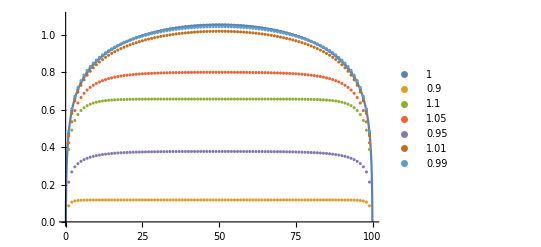

```mathematica
Show[Plot[1.0553+1/6 Log[Sin[(π x)/100]],{x,0,100},PlotRange-> {0,1.1}],ListPlot[X]]
```

Below is the evolution of the EE of the length 100 open Haagerup chain.

```mathematica
Manipulate[ListPlot[Y100[[i]],PlotRange->{0,0.83},PlotLabel-> "Sweep " <> ToString[10 i]],{{i,Length[Y100]},1,Length[Y100],1}]
```

Below is the evolution of the EE of the length 50 open Haagerup chain.

```mathematica
Manipulate[ListPlot[Y50[[i]],PlotRange->{0,0.71},PlotLabel-> "Sweep " <> ToString[10 i]],{{i,Length[Y50]},1,Length[Y50],1}]
```